```mathematica
<<Local`SrednickiInit`
```

#### 9.3) Consider a complex scalar ﬁeld (see problems 3.5, 5.1, and 8.7) with L = L0 + L1 , where L0 = −∂µϕ† ∂µ ϕ − m2 † ϕ , L1 = − 1 /4 Zλ λ(ϕ† ϕ) 2 + Lct , Lct = −(Zϕ −1)∂ µ ϕ† ∂µ ϕ − (Zm−1)m 2 ϕ† ϕ . This theory has two kinds of sources, J and J † , and so we need a way to tell which is which when we draw the diagrams. Rather than labeling the source blobs with a J or J † , we will indicate which is which by putting an arrow on the attached propagator that points towards the source if it is a J † , and away from the source if it is a J . a) What kind of vertex appears in the diagrams for this theory, and what is the associated vertex factor? Hint: your answer should involve those arrows! b) Ignoring the counterterms, draw all the connected diagrams with 1≤ E ≤ 4 and 0 ≤ V ≤ 2, and ﬁnd their symmetry factors. Hint: the arrows are important!

We follow the solution for the previous problem.

```mathematica
DefPrint["p93",ℒ->-1/2 PartialD[SuperDagger[φ][x[n,i]],μ]PartialD[φ[x[n,j]],ν]guu[μ,ν]
-m^2 SuperDagger[φ][x[n,i]]φ[x[n,i]]
-1/4 Subscript[Z, λ] λ SuperDagger[φ][x[n,i]]φ[x[n,i]]SuperDagger[φ][x[n,i]]φ[x[n,i]]]
DefPrint["e96",Z->Exp[I IntegralOp[{x[n,i]},Subscript[ℒ, 1][1/I δOp[J[x[n,i]]]]]].Subscript[Z, 0]]
DefPrint["e97",Subscript[Z, 0]->Exp[I/2 IntegralOp[{x[a,i],x[b,i]},SuperDagger[J][x[a,i]]. Δ[x[a,i]-x[b,i]].J[x[b,i]]]]]
DefPrint["e99",Subscript[ℒ, 1][φ_]->-1/4 Subscript[Z, λ]. λ.SuperDagger[φ].φ.SuperDagger[φ].φ]
t96=e96/.e99/.SuperDagger[δOp[a_]]->δOp[SuperDagger[a]]/.SuperDagger[J[a_]]->SuperDagger[J][a]
```

p93: ℒ→-1/2 (φ[x_nj^nj])_(,ν) (φ^*[x_ni^ni])_(,μ) g_μν^μν-m^2 φ[x_ni^ni] φ^*[x_ni^ni]-1/4 λ Z_λ φ[x_ni^ni]^2 (φ^*[x_ni^ni])^2

e96: Z→ⅇ^(ⅈ IntegralOp[{x_ni^ni},ℒ_1[-ⅈ δOp[J[x_ni^ni]]]]).Z_0

e97: Z_0→ⅇ^(1/2 ⅈ IntegralOp[{x_ai^ai,x_bi^bi},J^*[x_ai^ai].Δ[x_ai^ai-x_bi^bi].J[x_bi^bi]])

e99: ℒ_1[φ_]→-1/4 Z_λ.λ.φ^*.φ.φ^*.φ

Z→ⅇ^(ⅈ IntegralOp[{x_ni^ni},-1/4 Z_λ.λ.(ⅈ δOp[J^*[x_ni^ni]]).(-ⅈ δOp[J[x_ni^ni]]).(ⅈ δOp[J^*[x_ni^ni]]).(-ⅈ δOp[J[x_ni^ni]])]).Z_0

```mathematica
ordered={IntegralOp[_,_],δOp[_],J[_],SuperDagger[J][_],Δ[_],Subscript[Z, λ],λ};
nV=2;
nP=6;
t96=t96/.Exp[Y_]->Normal[Series[Exp[Y],{Y,0,nV}]]//.Power[IntegralOp[a_,b_],n_]:>DotPower[IntegralOp[a,b],n]//UniqueIntVars(*Z*);
t97=e97/.Exp[Y_]->Normal[Series[Exp[Y],{Y,0,nP}]]/.Power[IntegralOp[a_,b_],n_]:>DotPower[IntegralOp[a,b],n]//UniqueIntVars (*Z0*);

tmp=t96/.t97//UniqueIntVars;
tmp=dotRetain[ordered,tmp];

tmp[[2]]=tmp[[2]]//.IntDotInt2Int//.subIntInt2Int//dotRetain[ordered,#]&;
(***)
tmpSave=tmp
```

Z→1+ⅈ IntegralOp[{x_(145i)^(145i)},-1/4 Z_λ.λ.δOp[J^*[x_(145i)^(145i)]].δOp[J[x_(145i)^(145i)]].δOp[J^*[x_(145i)^(145i)]].δOp[J[x_(145i)^(145i)]]]-1/2 IntegralOp[{x_(55i)^(55i),x_(56i)^(56i)},1/16 Z_λ.λ.δOp[J^*[x_(55i)^(55i)]].δOp[J[x_(55i)^(55i)]].δOp[J^*[x_(55i)^(55i)]].δOp[J[x_(55i)^(55i)]].Z_λ.λ.δOp[J^*[x_(56i)^(56i)]].δOp[J[x_(56i)^(56i)]].δOp[J^*[x_(56i)^(56i)]].δOp[J[x_(56i)^(56i)]]]+1/2 ⅈ IntegralOp[{x_(146i)^(146i),x_(147i)^(147i)},J^*[x_(146i)^(146i)].Δ[x_(146i)^(146i)-x_(147i)^(147i)].J[x_(147i)^(147i)]]-1/2 IntegralOp[{x_(102i)^(102i),x_(103i)^(103i),x_(104i)^(104i)},-1/4 Z_λ.λ.δOp[J^*[x_(102i)^(102i)]].δOp[J[x_(102i)^(102i)]].δOp[J^*[x_(102i)^(102i)]].δOp[J[x_(102i)^(102i)]].J^*[x_(103i)^(103i)].Δ[x_(103i)^(103i)-x_(104i)^(104i)].J[x_(104i)^(104i)]]-1/4 ⅈ IntegralOp[{x_(51i)^(51i),x_(52i)^(52i),x_(53i)^(53i),x_(54i)^(54i)},1/16 Z_λ.λ.δOp[J^*[x_(51i)^(51i)]].δOp[J[x_(51i)^(51i)]].δOp[J^*[x_(51i)^(51i)]].δOp[J[x_(51i)^(51i)]].Z_λ.λ.δOp[J^*[x_(52i)^(52i)]].δOp[J[x_(52i)^(52i)]].δOp[J^*[x_(52i)^(52i)]].δOp[J[x_(52i)^(52i)]].J^*[x_(53i)^(53i)].Δ[x_(53i)^(53i)-x_(54i)^(54i)].J[x_(54i)^(54i)]]-1/8 IntegralOp[{x_(105i)^(105i),x_(106i)^(106i),x_(107i)^(107i),x_(108i)^(108i)},J^*[x_(105i)^(105i)].Δ[x_(105i)^(105i)-x_(106i)^(106i)].J[x_(106i)^(106i)].J^*[x_(107i)^(107i)].Δ[x_(107i)^(107i)-x_(108i)^(108i)].J[x_(108i)^(108i)]]-1/8 ⅈ IntegralOp[{x_(57i)^(57i),x_(58i)^(58i),x_(59i)^(59i),x_(60i)^(60i),x_(61i)^(61i)},-1/4 Z_λ.λ.δOp[J^*[x_(57i)^(57i)]].δOp[J[x_(57i)^(57i)]].δOp[J^*[x_(57i)^(57i)]].δOp[J[x_(57i)^(57i)]].J^*[x_(58i)^(58i)].Δ[x_(58i)^(58i)-x_(59i)^(59i)].J[x_(59i)^(59i)].J^*[x_(60i)^(60i)].Δ[x_(60i)^(60i)-x_(61i)^(61i)].J[x_(61i)^(61i)]]+1/16 IntegralOp[{x_(1i)^(1i),x_(2i)^(2i),x_(3i)^(3i),x_(4i)^(4i),x_(5i)^(5i),x_(6i)^(6i)},1/16 Z_λ.λ.δOp[J^*[x_(1i)^(1i)]].δOp[J[x_(1i)^(1i)]].δOp[J^*[x_(1i)^(1i)]].δOp[J[x_(1i)^(1i)]].Z_λ.λ.δOp[J^*[x_(2i)^(2i)]].δOp[J[x_(2i)^(2i)]].δOp[J^*[x_(2i)^(2i)]].δOp[J[x_(2i)^(2i)]].J^*[x_(3i)^(3i)].Δ[x_(3i)^(3i)-x_(4i)^(4i)].J[x_(4i)^(4i)].J^*[x_(5i)^(5i)].Δ[x_(5i)^(5i)-x_(6i)^(6i)].J[x_(6i)^(6i)]]-1/48 ⅈ IntegralOp[{x_(109i)^(109i),x_(110i)^(110i),x_(111i)^(111i),x_(112i)^(112i),x_(113i)^(113i),x_(114i)^(114i)},J^*[x_(109i)^(109i)].Δ[x_(109i)^(109i)-x_(110i)^(110i)].J[x_(110i)^(110i)].J^*[x_(111i)^(111i)].Δ[x_(111i)^(111i)-x_(112i)^(112i)].J[x_(112i)^(112i)].J^*[x_(113i)^(113i)].Δ[x_(113i)^(113i)-x_(114i)^(114i)].J[x_(114i)^(114i)]]+1/48 IntegralOp[{x_(62i)^(62i),x_(63i)^(63i),x_(64i)^(64i),x_(65i)^(65i),x_(66i)^(66i),x_(67i)^(67i),x_(68i)^(68i)},-1/4 Z_λ.λ.δOp[J^*[x_(62i)^(62i)]].δOp[J[x_(62i)^(62i)]].δOp[J^*[x_(62i)^(62i)]].δOp[J[x_(62i)^(62i)]].J^*[x_(63i)^(63i)].Δ[x_(63i)^(63i)-x_(64i)^(64i)].J[x_(64i)^(64i)].J^*[x_(65i)^(65i)].Δ[x_(65i)^(65i)-x_(66i)^(66i)].J[x_(66i)^(66i)].J^*[x_(67i)^(67i)].Δ[x_(67i)^(67i)-x_(68i)^(68i)].J[x_(68i)^(68i)]]+1/96 ⅈ IntegralOp[{x_(7i)^(7i),x_(8i)^(8i),x_(9i)^(9i),x_(10i)^(10i),x_(11i)^(11i),x_(12i)^(12i),x_(13i)^(13i),x_(14i)^(14i)},1/16 Z_λ.λ.δOp[J^*[x_(7i)^(7i)]].δOp[J[x_(7i)^(7i)]].δOp[J^*[x_(7i)^(7i)]].δOp[J[x_(7i)^(7i)]].Z_λ.λ.δOp[J^*[x_(8i)^(8i)]].δOp[J[x_(8i)^(8i)]].δOp[J^*[x_(8i)^(8i)]].δOp[J[x_(8i)^(8i)]].J^*[x_(9i)^(9i)].Δ[x_(9i)^(9i)-x_(10i)^(10i)].J[x_(10i)^(10i)].J^*[x_(11i)^(11i)].Δ[x_(11i)^(11i)-x_(12i)^(12i)].J[x_(12i)^(12i)].J^*[x_(13i)^(13i)].Δ[x_(13i)^(13i)-x_(14i)^(14i)].J[x_(14i)^(14i)]]+1/384 IntegralOp[{x_(115i)^(115i),x_(116i)^(116i),x_(117i)^(117i),x_(118i)^(118i),x_(119i)^(119i),x_(120i)^(120i),x_(121i)^(121i),x_(122i)^(122i)},J^*[x_(115i)^(115i)].Δ[x_(115i)^(115i)-x_(116i)^(116i)].J[x_(116i)^(116i)].J^*[x_(117i)^(117i)].Δ[x_(117i)^(117i)-x_(118i)^(118i)].J[x_(118i)^(118i)].J^*[x_(119i)^(119i)].Δ[x_(119i)^(119i)-x_(120i)^(120i)].J[x_(120i)^(120i)].J^*[x_(121i)^(121i)].Δ[x_(121i)^(121i)-x_(122i)^(122i)].J[x_(122i)^(122i)]]+1/384 ⅈ IntegralOp[{x_(69i)^(69i),x_(70i)^(70i),x_(71i)^(71i),x_(72i)^(72i),x_(73i)^(73i),x_(74i)^(74i),x_(75i)^(75i),x_(76i)^(76i),x_(77i)^(77i)},-1/4 Z_λ.λ.δOp[J^*[x_(69i)^(69i)]].δOp[J[x_(69i)^(69i)]].δOp[J^*[x_(69i)^(69i)]].δOp[J[x_(69i)^(69i)]].J^*[x_(70i)^(70i)].Δ[x_(70i)^(70i)-x_(71i)^(71i)].J[x_(71i)^(71i)].J^*[x_(72i)^(72i)].Δ[x_(72i)^(72i)-x_(73i)^(73i)].J[x_(73i)^(73i)].J^*[x_(74i)^(74i)].Δ[x_(74i)^(74i)-x_(75i)^(75i)].J[x_(75i)^(75i)].J^*[x_(76i)^(76i)].Δ[x_(76i)^(76i)-x_(77i)^(77i)].J[x_(77i)^(77i)]]-1/768 IntegralOp[{x_(15i)^(15i),x_(16i)^(16i),x_(17i)^(17i),x_(18i)^(18i),x_(19i)^(19i),x_(20i)^(20i),x_(21i)^(21i),x_(22i)^(22i),x_(23i)^(23i),x_(24i)^(24i)},1/16 Z_λ.λ.δOp[J^*[x_(15i)^(15i)]].δOp[J[x_(15i)^(15i)]].δOp[J^*[x_(15i)^(15i)]].δOp[J[x_(15i)^(15i)]].Z_λ.λ.δOp[J^*[x_(16i)^(16i)]].δOp[J[x_(16i)^(16i)]].δOp[J^*[x_(16i)^(16i)]].δOp[J[x_(16i)^(16i)]].J^*[x_(17i)^(17i)].Δ[x_(17i)^(17i)-x_(18i)^(18i)].J[x_(18i)^(18i)].J^*[x_(19i)^(19i)].Δ[x_(19i)^(19i)-x_(20i)^(20i)].J[x_(20i)^(20i)].J^*[x_(21i)^(21i)].Δ[x_(21i)^(21i)-x_(22i)^(22i)].J[x_(22i)^(22i)].J^*[x_(23i)^(23i)].Δ[x_(23i)^(23i)-x_(24i)^(24i)].J[x_(24i)^(24i)]]+1/3840 ⅈ IntegralOp[{x_(123i)^(123i),x_(124i)^(124i),x_(125i)^(125i),x_(126i)^(126i),x_(127i)^(127i),x_(128i)^(128i),x_(129i)^(129i),x_(130i)^(130i),x_(131i)^(131i),x_(132i)^(132i)},J^*[x_(123i)^(123i)].Δ[x_(123i)^(123i)-x_(124i)^(124i)].J[x_(124i)^(124i)].J^*[x_(125i)^(125i)].Δ[x_(125i)^(125i)-x_(126i)^(126i)].J[x_(126i)^(126i)].J^*[x_(127i)^(127i)].Δ[x_(127i)^(127i)-x_(128i)^(128i)].J[x_(128i)^(128i)].J^*[x_(129i)^(129i)].Δ[x_(129i)^(129i)-x_(130i)^(130i)].J[x_(130i)^(130i)].J^*[x_(131i)^(131i)].Δ[x_(131i)^(131i)-x_(132i)^(132i)].J[x_(132i)^(132i)]]-1/3840 IntegralOp[{x_(78i)^(78i),x_(79i)^(79i),x_(80i)^(80i),x_(81i)^(81i),x_(82i)^(82i),x_(83i)^(83i),x_(84i)^(84i),x_(85i)^(85i),x_(86i)^(86i),x_(87i)^(87i),x_(88i)^(88i)},-1/4 Z_λ.λ.δOp[J^*[x_(78i)^(78i)]].δOp[J[x_(78i)^(78i)]].δOp[J^*[x_(78i)^(78i)]].δOp[J[x_(78i)^(78i)]].J^*[x_(79i)^(79i)].Δ[x_(79i)^(79i)-x_(80i)^(80i)].J[x_(80i)^(80i)].J^*[x_(81i)^(81i)].Δ[x_(81i)^(81i)-x_(82i)^(82i)].J[x_(82i)^(82i)].J^*[x_(83i)^(83i)].Δ[x_(83i)^(83i)-x_(84i)^(84i)].J[x_(84i)^(84i)].J^*[x_(85i)^(85i)].Δ[x_(85i)^(85i)-x_(86i)^(86i)].J[x_(86i)^(86i)].J^*[x_(87i)^(87i)].Δ[x_(87i)^(87i)-x_(88i)^(88i)].J[x_(88i)^(88i)]]-1/7680 ⅈ IntegralOp[{x_(25i)^(25i),x_(26i)^(26i),x_(27i)^(27i),x_(28i)^(28i),x_(29i)^(29i),x_(30i)^(30i),x_(31i)^(31i),x_(32i)^(32i),x_(33i)^(33i),x_(34i)^(34i),x_(35i)^(35i),x_(36i)^(36i)},1/16 Z_λ.λ.δOp[J^*[x_(25i)^(25i)]].δOp[J[x_(25i)^(25i)]].δOp[J^*[x_(25i)^(25i)]].δOp[J[x_(25i)^(25i)]].Z_λ.λ.δOp[J^*[x_(26i)^(26i)]].δOp[J[x_(26i)^(26i)]].δOp[J^*[x_(26i)^(26i)]].δOp[J[x_(26i)^(26i)]].J^*[x_(27i)^(27i)].Δ[x_(27i)^(27i)-x_(28i)^(28i)].J[x_(28i)^(28i)].J^*[x_(29i)^(29i)].Δ[x_(29i)^(29i)-x_(30i)^(30i)].J[x_(30i)^(30i)].J^*[x_(31i)^(31i)].Δ[x_(31i)^(31i)-x_(32i)^(32i)].J[x_(32i)^(32i)].J^*[x_(33i)^(33i)].Δ[x_(33i)^(33i)-x_(34i)^(34i)].J[x_(34i)^(34i)].J^*[x_(35i)^(35i)].Δ[x_(35i)^(35i)-x_(36i)^(36i)].J[x_(36i)^(36i)]]-1/46080 IntegralOp[{x_(133i)^(133i),x_(134i)^(134i),x_(135i)^(135i),x_(136i)^(136i),x_(137i)^(137i),x_(138i)^(138i),x_(139i)^(139i),x_(140i)^(140i),x_(141i)^(141i),x_(142i)^(142i),x_(143i)^(143i),x_(144i)^(144i)},J^*[x_(133i)^(133i)].Δ[x_(133i)^(133i)-x_(134i)^(134i)].J[x_(134i)^(134i)].J^*[x_(135i)^(135i)].Δ[x_(135i)^(135i)-x_(136i)^(136i)].J[x_(136i)^(136i)].J^*[x_(137i)^(137i)].Δ[x_(137i)^(137i)-x_(138i)^(138i)].J[x_(138i)^(138i)].J^*[x_(139i)^(139i)].Δ[x_(139i)^(139i)-x_(140i)^(140i)].J[x_(140i)^(140i)].J^*[x_(141i)^(141i)].Δ[x_(141i)^(141i)-x_(142i)^(142i)].J[x_(142i)^(142i)].J^*[x_(143i)^(143i)].Δ[x_(143i)^(143i)-x_(144i)^(144i)].J[x_(144i)^(144i)]]-1/46080 ⅈ IntegralOp[{x_(89i)^(89i),x_(90i)^(90i),x_(91i)^(91i),x_(92i)^(92i),x_(93i)^(93i),x_(94i)^(94i),x_(95i)^(95i),x_(96i)^(96i),x_(97i)^(97i),x_(98i)^(98i),x_(99i)^(99i),x_(100i)^(100i),x_(101i)^(101i)},-1/4 Z_λ.λ.δOp[J^*[x_(89i)^(89i)]].δOp[J[x_(89i)^(89i)]].δOp[J^*[x_(89i)^(89i)]].δOp[J[x_(89i)^(89i)]].J^*[x_(90i)^(90i)].Δ[x_(90i)^(90i)-x_(91i)^(91i)].J[x_(91i)^(91i)].J^*[x_(92i)^(92i)].Δ[x_(92i)^(92i)-x_(93i)^(93i)].J[x_(93i)^(93i)].J^*[x_(94i)^(94i)].Δ[x_(94i)^(94i)-x_(95i)^(95i)].J[x_(95i)^(95i)].J^*[x_(96i)^(96i)].Δ[x_(96i)^(96i)-x_(97i)^(97i)].J[x_(97i)^(97i)].J^*[x_(98i)^(98i)].Δ[x_(98i)^(98i)-x_(99i)^(99i)].J[x_(99i)^(99i)].J^*[x_(100i)^(100i)].Δ[x_(100i)^(100i)-x_(101i)^(101i)].J[x_(101i)^(101i)]]+1/92160 IntegralOp[{x_(37i)^(37i),x_(38i)^(38i),x_(39i)^(39i),x_(40i)^(40i),x_(41i)^(41i),x_(42i)^(42i),x_(43i)^(43i),x_(44i)^(44i),x_(45i)^(45i),x_(46i)^(46i),x_(47i)^(47i),x_(48i)^(48i),x_(49i)^(49i),x_(50i)^(50i)},1/16 Z_λ.λ.δOp[J^*[x_(37i)^(37i)]].δOp[J[x_(37i)^(37i)]].δOp[J^*[x_(37i)^(37i)]].δOp[J[x_(37i)^(37i)]].Z_λ.λ.δOp[J^*[x_(38i)^(38i)]].δOp[J[x_(38i)^(38i)]].δOp[J^*[x_(38i)^(38i)]].δOp[J[x_(38i)^(38i)]].J^*[x_(39i)^(39i)].Δ[x_(39i)^(39i)-x_(40i)^(40i)].J[x_(40i)^(40i)].J^*[x_(41i)^(41i)].Δ[x_(41i)^(41i)-x_(42i)^(42i)].J[x_(42i)^(42i)].J^*[x_(43i)^(43i)].Δ[x_(43i)^(43i)-x_(44i)^(44i)].J[x_(44i)^(44i)].J^*[x_(45i)^(45i)].Δ[x_(45i)^(45i)-x_(46i)^(46i)].J[x_(46i)^(46i)].J^*[x_(47i)^(47i)].Δ[x_(47i)^(47i)-x_(48i)^(48i)].J[x_(48i)^(48i)].J^*[x_(49i)^(49i)].Δ[x_(49i)^(49i)-x_(50i)^(50i)].J[x_(50i)^(50i)]]

```mathematica
tmp1=tmpSave[[2]](*select terms to plot*)
tmp1>>"saveSrednicki.9.3.tmpx"
tmp1=OpδIntegrand[tmp1]/.cleanInt;
tmp1>>"saveSrednicki.9.3.tmp1"

tmp2=findEvalIntDelta[tmp1];
tmp2>>"saveSrednicki.9.3.tmp2"
M1
tmp3=UniformIntVar1[tmp2];
tmp3>>"saveSrednicki.9.3.tmp3"
M2
tmp4=tmp3/.Null->0/.Dot->Times//Expand;
tmp4>>"saveSrednicki.9.3.tmp4"
M3
tmp5=gatherIntFast[tmp4];
tmp5>>"saveSrednicki.9.3.tmp5"
Position[tmp5,IntegralOp];
tmp6=tmp5/.Δ[-x[a_,i]+x[b_,i]]->Δd[M[a]M[b] ]/.Δd[M[a_] M[b_]]->Δ[x[a,i]- x[b,i]];
(*sign of argument of Δ not important*)
tmp6>>"saveSrednicki.9.3.tmp6"
tmp7=RearrangeIntJArg[tmp6];
```

1+ⅈ IntegralOp[{x_(145i)^(145i)},-1/4 Z_λ.λ.δOp[J^*[x_(145i)^(145i)]].δOp[J[x_(145i)^(145i)]].δOp[J^*[x_(145i)^(145i)]].δOp[J[x_(145i)^(145i)]]]-1/2 IntegralOp[{x_(55i)^(55i),x_(56i)^(56i)},1/16 Z_λ.λ.δOp[J^*[x_(55i)^(55i)]].δOp[J[x_(55i)^(55i)]].δOp[J^*[x_(55i)^(55i)]].δOp[J[x_(55i)^(55i)]].Z_λ.λ.δOp[J^*[x_(56i)^(56i)]].δOp[J[x_(56i)^(56i)]].δOp[J^*[x_(56i)^(56i)]].δOp[J[x_(56i)^(56i)]]]+1/2 ⅈ IntegralOp[{x_(146i)^(146i),x_(147i)^(147i)},J^*[x_(146i)^(146i)].Δ[x_(146i)^(146i)-x_(147i)^(147i)].J[x_(147i)^(147i)]]-1/2 IntegralOp[{x_(102i)^(102i),x_(103i)^(103i),x_(104i)^(104i)},-1/4 Z_λ.λ.δOp[J^*[x_(102i)^(102i)]].δOp[J[x_(102i)^(102i)]].δOp[J^*[x_(102i)^(102i)]].δOp[J[x_(102i)^(102i)]].J^*[x_(103i)^(103i)].Δ[x_(103i)^(103i)-x_(104i)^(104i)].J[x_(104i)^(104i)]]-1/4 ⅈ IntegralOp[{x_(51i)^(51i),x_(52i)^(52i),x_(53i)^(53i),x_(54i)^(54i)},1/16 Z_λ.λ.δOp[J^*[x_(51i)^(51i)]].δOp[J[x_(51i)^(51i)]].δOp[J^*[x_(51i)^(51i)]].δOp[J[x_(51i)^(51i)]].Z_λ.λ.δOp[J^*[x_(52i)^(52i)]].δOp[J[x_(52i)^(52i)]].δOp[J^*[x_(52i)^(52i)]].δOp[J[x_(52i)^(52i)]].J^*[x_(53i)^(53i)].Δ[x_(53i)^(53i)-x_(54i)^(54i)].J[x_(54i)^(54i)]]-1/8 IntegralOp[{x_(105i)^(105i),x_(106i)^(106i),x_(107i)^(107i),x_(108i)^(108i)},J^*[x_(105i)^(105i)].Δ[x_(105i)^(105i)-x_(106i)^(106i)].J[x_(106i)^(106i)].J^*[x_(107i)^(107i)].Δ[x_(107i)^(107i)-x_(108i)^(108i)].J[x_(108i)^(108i)]]-1/8 ⅈ IntegralOp[{x_(57i)^(57i),x_(58i)^(58i),x_(59i)^(59i),x_(60i)^(60i),x_(61i)^(61i)},-1/4 Z_λ.λ.δOp[J^*[x_(57i)^(57i)]].δOp[J[x_(57i)^(57i)]].δOp[J^*[x_(57i)^(57i)]].δOp[J[x_(57i)^(57i)]].J^*[x_(58i)^(58i)].Δ[x_(58i)^(58i)-x_(59i)^(59i)].J[x_(59i)^(59i)].J^*[x_(60i)^(60i)].Δ[x_(60i)^(60i)-x_(61i)^(61i)].J[x_(61i)^(61i)]]+1/16 IntegralOp[{x_(1i)^(1i),x_(2i)^(2i),x_(3i)^(3i),x_(4i)^(4i),x_(5i)^(5i),x_(6i)^(6i)},1/16 Z_λ.λ.δOp[J^*[x_(1i)^(1i)]].δOp[J[x_(1i)^(1i)]].δOp[J^*[x_(1i)^(1i)]].δOp[J[x_(1i)^(1i)]].Z_λ.λ.δOp[J^*[x_(2i)^(2i)]].δOp[J[x_(2i)^(2i)]].δOp[J^*[x_(2i)^(2i)]].δOp[J[x_(2i)^(2i)]].J^*[x_(3i)^(3i)].Δ[x_(3i)^(3i)-x_(4i)^(4i)].J[x_(4i)^(4i)].J^*[x_(5i)^(5i)].Δ[x_(5i)^(5i)-x_(6i)^(6i)].J[x_(6i)^(6i)]]-1/48 ⅈ IntegralOp[{x_(109i)^(109i),x_(110i)^(110i),x_(111i)^(111i),x_(112i)^(112i),x_(113i)^(113i),x_(114i)^(114i)},J^*[x_(109i)^(109i)].Δ[x_(109i)^(109i)-x_(110i)^(110i)].J[x_(110i)^(110i)].J^*[x_(111i)^(111i)].Δ[x_(111i)^(111i)-x_(112i)^(112i)].J[x_(112i)^(112i)].J^*[x_(113i)^(113i)].Δ[x_(113i)^(113i)-x_(114i)^(114i)].J[x_(114i)^(114i)]]+1/48 IntegralOp[{x_(62i)^(62i),x_(63i)^(63i),x_(64i)^(64i),x_(65i)^(65i),x_(66i)^(66i),x_(67i)^(67i),x_(68i)^(68i)},-1/4 Z_λ.λ.δOp[J^*[x_(62i)^(62i)]].δOp[J[x_(62i)^(62i)]].δOp[J^*[x_(62i)^(62i)]].δOp[J[x_(62i)^(62i)]].J^*[x_(63i)^(63i)].Δ[x_(63i)^(63i)-x_(64i)^(64i)].J[x_(64i)^(64i)].J^*[x_(65i)^(65i)].Δ[x_(65i)^(65i)-x_(66i)^(66i)].J[x_(66i)^(66i)].J^*[x_(67i)^(67i)].Δ[x_(67i)^(67i)-x_(68i)^(68i)].J[x_(68i)^(68i)]]+1/96 ⅈ IntegralOp[{x_(7i)^(7i),x_(8i)^(8i),x_(9i)^(9i),x_(10i)^(10i),x_(11i)^(11i),x_(12i)^(12i),x_(13i)^(13i),x_(14i)^(14i)},1/16 Z_λ.λ.δOp[J^*[x_(7i)^(7i)]].δOp[J[x_(7i)^(7i)]].δOp[J^*[x_(7i)^(7i)]].δOp[J[x_(7i)^(7i)]].Z_λ.λ.δOp[J^*[x_(8i)^(8i)]].δOp[J[x_(8i)^(8i)]].δOp[J^*[x_(8i)^(8i)]].δOp[J[x_(8i)^(8i)]].J^*[x_(9i)^(9i)].Δ[x_(9i)^(9i)-x_(10i)^(10i)].J[x_(10i)^(10i)].J^*[x_(11i)^(11i)].Δ[x_(11i)^(11i)-x_(12i)^(12i)].J[x_(12i)^(12i)].J^*[x_(13i)^(13i)].Δ[x_(13i)^(13i)-x_(14i)^(14i)].J[x_(14i)^(14i)]]+1/384 IntegralOp[{x_(115i)^(115i),x_(116i)^(116i),x_(117i)^(117i),x_(118i)^(118i),x_(119i)^(119i),x_(120i)^(120i),x_(121i)^(121i),x_(122i)^(122i)},J^*[x_(115i)^(115i)].Δ[x_(115i)^(115i)-x_(116i)^(116i)].J[x_(116i)^(116i)].J^*[x_(117i)^(117i)].Δ[x_(117i)^(117i)-x_(118i)^(118i)].J[x_(118i)^(118i)].J^*[x_(119i)^(119i)].Δ[x_(119i)^(119i)-x_(120i)^(120i)].J[x_(120i)^(120i)].J^*[x_(121i)^(121i)].Δ[x_(121i)^(121i)-x_(122i)^(122i)].J[x_(122i)^(122i)]]+1/384 ⅈ IntegralOp[{x_(69i)^(69i),x_(70i)^(70i),x_(71i)^(71i),x_(72i)^(72i),x_(73i)^(73i),x_(74i)^(74i),x_(75i)^(75i),x_(76i)^(76i),x_(77i)^(77i)},-1/4 Z_λ.λ.δOp[J^*[x_(69i)^(69i)]].δOp[J[x_(69i)^(69i)]].δOp[J^*[x_(69i)^(69i)]].δOp[J[x_(69i)^(69i)]].J^*[x_(70i)^(70i)].Δ[x_(70i)^(70i)-x_(71i)^(71i)].J[x_(71i)^(71i)].J^*[x_(72i)^(72i)].Δ[x_(72i)^(72i)-x_(73i)^(73i)].J[x_(73i)^(73i)].J^*[x_(74i)^(74i)].Δ[x_(74i)^(74i)-x_(75i)^(75i)].J[x_(75i)^(75i)].J^*[x_(76i)^(76i)].Δ[x_(76i)^(76i)-x_(77i)^(77i)].J[x_(77i)^(77i)]]-1/768 IntegralOp[{x_(15i)^(15i),x_(16i)^(16i),x_(17i)^(17i),x_(18i)^(18i),x_(19i)^(19i),x_(20i)^(20i),x_(21i)^(21i),x_(22i)^(22i),x_(23i)^(23i),x_(24i)^(24i)},1/16 Z_λ.λ.δOp[J^*[x_(15i)^(15i)]].δOp[J[x_(15i)^(15i)]].δOp[J^*[x_(15i)^(15i)]].δOp[J[x_(15i)^(15i)]].Z_λ.λ.δOp[J^*[x_(16i)^(16i)]].δOp[J[x_(16i)^(16i)]].δOp[J^*[x_(16i)^(16i)]].δOp[J[x_(16i)^(16i)]].J^*[x_(17i)^(17i)].Δ[x_(17i)^(17i)-x_(18i)^(18i)].J[x_(18i)^(18i)].J^*[x_(19i)^(19i)].Δ[x_(19i)^(19i)-x_(20i)^(20i)].J[x_(20i)^(20i)].J^*[x_(21i)^(21i)].Δ[x_(21i)^(21i)-x_(22i)^(22i)].J[x_(22i)^(22i)].J^*[x_(23i)^(23i)].Δ[x_(23i)^(23i)-x_(24i)^(24i)].J[x_(24i)^(24i)]]+1/3840 ⅈ IntegralOp[{x_(123i)^(123i),x_(124i)^(124i),x_(125i)^(125i),x_(126i)^(126i),x_(127i)^(127i),x_(128i)^(128i),x_(129i)^(129i),x_(130i)^(130i),x_(131i)^(131i),x_(132i)^(132i)},J^*[x_(123i)^(123i)].Δ[x_(123i)^(123i)-x_(124i)^(124i)].J[x_(124i)^(124i)].J^*[x_(125i)^(125i)].Δ[x_(125i)^(125i)-x_(126i)^(126i)].J[x_(126i)^(126i)].J^*[x_(127i)^(127i)].Δ[x_(127i)^(127i)-x_(128i)^(128i)].J[x_(128i)^(128i)].J^*[x_(129i)^(129i)].Δ[x_(129i)^(129i)-x_(130i)^(130i)].J[x_(130i)^(130i)].J^*[x_(131i)^(131i)].Δ[x_(131i)^(131i)-x_(132i)^(132i)].J[x_(132i)^(132i)]]-1/3840 IntegralOp[{x_(78i)^(78i),x_(79i)^(79i),x_(80i)^(80i),x_(81i)^(81i),x_(82i)^(82i),x_(83i)^(83i),x_(84i)^(84i),x_(85i)^(85i),x_(86i)^(86i),x_(87i)^(87i),x_(88i)^(88i)},-1/4 Z_λ.λ.δOp[J^*[x_(78i)^(78i)]].δOp[J[x_(78i)^(78i)]].δOp[J^*[x_(78i)^(78i)]].δOp[J[x_(78i)^(78i)]].J^*[x_(79i)^(79i)].Δ[x_(79i)^(79i)-x_(80i)^(80i)].J[x_(80i)^(80i)].J^*[x_(81i)^(81i)].Δ[x_(81i)^(81i)-x_(82i)^(82i)].J[x_(82i)^(82i)].J^*[x_(83i)^(83i)].Δ[x_(83i)^(83i)-x_(84i)^(84i)].J[x_(84i)^(84i)].J^*[x_(85i)^(85i)].Δ[x_(85i)^(85i)-x_(86i)^(86i)].J[x_(86i)^(86i)].J^*[x_(87i)^(87i)].Δ[x_(87i)^(87i)-x_(88i)^(88i)].J[x_(88i)^(88i)]]-1/7680 ⅈ IntegralOp[{x_(25i)^(25i),x_(26i)^(26i),x_(27i)^(27i),x_(28i)^(28i),x_(29i)^(29i),x_(30i)^(30i),x_(31i)^(31i),x_(32i)^(32i),x_(33i)^(33i),x_(34i)^(34i),x_(35i)^(35i),x_(36i)^(36i)},1/16 Z_λ.λ.δOp[J^*[x_(25i)^(25i)]].δOp[J[x_(25i)^(25i)]].δOp[J^*[x_(25i)^(25i)]].δOp[J[x_(25i)^(25i)]].Z_λ.λ.δOp[J^*[x_(26i)^(26i)]].δOp[J[x_(26i)^(26i)]].δOp[J^*[x_(26i)^(26i)]].δOp[J[x_(26i)^(26i)]].J^*[x_(27i)^(27i)].Δ[x_(27i)^(27i)-x_(28i)^(28i)].J[x_(28i)^(28i)].J^*[x_(29i)^(29i)].Δ[x_(29i)^(29i)-x_(30i)^(30i)].J[x_(30i)^(30i)].J^*[x_(31i)^(31i)].Δ[x_(31i)^(31i)-x_(32i)^(32i)].J[x_(32i)^(32i)].J^*[x_(33i)^(33i)].Δ[x_(33i)^(33i)-x_(34i)^(34i)].J[x_(34i)^(34i)].J^*[x_(35i)^(35i)].Δ[x_(35i)^(35i)-x_(36i)^(36i)].J[x_(36i)^(36i)]]-1/46080 IntegralOp[{x_(133i)^(133i),x_(134i)^(134i),x_(135i)^(135i),x_(136i)^(136i),x_(137i)^(137i),x_(138i)^(138i),x_(139i)^(139i),x_(140i)^(140i),x_(141i)^(141i),x_(142i)^(142i),x_(143i)^(143i),x_(144i)^(144i)},J^*[x_(133i)^(133i)].Δ[x_(133i)^(133i)-x_(134i)^(134i)].J[x_(134i)^(134i)].J^*[x_(135i)^(135i)].Δ[x_(135i)^(135i)-x_(136i)^(136i)].J[x_(136i)^(136i)].J^*[x_(137i)^(137i)].Δ[x_(137i)^(137i)-x_(138i)^(138i)].J[x_(138i)^(138i)].J^*[x_(139i)^(139i)].Δ[x_(139i)^(139i)-x_(140i)^(140i)].J[x_(140i)^(140i)].J^*[x_(141i)^(141i)].Δ[x_(141i)^(141i)-x_(142i)^(142i)].J[x_(142i)^(142i)].J^*[x_(143i)^(143i)].Δ[x_(143i)^(143i)-x_(144i)^(144i)].J[x_(144i)^(144i)]]-1/46080 ⅈ IntegralOp[{x_(89i)^(89i),x_(90i)^(90i),x_(91i)^(91i),x_(92i)^(92i),x_(93i)^(93i),x_(94i)^(94i),x_(95i)^(95i),x_(96i)^(96i),x_(97i)^(97i),x_(98i)^(98i),x_(99i)^(99i),x_(100i)^(100i),x_(101i)^(101i)},-1/4 Z_λ.λ.δOp[J^*[x_(89i)^(89i)]].δOp[J[x_(89i)^(89i)]].δOp[J^*[x_(89i)^(89i)]].δOp[J[x_(89i)^(89i)]].J^*[x_(90i)^(90i)].Δ[x_(90i)^(90i)-x_(91i)^(91i)].J[x_(91i)^(91i)].J^*[x_(92i)^(92i)].Δ[x_(92i)^(92i)-x_(93i)^(93i)].J[x_(93i)^(93i)].J^*[x_(94i)^(94i)].Δ[x_(94i)^(94i)-x_(95i)^(95i)].J[x_(95i)^(95i)].J^*[x_(96i)^(96i)].Δ[x_(96i)^(96i)-x_(97i)^(97i)].J[x_(97i)^(97i)].J^*[x_(98i)^(98i)].Δ[x_(98i)^(98i)-x_(99i)^(99i)].J[x_(99i)^(99i)].J^*[x_(100i)^(100i)].Δ[x_(100i)^(100i)-x_(101i)^(101i)].J[x_(101i)^(101i)]]+1/92160 IntegralOp[{x_(37i)^(37i),x_(38i)^(38i),x_(39i)^(39i),x_(40i)^(40i),x_(41i)^(41i),x_(42i)^(42i),x_(43i)^(43i),x_(44i)^(44i),x_(45i)^(45i),x_(46i)^(46i),x_(47i)^(47i),x_(48i)^(48i),x_(49i)^(49i),x_(50i)^(50i)},1/16 Z_λ.λ.δOp[J^*[x_(37i)^(37i)]].δOp[J[x_(37i)^(37i)]].δOp[J^*[x_(37i)^(37i)]].δOp[J[x_(37i)^(37i)]].Z_λ.λ.δOp[J^*[x_(38i)^(38i)]].δOp[J[x_(38i)^(38i)]].δOp[J^*[x_(38i)^(38i)]].δOp[J[x_(38i)^(38i)]].J^*[x_(39i)^(39i)].Δ[x_(39i)^(39i)-x_(40i)^(40i)].J[x_(40i)^(40i)].J^*[x_(41i)^(41i)].Δ[x_(41i)^(41i)-x_(42i)^(42i)].J[x_(42i)^(42i)].J^*[x_(43i)^(43i)].Δ[x_(43i)^(43i)-x_(44i)^(44i)].J[x_(44i)^(44i)].J^*[x_(45i)^(45i)].Δ[x_(45i)^(45i)-x_(46i)^(46i)].J[x_(46i)^(46i)].J^*[x_(47i)^(47i)].Δ[x_(47i)^(47i)-x_(48i)^(48i)].J[x_(48i)^(48i)].J^*[x_(49i)^(49i)].Δ[x_(49i)^(49i)-x_(50i)^(50i)].J[x_(50i)^(50i)]]

1

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

DEBUGfind:9406:{{3,2,1},{3,2,2},{3,2,3},{3,2,4},{3,2,5},{3,2,6},{3,2,7},{3,2,8},{3,2,9},{4,2,1},{4,2,2},{4,2,3},{4,2,4},{4,2,5},{4,2,6},{4,2,7},{4,2,8},{4,2,9},{4,2,10},{4,2,11},{4,2,12},{4,2,13},{4,2,14},{4,2,15},{4,2,16},{4,2,17},{4,2,18},{4,2,19},{4,2,20},{4,2,21},{4,2,22},{4,2,23},{4,2,24},{4,2,25},{4,2,26},{4,2,27},{4,2,28},{4,2,29},{4,2,30},{4,2,31},{4,2,32},{4,2,33},{4,2,34},{4,2,35},{4,2,36},{5,2,1,2},{5,2,2,2},{5,2,3,2},{5,2,4,2},{5,2,5,2},{5,2,6,2},{5,2,7,2},{5,2,8,2},{5,2,9,2},{5,2,10,2},{5,2,11,2},{5,2,12,2},{5,2,13,2},{5,2,14,2},{5,2,15,2},{5,2,16,2},{5,2,17,2},{5,2,18,2},{5,2,19,2},{5,2,20,2},{5,2,21,2},{5,2,22,2},{5,2,23,2},{5,2,24,2},{5,2,25,2},{5,2,26,2},{5,2,27,2},{5,2,28,2},{5,2,29,2},{5,2,30,2},{5,2,31,2},{5,2,32,2},{5,2,33,2},{5,2,34,2},{5,2,35,2},{5,2,36,2},{6,2,1,2},{6,2,2,2},{6,2,3,2},{6,2,4,2},{6,2,5,2},{6,2,6,2},{6,2,7,2},{6,2,8,2},{6,2,9,2},{6,2,10,2},{6,2,11,2},{6,2,12,2},{6,2,13,2},{6,2,14,2},{6,2,15,2},{6,2,16,2},{6,2,17,2},{6,2,18,2},{6,2,19,2},{6,2,20,2},{6,2,21,2},{6,2,22,2},{6,2,23,2},{6,2,24,2},{6,2,25,2},{6,2,26,2},{6,2,27,2},{6,2,28,2},{6,2,29,2},{6,2,30,2},{6,2,31,2},{6,2,32,2},{6,2,33,2},{6,2,34,2},{6,2,35,2},{6,2,36,2},{6,2,37,2},{6,2,38,2},{6,2,39,2},{6,2,40,2},{6,2,41,2},{6,2,42,2},{6,2,43,2},{6,2,44,2},{6,2,45,2},{6,2,46,2},{6,2,47,2},{6,2,48,2},{6,2,49,2},{6,2,50,2},{6,2,51,2},{6,2,52,2},{6,2,53,2},{6,2,54,2},{6,2,55,2},{6,2,56,2},{6,2,57,2},{6,2,58,2},{6,2,59,2},{6,2,60,2},{6,2,61,2},{6,2,62,2},{6,2,63,2},{6,2,64,2},{6,2,65,2},{6,2,66,2},{6,2,67,2},{6,2,68,2},{6,2,69,2},{6,2,70,2},{6,2,71,2},{6,2,72,2},{6,2,73,2},{6,2,74,2},{6,2,75,2},{6,2,76,2},{6,2,77,2},{6,2,78,2},{6,2,79,2},{6,2,80,2},{6,2,81,2},{6,2,82,2},{6,2,83,2},{6,2,84,2},{6,2,85,2},{6,2,86,2},{6,2,87,2},{6,2,88,2},{6,2,89,2},{6,2,90,2},{6,2,91,2},{6,2,92,2},{6,2,93,2},{6,2,94,2},{6,2,95,2},{6,2,96,2},{6,2,97,2},{6,2,98,2},{6,2,99,2},{6,2,100,2},{7,2,1},{7,2,2},{7,2,3},{7,2,4},{7,2,5},{7,2,6},{7,2,7},{7,2,8},{7,2,9},{7,2,10},{7,2,11},{7,2,12},{7,2,13},{7,2,14},{7,2,15},{7,2,16},{7,2,17},{7,2,18},{7,2,19},{7,2,20},{7,2,21},{7,2,22},{7,2,23},{7,2,24},{7,2,25},{7,2,26},{7,2,27},{7,2,28},{7,2,29},{7,2,30},{7,2,31},{7,2,32},{7,2,33},{7,2,34},{7,2,35},{7,2,36},{7,2,37},{7,2,38},{7,2,39},{7,2,40},{7,2,41},{7,2,42},{7,2,43},{7,2,44},{7,2,45},{7,2,46},{7,2,47},{7,2,48},{7,2,49},{7,2,50},{7,2,51},{7,2,52},{7,2,53},{7,2,54},{7,2,55},{7,2,56},{7,2,57},{7,2,58},{7,2,59},{7,2,60},{7,2,61},{7,2,62},{7,2,63},{7,2,64},{7,2,65},{7,2,66},{7,2,67},{7,2,68},{7,2,69},{7,2,70},{7,2,71},{7,2,72},{7,2,73},{7,2,74},{7,2,75},{7,2,76},{7,2,77},{7,2,78},{7,2,79},{7,2,80},{7,2,81},{7,2,82},{7,2,83},{7,2,84},{7,2,85},{7,2,86},{7,2,87},{7,2,88},{7,2,89},{7,2,90},{7,2,91},{7,2,92},{7,2,93},{7,2,94},{7,2,95},{7,2,96},{7,2,97},{7,2,98},{7,2,99},{7,2,100},{7,2,101},{7,2,102},{7,2,103},{7,2,104},{7,2,105},{7,2,106},{7,2,107},{7,2,108},{7,2,109},{7,2,110},{7,2,111},{7,2,112},{7,2,113},{7,2,114},{7,2,115},{7,2,116},{7,2,117},{7,2,118},{7,2,119},{7,2,120},{7,2,121},{7,2,122},{7,2,123},{7,2,124},{7,2,125},{7,2,126},{7,2,127},{7,2,128},{7,2,129},{7,2,130},{7,2,131},{7,2,132},{7,2,133},{7,2,134},{7,2,135},{7,2,136},{7,2,137},{7,2,138},{7,2,139},{7,2,140},{7,2,141},{7,2,142},{7,2,143},{7,2,144},{7,2,145},{7,2,146},{7,2,147},{7,2,148},{7,2,149},{7,2,150},{7,2,151},{7,2,152},{7,2,153},{7,2,154},{7,2,155},{7,2,156},{7,2,157},{7,2,158},{7,2,159},{7,2,160},{7,2,161},{7,2,162},{7,2,163},{7,2,164},{7,2,165},{7,2,166},{7,2,167},{7,2,168},{7,2,169},{7,2,170},{7,2,171},{7,2,172},{7,2,173},{7,2,174},{7,2,175},{7,2,176},{7,2,177},{7,2,178},{7,2,179},{7,2,180},{7,2,181},{7,2,182},{7,2,183},{7,2,184},{7,2,185},{7,2,186},{7,2,187},{7,2,188},{7,2,189},{7,2,190},{7,2,191},{7,2,192},{7,2,193},{7,2,194},{7,2,195},{7,2,196},{7,2,197},{7,2,198},{7,2,199},{7,2,200},{7,2,201},{7,2,202},{7,2,203},{7,2,204},{7,2,205},{7,2,206},{7,2,207},{7,2,208},{7,2,209},{7,2,210},{7,2,211},{7,2,212},{7,2,213},{7,2,214},{7,2,215},{7,2,216},{7,2,217},{7,2,218},{7,2,219},{7,2,220},{7,2,221},{7,2,222},{7,2,223},{7,2,224},{7,2,225},{7,2,226},{7,2,227},{7,2,228},{7,2,229},{7,2,230},{7,2,231},{7,2,232},{7,2,233},{7,2,234},{7,2,235},{7,2,236},{7,2,237},{7,2,238},{7,2,239},{7,2,240},{7,2,241},{7,2,242},{7,2,243},{7,2,244},{7,2,245},{7,2,246},{7,2,247},{7,2,248},{7,2,249},{7,2,250},{7,2,251},{7,2,252},{7,2,253},{7,2,254},{7,2,255},{7,2,256},{7,2,257},{7,2,258},{7,2,259},{7,2,260},{7,2,261},{7,2,262},{7,2,263},{7,2,264},{7,2,265},{7,2,266},{7,2,267},{7,2,268},{7,2,269},{7,2,270},{7,2,271},{7,2,272},{7,2,273},{7,2,274},{7,2,275},{7,2,276},{7,2,277},{7,2,278},{7,2,279},{7,2,280},{7,2,281},{7,2,282},{7,2,283},{7,2,284},{7,2,285},{7,2,286},{7,2,287},{7,2,288},{7,2,289},{7,2,290},{7,2,291},{7,2,292},{7,2,293},{7,2,294},{7,2,295},{7,2,296},{7,2,297},{7,2,298},{7,2,299},{7,2,300},{7,2,301},{7,2,302},{7,2,303},{7,2,304},{7,2,305},{7,2,306},{7,2,307},{7,2,308},{7,2,309},{7,2,310},{7,2,311},{7,2,312},{7,2,313},{7,2,314},{7,2,315},{7,2,316},{7,2,317},{7,2,318},{7,2,319},{7,2,320},{7,2,321},{7,2,322},{7,2,323},{7,2,324},{7,2,325},{7,2,326},{7,2,327},{7,2,328},{7,2,329},{7,2,330},{7,2,331},{7,2,332},{7,2,333},{7,2,334},{7,2,335},{7,2,336},{7,2,337},{7,2,338},{7,2,339},{7,2,340},{7,2,341},{7,2,342},{7,2,343},{7,2,344},{7,2,345},{7,2,346},{7,2,347},{7,2,348},{7,2,349},{7,2,350},{7,2,351},{7,2,352},{7,2,353},{7,2,354},{7,2,355},{7,2,356},{7,2,357},{7,2,358},{7,2,359},{7,2,360},{7,2,361},{7,2,362},{7,2,363},{7,2,364},{7,2,365},{7,2,366},{7,2,367},{7,2,368},{7,2,369},{7,2,370},{7,2,371},{7,2,372},{7,2,373},{7,2,374},{7,2,375},{7,2,376},{7,2,377},{7,2,378},{7,2,379},{7,2,380},{7,2,381},{7,2,382},{7,2,383},{7,2,384},{7,2,385},{7,2,386},{7,2,387},{7,2,388},{7,2,389},{7,2,390},{7,2,391},{7,2,392},{7,2,393},{7,2,394},{7,2,395},{7,2,396},{7,2,397},{7,2,398},{7,2,399},{7,2,400},{7,2,401},{7,2,402},{7,2,403},{7,2,404},{7,2,405},{7,2,406},{7,2,407},{7,2,408},{7,2,409},{7,2,410},{7,2,411},{7,2,412},{7,2,413},{7,2,414},{7,2,415},{7,2,416},{7,2,417},{7,2,418},{7,2,419},{7,2,420},{7,2,421},{7,2,422},{7,2,423},{7,2,424},{7,2,425},{7,2,426},{7,2,427},{7,2,428},{7,2,429},{7,2,430},{7,2,431},{7,2,432},{7,2,433},{7,2,434},{7,2,435},{7,2,436},{7,2,437},{7,2,438},{7,2,439},{7,2,440},{7,2,441},{7,2,442},{7,2,443},{7,2,444},{7,2,445},{7,2,446},{7,2,447},{7,2,448},{7,2,449},{7,2,450},{7,2,451},{7,2,452},{7,2,453},{7,2,454},{7,2,455},{7,2,456},{7,2,457},{7,2,458},{7,2,459},{7,2,460},{7,2,461},{7,2,462},{7,2,463},{7,2,464},{7,2,465},{7,2,466},{7,2,467},{7,2,468},{7,2,469},{7,2,470},{7,2,471},{7,2,472},{7,2,473},{7,2,474},{7,2,475},{7,2,476},{7,2,477},{7,2,478},{7,2,479},{7,2,480},{7,2,481},{7,2,482},{7,2,483},{7,2,484},{7,2,485},{7,2,486},{7,2,487},{7,2,488},{7,2,489},{7,2,490},{7,2,491},{7,2,492},{7,2,493},{7,2,494},{7,2,495},{7,2,496},{7,2,497},{7,2,498},{7,2,499},{7,2,500},{7,2,501},{7,2,502},{7,2,503},{7,2,504},{7,2,505},{7,2,506},{7,2,507},{7,2,508},{7,2,509},{7,2,510},{7,2,511},{7,2,512},{7,2,513},{7,2,514},{7,2,515},{7,2,516},{7,2,517},{7,2,518},{7,2,519},{7,2,520},{7,2,521},{7,2,522},{7,2,523},{7,2,524},{7,2,525},{7,2,526},{7,2,527},{7,2,528},{7,2,529},{7,2,530},{7,2,531},{7,2,532},{7,2,533},{7,2,534},{7,2,535},{7,2,536},{7,2,537},{7,2,538},{7,2,539},{7,2,540},{7,2,541},{7,2,542},{7,2,543},{7,2,544},{7,2,545},{7,2,546},{7,2,547},{7,2,548},{7,2,549},{7,2,550},{7,2,551},{7,2,552},{7,2,553},{7,2,554},{7,2,555},{7,2,556},{7,2,557},{7,2,558},{7,2,559},{7,2,560},{7,2,561},{7,2,562},{7,2,563},{7,2,564},{7,2,565},{7,2,566},{7,2,567},{7,2,568},{7,2,569},{7,2,570},{7,2,571},{7,2,572},{7,2,573},{7,2,574},{7,2,575},{7,2,576},{7,2,577},{7,2,578},{7,2,579},{7,2,580},{7,2,581},{7,2,582},{7,2,583},{7,2,584},{7,2,585},{7,2,586},{7,2,587},{7,2,588},{7,2,589},{7,2,590},{7,2,591},{7,2,592},{7,2,593},{7,2,594},{7,2,595},{7,2,596},{7,2,597},{7,2,598},{7,2,599},{7,2,600},{7,2,601},{7,2,602},{7,2,603},{7,2,604},{7,2,605},{7,2,606},{7,2,607},{7,2,608},{7,2,609},{7,2,610},{7,2,611},{7,2,612},{7,2,613},{7,2,614},{7,2,615},{7,2,616},{7,2,617},{7,2,618},{7,2,619},{7,2,620},{7,2,621},{7,2,622},{7,2,623},{7,2,624},{7,2,625},{7,2,626},{7,2,627},{7,2,628},{7,2,629},{7,2,630},{7,2,631},{7,2,632},{7,2,633},{7,2,634},{7,2,635},{7,2,636},{7,2,637},{7,2,638},{7,2,639},{7,2,640},{7,2,641},{7,2,642},{7,2,643},{7,2,644},{7,2,645},{7,2,646},{7,2,647},{7,2,648},{7,2,649},{7,2,650},{7,2,651},{7,2,652},{7,2,653},{7,2,654},{7,2,655},{7,2,656},{7,2,657},{7,2,658},{7,2,659},{7,2,660},{7,2,661},{7,2,662},{7,2,663},{7,2,664},{7,2,665},{7,2,666},{7,2,667},{7,2,668},{7,2,669},{7,2,670},{7,2,671},{7,2,672},{7,2,673},{7,2,674},{7,2,675},{7,2,676},{7,2,677},{7,2,678},{7,2,679},{7,2,680},{7,2,681},{7,2,682},{7,2,683},{7,2,684},{7,2,685},{7,2,686},{7,2,687},{7,2,688},{7,2,689},{7,2,690},{7,2,691},{7,2,692},{7,2,693},{7,2,694},{7,2,695},{7,2,696},{7,2,697},{7,2,698},{7,2,699},{7,2,700},{7,2,701},{7,2,702},{7,2,703},{7,2,704},{7,2,705},{7,2,706},{7,2,707},{7,2,708},{7,2,709},{7,2,710},{7,2,711},{7,2,712},{7,2,713},{7,2,714},{7,2,715},{7,2,716},{7,2,717},{7,2,718},{7,2,719},{7,2,720},{7,2,721},{7,2,722},{7,2,723},{7,2,724},{7,2,725},{7,2,726},{7,2,727},{7,2,728},{7,2,729},{7,2,730},{7,2,731},{7,2,732},{7,2,733},{7,2,734},{7,2,735},{7,2,736},{7,2,737},{7,2,738},{7,2,739},{7,2,740},{7,2,741},{7,2,742},{7,2,743},{7,2,744},{7,2,745},{7,2,746},{7,2,747},{7,2,748},{7,2,749},{7,2,750},{7,2,751},{7,2,752},{7,2,753},{7,2,754},{7,2,755},{7,2,756},{7,2,757},{7,2,758},{7,2,759},{7,2,760},{7,2,761},{7,2,762},{7,2,763},{7,2,764},{7,2,765},{7,2,766},{7,2,767},{7,2,768},{7,2,769},{7,2,770},{7,2,771},{7,2,772},{7,2,773},{7,2,774},{7,2,775},{7,2,776},{7,2,777},{7,2,778},{7,2,779},{7,2,780},{7,2,781},{7,2,782},{7,2,783},{7,2,784},{7,2,785},{7,2,786},{7,2,787},{7,2,788},{7,2,789},{7,2,790},{7,2,791},{7,2,792},{7,2,793},{7,2,794},{7,2,795},{7,2,796},{7,2,797},{7,2,798},{7,2,799},{7,2,800},{7,2,801},{7,2,802},{7,2,803},{7,2,804},{7,2,805},{7,2,806},{7,2,807},{7,2,808},{7,2,809},{7,2,810},{7,2,811},{7,2,812},{7,2,813},{7,2,814},{7,2,815},{7,2,816},{7,2,817},{7,2,818},{7,2,819},{7,2,820},{7,2,821},{7,2,822},{7,2,823},{7,2,824},{7,2,825},{7,2,826},{7,2,827},{7,2,828},{7,2,829},{7,2,830},{7,2,831},{7,2,832},{7,2,833},{7,2,834},{7,2,835},{7,2,836},{7,2,837},{7,2,838},{7,2,839},{7,2,840},{7,2,841},{7,2,842},{7,2,843},{7,2,844},{7,2,845},{7,2,846},{7,2,847},{7,2,848},{7,2,849},{7,2,850},{7,2,851},{7,2,852},{7,2,853},{7,2,854},{7,2,855},{7,2,856},{7,2,857},{7,2,858},{7,2,859},{7,2,860},{7,2,861},{7,2,862},{7,2,863},{7,2,864},{7,2,865},{7,2,866},{7,2,867},{7,2,868},{7,2,869},{7,2,870},{7,2,871},{7,2,872},{7,2,873},{7,2,874},{7,2,875},{7,2,876},{7,2,877},{7,2,878},{7,2,879},{7,2,880},{7,2,881},{7,2,882},{7,2,883},{7,2,884},{7,2,885},{7,2,886},{7,2,887},{7,2,888},{7,2,889},{7,2,890},{7,2,891},{7,2,892},{7,2,893},{7,2,894},{7,2,895},{7,2,896},{7,2,897},{7,2,898},{7,2,899},{7,2,900},{8,2,1},{8,2,2},{8,2,3},{8,2,4},{8,2,5},{8,2,6},{8,2,7},{8,2,8},{8,2,9},{8,2,10},{8,2,11},{8,2,12},{8,2,13},{8,2,14},{8,2,15},{8,2,16},{8,2,17},{8,2,18},{8,2,19},{8,2,20},{8,2,21},{8,2,22},{8,2,23},{8,2,24},{8,2,25},{8,2,26},{8,2,27},{8,2,28},{8,2,29},{8,2,30},{8,2,31},{8,2,32},{8,2,33},{8,2,34},{8,2,35},{8,2,36},{8,2,37},{8,2,38},{8,2,39},{8,2,40},{8,2,41},{8,2,42},{8,2,43},{8,2,44},{8,2,45},{8,2,46},{8,2,47},{8,2,48},{8,2,49},{8,2,50},{8,2,51},{8,2,52},{8,2,53},{8,2,54},{8,2,55},{8,2,56},{8,2,57},{8,2,58},{8,2,59},{8,2,60},{8,2,61},{8,2,62},{8,2,63},{8,2,64},{8,2,65},{8,2,66},{8,2,67},{8,2,68},{8,2,69},{8,2,70},{8,2,71},{8,2,72},{8,2,73},{8,2,74},{8,2,75},{8,2,76},{8,2,77},{8,2,78},{8,2,79},{8,2,80},{8,2,81},{8,2,82},{8,2,83},{8,2,84},{8,2,85},{8,2,86},{8,2,87},{8,2,88},{8,2,89},{8,2,90},{8,2,91},{8,2,92},{8,2,93},{8,2,94},{8,2,95},{8,2,96},{8,2,97},{8,2,98},{8,2,99},{8,2,100},{8,2,101},{8,2,102},{8,2,103},{8,2,104},{8,2,105},{8,2,106},{8,2,107},{8,2,108},{8,2,109},{8,2,110},{8,2,111},{8,2,112},{8,2,113},{8,2,114},{8,2,115},{8,2,116},{8,2,117},{8,2,118},{8,2,119},{8,2,120},{8,2,121},{8,2,122},{8,2,123},{8,2,124},{8,2,125},{8,2,126},{8,2,127},{8,2,128},{8,2,129},{8,2,130},{8,2,131},{8,2,132},{8,2,133},{8,2,134},{8,2,135},{8,2,136},{8,2,137},{8,2,138},{8,2,139},{8,2,140},{8,2,141},{8,2,142},{8,2,143},{8,2,144},{8,2,145},{8,2,146},{8,2,147},{8,2,148},{8,2,149},{8,2,150},{8,2,151},{8,2,152},{8,2,153},{8,2,154},{8,2,155},{8,2,156},{8,2,157},{8,2,158},{8,2,159},{8,2,160},{8,2,161},{8,2,162},{8,2,163},{8,2,164},{8,2,165},{8,2,166},{8,2,167},{8,2,168},{8,2,169},{8,2,170},{8,2,171},{8,2,172},{8,2,173},{8,2,174},{8,2,175},{8,2,176},{8,2,177},{8,2,178},{8,2,179},{8,2,180},{8,2,181},{8,2,182},{8,2,183},{8,2,184},{8,2,185},{8,2,186},{8,2,187},{8,2,188},{8,2,189},{8,2,190},{8,2,191},{8,2,192},{8,2,193},{8,2,194},{8,2,195},{8,2,196},{8,2,197},{8,2,198},{8,2,199},{8,2,200},{8,2,201},{8,2,202},{8,2,203},{8,2,204},{8,2,205},{8,2,206},{8,2,207},{8,2,208},{8,2,209},{8,2,210},{8,2,211},{8,2,212},{8,2,213},{8,2,214},{8,2,215},{8,2,216},{8,2,217},{8,2,218},{8,2,219},{8,2,220},{8,2,221},{8,2,222},{8,2,223},{8,2,224},{8,2,225},{9,2,1},{9,2,2},{9,2,3},{9,2,4},{9,2,5},{9,2,6},{9,2,7},{9,2,8},{9,2,9},{9,2,10},{9,2,11},{9,2,12},{9,2,13},{9,2,14},{9,2,15},{9,2,16},{9,2,17},{9,2,18},{9,2,19},{9,2,20},{9,2,21},{9,2,22},{9,2,23},{9,2,24},{9,2,25},{9,2,26},{9,2,27},{9,2,28},{9,2,29},{9,2,30},{9,2,31},{9,2,32},{9,2,33},{9,2,34},{9,2,35},{9,2,36},{9,2,37},{9,2,38},{9,2,39},{9,2,40},{9,2,41},{9,2,42},{9,2,43},{9,2,44},{9,2,45},{9,2,46},{9,2,47},{9,2,48},{9,2,49},{9,2,50},{9,2,51},{9,2,52},{9,2,53},{9,2,54},{9,2,55},{9,2,56},{9,2,57},{9,2,58},{9,2,59},{9,2,60},{9,2,61},{9,2,62},{9,2,63},{9,2,64},{9,2,65},{9,2,66},{9,2,67},{9,2,68},{9,2,69},{9,2,70},{9,2,71},{9,2,72},{9,2,73},{9,2,74},{9,2,75},{9,2,76},{9,2,77},{9,2,78},{9,2,79},{9,2,80},{9,2,81},{9,2,82},{9,2,83},{9,2,84},{9,2,85},{9,2,86},{9,2,87},{9,2,88},{9,2,89},{9,2,90},{9,2,91},{9,2,92},{9,2,93},{9,2,94},{9,2,95},{9,2,96},{9,2,97},{9,2,98},{9,2,99},{9,2,100},{9,2,101},{9,2,102},{9,2,103},{9,2,104},{9,2,105},{9,2,106},{9,2,107},{9,2,108},{9,2,109},{9,2,110},{9,2,111},{9,2,112},{9,2,113},{9,2,114},{9,2,115},{9,2,116},{9,2,117},{9,2,118},{9,2,119},{9,2,120},{9,2,121},{9,2,122},{9,2,123},{9,2,124},{9,2,125},{9,2,126},{9,2,127},{9,2,128},{9,2,129},{9,2,130},{9,2,131},{9,2,132},{9,2,133},{9,2,134},{9,2,135},{9,2,136},{9,2,137},{9,2,138},{9,2,139},{9,2,140},{9,2,141},{9,2,142},{9,2,143},{9,2,144},{9,2,145},{9,2,146},{9,2,147},{9,2,148},{9,2,149},{9,2,150},{9,2,151},{9,2,152},{9,2,153},{9,2,154},{9,2,155},{9,2,156},{9,2,157},{9,2,158},{9,2,159},{9,2,160},{9,2,161},{9,2,162},{9,2,163},{9,2,164},{9,2,165},{9,2,166},{9,2,167},{9,2,168},{9,2,169},{9,2,170},{9,2,171},{9,2,172},{9,2,173},{9,2,174},{9,2,175},{9,2,176},{9,2,177},{9,2,178},{9,2,179},{9,2,180},{9,2,181},{9,2,182},{9,2,183},{9,2,184},{9,2,185},{9,2,186},{9,2,187},{9,2,188},{9,2,189},{9,2,190},{9,2,191},{9,2,192},{9,2,193},{9,2,194},{9,2,195},{9,2,196},{9,2,197},{9,2,198},{9,2,199},{9,2,200},{9,2,201},{9,2,202},{9,2,203},{9,2,204},{9,2,205},{9,2,206},{9,2,207},{9,2,208},{9,2,209},{9,2,210},{9,2,211},{9,2,212},{9,2,213},{9,2,214},{9,2,215},{9,2,216},{9,2,217},{9,2,218},{9,2,219},{9,2,220},{9,2,221},{9,2,222},{9,2,223},{9,2,224},{9,2,225},{9,2,226},{9,2,227},{9,2,228},{9,2,229},{9,2,230},{9,2,231},{9,2,232},{9,2,233},{9,2,234},{9,2,235},{9,2,236},{9,2,237},{9,2,238},{9,2,239},{9,2,240},{9,2,241},{9,2,242},{9,2,243},{9,2,244},{9,2,245},{9,2,246},{9,2,247},{9,2,248},{9,2,249},{9,2,250},{9,2,251},{9,2,252},{9,2,253},{9,2,254},{9,2,255},{9,2,256},{9,2,257},{9,2,258},{9,2,259},{9,2,260},{9,2,261},{9,2,262},{9,2,263},{9,2,264},{9,2,265},{9,2,266},{9,2,267},{9,2,268},{9,2,269},{9,2,270},{9,2,271},{9,2,272},{9,2,273},{9,2,274},{9,2,275},{9,2,276},{9,2,277},{9,2,278},{9,2,279},{9,2,280},{9,2,281},{9,2,282},{9,2,283},{9,2,284},{9,2,285},{9,2,286},{9,2,287},{9,2,288},{9,2,289},{9,2,290},{9,2,291},{9,2,292},{9,2,293},{9,2,294},{9,2,295},{9,2,296},{9,2,297},{9,2,298},{9,2,299},{9,2,300},{9,2,301},{9,2,302},{9,2,303},{9,2,304},{9,2,305},{9,2,306},{9,2,307},{9,2,308},{9,2,309},{9,2,310},{9,2,311},{9,2,312},{9,2,313},{9,2,314},{9,2,315},{9,2,316},{9,2,317},{9,2,318},{9,2,319},{9,2,320},{9,2,321},{9,2,322},{9,2,323},{9,2,324},{9,2,325},{9,2,326},{9,2,327},{9,2,328},{9,2,329},{9,2,330},{9,2,331},{9,2,332},{9,2,333},{9,2,334},{9,2,335},{9,2,336},{9,2,337},{9,2,338},{9,2,339},{9,2,340},{9,2,341},{9,2,342},{9,2,343},{9,2,344},{9,2,345},{9,2,346},{9,2,347},{9,2,348},{9,2,349},{9,2,350},{9,2,351},{9,2,352},{9,2,353},{9,2,354},{9,2,355},{9,2,356},{9,2,357},{9,2,358},{9,2,359},{9,2,360},{9,2,361},{9,2,362},{9,2,363},{9,2,364},{9,2,365},{9,2,366},{9,2,367},{9,2,368},{9,2,369},{9,2,370},{9,2,371},{9,2,372},{9,2,373},{9,2,374},{9,2,375},{9,2,376},{9,2,377},{9,2,378},{9,2,379},{9,2,380},{9,2,381},{9,2,382},{9,2,383},{9,2,384},{9,2,385},{9,2,386},{9,2,387},{9,2,388},{9,2,389},{9,2,390},{9,2,391},{9,2,392},{9,2,393},{9,2,394},{9,2,395},{9,2,396},{9,2,397},{9,2,398},{9,2,399},{9,2,400},{9,2,401},{9,2,402},{9,2,403},{9,2,404},{9,2,405},{9,2,406},{9,2,407},{9,2,408},{9,2,409},{9,2,410},{9,2,411},{9,2,412},{9,2,413},{9,2,414},{9,2,415},{9,2,416},{9,2,417},{9,2,418},{9,2,419},{9,2,420},{9,2,421},{9,2,422},{9,2,423},{9,2,424},{9,2,425},{9,2,426},{9,2,427},{9,2,428},{9,2,429},{9,2,430},{9,2,431},{9,2,432},{9,2,433},{9,2,434},{9,2,435},{9,2,436},{9,2,437},{9,2,438},{9,2,439},{9,2,440},{9,2,441},{9,2,442},{9,2,443},{9,2,444},{9,2,445},{9,2,446},{9,2,447},{9,2,448},{9,2,449},{9,2,450},{9,2,451},{9,2,452},{9,2,453},{9,2,454},{9,2,455},{9,2,456},{9,2,457},{9,2,458},{9,2,459},{9,2,460},{9,2,461},{9,2,462},{9,2,463},{9,2,464},{9,2,465},{9,2,466},{9,2,467},{9,2,468},{9,2,469},{9,2,470},{9,2,471},{9,2,472},{9,2,473},{9,2,474},{9,2,475},{9,2,476},{9,2,477},{9,2,478},{9,2,479},{9,2,480},{9,2,481},{9,2,482},{9,2,483},{9,2,484},{9,2,485},{9,2,486},{9,2,487},{9,2,488},{9,2,489},{9,2,490},{9,2,491},{9,2,492},{9,2,493},{9,2,494},{9,2,495},{9,2,496},{9,2,497},{9,2,498},{9,2,499},{9,2,500},{9,2,501},{9,2,502},{9,2,503},{9,2,504},{9,2,505},{9,2,506},{9,2,507},{9,2,508},{9,2,509},{9,2,510},{9,2,511},{9,2,512},{9,2,513},{9,2,514},{9,2,515},{9,2,516},{9,2,517},{9,2,518},{9,2,519},{9,2,520},{9,2,521},{9,2,522},{9,2,523},{9,2,524},{9,2,525},{9,2,526},{9,2,527},{9,2,528},{9,2,529},{9,2,530},{9,2,531},{9,2,532},{9,2,533},{9,2,534},{9,2,535},{9,2,536},{9,2,537},{9,2,538},{9,2,539},{9,2,540},{9,2,541},{9,2,542},{9,2,543},{9,2,544},{9,2,545},{9,2,546},{9,2,547},{9,2,548},{9,2,549},{9,2,550},{9,2,551},{9,2,552},{9,2,553},{9,2,554},{9,2,555},{9,2,556},{9,2,557},{9,2,558},{9,2,559},{9,2,560},{9,2,561},{9,2,562},{9,2,563},{9,2,564},{9,2,565},{9,2,566},{9,2,567},{9,2,568},{9,2,569},{9,2,570},{9,2,571},{9,2,572},{9,2,573},{9,2,574},{9,2,575},{9,2,576},{9,2,577},{9,2,578},{9,2,579},{9,2,580},{9,2,581},{9,2,582},{9,2,583},{9,2,584},{9,2,585},{9,2,586},{9,2,587},{9,2,588},{9,2,589},{9,2,590},{9,2,591},{9,2,592},{9,2,593},{9,2,594},{9,2,595},{9,2,596},{9,2,597},{9,2,598},{9,2,599},{9,2,600},{9,2,601},{9,2,602},{9,2,603},{9,2,604},{9,2,605},{9,2,606},{9,2,607},{9,2,608},{9,2,609},{9,2,610},{9,2,611},{9,2,612},{9,2,613},{9,2,614},{9,2,615},{9,2,616},{9,2,617},{9,2,618},{9,2,619},{9,2,620},{9,2,621},{9,2,622},{9,2,623},{9,2,624},{9,2,625},{9,2,626},{9,2,627},{9,2,628},{9,2,629},{9,2,630},{9,2,631},{9,2,632},{9,2,633},{9,2,634},{9,2,635},{9,2,636},{9,2,637},{9,2,638},{9,2,639},{9,2,640},{9,2,641},{9,2,642},{9,2,643},{9,2,644},{9,2,645},{9,2,646},{9,2,647},{9,2,648},{9,2,649},{9,2,650},{9,2,651},{9,2,652},{9,2,653},{9,2,654},{9,2,655},{9,2,656},{9,2,657},{9,2,658},{9,2,659},{9,2,660},{9,2,661},{9,2,662},{9,2,663},{9,2,664},{9,2,665},{9,2,666},{9,2,667},{9,2,668},{9,2,669},{9,2,670},{9,2,671},{9,2,672},{9,2,673},{9,2,674},{9,2,675},{9,2,676},{9,2,677},{9,2,678},{9,2,679},{9,2,680},{9,2,681},{9,2,682},{9,2,683},{9,2,684},{9,2,685},{9,2,686},{9,2,687},{9,2,688},{9,2,689},{9,2,690},{9,2,691},{9,2,692},{9,2,693},{9,2,694},{9,2,695},{9,2,696},{9,2,697},{9,2,698},{9,2,699},{9,2,700},{9,2,701},{9,2,702},{9,2,703},{9,2,704},{9,2,705},{9,2,706},{9,2,707},{9,2,708},{9,2,709},{9,2,710},{9,2,711},{9,2,712},{9,2,713},{9,2,714},{9,2,715},{9,2,716},{9,2,717},{9,2,718},{9,2,719},{9,2,720},{9,2,721},{9,2,722},{9,2,723},{9,2,724},{9,2,725},{9,2,726},{9,2,727},{9,2,728},{9,2,729},{9,2,730},{9,2,731},{9,2,732},{9,2,733},{9,2,734},{9,2,735},{9,2,736},{9,2,737},{9,2,738},{9,2,739},{9,2,740},{9,2,741},{9,2,742},{9,2,743},{9,2,744},{9,2,745},{9,2,746},{9,2,747},{9,2,748},{9,2,749},{9,2,750},{9,2,751},{9,2,752},{9,2,753},{9,2,754},{9,2,755},{9,2,756},{9,2,757},{9,2,758},{9,2,759},{9,2,760},{9,2,761},{9,2,762},{9,2,763},{9,2,764},{9,2,765},{9,2,766},{9,2,767},{9,2,768},{9,2,769},{9,2,770},{9,2,771},{9,2,772},{9,2,773},{9,2,774},{9,2,775},{9,2,776},{9,2,777},{9,2,778},{9,2,779},{9,2,780},{9,2,781},{9,2,782},{9,2,783},{9,2,784},{9,2,785},{9,2,786},{9,2,787},{9,2,788},{9,2,789},{9,2,790},{9,2,791},{9,2,792},{9,2,793},{9,2,794},{9,2,795},{9,2,796},{9,2,797},{9,2,798},{9,2,799},{9,2,800},{9,2,801},{9,2,802},{9,2,803},{9,2,804},{9,2,805},{9,2,806},{9,2,807},{9,2,808},{9,2,809},{9,2,810},{9,2,811},{9,2,812},{9,2,813},{9,2,814},{9,2,815},{9,2,816},{9,2,817},{9,2,818},{9,2,819},{9,2,820},{9,2,821},{9,2,822},{9,2,823},{9,2,824},{9,2,825},{9,2,826},{9,2,827},{9,2,828},{9,2,829},{9,2,830},{9,2,831},{9,2,832},{9,2,833},{9,2,834},{9,2,835},{9,2,836},{9,2,837},{9,2,838},{9,2,839},{9,2,840},{9,2,841},{9,2,842},{9,2,843},{9,2,844},{9,2,845},{9,2,846},{9,2,847},{9,2,848},{9,2,849},{9,2,850},{9,2,851},{9,2,852},{9,2,853},{9,2,854},{9,2,855},{9,2,856},{9,2,857},{9,2,858},{9,2,859},{9,2,860},{9,2,861},{9,2,862},{9,2,863},{9,2,864},{9,2,865},{9,2,866},{9,2,867},{9,2,868},{9,2,869},{9,2,870},{9,2,871},{9,2,872},{9,2,873},{9,2,874},{9,2,875},{9,2,876},{9,2,877},{9,2,878},{9,2,879},{9,2,880},{9,2,881},{9,2,882},{9,2,883},{9,2,884},{9,2,885},{9,2,886},{9,2,887},{9,2,888},{9,2,889},{9,2,890},{9,2,891},{9,2,892},{9,2,893},{9,2,894},{9,2,895},{9,2,896},{9,2,897},{9,2,898},{9,2,899},{9,2,900},{9,2,901},{9,2,902},{9,2,903},{9,2,904},{9,2,905},{9,2,906},{9,2,907},{9,2,908},{9,2,909},{9,2,910},{9,2,911},{9,2,912},{9,2,913},{9,2,914},{9,2,915},{9,2,916},{9,2,917},{9,2,918},{9,2,919},{9,2,920},{9,2,921},{9,2,922},{9,2,923},{9,2,924},{9,2,925},{9,2,926},{9,2,927},{9,2,928},{9,2,929},{9,2,930},{9,2,931},{9,2,932},{9,2,933},{9,2,934},{9,2,935},{9,2,936},{9,2,937},{9,2,938},{9,2,939},{9,2,940},{9,2,941},{9,2,942},{9,2,943},{9,2,944},{9,2,945},{9,2,946},{9,2,947},{9,2,948},{9,2,949},{9,2,950},{9,2,951},{9,2,952},{9,2,953},{9,2,954},{9,2,955},{9,2,956},{9,2,957},{9,2,958},{9,2,959},{9,2,960},{9,2,961},{9,2,962},{9,2,963},{9,2,964},{9,2,965},{9,2,966},{9,2,967},{9,2,968},{9,2,969},{9,2,970},{9,2,971},{9,2,972},{9,2,973},{9,2,974},{9,2,975},{9,2,976},{9,2,977},{9,2,978},{9,2,979},{9,2,980},{9,2,981},{9,2,982},{9,2,983},{9,2,984},{9,2,985},{9,2,986},{9,2,987},{9,2,988},{9,2,989},{9,2,990},{9,2,991},{9,2,992},{9,2,993},{9,2,994},{9,2,995},{9,2,996},{9,2,997},{9,2,998},{9,2,999},{9,2,1000},{9,2,1001},{9,2,1002},{9,2,1003},{9,2,1004},{9,2,1005},{9,2,1006},{9,2,1007},{9,2,1008},{9,2,1009},{9,2,1010},{9,2,1011},{9,2,1012},{9,2,1013},{9,2,1014},{9,2,1015},{9,2,1016},{9,2,1017},{9,2,1018},{9,2,1019},{9,2,1020},{9,2,1021},{9,2,1022},{9,2,1023},{9,2,1024},{9,2,1025},{9,2,1026},{9,2,1027},{9,2,1028},{9,2,1029},{9,2,1030},{9,2,1031},{9,2,1032},{9,2,1033},{9,2,1034},{9,2,1035},{9,2,1036},{9,2,1037},{9,2,1038},{9,2,1039},{9,2,1040},{9,2,1041},{9,2,1042},{9,2,1043},{9,2,1044},{9,2,1045},{9,2,1046},{9,2,1047},{9,2,1048},{9,2,1049},{9,2,1050},{9,2,1051},{9,2,1052},{9,2,1053},{9,2,1054},{9,2,1055},{9,2,1056},{9,2,1057},{9,2,1058},{9,2,1059},{9,2,1060},{9,2,1061},{9,2,1062},{9,2,1063},{9,2,1064},{9,2,1065},{9,2,1066},{9,2,1067},{9,2,1068},{9,2,1069},{9,2,1070},{9,2,1071},{9,2,1072},{9,2,1073},{9,2,1074},{9,2,1075},{9,2,1076},{9,2,1077},{9,2,1078},{9,2,1079},{9,2,1080},{9,2,1081},{9,2,1082},{9,2,1083},{9,2,1084},{9,2,1085},{9,2,1086},{9,2,1087},{9,2,1088},{9,2,1089},{9,2,1090},{9,2,1091},{9,2,1092},{9,2,1093},{9,2,1094},{9,2,1095},{9,2,1096},{9,2,1097},{9,2,1098},{9,2,1099},{9,2,1100},{9,2,1101},{9,2,1102},{9,2,1103},{9,2,1104},{9,2,1105},{9,2,1106},{9,2,1107},{9,2,1108},{9,2,1109},{9,2,1110},{9,2,1111},{9,2,1112},{9,2,1113},{9,2,1114},{9,2,1115},{9,2,1116},{9,2,1117},{9,2,1118},{9,2,1119},{9,2,1120},{9,2,1121},{9,2,1122},{9,2,1123},{9,2,1124},{9,2,1125},{9,2,1126},{9,2,1127},{9,2,1128},{9,2,1129},{9,2,1130},{9,2,1131},{9,2,1132},{9,2,1133},{9,2,1134},{9,2,1135},{9,2,1136},{9,2,1137},{9,2,1138},{9,2,1139},{9,2,1140},{9,2,1141},{9,2,1142},{9,2,1143},{9,2,1144},{9,2,1145},{9,2,1146},{9,2,1147},{9,2,1148},{9,2,1149},{9,2,1150},{9,2,1151},{9,2,1152},{9,2,1153},{9,2,1154},{9,2,1155},{9,2,1156},{9,2,1157},{9,2,1158},{9,2,1159},{9,2,1160},{9,2,1161},{9,2,1162},{9,2,1163},{9,2,1164},{9,2,1165},{9,2,1166},{9,2,1167},{9,2,1168},{9,2,1169},{9,2,1170},{9,2,1171},{9,2,1172},{9,2,1173},{9,2,1174},{9,2,1175},{9,2,1176},{9,2,1177},{9,2,1178},{9,2,1179},{9,2,1180},{9,2,1181},{9,2,1182},{9,2,1183},{9,2,1184},{9,2,1185},{9,2,1186},{9,2,1187},{9,2,1188},{9,2,1189},{9,2,1190},{9,2,1191},{9,2,1192},{9,2,1193},{9,2,1194},{9,2,1195},{9,2,1196},{9,2,1197},{9,2,1198},{9,2,1199},{9,2,1200},{9,2,1201},{9,2,1202},{9,2,1203},{9,2,1204},{9,2,1205},{9,2,1206},{9,2,1207},{9,2,1208},{9,2,1209},{9,2,1210},{9,2,1211},{9,2,1212},{9,2,1213},{9,2,1214},{9,2,1215},{9,2,1216},{9,2,1217},{9,2,1218},{9,2,1219},{9,2,1220},{9,2,1221},{9,2,1222},{9,2,1223},{9,2,1224},{9,2,1225},{9,2,1226},{9,2,1227},{9,2,1228},{9,2,1229},{9,2,1230},{9,2,1231},{9,2,1232},{9,2,1233},{9,2,1234},{9,2,1235},{9,2,1236},{9,2,1237},{9,2,1238},{9,2,1239},{9,2,1240},{9,2,1241},{9,2,1242},{9,2,1243},{9,2,1244},{9,2,1245},{9,2,1246},{9,2,1247},{9,2,1248},{9,2,1249},{9,2,1250},{9,2,1251},{9,2,1252},{9,2,1253},{9,2,1254},{9,2,1255},{9,2,1256},{9,2,1257},{9,2,1258},{9,2,1259},{9,2,1260},{9,2,1261},{9,2,1262},{9,2,1263},{9,2,1264},{9,2,1265},{9,2,1266},{9,2,1267},{9,2,1268},{9,2,1269},{9,2,1270},{9,2,1271},{9,2,1272},{9,2,1273},{9,2,1274},{9,2,1275},{9,2,1276},{9,2,1277},{9,2,1278},{9,2,1279},{9,2,1280},{9,2,1281},{9,2,1282},{9,2,1283},{9,2,1284},{9,2,1285},{9,2,1286},{9,2,1287},{9,2,1288},{9,2,1289},{9,2,1290},{9,2,1291},{9,2,1292},{9,2,1293},{9,2,1294},{9,2,1295},{9,2,1296},{9,2,1297},{9,2,1298},{9,2,1299},{9,2,1300},{9,2,1301},{9,2,1302},{9,2,1303},{9,2,1304},{9,2,1305},{9,2,1306},{9,2,1307},{9,2,1308},{9,2,1309},{9,2,1310},{9,2,1311},{9,2,1312},{9,2,1313},{9,2,1314},{9,2,1315},{9,2,1316},{9,2,1317},{9,2,1318},{9,2,1319},{9,2,1320},{9,2,1321},{9,2,1322},{9,2,1323},{9,2,1324},{9,2,1325},{9,2,1326},{9,2,1327},{9,2,1328},{9,2,1329},{9,2,1330},{9,2,1331},{9,2,1332},{9,2,1333},{9,2,1334},{9,2,1335},{9,2,1336},{9,2,1337},{9,2,1338},{9,2,1339},{9,2,1340},{9,2,1341},{9,2,1342},{9,2,1343},{9,2,1344},{9,2,1345},{9,2,1346},{9,2,1347},{9,2,1348},{9,2,1349},{9,2,1350},{9,2,1351},{9,2,1352},{9,2,1353},{9,2,1354},{9,2,1355},{9,2,1356},{9,2,1357},{9,2,1358},{9,2,1359},{9,2,1360},{9,2,1361},{9,2,1362},{9,2,1363},{9,2,1364},{9,2,1365},{9,2,1366},{9,2,1367},{9,2,1368},{9,2,1369},{9,2,1370},{9,2,1371},{9,2,1372},{9,2,1373},{9,2,1374},{9,2,1375},{9,2,1376},{9,2,1377},{9,2,1378},{9,2,1379},{9,2,1380},{9,2,1381},{9,2,1382},{9,2,1383},{9,2,1384},{9,2,1385},{9,2,1386},{9,2,1387},{9,2,1388},{9,2,1389},{9,2,1390},{9,2,1391},{9,2,1392},{9,2,1393},{9,2,1394},{9,2,1395},{9,2,1396},{9,2,1397},{9,2,1398},{9,2,1399},{9,2,1400},{9,2,1401},{9,2,1402},{9,2,1403},{9,2,1404},{9,2,1405},{9,2,1406},{9,2,1407},{9,2,1408},{9,2,1409},{9,2,1410},{9,2,1411},{9,2,1412},{9,2,1413},{9,2,1414},{9,2,1415},{9,2,1416},{9,2,1417},{9,2,1418},{9,2,1419},{9,2,1420},{9,2,1421},{9,2,1422},{9,2,1423},{9,2,1424},{9,2,1425},{9,2,1426},{9,2,1427},{9,2,1428},{9,2,1429},{9,2,1430},{9,2,1431},{9,2,1432},{9,2,1433},{9,2,1434},{9,2,1435},{9,2,1436},{9,2,1437},{9,2,1438},{9,2,1439},{9,2,1440},{9,2,1441},{9,2,1442},{9,2,1443},{9,2,1444},{9,2,1445},{9,2,1446},{9,2,1447},{9,2,1448},{9,2,1449},{9,2,1450},{9,2,1451},{9,2,1452},{9,2,1453},{9,2,1454},{9,2,1455},{9,2,1456},{9,2,1457},{9,2,1458},{9,2,1459},{9,2,1460},{9,2,1461},{9,2,1462},{9,2,1463},{9,2,1464},{9,2,1465},{9,2,1466},{9,2,1467},{9,2,1468},{9,2,1469},{9,2,1470},{9,2,1471},{9,2,1472},{9,2,1473},{9,2,1474},{9,2,1475},{9,2,1476},{9,2,1477},{9,2,1478},{9,2,1479},{9,2,1480},{9,2,1481},{9,2,1482},{9,2,1483},{9,2,1484},{9,2,1485},{9,2,1486},{9,2,1487},{9,2,1488},{9,2,1489},{9,2,1490},{9,2,1491},{9,2,1492},{9,2,1493},{9,2,1494},{9,2,1495},{9,2,1496},{9,2,1497},{9,2,1498},{9,2,1499},{9,2,1500},{9,2,1501},{9,2,1502},{9,2,1503},{9,2,1504},{9,2,1505},{9,2,1506},{9,2,1507},{9,2,1508},{9,2,1509},{9,2,1510},{9,2,1511},{9,2,1512},{9,2,1513},{9,2,1514},{9,2,1515},{9,2,1516},{9,2,1517},{9,2,1518},{9,2,1519},{9,2,1520},{9,2,1521},{9,2,1522},{9,2,1523},{9,2,1524},{9,2,1525},{9,2,1526},{9,2,1527},{9,2,1528},{9,2,1529},{9,2,1530},{9,2,1531},{9,2,1532},{9,2,1533},{9,2,1534},{9,2,1535},{9,2,1536},{9,2,1537},{9,2,1538},{9,2,1539},{9,2,1540},{9,2,1541},{9,2,1542},{9,2,1543},{9,2,1544},{9,2,1545},{9,2,1546},{9,2,1547},{9,2,1548},{9,2,1549},{9,2,1550},{9,2,1551},{9,2,1552},{9,2,1553},{9,2,1554},{9,2,1555},{9,2,1556},{9,2,1557},{9,2,1558},{9,2,1559},{9,2,1560},{9,2,1561},{9,2,1562},{9,2,1563},{9,2,1564},{9,2,1565},{9,2,1566},{9,2,1567},{9,2,1568},{9,2,1569},{9,2,1570},{9,2,1571},{9,2,1572},{9,2,1573},{9,2,1574},{9,2,1575},{9,2,1576},{9,2,1577},{9,2,1578},{9,2,1579},{9,2,1580},{9,2,1581},{9,2,1582},{9,2,1583},{9,2,1584},{9,2,1585},{9,2,1586},{9,2,1587},{9,2,1588},{9,2,1589},{9,2,1590},{9,2,1591},{9,2,1592},{9,2,1593},{9,2,1594},{9,2,1595},{9,2,1596},{9,2,1597},{9,2,1598},{9,2,1599},{9,2,1600},{9,2,1601},{9,2,1602},{9,2,1603},{9,2,1604},{9,2,1605},{9,2,1606},{9,2,1607},{9,2,1608},{9,2,1609},{9,2,1610},{9,2,1611},{9,2,1612},{9,2,1613},{9,2,1614},{9,2,1615},{9,2,1616},{9,2,1617},{9,2,1618},{9,2,1619},{9,2,1620},{9,2,1621},{9,2,1622},{9,2,1623},{9,2,1624},{9,2,1625},{9,2,1626},{9,2,1627},{9,2,1628},{9,2,1629},{9,2,1630},{9,2,1631},{9,2,1632},{9,2,1633},{9,2,1634},{9,2,1635},{9,2,1636},{9,2,1637},{9,2,1638},{9,2,1639},{9,2,1640},{9,2,1641},{9,2,1642},{9,2,1643},{9,2,1644},{9,2,1645},{9,2,1646},{9,2,1647},{9,2,1648},{9,2,1649},{9,2,1650},{9,2,1651},{9,2,1652},{9,2,1653},{9,2,1654},{9,2,1655},{9,2,1656},{9,2,1657},{9,2,1658},{9,2,1659},{9,2,1660},{9,2,1661},{9,2,1662},{9,2,1663},{9,2,1664},{9,2,1665},{9,2,1666},{9,2,1667},{9,2,1668},{9,2,1669},{9,2,1670},{9,2,1671},{9,2,1672},{9,2,1673},{9,2,1674},{9,2,1675},{9,2,1676},{9,2,1677},{9,2,1678},{9,2,1679},{9,2,1680},{9,2,1681},{9,2,1682},{9,2,1683},{9,2,1684},{9,2,1685},{9,2,1686},{9,2,1687},{9,2,1688},{9,2,1689},{9,2,1690},{9,2,1691},{9,2,1692},{9,2,1693},{9,2,1694},{9,2,1695},{9,2,1696},{9,2,1697},{9,2,1698},{9,2,1699},{9,2,1700},{9,2,1701},{9,2,1702},{9,2,1703},{9,2,1704},{9,2,1705},{9,2,1706},{9,2,1707},{9,2,1708},{9,2,1709},{9,2,1710},{9,2,1711},{9,2,1712},{9,2,1713},{9,2,1714},{9,2,1715},{9,2,1716},{9,2,1717},{9,2,1718},{9,2,1719},{9,2,1720},{9,2,1721},{9,2,1722},{9,2,1723},{9,2,1724},{9,2,1725},{9,2,1726},{9,2,1727},{9,2,1728},{9,2,1729},{9,2,1730},{9,2,1731},{9,2,1732},{9,2,1733},{9,2,1734},{9,2,1735},{9,2,1736},{9,2,1737},{9,2,1738},{9,2,1739},{9,2,1740},{9,2,1741},{9,2,1742},{9,2,1743},{9,2,1744},{9,2,1745},{9,2,1746},{9,2,1747},{9,2,1748},{9,2,1749},{9,2,1750},{9,2,1751},{9,2,1752},{9,2,1753},{9,2,1754},{9,2,1755},{9,2,1756},{9,2,1757},{9,2,1758},{9,2,1759},{9,2,1760},{9,2,1761},{9,2,1762},{9,2,1763},{9,2,1764},{9,2,1765},{9,2,1766},{9,2,1767},{9,2,1768},{9,2,1769},{9,2,1770},{9,2,1771},{9,2,1772},{9,2,1773},{9,2,1774},{9,2,1775},{9,2,1776},{9,2,1777},{9,2,1778},{9,2,1779},{9,2,1780},{9,2,1781},{9,2,1782},{9,2,1783},{9,2,1784},{9,2,1785},{9,2,1786},{9,2,1787},{9,2,1788},{9,2,1789},{9,2,1790},{9,2,1791},{9,2,1792},{9,2,1793},{9,2,1794},{9,2,1795},{9,2,1796},{9,2,1797},{9,2,1798},{9,2,1799},{9,2,1800},{9,2,1801},{9,2,1802},{9,2,1803},{9,2,1804},{9,2,1805},{9,2,1806},{9,2,1807},{9,2,1808},{9,2,1809},{9,2,1810},{9,2,1811},{9,2,1812},{9,2,1813},{9,2,1814},{9,2,1815},{9,2,1816},{9,2,1817},{9,2,1818},{9,2,1819},{9,2,1820},{9,2,1821},{9,2,1822},{9,2,1823},{9,2,1824},{9,2,1825},{9,2,1826},{9,2,1827},{9,2,1828},{9,2,1829},{9,2,1830},{9,2,1831},{9,2,1832},{9,2,1833},{9,2,1834},{9,2,1835},{9,2,1836},{9,2,1837},{9,2,1838},{9,2,1839},{9,2,1840},{9,2,1841},{9,2,1842},{9,2,1843},{9,2,1844},{9,2,1845},{9,2,1846},{9,2,1847},{9,2,1848},{9,2,1849},{9,2,1850},{9,2,1851},{9,2,1852},{9,2,1853},{9,2,1854},{9,2,1855},{9,2,1856},{9,2,1857},{9,2,1858},{9,2,1859},{9,2,1860},{9,2,1861},{9,2,1862},{9,2,1863},{9,2,1864},{9,2,1865},{9,2,1866},{9,2,1867},{9,2,1868},{9,2,1869},{9,2,1870},{9,2,1871},{9,2,1872},{9,2,1873},{9,2,1874},{9,2,1875},{9,2,1876},{9,2,1877},{9,2,1878},{9,2,1879},{9,2,1880},{9,2,1881},{9,2,1882},{9,2,1883},{9,2,1884},{9,2,1885},{9,2,1886},{9,2,1887},{9,2,1888},{9,2,1889},{9,2,1890},{9,2,1891},{9,2,1892},{9,2,1893},{9,2,1894},{9,2,1895},{9,2,1896},{9,2,1897},{9,2,1898},{9,2,1899},{9,2,1900},{9,2,1901},{9,2,1902},{9,2,1903},{9,2,1904},{9,2,1905},{9,2,1906},{9,2,1907},{9,2,1908},{9,2,1909},{9,2,1910},{9,2,1911},{9,2,1912},{9,2,1913},{9,2,1914},{9,2,1915},{9,2,1916},{9,2,1917},{9,2,1918},{9,2,1919},{9,2,1920},{9,2,1921},{9,2,1922},{9,2,1923},{9,2,1924},{9,2,1925},{9,2,1926},{9,2,1927},{9,2,1928},{9,2,1929},{9,2,1930},{9,2,1931},{9,2,1932},{9,2,1933},{9,2,1934},{9,2,1935},{9,2,1936},{9,2,1937},{9,2,1938},{9,2,1939},{9,2,1940},{9,2,1941},{9,2,1942},{9,2,1943},{9,2,1944},{9,2,1945},{9,2,1946},{9,2,1947},{9,2,1948},{9,2,1949},{9,2,1950},{9,2,1951},{9,2,1952},{9,2,1953},{9,2,1954},{9,2,1955},{9,2,1956},{9,2,1957},{9,2,1958},{9,2,1959},{9,2,1960},{9,2,1961},{9,2,1962},{9,2,1963},{9,2,1964},{9,2,1965},{9,2,1966},{9,2,1967},{9,2,1968},{9,2,1969},{9,2,1970},{9,2,1971},{9,2,1972},{9,2,1973},{9,2,1974},{9,2,1975},{9,2,1976},{9,2,1977},{9,2,1978},{9,2,1979},{9,2,1980},{9,2,1981},{9,2,1982},{9,2,1983},{9,2,1984},{9,2,1985},{9,2,1986},{9,2,1987},{9,2,1988},{9,2,1989},{9,2,1990},{9,2,1991},{9,2,1992},{9,2,1993},{9,2,1994},{9,2,1995},{9,2,1996},{9,2,1997},{9,2,1998},{9,2,1999},{9,2,2000},{9,2,2001},{9,2,2002},{9,2,2003},{9,2,2004},{9,2,2005},{9,2,2006},{9,2,2007},{9,2,2008},{9,2,2009},{9,2,2010},{9,2,2011},{9,2,2012},{9,2,2013},{9,2,2014},{9,2,2015},{9,2,2016},{9,2,2017},{9,2,2018},{9,2,2019},{9,2,2020},{9,2,2021},{9,2,2022},{9,2,2023},{9,2,2024},{9,2,2025},{9,2,2026},{9,2,2027},{9,2,2028},{9,2,2029},{9,2,2030},{9,2,2031},{9,2,2032},{9,2,2033},{9,2,2034},{9,2,2035},{9,2,2036},{9,2,2037},{9,2,2038},{9,2,2039},{9,2,2040},{9,2,2041},{9,2,2042},{9,2,2043},{9,2,2044},{9,2,2045},{9,2,2046},{9,2,2047},{9,2,2048},{9,2,2049},{9,2,2050},{9,2,2051},{9,2,2052},{9,2,2053},{9,2,2054},{9,2,2055},{9,2,2056},{9,2,2057},{9,2,2058},{9,2,2059},{9,2,2060},{9,2,2061},{9,2,2062},{9,2,2063},{9,2,2064},{9,2,2065},{9,2,2066},{9,2,2067},{9,2,2068},{9,2,2069},{9,2,2070},{9,2,2071},{9,2,2072},{9,2,2073},{9,2,2074},{9,2,2075},{9,2,2076},{9,2,2077},{9,2,2078},{9,2,2079},{9,2,2080},{9,2,2081},{9,2,2082},{9,2,2083},{9,2,2084},{9,2,2085},{9,2,2086},{9,2,2087},{9,2,2088},{9,2,2089},{9,2,2090},{9,2,2091},{9,2,2092},{9,2,2093},{9,2,2094},{9,2,2095},{9,2,2096},{9,2,2097},{9,2,2098},{9,2,2099},{9,2,2100},{9,2,2101},{9,2,2102},{9,2,2103},{9,2,2104},{9,2,2105},{9,2,2106},{9,2,2107},{9,2,2108},{9,2,2109},{9,2,2110},{9,2,2111},{9,2,2112},{9,2,2113},{9,2,2114},{9,2,2115},{9,2,2116},{9,2,2117},{9,2,2118},{9,2,2119},{9,2,2120},{9,2,2121},{9,2,2122},{9,2,2123},{9,2,2124},{9,2,2125},{9,2,2126},{9,2,2127},{9,2,2128},{9,2,2129},{9,2,2130},{9,2,2131},{9,2,2132},{9,2,2133},{9,2,2134},{9,2,2135},{9,2,2136},{9,2,2137},{9,2,2138},{9,2,2139},{9,2,2140},{9,2,2141},{9,2,2142},{9,2,2143},{9,2,2144},{9,2,2145},{9,2,2146},{9,2,2147},{9,2,2148},{9,2,2149},{9,2,2150},{9,2,2151},{9,2,2152},{9,2,2153},{9,2,2154},{9,2,2155},{9,2,2156},{9,2,2157},{9,2,2158},{9,2,2159},{9,2,2160},{9,2,2161},{9,2,2162},{9,2,2163},{9,2,2164},{9,2,2165},{9,2,2166},{9,2,2167},{9,2,2168},{9,2,2169},{9,2,2170},{9,2,2171},{9,2,2172},{9,2,2173},{9,2,2174},{9,2,2175},{9,2,2176},{9,2,2177},{9,2,2178},{9,2,2179},{9,2,2180},{9,2,2181},{9,2,2182},{9,2,2183},{9,2,2184},{9,2,2185},{9,2,2186},{9,2,2187},{9,2,2188},{9,2,2189},{9,2,2190},{9,2,2191},{9,2,2192},{9,2,2193},{9,2,2194},{9,2,2195},{9,2,2196},{9,2,2197},{9,2,2198},{9,2,2199},{9,2,2200},{9,2,2201},{9,2,2202},{9,2,2203},{9,2,2204},{9,2,2205},{9,2,2206},{9,2,2207},{9,2,2208},{9,2,2209},{9,2,2210},{9,2,2211},{9,2,2212},{9,2,2213},{9,2,2214},{9,2,2215},{9,2,2216},{9,2,2217},{9,2,2218},{9,2,2219},{9,2,2220},{9,2,2221},{9,2,2222},{9,2,2223},{9,2,2224},{9,2,2225},{9,2,2226},{9,2,2227},{9,2,2228},{9,2,2229},{9,2,2230},{9,2,2231},{9,2,2232},{9,2,2233},{9,2,2234},{9,2,2235},{9,2,2236},{9,2,2237},{9,2,2238},{9,2,2239},{9,2,2240},{9,2,2241},{9,2,2242},{9,2,2243},{9,2,2244},{9,2,2245},{9,2,2246},{9,2,2247},{9,2,2248},{9,2,2249},{9,2,2250},{9,2,2251},{9,2,2252},{9,2,2253},{9,2,2254},{9,2,2255},{9,2,2256},{9,2,2257},{9,2,2258},{9,2,2259},{9,2,2260},{9,2,2261},{9,2,2262},{9,2,2263},{9,2,2264},{9,2,2265},{9,2,2266},{9,2,2267},{9,2,2268},{9,2,2269},{9,2,2270},{9,2,2271},{9,2,2272},{9,2,2273},{9,2,2274},{9,2,2275},{9,2,2276},{9,2,2277},{9,2,2278},{9,2,2279},{9,2,2280},{9,2,2281},{9,2,2282},{9,2,2283},{9,2,2284},{9,2,2285},{9,2,2286},{9,2,2287},{9,2,2288},{9,2,2289},{9,2,2290},{9,2,2291},{9,2,2292},{9,2,2293},{9,2,2294},{9,2,2295},{9,2,2296},{9,2,2297},{9,2,2298},{9,2,2299},{9,2,2300},{9,2,2301},{9,2,2302},{9,2,2303},{9,2,2304},{9,2,2305},{9,2,2306},{9,2,2307},{9,2,2308},{9,2,2309},{9,2,2310},{9,2,2311},{9,2,2312},{9,2,2313},{9,2,2314},{9,2,2315},{9,2,2316},{9,2,2317},{9,2,2318},{9,2,2319},{9,2,2320},{9,2,2321},{9,2,2322},{9,2,2323},{9,2,2324},{9,2,2325},{9,2,2326},{9,2,2327},{9,2,2328},{9,2,2329},{9,2,2330},{9,2,2331},{9,2,2332},{9,2,2333},{9,2,2334},{9,2,2335},{9,2,2336},{9,2,2337},{9,2,2338},{9,2,2339},{9,2,2340},{9,2,2341},{9,2,2342},{9,2,2343},{9,2,2344},{9,2,2345},{9,2,2346},{9,2,2347},{9,2,2348},{9,2,2349},{9,2,2350},{9,2,2351},{9,2,2352},{9,2,2353},{9,2,2354},{9,2,2355},{9,2,2356},{9,2,2357},{9,2,2358},{9,2,2359},{9,2,2360},{9,2,2361},{9,2,2362},{9,2,2363},{9,2,2364},{9,2,2365},{9,2,2366},{9,2,2367},{9,2,2368},{9,2,2369},{9,2,2370},{9,2,2371},{9,2,2372},{9,2,2373},{9,2,2374},{9,2,2375},{9,2,2376},{9,2,2377},{9,2,2378},{9,2,2379},{9,2,2380},{9,2,2381},{9,2,2382},{9,2,2383},{9,2,2384},{9,2,2385},{9,2,2386},{9,2,2387},{9,2,2388},{9,2,2389},{9,2,2390},{9,2,2391},{9,2,2392},{9,2,2393},{9,2,2394},{9,2,2395},{9,2,2396},{9,2,2397},{9,2,2398},{9,2,2399},{9,2,2400},{9,2,2401},{9,2,2402},{9,2,2403},{9,2,2404},{9,2,2405},{9,2,2406},{9,2,2407},{9,2,2408},{9,2,2409},{9,2,2410},{9,2,2411},{9,2,2412},{9,2,2413},{9,2,2414},{9,2,2415},{9,2,2416},{9,2,2417},{9,2,2418},{9,2,2419},{9,2,2420},{9,2,2421},{9,2,2422},{9,2,2423},{9,2,2424},{9,2,2425},{9,2,2426},{9,2,2427},{9,2,2428},{9,2,2429},{9,2,2430},{9,2,2431},{9,2,2432},{9,2,2433},{9,2,2434},{9,2,2435},{9,2,2436},{9,2,2437},{9,2,2438},{9,2,2439},{9,2,2440},{9,2,2441},{9,2,2442},{9,2,2443},{9,2,2444},{9,2,2445},{9,2,2446},{9,2,2447},{9,2,2448},{9,2,2449},{9,2,2450},{9,2,2451},{9,2,2452},{9,2,2453},{9,2,2454},{9,2,2455},{9,2,2456},{9,2,2457},{9,2,2458},{9,2,2459},{9,2,2460},{9,2,2461},{9,2,2462},{9,2,2463},{9,2,2464},{9,2,2465},{9,2,2466},{9,2,2467},{9,2,2468},{9,2,2469},{9,2,2470},{9,2,2471},{9,2,2472},{9,2,2473},{9,2,2474},{9,2,2475},{9,2,2476},{9,2,2477},{9,2,2478},{9,2,2479},{9,2,2480},{9,2,2481},{9,2,2482},{9,2,2483},{9,2,2484},{9,2,2485},{9,2,2486},{9,2,2487},{9,2,2488},{9,2,2489},{9,2,2490},{9,2,2491},{9,2,2492},{9,2,2493},{9,2,2494},{9,2,2495},{9,2,2496},{9,2,2497},{9,2,2498},{9,2,2499},{9,2,2500},{9,2,2501},{9,2,2502},{9,2,2503},{9,2,2504},{9,2,2505},{9,2,2506},{9,2,2507},{9,2,2508},{9,2,2509},{9,2,2510},{9,2,2511},{9,2,2512},{9,2,2513},{9,2,2514},{9,2,2515},{9,2,2516},{9,2,2517},{9,2,2518},{9,2,2519},{9,2,2520},{9,2,2521},{9,2,2522},{9,2,2523},{9,2,2524},{9,2,2525},{9,2,2526},{9,2,2527},{9,2,2528},{9,2,2529},{9,2,2530},{9,2,2531},{9,2,2532},{9,2,2533},{9,2,2534},{9,2,2535},{9,2,2536},{9,2,2537},{9,2,2538},{9,2,2539},{9,2,2540},{9,2,2541},{9,2,2542},{9,2,2543},{9,2,2544},{9,2,2545},{9,2,2546},{9,2,2547},{9,2,2548},{9,2,2549},{9,2,2550},{9,2,2551},{9,2,2552},{9,2,2553},{9,2,2554},{9,2,2555},{9,2,2556},{9,2,2557},{9,2,2558},{9,2,2559},{9,2,2560},{9,2,2561},{9,2,2562},{9,2,2563},{9,2,2564},{9,2,2565},{9,2,2566},{9,2,2567},{9,2,2568},{9,2,2569},{9,2,2570},{9,2,2571},{9,2,2572},{9,2,2573},{9,2,2574},{9,2,2575},{9,2,2576},{9,2,2577},{9,2,2578},{9,2,2579},{9,2,2580},{9,2,2581},{9,2,2582},{9,2,2583},{9,2,2584},{9,2,2585},{9,2,2586},{9,2,2587},{9,2,2588},{9,2,2589},{9,2,2590},{9,2,2591},{9,2,2592},{9,2,2593},{9,2,2594},{9,2,2595},{9,2,2596},{9,2,2597},{9,2,2598},{9,2,2599},{9,2,2600},{9,2,2601},{9,2,2602},{9,2,2603},{9,2,2604},{9,2,2605},{9,2,2606},{9,2,2607},{9,2,2608},{9,2,2609},{9,2,2610},{9,2,2611},{9,2,2612},{9,2,2613},{9,2,2614},{9,2,2615},{9,2,2616},{9,2,2617},{9,2,2618},{9,2,2619},{9,2,2620},{9,2,2621},{9,2,2622},{9,2,2623},{9,2,2624},{9,2,2625},{9,2,2626},{9,2,2627},{9,2,2628},{9,2,2629},{9,2,2630},{9,2,2631},{9,2,2632},{9,2,2633},{9,2,2634},{9,2,2635},{9,2,2636},{9,2,2637},{9,2,2638},{9,2,2639},{9,2,2640},{9,2,2641},{9,2,2642},{9,2,2643},{9,2,2644},{9,2,2645},{9,2,2646},{9,2,2647},{9,2,2648},{9,2,2649},{9,2,2650},{9,2,2651},{9,2,2652},{9,2,2653},{9,2,2654},{9,2,2655},{9,2,2656},{9,2,2657},{9,2,2658},{9,2,2659},{9,2,2660},{9,2,2661},{9,2,2662},{9,2,2663},{9,2,2664},{9,2,2665},{9,2,2666},{9,2,2667},{9,2,2668},{9,2,2669},{9,2,2670},{9,2,2671},{9,2,2672},{9,2,2673},{9,2,2674},{9,2,2675},{9,2,2676},{9,2,2677},{9,2,2678},{9,2,2679},{9,2,2680},{9,2,2681},{9,2,2682},{9,2,2683},{9,2,2684},{9,2,2685},{9,2,2686},{9,2,2687},{9,2,2688},{9,2,2689},{9,2,2690},{9,2,2691},{9,2,2692},{9,2,2693},{9,2,2694},{9,2,2695},{9,2,2696},{9,2,2697},{9,2,2698},{9,2,2699},{9,2,2700},{9,2,2701},{9,2,2702},{9,2,2703},{9,2,2704},{9,2,2705},{9,2,2706},{9,2,2707},{9,2,2708},{9,2,2709},{9,2,2710},{9,2,2711},{9,2,2712},{9,2,2713},{9,2,2714},{9,2,2715},{9,2,2716},{9,2,2717},{9,2,2718},{9,2,2719},{9,2,2720},{9,2,2721},{9,2,2722},{9,2,2723},{9,2,2724},{9,2,2725},{9,2,2726},{9,2,2727},{9,2,2728},{9,2,2729},{9,2,2730},{9,2,2731},{9,2,2732},{9,2,2733},{9,2,2734},{9,2,2735},{9,2,2736},{9,2,2737},{9,2,2738},{9,2,2739},{9,2,2740},{9,2,2741},{9,2,2742},{9,2,2743},{9,2,2744},{9,2,2745},{9,2,2746},{9,2,2747},{9,2,2748},{9,2,2749},{9,2,2750},{9,2,2751},{9,2,2752},{9,2,2753},{9,2,2754},{9,2,2755},{9,2,2756},{9,2,2757},{9,2,2758},{9,2,2759},{9,2,2760},{9,2,2761},{9,2,2762},{9,2,2763},{9,2,2764},{9,2,2765},{9,2,2766},{9,2,2767},{9,2,2768},{9,2,2769},{9,2,2770},{9,2,2771},{9,2,2772},{9,2,2773},{9,2,2774},{9,2,2775},{9,2,2776},{9,2,2777},{9,2,2778},{9,2,2779},{9,2,2780},{9,2,2781},{9,2,2782},{9,2,2783},{9,2,2784},{9,2,2785},{9,2,2786},{9,2,2787},{9,2,2788},{9,2,2789},{9,2,2790},{9,2,2791},{9,2,2792},{9,2,2793},{9,2,2794},{9,2,2795},{9,2,2796},{9,2,2797},{9,2,2798},{9,2,2799},{9,2,2800},{9,2,2801},{9,2,2802},{9,2,2803},{9,2,2804},{9,2,2805},{9,2,2806},{9,2,2807},{9,2,2808},{9,2,2809},{9,2,2810},{9,2,2811},{9,2,2812},{9,2,2813},{9,2,2814},{9,2,2815},{9,2,2816},{9,2,2817},{9,2,2818},{9,2,2819},{9,2,2820},{9,2,2821},{9,2,2822},{9,2,2823},{9,2,2824},{9,2,2825},{9,2,2826},{9,2,2827},{9,2,2828},{9,2,2829},{9,2,2830},{9,2,2831},{9,2,2832},{9,2,2833},{9,2,2834},{9,2,2835},{9,2,2836},{9,2,2837},{9,2,2838},{9,2,2839},{9,2,2840},{9,2,2841},{9,2,2842},{9,2,2843},{9,2,2844},{9,2,2845},{9,2,2846},{9,2,2847},{9,2,2848},{9,2,2849},{9,2,2850},{9,2,2851},{9,2,2852},{9,2,2853},{9,2,2854},{9,2,2855},{9,2,2856},{9,2,2857},{9,2,2858},{9,2,2859},{9,2,2860},{9,2,2861},{9,2,2862},{9,2,2863},{9,2,2864},{9,2,2865},{9,2,2866},{9,2,2867},{9,2,2868},{9,2,2869},{9,2,2870},{9,2,2871},{9,2,2872},{9,2,2873},{9,2,2874},{9,2,2875},{9,2,2876},{9,2,2877},{9,2,2878},{9,2,2879},{9,2,2880},{9,2,2881},{9,2,2882},{9,2,2883},{9,2,2884},{9,2,2885},{9,2,2886},{9,2,2887},{9,2,2888},{9,2,2889},{9,2,2890},{9,2,2891},{9,2,2892},{9,2,2893},{9,2,2894},{9,2,2895},{9,2,2896},{9,2,2897},{9,2,2898},{9,2,2899},{9,2,2900},{9,2,2901},{9,2,2902},{9,2,2903},{9,2,2904},{9,2,2905},{9,2,2906},{9,2,2907},{9,2,2908},{9,2,2909},{9,2,2910},{9,2,2911},{9,2,2912},{9,2,2913},{9,2,2914},{9,2,2915},{9,2,2916},{9,2,2917},{9,2,2918},{9,2,2919},{9,2,2920},{9,2,2921},{9,2,2922},{9,2,2923},{9,2,2924},{9,2,2925},{9,2,2926},{9,2,2927},{9,2,2928},{9,2,2929},{9,2,2930},{9,2,2931},{9,2,2932},{9,2,2933},{9,2,2934},{9,2,2935},{9,2,2936},{9,2,2937},{9,2,2938},{9,2,2939},{9,2,2940},{9,2,2941},{9,2,2942},{9,2,2943},{9,2,2944},{9,2,2945},{9,2,2946},{9,2,2947},{9,2,2948},{9,2,2949},{9,2,2950},{9,2,2951},{9,2,2952},{9,2,2953},{9,2,2954},{9,2,2955},{9,2,2956},{9,2,2957},{9,2,2958},{9,2,2959},{9,2,2960},{9,2,2961},{9,2,2962},{9,2,2963},{9,2,2964},{9,2,2965},{9,2,2966},{9,2,2967},{9,2,2968},{9,2,2969},{9,2,2970},{9,2,2971},{9,2,2972},{9,2,2973},{9,2,2974},{9,2,2975},{9,2,2976},{9,2,2977},{9,2,2978},{9,2,2979},{9,2,2980},{9,2,2981},{9,2,2982},{9,2,2983},{9,2,2984},{9,2,2985},{9,2,2986},{9,2,2987},{9,2,2988},{9,2,2989},{9,2,2990},{9,2,2991},{9,2,2992},{9,2,2993},{9,2,2994},{9,2,2995},{9,2,2996},{9,2,2997},{9,2,2998},{9,2,2999},{9,2,3000},{9,2,3001},{9,2,3002},{9,2,3003},{9,2,3004},{9,2,3005},{9,2,3006},{9,2,3007},{9,2,3008},{9,2,3009},{9,2,3010},{9,2,3011},{9,2,3012},{9,2,3013},{9,2,3014},{9,2,3015},{9,2,3016},{9,2,3017},{9,2,3018},{9,2,3019},{9,2,3020},{9,2,3021},{9,2,3022},{9,2,3023},{9,2,3024},{9,2,3025},{9,2,3026},{9,2,3027},{9,2,3028},{9,2,3029},{9,2,3030},{9,2,3031},{9,2,3032},{9,2,3033},{9,2,3034},{9,2,3035},{9,2,3036},{9,2,3037},{9,2,3038},{9,2,3039},{9,2,3040},{9,2,3041},{9,2,3042},{9,2,3043},{9,2,3044},{9,2,3045},{9,2,3046},{9,2,3047},{9,2,3048},{9,2,3049},{9,2,3050},{9,2,3051},{9,2,3052},{9,2,3053},{9,2,3054},{9,2,3055},{9,2,3056},{9,2,3057},{9,2,3058},{9,2,3059},{9,2,3060},{9,2,3061},{9,2,3062},{9,2,3063},{9,2,3064},{9,2,3065},{9,2,3066},{9,2,3067},{9,2,3068},{9,2,3069},{9,2,3070},{9,2,3071},{9,2,3072},{9,2,3073},{9,2,3074},{9,2,3075},{9,2,3076},{9,2,3077},{9,2,3078},{9,2,3079},{9,2,3080},{9,2,3081},{9,2,3082},{9,2,3083},{9,2,3084},{9,2,3085},{9,2,3086},{9,2,3087},{9,2,3088},{9,2,3089},{9,2,3090},{9,2,3091},{9,2,3092},{9,2,3093},{9,2,3094},{9,2,3095},{9,2,3096},{9,2,3097},{9,2,3098},{9,2,3099},{9,2,3100},{9,2,3101},{9,2,3102},{9,2,3103},{9,2,3104},{9,2,3105},{9,2,3106},{9,2,3107},{9,2,3108},{9,2,3109},{9,2,3110},{9,2,3111},{9,2,3112},{9,2,3113},{9,2,3114},{9,2,3115},{9,2,3116},{9,2,3117},{9,2,3118},{9,2,3119},{9,2,3120},{9,2,3121},{9,2,3122},{9,2,3123},{9,2,3124},{9,2,3125},{9,2,3126},{9,2,3127},{9,2,3128},{9,2,3129},{9,2,3130},{9,2,3131},{9,2,3132},{9,2,3133},{9,2,3134},{9,2,3135},{9,2,3136},{9,2,3137},{9,2,3138},{9,2,3139},{9,2,3140},{9,2,3141},{9,2,3142},{9,2,3143},{9,2,3144},{9,2,3145},{9,2,3146},{9,2,3147},{9,2,3148},{9,2,3149},{9,2,3150},{9,2,3151},{9,2,3152},{9,2,3153},{9,2,3154},{9,2,3155},{9,2,3156},{9,2,3157},{9,2,3158},{9,2,3159},{9,2,3160},{9,2,3161},{9,2,3162},{9,2,3163},{9,2,3164},{9,2,3165},{9,2,3166},{9,2,3167},{9,2,3168},{9,2,3169},{9,2,3170},{9,2,3171},{9,2,3172},{9,2,3173},{9,2,3174},{9,2,3175},{9,2,3176},{9,2,3177},{9,2,3178},{9,2,3179},{9,2,3180},{9,2,3181},{9,2,3182},{9,2,3183},{9,2,3184},{9,2,3185},{9,2,3186},{9,2,3187},{9,2,3188},{9,2,3189},{9,2,3190},{9,2,3191},{9,2,3192},{9,2,3193},{9,2,3194},{9,2,3195},{9,2,3196},{9,2,3197},{9,2,3198},{9,2,3199},{9,2,3200},{9,2,3201},{9,2,3202},{9,2,3203},{9,2,3204},{9,2,3205},{9,2,3206},{9,2,3207},{9,2,3208},{9,2,3209},{9,2,3210},{9,2,3211},{9,2,3212},{9,2,3213},{9,2,3214},{9,2,3215},{9,2,3216},{9,2,3217},{9,2,3218},{9,2,3219},{9,2,3220},{9,2,3221},{9,2,3222},{9,2,3223},{9,2,3224},{9,2,3225},{9,2,3226},{9,2,3227},{9,2,3228},{9,2,3229},{9,2,3230},{9,2,3231},{9,2,3232},{9,2,3233},{9,2,3234},{9,2,3235},{9,2,3236},{9,2,3237},{9,2,3238},{9,2,3239},{9,2,3240},{9,2,3241},{9,2,3242},{9,2,3243},{9,2,3244},{9,2,3245},{9,2,3246},{9,2,3247},{9,2,3248},{9,2,3249},{9,2,3250},{9,2,3251},{9,2,3252},{9,2,3253},{9,2,3254},{9,2,3255},{9,2,3256},{9,2,3257},{9,2,3258},{9,2,3259},{9,2,3260},{9,2,3261},{9,2,3262},{9,2,3263},{9,2,3264},{9,2,3265},{9,2,3266},{9,2,3267},{9,2,3268},{9,2,3269},{9,2,3270},{9,2,3271},{9,2,3272},{9,2,3273},{9,2,3274},{9,2,3275},{9,2,3276},{9,2,3277},{9,2,3278},{9,2,3279},{9,2,3280},{9,2,3281},{9,2,3282},{9,2,3283},{9,2,3284},{9,2,3285},{9,2,3286},{9,2,3287},{9,2,3288},{9,2,3289},{9,2,3290},{9,2,3291},{9,2,3292},{9,2,3293},{9,2,3294},{9,2,3295},{9,2,3296},{9,2,3297},{9,2,3298},{9,2,3299},{9,2,3300},{9,2,3301},{9,2,3302},{9,2,3303},{9,2,3304},{9,2,3305},{9,2,3306},{9,2,3307},{9,2,3308},{9,2,3309},{9,2,3310},{9,2,3311},{9,2,3312},{9,2,3313},{9,2,3314},{9,2,3315},{9,2,3316},{9,2,3317},{9,2,3318},{9,2,3319},{9,2,3320},{9,2,3321},{9,2,3322},{9,2,3323},{9,2,3324},{9,2,3325},{9,2,3326},{9,2,3327},{9,2,3328},{9,2,3329},{9,2,3330},{9,2,3331},{9,2,3332},{9,2,3333},{9,2,3334},{9,2,3335},{9,2,3336},{9,2,3337},{9,2,3338},{9,2,3339},{9,2,3340},{9,2,3341},{9,2,3342},{9,2,3343},{9,2,3344},{9,2,3345},{9,2,3346},{9,2,3347},{9,2,3348},{9,2,3349},{9,2,3350},{9,2,3351},{9,2,3352},{9,2,3353},{9,2,3354},{9,2,3355},{9,2,3356},{9,2,3357},{9,2,3358},{9,2,3359},{9,2,3360},{9,2,3361},{9,2,3362},{9,2,3363},{9,2,3364},{9,2,3365},{9,2,3366},{9,2,3367},{9,2,3368},{9,2,3369},{9,2,3370},{9,2,3371},{9,2,3372},{9,2,3373},{9,2,3374},{9,2,3375},{9,2,3376},{9,2,3377},{9,2,3378},{9,2,3379},{9,2,3380},{9,2,3381},{9,2,3382},{9,2,3383},{9,2,3384},{9,2,3385},{9,2,3386},{9,2,3387},{9,2,3388},{9,2,3389},{9,2,3390},{9,2,3391},{9,2,3392},{9,2,3393},{9,2,3394},{9,2,3395},{9,2,3396},{9,2,3397},{9,2,3398},{9,2,3399},{9,2,3400},{9,2,3401},{9,2,3402},{9,2,3403},{9,2,3404},{9,2,3405},{9,2,3406},{9,2,3407},{9,2,3408},{9,2,3409},{9,2,3410},{9,2,3411},{9,2,3412},{9,2,3413},{9,2,3414},{9,2,3415},{9,2,3416},{9,2,3417},{9,2,3418},{9,2,3419},{9,2,3420},{9,2,3421},{9,2,3422},{9,2,3423},{9,2,3424},{9,2,3425},{9,2,3426},{9,2,3427},{9,2,3428},{9,2,3429},{9,2,3430},{9,2,3431},{9,2,3432},{9,2,3433},{9,2,3434},{9,2,3435},{9,2,3436},{9,2,3437},{9,2,3438},{9,2,3439},{9,2,3440},{9,2,3441},{9,2,3442},{9,2,3443},{9,2,3444},{9,2,3445},{9,2,3446},{9,2,3447},{9,2,3448},{9,2,3449},{9,2,3450},{9,2,3451},{9,2,3452},{9,2,3453},{9,2,3454},{9,2,3455},{9,2,3456},{9,2,3457},{9,2,3458},{9,2,3459},{9,2,3460},{9,2,3461},{9,2,3462},{9,2,3463},{9,2,3464},{9,2,3465},{9,2,3466},{9,2,3467},{9,2,3468},{9,2,3469},{9,2,3470},{9,2,3471},{9,2,3472},{9,2,3473},{9,2,3474},{9,2,3475},{9,2,3476},{9,2,3477},{9,2,3478},{9,2,3479},{9,2,3480},{9,2,3481},{9,2,3482},{9,2,3483},{9,2,3484},{9,2,3485},{9,2,3486},{9,2,3487},{9,2,3488},{9,2,3489},{9,2,3490},{9,2,3491},{9,2,3492},{9,2,3493},{9,2,3494},{9,2,3495},{9,2,3496},{9,2,3497},{9,2,3498},{9,2,3499},{9,2,3500},{9,2,3501},{9,2,3502},{9,2,3503},{9,2,3504},{9,2,3505},{9,2,3506},{9,2,3507},{9,2,3508},{9,2,3509},{9,2,3510},{9,2,3511},{9,2,3512},{9,2,3513},{9,2,3514},{9,2,3515},{9,2,3516},{9,2,3517},{9,2,3518},{9,2,3519},{9,2,3520},{9,2,3521},{9,2,3522},{9,2,3523},{9,2,3524},{9,2,3525},{9,2,3526},{9,2,3527},{9,2,3528},{9,2,3529},{9,2,3530},{9,2,3531},{9,2,3532},{9,2,3533},{9,2,3534},{9,2,3535},{9,2,3536},{9,2,3537},{9,2,3538},{9,2,3539},{9,2,3540},{9,2,3541},{9,2,3542},{9,2,3543},{9,2,3544},{9,2,3545},{9,2,3546},{9,2,3547},{9,2,3548},{9,2,3549},{9,2,3550},{9,2,3551},{9,2,3552},{9,2,3553},{9,2,3554},{9,2,3555},{9,2,3556},{9,2,3557},{9,2,3558},{9,2,3559},{9,2,3560},{9,2,3561},{9,2,3562},{9,2,3563},{9,2,3564},{9,2,3565},{9,2,3566},{9,2,3567},{9,2,3568},{9,2,3569},{9,2,3570},{9,2,3571},{9,2,3572},{9,2,3573},{9,2,3574},{9,2,3575},{9,2,3576},{9,2,3577},{9,2,3578},{9,2,3579},{9,2,3580},{9,2,3581},{9,2,3582},{9,2,3583},{9,2,3584},{9,2,3585},{9,2,3586},{9,2,3587},{9,2,3588},{9,2,3589},{9,2,3590},{9,2,3591},{9,2,3592},{9,2,3593},{9,2,3594},{9,2,3595},{9,2,3596},{9,2,3597},{9,2,3598},{9,2,3599},{9,2,3600},{9,2,3601},{9,2,3602},{9,2,3603},{9,2,3604},{9,2,3605},{9,2,3606},{9,2,3607},{9,2,3608},{9,2,3609},{9,2,3610},{9,2,3611},{9,2,3612},{9,2,3613},{9,2,3614},{9,2,3615},{9,2,3616},{9,2,3617},{9,2,3618},{9,2,3619},{9,2,3620},{9,2,3621},{9,2,3622},{9,2,3623},{9,2,3624},{9,2,3625},{9,2,3626},{9,2,3627},{9,2,3628},{9,2,3629},{9,2,3630},{9,2,3631},{9,2,3632},{9,2,3633},{9,2,3634},{9,2,3635},{9,2,3636},{9,2,3637},{9,2,3638},{9,2,3639},{9,2,3640},{9,2,3641},{9,2,3642},{9,2,3643},{9,2,3644},{9,2,3645},{9,2,3646},{9,2,3647},{9,2,3648},{9,2,3649},{9,2,3650},{9,2,3651},{9,2,3652},{9,2,3653},{9,2,3654},{9,2,3655},{9,2,3656},{9,2,3657},{9,2,3658},{9,2,3659},{9,2,3660},{9,2,3661},{9,2,3662},{9,2,3663},{9,2,3664},{9,2,3665},{9,2,3666},{9,2,3667},{9,2,3668},{9,2,3669},{9,2,3670},{9,2,3671},{9,2,3672},{9,2,3673},{9,2,3674},{9,2,3675},{9,2,3676},{9,2,3677},{9,2,3678},{9,2,3679},{9,2,3680},{9,2,3681},{9,2,3682},{9,2,3683},{9,2,3684},{9,2,3685},{9,2,3686},{9,2,3687},{9,2,3688},{9,2,3689},{9,2,3690},{9,2,3691},{9,2,3692},{9,2,3693},{9,2,3694},{9,2,3695},{9,2,3696},{9,2,3697},{9,2,3698},{9,2,3699},{9,2,3700},{9,2,3701},{9,2,3702},{9,2,3703},{9,2,3704},{9,2,3705},{9,2,3706},{9,2,3707},{9,2,3708},{9,2,3709},{9,2,3710},{9,2,3711},{9,2,3712},{9,2,3713},{9,2,3714},{9,2,3715},{9,2,3716},{9,2,3717},{9,2,3718},{9,2,3719},{9,2,3720},{9,2,3721},{9,2,3722},{9,2,3723},{9,2,3724},{9,2,3725},{9,2,3726},{9,2,3727},{9,2,3728},{9,2,3729},{9,2,3730},{9,2,3731},{9,2,3732},{9,2,3733},{9,2,3734},{9,2,3735},{9,2,3736},{9,2,3737},{9,2,3738},{9,2,3739},{9,2,3740},{9,2,3741},{9,2,3742},{9,2,3743},{9,2,3744},{9,2,3745},{9,2,3746},{9,2,3747},{9,2,3748},{9,2,3749},{9,2,3750},{9,2,3751},{9,2,3752},{9,2,3753},{9,2,3754},{9,2,3755},{9,2,3756},{9,2,3757},{9,2,3758},{9,2,3759},{9,2,3760},{9,2,3761},{9,2,3762},{9,2,3763},{9,2,3764},{9,2,3765},{9,2,3766},{9,2,3767},{9,2,3768},{9,2,3769},{9,2,3770},{9,2,3771},{9,2,3772},{9,2,3773},{9,2,3774},{9,2,3775},{9,2,3776},{9,2,3777},{9,2,3778},{9,2,3779},{9,2,3780},{9,2,3781},{9,2,3782},{9,2,3783},{9,2,3784},{9,2,3785},{9,2,3786},{9,2,3787},{9,2,3788},{9,2,3789},{9,2,3790},{9,2,3791},{9,2,3792},{9,2,3793},{9,2,3794},{9,2,3795},{9,2,3796},{9,2,3797},{9,2,3798},{9,2,3799},{9,2,3800},{9,2,3801},{9,2,3802},{9,2,3803},{9,2,3804},{9,2,3805},{9,2,3806},{9,2,3807},{9,2,3808},{9,2,3809},{9,2,3810},{9,2,3811},{9,2,3812},{9,2,3813},{9,2,3814},{9,2,3815},{9,2,3816},{9,2,3817},{9,2,3818},{9,2,3819},{9,2,3820},{9,2,3821},{9,2,3822},{9,2,3823},{9,2,3824},{9,2,3825},{9,2,3826},{9,2,3827},{9,2,3828},{9,2,3829},{9,2,3830},{9,2,3831},{9,2,3832},{9,2,3833},{9,2,3834},{9,2,3835},{9,2,3836},{9,2,3837},{9,2,3838},{9,2,3839},{9,2,3840},{9,2,3841},{9,2,3842},{9,2,3843},{9,2,3844},{9,2,3845},{9,2,3846},{9,2,3847},{9,2,3848},{9,2,3849},{9,2,3850},{9,2,3851},{9,2,3852},{9,2,3853},{9,2,3854},{9,2,3855},{9,2,3856},{9,2,3857},{9,2,3858},{9,2,3859},{9,2,3860},{9,2,3861},{9,2,3862},{9,2,3863},{9,2,3864},{9,2,3865},{9,2,3866},{9,2,3867},{9,2,3868},{9,2,3869},{9,2,3870},{9,2,3871},{9,2,3872},{9,2,3873},{9,2,3874},{9,2,3875},{9,2,3876},{9,2,3877},{9,2,3878},{9,2,3879},{9,2,3880},{9,2,3881},{9,2,3882},{9,2,3883},{9,2,3884},{9,2,3885},{9,2,3886},{9,2,3887},{9,2,3888},{9,2,3889},{9,2,3890},{9,2,3891},{9,2,3892},{9,2,3893},{9,2,3894},{9,2,3895},{9,2,3896},{9,2,3897},{9,2,3898},{9,2,3899},{9,2,3900},{9,2,3901},{9,2,3902},{9,2,3903},{9,2,3904},{9,2,3905},{9,2,3906},{9,2,3907},{9,2,3908},{9,2,3909},{9,2,3910},{9,2,3911},{9,2,3912},{9,2,3913},{9,2,3914},{9,2,3915},{9,2,3916},{9,2,3917},{9,2,3918},{9,2,3919},{9,2,3920},{9,2,3921},{9,2,3922},{9,2,3923},{9,2,3924},{9,2,3925},{9,2,3926},{9,2,3927},{9,2,3928},{9,2,3929},{9,2,3930},{9,2,3931},{9,2,3932},{9,2,3933},{9,2,3934},{9,2,3935},{9,2,3936},{9,2,3937},{9,2,3938},{9,2,3939},{9,2,3940},{9,2,3941},{9,2,3942},{9,2,3943},{9,2,3944},{9,2,3945},{9,2,3946},{9,2,3947},{9,2,3948},{9,2,3949},{9,2,3950},{9,2,3951},{9,2,3952},{9,2,3953},{9,2,3954},{9,2,3955},{9,2,3956},{9,2,3957},{9,2,3958},{9,2,3959},{9,2,3960},{9,2,3961},{9,2,3962},{9,2,3963},{9,2,3964},{9,2,3965},{9,2,3966},{9,2,3967},{9,2,3968},{9,2,3969},{9,2,3970},{9,2,3971},{9,2,3972},{9,2,3973},{9,2,3974},{9,2,3975},{9,2,3976},{9,2,3977},{9,2,3978},{9,2,3979},{9,2,3980},{9,2,3981},{9,2,3982},{9,2,3983},{9,2,3984},{9,2,3985},{9,2,3986},{9,2,3987},{9,2,3988},{9,2,3989},{9,2,3990},{9,2,3991},{9,2,3992},{9,2,3993},{9,2,3994},{9,2,3995},{9,2,3996},{9,2,3997},{9,2,3998},{9,2,3999},{9,2,4000},{9,2,4001},{9,2,4002},{9,2,4003},{9,2,4004},{9,2,4005},{9,2,4006},{9,2,4007},{9,2,4008},{9,2,4009},{9,2,4010},{9,2,4011},{9,2,4012},{9,2,4013},{9,2,4014},{9,2,4015},{9,2,4016},{9,2,4017},{9,2,4018},{9,2,4019},{9,2,4020},{9,2,4021},{9,2,4022},{9,2,4023},{9,2,4024},{9,2,4025},{9,2,4026},{9,2,4027},{9,2,4028},{9,2,4029},{9,2,4030},{9,2,4031},{9,2,4032},{9,2,4033},{9,2,4034},{9,2,4035},{9,2,4036},{9,2,4037},{9,2,4038},{9,2,4039},{9,2,4040},{9,2,4041},{9,2,4042},{9,2,4043},{9,2,4044},{9,2,4045},{9,2,4046},{9,2,4047},{9,2,4048},{9,2,4049},{9,2,4050},{9,2,4051},{9,2,4052},{9,2,4053},{9,2,4054},{9,2,4055},{9,2,4056},{9,2,4057},{9,2,4058},{9,2,4059},{9,2,4060},{9,2,4061},{9,2,4062},{9,2,4063},{9,2,4064},{9,2,4065},{9,2,4066},{9,2,4067},{9,2,4068},{9,2,4069},{9,2,4070},{9,2,4071},{9,2,4072},{9,2,4073},{9,2,4074},{9,2,4075},{9,2,4076},{9,2,4077},{9,2,4078},{9,2,4079},{9,2,4080},{9,2,4081},{9,2,4082},{9,2,4083},{9,2,4084},{9,2,4085},{9,2,4086},{9,2,4087},{9,2,4088},{9,2,4089},{9,2,4090},{9,2,4091},{9,2,4092},{9,2,4093},{9,2,4094},{9,2,4095},{9,2,4096},{9,2,4097},{9,2,4098},{9,2,4099},{9,2,4100},{9,2,4101},{9,2,4102},{9,2,4103},{9,2,4104},{9,2,4105},{9,2,4106},{9,2,4107},{9,2,4108},{9,2,4109},{9,2,4110},{9,2,4111},{9,2,4112},{9,2,4113},{9,2,4114},{9,2,4115},{9,2,4116},{9,2,4117},{9,2,4118},{9,2,4119},{9,2,4120},{9,2,4121},{9,2,4122},{9,2,4123},{9,2,4124},{9,2,4125},{9,2,4126},{9,2,4127},{9,2,4128},{9,2,4129},{9,2,4130},{9,2,4131},{9,2,4132},{9,2,4133},{9,2,4134},{9,2,4135},{9,2,4136},{9,2,4137},{9,2,4138},{9,2,4139},{9,2,4140},{9,2,4141},{9,2,4142},{9,2,4143},{9,2,4144},{9,2,4145},{9,2,4146},{9,2,4147},{9,2,4148},{9,2,4149},{9,2,4150},{9,2,4151},{9,2,4152},{9,2,4153},{9,2,4154},{9,2,4155},{9,2,4156},{9,2,4157},{9,2,4158},{9,2,4159},{9,2,4160},{9,2,4161},{9,2,4162},{9,2,4163},{9,2,4164},{9,2,4165},{9,2,4166},{9,2,4167},{9,2,4168},{9,2,4169},{9,2,4170},{9,2,4171},{9,2,4172},{9,2,4173},{9,2,4174},{9,2,4175},{9,2,4176},{9,2,4177},{9,2,4178},{9,2,4179},{9,2,4180},{9,2,4181},{9,2,4182},{9,2,4183},{9,2,4184},{9,2,4185},{9,2,4186},{9,2,4187},{9,2,4188},{9,2,4189},{9,2,4190},{9,2,4191},{9,2,4192},{9,2,4193},{9,2,4194},{9,2,4195},{9,2,4196},{9,2,4197},{9,2,4198},{9,2,4199},{9,2,4200},{9,2,4201},{9,2,4202},{9,2,4203},{9,2,4204},{9,2,4205},{9,2,4206},{9,2,4207},{9,2,4208},{9,2,4209},{9,2,4210},{9,2,4211},{9,2,4212},{9,2,4213},{9,2,4214},{9,2,4215},{9,2,4216},{9,2,4217},{9,2,4218},{9,2,4219},{9,2,4220},{9,2,4221},{9,2,4222},{9,2,4223},{9,2,4224},{9,2,4225},{9,2,4226},{9,2,4227},{9,2,4228},{9,2,4229},{9,2,4230},{9,2,4231},{9,2,4232},{9,2,4233},{9,2,4234},{9,2,4235},{9,2,4236},{9,2,4237},{9,2,4238},{9,2,4239},{9,2,4240},{9,2,4241},{9,2,4242},{9,2,4243},{9,2,4244},{9,2,4245},{9,2,4246},{9,2,4247},{9,2,4248},{9,2,4249},{9,2,4250},{9,2,4251},{9,2,4252},{9,2,4253},{9,2,4254},{9,2,4255},{9,2,4256},{9,2,4257},{9,2,4258},{9,2,4259},{9,2,4260},{9,2,4261},{9,2,4262},{9,2,4263},{9,2,4264},{9,2,4265},{9,2,4266},{9,2,4267},{9,2,4268},{9,2,4269},{9,2,4270},{9,2,4271},{9,2,4272},{9,2,4273},{9,2,4274},{9,2,4275},{9,2,4276},{9,2,4277},{9,2,4278},{9,2,4279},{9,2,4280},{9,2,4281},{9,2,4282},{9,2,4283},{9,2,4284},{9,2,4285},{9,2,4286},{9,2,4287},{9,2,4288},{9,2,4289},{9,2,4290},{9,2,4291},{9,2,4292},{9,2,4293},{9,2,4294},{9,2,4295},{9,2,4296},{9,2,4297},{9,2,4298},{9,2,4299},{9,2,4300},{9,2,4301},{9,2,4302},{9,2,4303},{9,2,4304},{9,2,4305},{9,2,4306},{9,2,4307},{9,2,4308},{9,2,4309},{9,2,4310},{9,2,4311},{9,2,4312},{9,2,4313},{9,2,4314},{9,2,4315},{9,2,4316},{9,2,4317},{9,2,4318},{9,2,4319},{9,2,4320},{9,2,4321},{9,2,4322},{9,2,4323},{9,2,4324},{9,2,4325},{9,2,4326},{9,2,4327},{9,2,4328},{9,2,4329},{9,2,4330},{9,2,4331},{9,2,4332},{9,2,4333},{9,2,4334},{9,2,4335},{9,2,4336},{9,2,4337},{9,2,4338},{9,2,4339},{9,2,4340},{9,2,4341},{9,2,4342},{9,2,4343},{9,2,4344},{9,2,4345},{9,2,4346},{9,2,4347},{9,2,4348},{9,2,4349},{9,2,4350},{9,2,4351},{9,2,4352},{9,2,4353},{9,2,4354},{9,2,4355},{9,2,4356},{9,2,4357},{9,2,4358},{9,2,4359},{9,2,4360},{9,2,4361},{9,2,4362},{9,2,4363},{9,2,4364},{9,2,4365},{9,2,4366},{9,2,4367},{9,2,4368},{9,2,4369},{9,2,4370},{9,2,4371},{9,2,4372},{9,2,4373},{9,2,4374},{9,2,4375},{9,2,4376},{9,2,4377},{9,2,4378},{9,2,4379},{9,2,4380},{9,2,4381},{9,2,4382},{9,2,4383},{9,2,4384},{9,2,4385},{9,2,4386},{9,2,4387},{9,2,4388},{9,2,4389},{9,2,4390},{9,2,4391},{9,2,4392},{9,2,4393},{9,2,4394},{9,2,4395},{9,2,4396},{9,2,4397},{9,2,4398},{9,2,4399},{9,2,4400},{9,2,4401},{9,2,4402},{9,2,4403},{9,2,4404},{9,2,4405},{9,2,4406},{9,2,4407},{9,2,4408},{9,2,4409},{9,2,4410},{9,2,4411},{9,2,4412},{9,2,4413},{9,2,4414},{9,2,4415},{9,2,4416},{9,2,4417},{9,2,4418},{9,2,4419},{9,2,4420},{9,2,4421},{9,2,4422},{9,2,4423},{9,2,4424},{9,2,4425},{9,2,4426},{9,2,4427},{9,2,4428},{9,2,4429},{9,2,4430},{9,2,4431},{9,2,4432},{9,2,4433},{9,2,4434},{9,2,4435},{9,2,4436},{9,2,4437},{9,2,4438},{9,2,4439},{9,2,4440},{9,2,4441},{9,2,4442},{9,2,4443},{9,2,4444},{9,2,4445},{9,2,4446},{9,2,4447},{9,2,4448},{9,2,4449},{9,2,4450},{9,2,4451},{9,2,4452},{9,2,4453},{9,2,4454},{9,2,4455},{9,2,4456},{9,2,4457},{9,2,4458},{9,2,4459},{9,2,4460},{9,2,4461},{9,2,4462},{9,2,4463},{9,2,4464},{9,2,4465},{9,2,4466},{9,2,4467},{9,2,4468},{9,2,4469},{9,2,4470},{9,2,4471},{9,2,4472},{9,2,4473},{9,2,4474},{9,2,4475},{9,2,4476},{9,2,4477},{9,2,4478},{9,2,4479},{9,2,4480},{9,2,4481},{9,2,4482},{9,2,4483},{9,2,4484},{9,2,4485},{9,2,4486},{9,2,4487},{9,2,4488},{9,2,4489},{9,2,4490},{9,2,4491},{9,2,4492},{9,2,4493},{9,2,4494},{9,2,4495},{9,2,4496},{9,2,4497},{9,2,4498},{9,2,4499},{9,2,4500},{9,2,4501},{9,2,4502},{9,2,4503},{9,2,4504},{9,2,4505},{9,2,4506},{9,2,4507},{9,2,4508},{9,2,4509},{9,2,4510},{9,2,4511},{9,2,4512},{9,2,4513},{9,2,4514},{9,2,4515},{9,2,4516},{9,2,4517},{9,2,4518},{9,2,4519},{9,2,4520},{9,2,4521},{9,2,4522},{9,2,4523},{9,2,4524},{9,2,4525},{9,2,4526},{9,2,4527},{9,2,4528},{9,2,4529},{9,2,4530},{9,2,4531},{9,2,4532},{9,2,4533},{9,2,4534},{9,2,4535},{9,2,4536},{9,2,4537},{9,2,4538},{9,2,4539},{9,2,4540},{9,2,4541},{9,2,4542},{9,2,4543},{9,2,4544},{9,2,4545},{9,2,4546},{9,2,4547},{9,2,4548},{9,2,4549},{9,2,4550},{9,2,4551},{9,2,4552},{9,2,4553},{9,2,4554},{9,2,4555},{9,2,4556},{9,2,4557},{9,2,4558},{9,2,4559},{9,2,4560},{9,2,4561},{9,2,4562},{9,2,4563},{9,2,4564},{9,2,4565},{9,2,4566},{9,2,4567},{9,2,4568},{9,2,4569},{9,2,4570},{9,2,4571},{9,2,4572},{9,2,4573},{9,2,4574},{9,2,4575},{9,2,4576},{9,2,4577},{9,2,4578},{9,2,4579},{9,2,4580},{9,2,4581},{9,2,4582},{9,2,4583},{9,2,4584},{9,2,4585},{9,2,4586},{9,2,4587},{9,2,4588},{9,2,4589},{9,2,4590},{9,2,4591},{9,2,4592},{9,2,4593},{9,2,4594},{9,2,4595},{9,2,4596},{9,2,4597},{9,2,4598},{9,2,4599},{9,2,4600},{9,2,4601},{9,2,4602},{9,2,4603},{9,2,4604},{9,2,4605},{9,2,4606},{9,2,4607},{9,2,4608},{9,2,4609},{9,2,4610},{9,2,4611},{9,2,4612},{9,2,4613},{9,2,4614},{9,2,4615},{9,2,4616},{9,2,4617},{9,2,4618},{9,2,4619},{9,2,4620},{9,2,4621},{9,2,4622},{9,2,4623},{9,2,4624},{9,2,4625},{9,2,4626},{9,2,4627},{9,2,4628},{9,2,4629},{9,2,4630},{9,2,4631},{9,2,4632},{9,2,4633},{9,2,4634},{9,2,4635},{9,2,4636},{9,2,4637},{9,2,4638},{9,2,4639},{9,2,4640},{9,2,4641},{9,2,4642},{9,2,4643},{9,2,4644},{9,2,4645},{9,2,4646},{9,2,4647},{9,2,4648},{9,2,4649},{9,2,4650},{9,2,4651},{9,2,4652},{9,2,4653},{9,2,4654},{9,2,4655},{9,2,4656},{9,2,4657},{9,2,4658},{9,2,4659},{9,2,4660},{9,2,4661},{9,2,4662},{9,2,4663},{9,2,4664},{9,2,4665},{9,2,4666},{9,2,4667},{9,2,4668},{9,2,4669},{9,2,4670},{9,2,4671},{9,2,4672},{9,2,4673},{9,2,4674},{9,2,4675},{9,2,4676},{9,2,4677},{9,2,4678},{9,2,4679},{9,2,4680},{9,2,4681},{9,2,4682},{9,2,4683},{9,2,4684},{9,2,4685},{9,2,4686},{9,2,4687},{9,2,4688},{9,2,4689},{9,2,4690},{9,2,4691},{9,2,4692},{9,2,4693},{9,2,4694},{9,2,4695},{9,2,4696},{9,2,4697},{9,2,4698},{9,2,4699},{9,2,4700},{9,2,4701},{9,2,4702},{9,2,4703},{9,2,4704},{9,2,4705},{9,2,4706},{9,2,4707},{9,2,4708},{9,2,4709},{9,2,4710},{9,2,4711},{9,2,4712},{9,2,4713},{9,2,4714},{9,2,4715},{9,2,4716},{9,2,4717},{9,2,4718},{9,2,4719},{9,2,4720},{9,2,4721},{9,2,4722},{9,2,4723},{9,2,4724},{9,2,4725},{9,2,4726},{9,2,4727},{9,2,4728},{9,2,4729},{9,2,4730},{9,2,4731},{9,2,4732},{9,2,4733},{9,2,4734},{9,2,4735},{9,2,4736},{9,2,4737},{9,2,4738},{9,2,4739},{9,2,4740},{9,2,4741},{9,2,4742},{9,2,4743},{9,2,4744},{9,2,4745},{9,2,4746},{9,2,4747},{9,2,4748},{9,2,4749},{9,2,4750},{9,2,4751},{9,2,4752},{9,2,4753},{9,2,4754},{9,2,4755},{9,2,4756},{9,2,4757},{9,2,4758},{9,2,4759},{9,2,4760},{9,2,4761},{9,2,4762},{9,2,4763},{9,2,4764},{9,2,4765},{9,2,4766},{9,2,4767},{9,2,4768},{9,2,4769},{9,2,4770},{9,2,4771},{9,2,4772},{9,2,4773},{9,2,4774},{9,2,4775},{9,2,4776},{9,2,4777},{9,2,4778},{9,2,4779},{9,2,4780},{9,2,4781},{9,2,4782},{9,2,4783},{9,2,4784},{9,2,4785},{9,2,4786},{9,2,4787},{9,2,4788},{9,2,4789},{9,2,4790},{9,2,4791},{9,2,4792},{9,2,4793},{9,2,4794},{9,2,4795},{9,2,4796},{9,2,4797},{9,2,4798},{9,2,4799},{9,2,4800},{9,2,4801},{9,2,4802},{9,2,4803},{9,2,4804},{9,2,4805},{9,2,4806},{9,2,4807},{9,2,4808},{9,2,4809},{9,2,4810},{9,2,4811},{9,2,4812},{9,2,4813},{9,2,4814},{9,2,4815},{9,2,4816},{9,2,4817},{9,2,4818},{9,2,4819},{9,2,4820},{9,2,4821},{9,2,4822},{9,2,4823},{9,2,4824},{9,2,4825},{9,2,4826},{9,2,4827},{9,2,4828},{9,2,4829},{9,2,4830},{9,2,4831},{9,2,4832},{9,2,4833},{9,2,4834},{9,2,4835},{9,2,4836},{9,2,4837},{9,2,4838},{9,2,4839},{9,2,4840},{9,2,4841},{9,2,4842},{9,2,4843},{9,2,4844},{9,2,4845},{9,2,4846},{9,2,4847},{9,2,4848},{9,2,4849},{9,2,4850},{9,2,4851},{9,2,4852},{9,2,4853},{9,2,4854},{9,2,4855},{9,2,4856},{9,2,4857},{9,2,4858},{9,2,4859},{9,2,4860},{9,2,4861},{9,2,4862},{9,2,4863},{9,2,4864},{9,2,4865},{9,2,4866},{9,2,4867},{9,2,4868},{9,2,4869},{9,2,4870},{9,2,4871},{9,2,4872},{9,2,4873},{9,2,4874},{9,2,4875},{9,2,4876},{9,2,4877},{9,2,4878},{9,2,4879},{9,2,4880},{9,2,4881},{9,2,4882},{9,2,4883},{9,2,4884},{9,2,4885},{9,2,4886},{9,2,4887},{9,2,4888},{9,2,4889},{9,2,4890},{9,2,4891},{9,2,4892},{9,2,4893},{9,2,4894},{9,2,4895},{9,2,4896},{9,2,4897},{9,2,4898},{9,2,4899},{9,2,4900},{9,2,4901},{9,2,4902},{9,2,4903},{9,2,4904},{9,2,4905},{9,2,4906},{9,2,4907},{9,2,4908},{9,2,4909},{9,2,4910},{9,2,4911},{9,2,4912},{9,2,4913},{9,2,4914},{9,2,4915},{9,2,4916},{9,2,4917},{9,2,4918},{9,2,4919},{9,2,4920},{9,2,4921},{9,2,4922},{9,2,4923},{9,2,4924},{9,2,4925},{9,2,4926},{9,2,4927},{9,2,4928},{9,2,4929},{9,2,4930},{9,2,4931},{9,2,4932},{9,2,4933},{9,2,4934},{9,2,4935},{9,2,4936},{9,2,4937},{9,2,4938},{9,2,4939},{9,2,4940},{9,2,4941},{9,2,4942},{9,2,4943},{9,2,4944},{9,2,4945},{9,2,4946},{9,2,4947},{9,2,4948},{9,2,4949},{9,2,4950},{9,2,4951},{9,2,4952},{9,2,4953},{9,2,4954},{9,2,4955},{9,2,4956},{9,2,4957},{9,2,4958},{9,2,4959},{9,2,4960},{9,2,4961},{9,2,4962},{9,2,4963},{9,2,4964},{9,2,4965},{9,2,4966},{9,2,4967},{9,2,4968},{9,2,4969},{9,2,4970},{9,2,4971},{9,2,4972},{9,2,4973},{9,2,4974},{9,2,4975},{9,2,4976},{9,2,4977},{9,2,4978},{9,2,4979},{9,2,4980},{9,2,4981},{9,2,4982},{9,2,4983},{9,2,4984},{9,2,4985},{9,2,4986},{9,2,4987},{9,2,4988},{9,2,4989},{9,2,4990},{9,2,4991},{9,2,4992},{9,2,4993},{9,2,4994},{9,2,4995},{9,2,4996},{9,2,4997},{9,2,4998},{9,2,4999},{9,2,5000},{9,2,5001},{9,2,5002},{9,2,5003},{9,2,5004},{9,2,5005},{9,2,5006},{9,2,5007},{9,2,5008},{9,2,5009},{9,2,5010},{9,2,5011},{9,2,5012},{9,2,5013},{9,2,5014},{9,2,5015},{9,2,5016},{9,2,5017},{9,2,5018},{9,2,5019},{9,2,5020},{9,2,5021},{9,2,5022},{9,2,5023},{9,2,5024},{9,2,5025},{9,2,5026},{9,2,5027},{9,2,5028},{9,2,5029},{9,2,5030},{9,2,5031},{9,2,5032},{9,2,5033},{9,2,5034},{9,2,5035},{9,2,5036},{9,2,5037},{9,2,5038},{9,2,5039},{9,2,5040},{9,2,5041},{9,2,5042},{9,2,5043},{9,2,5044},{9,2,5045},{9,2,5046},{9,2,5047},{9,2,5048},{9,2,5049},{9,2,5050},{9,2,5051},{9,2,5052},{9,2,5053},{9,2,5054},{9,2,5055},{9,2,5056},{9,2,5057},{9,2,5058},{9,2,5059},{9,2,5060},{9,2,5061},{9,2,5062},{9,2,5063},{9,2,5064},{9,2,5065},{9,2,5066},{9,2,5067},{9,2,5068},{9,2,5069},{9,2,5070},{9,2,5071},{9,2,5072},{9,2,5073},{9,2,5074},{9,2,5075},{9,2,5076},{9,2,5077},{9,2,5078},{9,2,5079},{9,2,5080},{9,2,5081},{9,2,5082},{9,2,5083},{9,2,5084},{9,2,5085},{9,2,5086},{9,2,5087},{9,2,5088},{9,2,5089},{9,2,5090},{9,2,5091},{9,2,5092},{9,2,5093},{9,2,5094},{9,2,5095},{9,2,5096},{9,2,5097},{9,2,5098},{9,2,5099},{9,2,5100},{9,2,5101},{9,2,5102},{9,2,5103},{9,2,5104},{9,2,5105},{9,2,5106},{9,2,5107},{9,2,5108},{9,2,5109},{9,2,5110},{9,2,5111},{9,2,5112},{9,2,5113},{9,2,5114},{9,2,5115},{9,2,5116},{9,2,5117},{9,2,5118},{9,2,5119},{9,2,5120},{9,2,5121},{9,2,5122},{9,2,5123},{9,2,5124},{9,2,5125},{9,2,5126},{9,2,5127},{9,2,5128},{9,2,5129},{9,2,5130},{9,2,5131},{9,2,5132},{9,2,5133},{9,2,5134},{9,2,5135},{9,2,5136},{9,2,5137},{9,2,5138},{9,2,5139},{9,2,5140},{9,2,5141},{9,2,5142},{9,2,5143},{9,2,5144},{9,2,5145},{9,2,5146},{9,2,5147},{9,2,5148},{9,2,5149},{9,2,5150},{9,2,5151},{9,2,5152},{9,2,5153},{9,2,5154},{9,2,5155},{9,2,5156},{9,2,5157},{9,2,5158},{9,2,5159},{9,2,5160},{9,2,5161},{9,2,5162},{9,2,5163},{9,2,5164},{9,2,5165},{9,2,5166},{9,2,5167},{9,2,5168},{9,2,5169},{9,2,5170},{9,2,5171},{9,2,5172},{9,2,5173},{9,2,5174},{9,2,5175},{9,2,5176},{9,2,5177},{9,2,5178},{9,2,5179},{9,2,5180},{9,2,5181},{9,2,5182},{9,2,5183},{9,2,5184},{9,2,5185},{9,2,5186},{9,2,5187},{9,2,5188},{9,2,5189},{9,2,5190},{9,2,5191},{9,2,5192},{9,2,5193},{9,2,5194},{9,2,5195},{9,2,5196},{9,2,5197},{9,2,5198},{9,2,5199},{9,2,5200},{9,2,5201},{9,2,5202},{9,2,5203},{9,2,5204},{9,2,5205},{9,2,5206},{9,2,5207},{9,2,5208},{9,2,5209},{9,2,5210},{9,2,5211},{9,2,5212},{9,2,5213},{9,2,5214},{9,2,5215},{9,2,5216},{9,2,5217},{9,2,5218},{9,2,5219},{9,2,5220},{9,2,5221},{9,2,5222},{9,2,5223},{9,2,5224},{9,2,5225},{9,2,5226},{9,2,5227},{9,2,5228},{9,2,5229},{9,2,5230},{9,2,5231},{9,2,5232},{9,2,5233},{9,2,5234},{9,2,5235},{9,2,5236},{9,2,5237},{9,2,5238},{9,2,5239},{9,2,5240},{9,2,5241},{9,2,5242},{9,2,5243},{9,2,5244},{9,2,5245},{9,2,5246},{9,2,5247},{9,2,5248},{9,2,5249},{9,2,5250},{9,2,5251},{9,2,5252},{9,2,5253},{9,2,5254},{9,2,5255},{9,2,5256},{9,2,5257},{9,2,5258},{9,2,5259},{9,2,5260},{9,2,5261},{9,2,5262},{9,2,5263},{9,2,5264},{9,2,5265},{9,2,5266},{9,2,5267},{9,2,5268},{9,2,5269},{9,2,5270},{9,2,5271},{9,2,5272},{9,2,5273},{9,2,5274},{9,2,5275},{9,2,5276},{9,2,5277},{9,2,5278},{9,2,5279},{9,2,5280},{9,2,5281},{9,2,5282},{9,2,5283},{9,2,5284},{9,2,5285},{9,2,5286},{9,2,5287},{9,2,5288},{9,2,5289},{9,2,5290},{9,2,5291},{9,2,5292},{9,2,5293},{9,2,5294},{9,2,5295},{9,2,5296},{9,2,5297},{9,2,5298},{9,2,5299},{9,2,5300},{9,2,5301},{9,2,5302},{9,2,5303},{9,2,5304},{9,2,5305},{9,2,5306},{9,2,5307},{9,2,5308},{9,2,5309},{9,2,5310},{9,2,5311},{9,2,5312},{9,2,5313},{9,2,5314},{9,2,5315},{9,2,5316},{9,2,5317},{9,2,5318},{9,2,5319},{9,2,5320},{9,2,5321},{9,2,5322},{9,2,5323},{9,2,5324},{9,2,5325},{9,2,5326},{9,2,5327},{9,2,5328},{9,2,5329},{9,2,5330},{9,2,5331},{9,2,5332},{9,2,5333},{9,2,5334},{9,2,5335},{9,2,5336},{9,2,5337},{9,2,5338},{9,2,5339},{9,2,5340},{9,2,5341},{9,2,5342},{9,2,5343},{9,2,5344},{9,2,5345},{9,2,5346},{9,2,5347},{9,2,5348},{9,2,5349},{9,2,5350},{9,2,5351},{9,2,5352},{9,2,5353},{9,2,5354},{9,2,5355},{9,2,5356},{9,2,5357},{9,2,5358},{9,2,5359},{9,2,5360},{9,2,5361},{9,2,5362},{9,2,5363},{9,2,5364},{9,2,5365},{9,2,5366},{9,2,5367},{9,2,5368},{9,2,5369},{9,2,5370},{9,2,5371},{9,2,5372},{9,2,5373},{9,2,5374},{9,2,5375},{9,2,5376},{9,2,5377},{9,2,5378},{9,2,5379},{9,2,5380},{9,2,5381},{9,2,5382},{9,2,5383},{9,2,5384},{9,2,5385},{9,2,5386},{9,2,5387},{9,2,5388},{9,2,5389},{9,2,5390},{9,2,5391},{9,2,5392},{9,2,5393},{9,2,5394},{9,2,5395},{9,2,5396},{9,2,5397},{9,2,5398},{9,2,5399},{9,2,5400},{9,2,5401},{9,2,5402},{9,2,5403},{9,2,5404},{9,2,5405},{9,2,5406},{9,2,5407},{9,2,5408},{9,2,5409},{9,2,5410},{9,2,5411},{9,2,5412},{9,2,5413},{9,2,5414},{9,2,5415},{9,2,5416},{9,2,5417},{9,2,5418},{9,2,5419},{9,2,5420},{9,2,5421},{9,2,5422},{9,2,5423},{9,2,5424},{9,2,5425},{9,2,5426},{9,2,5427},{9,2,5428},{9,2,5429},{9,2,5430},{9,2,5431},{9,2,5432},{9,2,5433},{9,2,5434},{9,2,5435},{9,2,5436},{9,2,5437},{9,2,5438},{9,2,5439},{9,2,5440},{9,2,5441},{9,2,5442},{9,2,5443},{9,2,5444},{9,2,5445},{9,2,5446},{9,2,5447},{9,2,5448},{9,2,5449},{9,2,5450},{9,2,5451},{9,2,5452},{9,2,5453},{9,2,5454},{9,2,5455},{9,2,5456},{9,2,5457},{9,2,5458},{9,2,5459},{9,2,5460},{9,2,5461},{9,2,5462},{9,2,5463},{9,2,5464},{9,2,5465},{9,2,5466},{9,2,5467},{9,2,5468},{9,2,5469},{9,2,5470},{9,2,5471},{9,2,5472},{9,2,5473},{9,2,5474},{9,2,5475},{9,2,5476},{9,2,5477},{9,2,5478},{9,2,5479},{9,2,5480},{9,2,5481},{9,2,5482},{9,2,5483},{9,2,5484},{9,2,5485},{9,2,5486},{9,2,5487},{9,2,5488},{9,2,5489},{9,2,5490},{9,2,5491},{9,2,5492},{9,2,5493},{9,2,5494},{9,2,5495},{9,2,5496},{9,2,5497},{9,2,5498},{9,2,5499},{9,2,5500},{9,2,5501},{9,2,5502},{9,2,5503},{9,2,5504},{9,2,5505},{9,2,5506},{9,2,5507},{9,2,5508},{9,2,5509},{9,2,5510},{9,2,5511},{9,2,5512},{9,2,5513},{9,2,5514},{9,2,5515},{9,2,5516},{9,2,5517},{9,2,5518},{9,2,5519},{9,2,5520},{9,2,5521},{9,2,5522},{9,2,5523},{9,2,5524},{9,2,5525},{9,2,5526},{9,2,5527},{9,2,5528},{9,2,5529},{9,2,5530},{9,2,5531},{9,2,5532},{9,2,5533},{9,2,5534},{9,2,5535},{9,2,5536},{9,2,5537},{9,2,5538},{9,2,5539},{9,2,5540},{9,2,5541},{9,2,5542},{9,2,5543},{9,2,5544},{9,2,5545},{9,2,5546},{9,2,5547},{9,2,5548},{9,2,5549},{9,2,5550},{9,2,5551},{9,2,5552},{9,2,5553},{9,2,5554},{9,2,5555},{9,2,5556},{9,2,5557},{9,2,5558},{9,2,5559},{9,2,5560},{9,2,5561},{9,2,5562},{9,2,5563},{9,2,5564},{9,2,5565},{9,2,5566},{9,2,5567},{9,2,5568},{9,2,5569},{9,2,5570},{9,2,5571},{9,2,5572},{9,2,5573},{9,2,5574},{9,2,5575},{9,2,5576},{9,2,5577},{9,2,5578},{9,2,5579},{9,2,5580},{9,2,5581},{9,2,5582},{9,2,5583},{9,2,5584},{9,2,5585},{9,2,5586},{9,2,5587},{9,2,5588},{9,2,5589},{9,2,5590},{9,2,5591},{9,2,5592},{9,2,5593},{9,2,5594},{9,2,5595},{9,2,5596},{9,2,5597},{9,2,5598},{9,2,5599},{9,2,5600},{9,2,5601},{9,2,5602},{9,2,5603},{9,2,5604},{9,2,5605},{9,2,5606},{9,2,5607},{9,2,5608},{9,2,5609},{9,2,5610},{9,2,5611},{9,2,5612},{9,2,5613},{9,2,5614},{9,2,5615},{9,2,5616},{9,2,5617},{9,2,5618},{9,2,5619},{9,2,5620},{9,2,5621},{9,2,5622},{9,2,5623},{9,2,5624},{9,2,5625},{9,2,5626},{9,2,5627},{9,2,5628},{9,2,5629},{9,2,5630},{9,2,5631},{9,2,5632},{9,2,5633},{9,2,5634},{9,2,5635},{9,2,5636},{9,2,5637},{9,2,5638},{9,2,5639},{9,2,5640},{9,2,5641},{9,2,5642},{9,2,5643},{9,2,5644},{9,2,5645},{9,2,5646},{9,2,5647},{9,2,5648},{9,2,5649},{9,2,5650},{9,2,5651},{9,2,5652},{9,2,5653},{9,2,5654},{9,2,5655},{9,2,5656},{9,2,5657},{9,2,5658},{9,2,5659},{9,2,5660},{9,2,5661},{9,2,5662},{9,2,5663},{9,2,5664},{9,2,5665},{9,2,5666},{9,2,5667},{9,2,5668},{9,2,5669},{9,2,5670},{9,2,5671},{9,2,5672},{9,2,5673},{9,2,5674},{9,2,5675},{9,2,5676},{9,2,5677},{9,2,5678},{9,2,5679},{9,2,5680},{9,2,5681},{9,2,5682},{9,2,5683},{9,2,5684},{9,2,5685},{9,2,5686},{9,2,5687},{9,2,5688},{9,2,5689},{9,2,5690},{9,2,5691},{9,2,5692},{9,2,5693},{9,2,5694},{9,2,5695},{9,2,5696},{9,2,5697},{9,2,5698},{9,2,5699},{9,2,5700},{9,2,5701},{9,2,5702},{9,2,5703},{9,2,5704},{9,2,5705},{9,2,5706},{9,2,5707},{9,2,5708},{9,2,5709},{9,2,5710},{9,2,5711},{9,2,5712},{9,2,5713},{9,2,5714},{9,2,5715},{9,2,5716},{9,2,5717},{9,2,5718},{9,2,5719},{9,2,5720},{9,2,5721},{9,2,5722},{9,2,5723},{9,2,5724},{9,2,5725},{9,2,5726},{9,2,5727},{9,2,5728},{9,2,5729},{9,2,5730},{9,2,5731},{9,2,5732},{9,2,5733},{9,2,5734},{9,2,5735},{9,2,5736},{9,2,5737},{9,2,5738},{9,2,5739},{9,2,5740},{9,2,5741},{9,2,5742},{9,2,5743},{9,2,5744},{9,2,5745},{9,2,5746},{9,2,5747},{9,2,5748},{9,2,5749},{9,2,5750},{9,2,5751},{9,2,5752},{9,2,5753},{9,2,5754},{9,2,5755},{9,2,5756},{9,2,5757},{9,2,5758},{9,2,5759},{9,2,5760},{9,2,5761},{9,2,5762},{9,2,5763},{9,2,5764},{9,2,5765},{9,2,5766},{9,2,5767},{9,2,5768},{9,2,5769},{9,2,5770},{9,2,5771},{9,2,5772},{9,2,5773},{9,2,5774},{9,2,5775},{9,2,5776},{9,2,5777},{9,2,5778},{9,2,5779},{9,2,5780},{9,2,5781},{9,2,5782},{9,2,5783},{9,2,5784},{9,2,5785},{9,2,5786},{9,2,5787},{9,2,5788},{9,2,5789},{9,2,5790},{9,2,5791},{9,2,5792},{9,2,5793},{9,2,5794},{9,2,5795},{9,2,5796},{9,2,5797},{9,2,5798},{9,2,5799},{9,2,5800},{9,2,5801},{9,2,5802},{9,2,5803},{9,2,5804},{9,2,5805},{9,2,5806},{9,2,5807},{9,2,5808},{9,2,5809},{9,2,5810},{9,2,5811},{9,2,5812},{9,2,5813},{9,2,5814},{9,2,5815},{9,2,5816},{9,2,5817},{9,2,5818},{9,2,5819},{9,2,5820},{9,2,5821},{9,2,5822},{9,2,5823},{9,2,5824},{9,2,5825},{9,2,5826},{9,2,5827},{9,2,5828},{9,2,5829},{9,2,5830},{9,2,5831},{9,2,5832},{9,2,5833},{9,2,5834},{9,2,5835},{9,2,5836},{9,2,5837},{9,2,5838},{9,2,5839},{9,2,5840},{9,2,5841},{9,2,5842},{9,2,5843},{9,2,5844},{9,2,5845},{9,2,5846},{9,2,5847},{9,2,5848},{9,2,5849},{9,2,5850},{9,2,5851},{9,2,5852},{9,2,5853},{9,2,5854},{9,2,5855},{9,2,5856},{9,2,5857},{9,2,5858},{9,2,5859},{9,2,5860},{9,2,5861},{9,2,5862},{9,2,5863},{9,2,5864},{9,2,5865},{9,2,5866},{9,2,5867},{9,2,5868},{9,2,5869},{9,2,5870},{9,2,5871},{9,2,5872},{9,2,5873},{9,2,5874},{9,2,5875},{9,2,5876},{9,2,5877},{9,2,5878},{9,2,5879},{9,2,5880},{9,2,5881},{9,2,5882},{9,2,5883},{9,2,5884},{9,2,5885},{9,2,5886},{9,2,5887},{9,2,5888},{9,2,5889},{9,2,5890},{9,2,5891},{9,2,5892},{9,2,5893},{9,2,5894},{9,2,5895},{9,2,5896},{9,2,5897},{9,2,5898},{9,2,5899},{9,2,5900},{9,2,5901},{9,2,5902},{9,2,5903},{9,2,5904},{9,2,5905},{9,2,5906},{9,2,5907},{9,2,5908},{9,2,5909},{9,2,5910},{9,2,5911},{9,2,5912},{9,2,5913},{9,2,5914},{9,2,5915},{9,2,5916},{9,2,5917},{9,2,5918},{9,2,5919},{9,2,5920},{9,2,5921},{9,2,5922},{9,2,5923},{9,2,5924},{9,2,5925},{9,2,5926},{9,2,5927},{9,2,5928},{9,2,5929},{9,2,5930},{9,2,5931},{9,2,5932},{9,2,5933},{9,2,5934},{9,2,5935},{9,2,5936},{9,2,5937},{9,2,5938},{9,2,5939},{9,2,5940},{9,2,5941},{9,2,5942},{9,2,5943},{9,2,5944},{9,2,5945},{9,2,5946},{9,2,5947},{9,2,5948},{9,2,5949},{9,2,5950},{9,2,5951},{9,2,5952},{9,2,5953},{9,2,5954},{9,2,5955},{9,2,5956},{9,2,5957},{9,2,5958},{9,2,5959},{9,2,5960},{9,2,5961},{9,2,5962},{9,2,5963},{9,2,5964},{9,2,5965},{9,2,5966},{9,2,5967},{9,2,5968},{9,2,5969},{9,2,5970},{9,2,5971},{9,2,5972},{9,2,5973},{9,2,5974},{9,2,5975},{9,2,5976},{9,2,5977},{9,2,5978},{9,2,5979},{9,2,5980},{9,2,5981},{9,2,5982},{9,2,5983},{9,2,5984},{9,2,5985},{9,2,5986},{9,2,5987},{9,2,5988},{9,2,5989},{9,2,5990},{9,2,5991},{9,2,5992},{9,2,5993},{9,2,5994},{9,2,5995},{9,2,5996},{9,2,5997},{9,2,5998},{9,2,5999},{9,2,6000},{9,2,6001},{9,2,6002},{9,2,6003},{9,2,6004},{9,2,6005},{9,2,6006},{9,2,6007},{9,2,6008},{9,2,6009},{9,2,6010},{9,2,6011},{9,2,6012},{9,2,6013},{9,2,6014},{9,2,6015},{9,2,6016},{9,2,6017},{9,2,6018},{9,2,6019},{9,2,6020},{9,2,6021},{9,2,6022},{9,2,6023},{9,2,6024},{9,2,6025},{9,2,6026},{9,2,6027},{9,2,6028},{9,2,6029},{9,2,6030},{9,2,6031},{9,2,6032},{9,2,6033},{9,2,6034},{9,2,6035},{9,2,6036},{9,2,6037},{9,2,6038},{9,2,6039},{9,2,6040},{9,2,6041},{9,2,6042},{9,2,6043},{9,2,6044},{9,2,6045},{9,2,6046},{9,2,6047},{9,2,6048},{9,2,6049},{9,2,6050},{9,2,6051},{9,2,6052},{9,2,6053},{9,2,6054},{9,2,6055},{9,2,6056},{9,2,6057},{9,2,6058},{9,2,6059},{9,2,6060},{9,2,6061},{9,2,6062},{9,2,6063},{9,2,6064},{9,2,6065},{9,2,6066},{9,2,6067},{9,2,6068},{9,2,6069},{9,2,6070},{9,2,6071},{9,2,6072},{9,2,6073},{9,2,6074},{9,2,6075},{9,2,6076},{9,2,6077},{9,2,6078},{9,2,6079},{9,2,6080},{9,2,6081},{9,2,6082},{9,2,6083},{9,2,6084},{9,2,6085},{9,2,6086},{9,2,6087},{9,2,6088},{9,2,6089},{9,2,6090},{9,2,6091},{9,2,6092},{9,2,6093},{9,2,6094},{9,2,6095},{9,2,6096},{9,2,6097},{9,2,6098},{9,2,6099},{9,2,6100},{9,2,6101},{9,2,6102},{9,2,6103},{9,2,6104},{9,2,6105},{9,2,6106},{9,2,6107},{9,2,6108},{9,2,6109},{9,2,6110},{9,2,6111},{9,2,6112},{9,2,6113},{9,2,6114},{9,2,6115},{9,2,6116},{9,2,6117},{9,2,6118},{9,2,6119},{9,2,6120},{9,2,6121},{9,2,6122},{9,2,6123},{9,2,6124},{9,2,6125},{9,2,6126},{9,2,6127},{9,2,6128},{9,2,6129},{9,2,6130},{9,2,6131},{9,2,6132},{9,2,6133},{9,2,6134},{9,2,6135},{9,2,6136},{9,2,6137},{9,2,6138},{9,2,6139},{9,2,6140},{9,2,6141},{9,2,6142},{9,2,6143},{9,2,6144},{9,2,6145},{9,2,6146},{9,2,6147},{9,2,6148},{9,2,6149},{9,2,6150},{9,2,6151},{9,2,6152},{9,2,6153},{9,2,6154},{9,2,6155},{9,2,6156},{9,2,6157},{9,2,6158},{9,2,6159},{9,2,6160},{9,2,6161},{9,2,6162},{9,2,6163},{9,2,6164},{9,2,6165},{9,2,6166},{9,2,6167},{9,2,6168},{9,2,6169},{9,2,6170},{9,2,6171},{9,2,6172},{9,2,6173},{9,2,6174},{9,2,6175},{9,2,6176},{9,2,6177},{9,2,6178},{9,2,6179},{9,2,6180},{9,2,6181},{9,2,6182},{9,2,6183},{9,2,6184},{9,2,6185},{9,2,6186},{9,2,6187},{9,2,6188},{9,2,6189},{9,2,6190},{9,2,6191},{9,2,6192},{9,2,6193},{9,2,6194},{9,2,6195},{9,2,6196},{9,2,6197},{9,2,6198},{9,2,6199},{9,2,6200},{9,2,6201},{9,2,6202},{9,2,6203},{9,2,6204},{9,2,6205},{9,2,6206},{9,2,6207},{9,2,6208},{9,2,6209},{9,2,6210},{9,2,6211},{9,2,6212},{9,2,6213},{9,2,6214},{9,2,6215},{9,2,6216},{9,2,6217},{9,2,6218},{9,2,6219},{9,2,6220},{9,2,6221},{9,2,6222},{9,2,6223},{9,2,6224},{9,2,6225},{9,2,6226},{9,2,6227},{9,2,6228},{9,2,6229},{9,2,6230},{9,2,6231},{9,2,6232},{9,2,6233},{9,2,6234},{9,2,6235},{9,2,6236},{9,2,6237},{9,2,6238},{9,2,6239},{9,2,6240},{9,2,6241},{9,2,6242},{9,2,6243},{9,2,6244},{9,2,6245},{9,2,6246},{9,2,6247},{9,2,6248},{9,2,6249},{9,2,6250},{9,2,6251},{9,2,6252},{9,2,6253},{9,2,6254},{9,2,6255},{9,2,6256},{9,2,6257},{9,2,6258},{9,2,6259},{9,2,6260},{9,2,6261},{9,2,6262},{9,2,6263},{9,2,6264},{9,2,6265},{9,2,6266},{9,2,6267},{9,2,6268},{9,2,6269},{9,2,6270},{9,2,6271},{9,2,6272},{9,2,6273},{9,2,6274},{9,2,6275},{9,2,6276},{9,2,6277},{9,2,6278},{9,2,6279},{9,2,6280},{9,2,6281},{9,2,6282},{9,2,6283},{9,2,6284},{9,2,6285},{9,2,6286},{9,2,6287},{9,2,6288},{9,2,6289},{9,2,6290},{9,2,6291},{9,2,6292},{9,2,6293},{9,2,6294},{9,2,6295},{9,2,6296},{9,2,6297},{9,2,6298},{9,2,6299},{9,2,6300},{9,2,6301},{9,2,6302},{9,2,6303},{9,2,6304},{9,2,6305},{9,2,6306},{9,2,6307},{9,2,6308},{9,2,6309},{9,2,6310},{9,2,6311},{9,2,6312},{9,2,6313},{9,2,6314},{9,2,6315},{9,2,6316},{9,2,6317},{9,2,6318},{9,2,6319},{9,2,6320},{9,2,6321},{9,2,6322},{9,2,6323},{9,2,6324},{9,2,6325},{9,2,6326},{9,2,6327},{9,2,6328},{9,2,6329},{9,2,6330},{9,2,6331},{9,2,6332},{9,2,6333},{9,2,6334},{9,2,6335},{9,2,6336},{9,2,6337},{9,2,6338},{9,2,6339},{9,2,6340},{9,2,6341},{9,2,6342},{9,2,6343},{9,2,6344},{9,2,6345},{9,2,6346},{9,2,6347},{9,2,6348},{9,2,6349},{9,2,6350},{9,2,6351},{9,2,6352},{9,2,6353},{9,2,6354},{9,2,6355},{9,2,6356},{9,2,6357},{9,2,6358},{9,2,6359},{9,2,6360},{9,2,6361},{9,2,6362},{9,2,6363},{9,2,6364},{9,2,6365},{9,2,6366},{9,2,6367},{9,2,6368},{9,2,6369},{9,2,6370},{9,2,6371},{9,2,6372},{9,2,6373},{9,2,6374},{9,2,6375},{9,2,6376},{9,2,6377},{9,2,6378},{9,2,6379},{9,2,6380},{9,2,6381},{9,2,6382},{9,2,6383},{9,2,6384},{9,2,6385},{9,2,6386},{9,2,6387},{9,2,6388},{9,2,6389},{9,2,6390},{9,2,6391},{9,2,6392},{9,2,6393},{9,2,6394},{9,2,6395},{9,2,6396},{9,2,6397},{9,2,6398},{9,2,6399},{9,2,6400},{9,2,6401},{9,2,6402},{9,2,6403},{9,2,6404},{9,2,6405},{9,2,6406},{9,2,6407},{9,2,6408},{9,2,6409},{9,2,6410},{9,2,6411},{9,2,6412},{9,2,6413},{9,2,6414},{9,2,6415},{9,2,6416},{9,2,6417},{9,2,6418},{9,2,6419},{9,2,6420},{9,2,6421},{9,2,6422},{9,2,6423},{9,2,6424},{9,2,6425},{9,2,6426},{9,2,6427},{9,2,6428},{9,2,6429},{9,2,6430},{9,2,6431},{9,2,6432},{9,2,6433},{9,2,6434},{9,2,6435},{9,2,6436},{9,2,6437},{9,2,6438},{9,2,6439},{9,2,6440},{9,2,6441},{9,2,6442},{9,2,6443},{9,2,6444},{9,2,6445},{9,2,6446},{9,2,6447},{9,2,6448},{9,2,6449},{9,2,6450},{9,2,6451},{9,2,6452},{9,2,6453},{9,2,6454},{9,2,6455},{9,2,6456},{9,2,6457},{9,2,6458},{9,2,6459},{9,2,6460},{9,2,6461},{9,2,6462},{9,2,6463},{9,2,6464},{9,2,6465},{9,2,6466},{9,2,6467},{9,2,6468},{9,2,6469},{9,2,6470},{9,2,6471},{9,2,6472},{9,2,6473},{9,2,6474},{9,2,6475},{9,2,6476},{9,2,6477},{9,2,6478},{9,2,6479},{9,2,6480},{9,2,6481},{9,2,6482},{9,2,6483},{9,2,6484},{9,2,6485},{9,2,6486},{9,2,6487},{9,2,6488},{9,2,6489},{9,2,6490},{9,2,6491},{9,2,6492},{9,2,6493},{9,2,6494},{9,2,6495},{9,2,6496},{9,2,6497},{9,2,6498},{9,2,6499},{9,2,6500},{9,2,6501},{9,2,6502},{9,2,6503},{9,2,6504},{9,2,6505},{9,2,6506},{9,2,6507},{9,2,6508},{9,2,6509},{9,2,6510},{9,2,6511},{9,2,6512},{9,2,6513},{9,2,6514},{9,2,6515},{9,2,6516},{9,2,6517},{9,2,6518},{9,2,6519},{9,2,6520},{9,2,6521},{9,2,6522},{9,2,6523},{9,2,6524},{9,2,6525},{9,2,6526},{9,2,6527},{9,2,6528},{9,2,6529},{9,2,6530},{9,2,6531},{9,2,6532},{9,2,6533},{9,2,6534},{9,2,6535},{9,2,6536},{9,2,6537},{9,2,6538},{9,2,6539},{9,2,6540},{9,2,6541},{9,2,6542},{9,2,6543},{9,2,6544},{9,2,6545},{9,2,6546},{9,2,6547},{9,2,6548},{9,2,6549},{9,2,6550},{9,2,6551},{9,2,6552},{9,2,6553},{9,2,6554},{9,2,6555},{9,2,6556},{9,2,6557},{9,2,6558},{9,2,6559},{9,2,6560},{9,2,6561},{9,2,6562},{9,2,6563},{9,2,6564},{9,2,6565},{9,2,6566},{9,2,6567},{9,2,6568},{9,2,6569},{9,2,6570},{9,2,6571},{9,2,6572},{9,2,6573},{9,2,6574},{9,2,6575},{9,2,6576},{9,2,6577},{9,2,6578},{9,2,6579},{9,2,6580},{9,2,6581},{9,2,6582},{9,2,6583},{9,2,6584},{9,2,6585},{9,2,6586},{9,2,6587},{9,2,6588},{9,2,6589},{9,2,6590},{9,2,6591},{9,2,6592},{9,2,6593},{9,2,6594},{9,2,6595},{9,2,6596},{9,2,6597},{9,2,6598},{9,2,6599},{9,2,6600},{9,2,6601},{9,2,6602},{9,2,6603},{9,2,6604},{9,2,6605},{9,2,6606},{9,2,6607},{9,2,6608},{9,2,6609},{9,2,6610},{9,2,6611},{9,2,6612},{9,2,6613},{9,2,6614},{9,2,6615},{9,2,6616},{9,2,6617},{9,2,6618},{9,2,6619},{9,2,6620},{9,2,6621},{9,2,6622},{9,2,6623},{9,2,6624},{9,2,6625},{9,2,6626},{9,2,6627},{9,2,6628},{9,2,6629},{9,2,6630},{9,2,6631},{9,2,6632},{9,2,6633},{9,2,6634},{9,2,6635},{9,2,6636},{9,2,6637},{9,2,6638},{9,2,6639},{9,2,6640},{9,2,6641},{9,2,6642},{9,2,6643},{9,2,6644},{9,2,6645},{9,2,6646},{9,2,6647},{9,2,6648},{9,2,6649},{9,2,6650},{9,2,6651},{9,2,6652},{9,2,6653},{9,2,6654},{9,2,6655},{9,2,6656},{9,2,6657},{9,2,6658},{9,2,6659},{9,2,6660},{9,2,6661},{9,2,6662},{9,2,6663},{9,2,6664},{9,2,6665},{9,2,6666},{9,2,6667},{9,2,6668},{9,2,6669},{9,2,6670},{9,2,6671},{9,2,6672},{9,2,6673},{9,2,6674},{9,2,6675},{9,2,6676},{9,2,6677},{9,2,6678},{9,2,6679},{9,2,6680},{9,2,6681},{9,2,6682},{9,2,6683},{9,2,6684},{9,2,6685},{9,2,6686},{9,2,6687},{9,2,6688},{9,2,6689},{9,2,6690},{9,2,6691},{9,2,6692},{9,2,6693},{9,2,6694},{9,2,6695},{9,2,6696},{9,2,6697},{9,2,6698},{9,2,6699},{9,2,6700},{9,2,6701},{9,2,6702},{9,2,6703},{9,2,6704},{9,2,6705},{9,2,6706},{9,2,6707},{9,2,6708},{9,2,6709},{9,2,6710},{9,2,6711},{9,2,6712},{9,2,6713},{9,2,6714},{9,2,6715},{9,2,6716},{9,2,6717},{9,2,6718},{9,2,6719},{9,2,6720},{9,2,6721},{9,2,6722},{9,2,6723},{9,2,6724},{9,2,6725},{9,2,6726},{9,2,6727},{9,2,6728},{9,2,6729},{9,2,6730},{9,2,6731},{9,2,6732},{9,2,6733},{9,2,6734},{9,2,6735},{9,2,6736},{9,2,6737},{9,2,6738},{9,2,6739},{9,2,6740},{9,2,6741},{9,2,6742},{9,2,6743},{9,2,6744},{9,2,6745},{9,2,6746},{9,2,6747},{9,2,6748},{9,2,6749},{9,2,6750},{9,2,6751},{9,2,6752},{9,2,6753},{9,2,6754},{9,2,6755},{9,2,6756},{9,2,6757},{9,2,6758},{9,2,6759},{9,2,6760},{9,2,6761},{9,2,6762},{9,2,6763},{9,2,6764},{9,2,6765},{9,2,6766},{9,2,6767},{9,2,6768},{9,2,6769},{9,2,6770},{9,2,6771},{9,2,6772},{9,2,6773},{9,2,6774},{9,2,6775},{9,2,6776},{9,2,6777},{9,2,6778},{9,2,6779},{9,2,6780},{9,2,6781},{9,2,6782},{9,2,6783},{9,2,6784},{9,2,6785},{9,2,6786},{9,2,6787},{9,2,6788},{9,2,6789},{9,2,6790},{9,2,6791},{9,2,6792},{9,2,6793},{9,2,6794},{9,2,6795},{9,2,6796},{9,2,6797},{9,2,6798},{9,2,6799},{9,2,6800},{9,2,6801},{9,2,6802},{9,2,6803},{9,2,6804},{9,2,6805},{9,2,6806},{9,2,6807},{9,2,6808},{9,2,6809},{9,2,6810},{9,2,6811},{9,2,6812},{9,2,6813},{9,2,6814},{9,2,6815},{9,2,6816},{9,2,6817},{9,2,6818},{9,2,6819},{9,2,6820},{9,2,6821},{9,2,6822},{9,2,6823},{9,2,6824},{9,2,6825},{9,2,6826},{9,2,6827},{9,2,6828},{9,2,6829},{9,2,6830},{9,2,6831},{9,2,6832},{9,2,6833},{9,2,6834},{9,2,6835},{9,2,6836},{9,2,6837},{9,2,6838},{9,2,6839},{9,2,6840},{9,2,6841},{9,2,6842},{9,2,6843},{9,2,6844},{9,2,6845},{9,2,6846},{9,2,6847},{9,2,6848},{9,2,6849},{9,2,6850},{9,2,6851},{9,2,6852},{9,2,6853},{9,2,6854},{9,2,6855},{9,2,6856},{9,2,6857},{9,2,6858},{9,2,6859},{9,2,6860},{9,2,6861},{9,2,6862},{9,2,6863},{9,2,6864},{9,2,6865},{9,2,6866},{9,2,6867},{9,2,6868},{9,2,6869},{9,2,6870},{9,2,6871},{9,2,6872},{9,2,6873},{9,2,6874},{9,2,6875},{9,2,6876},{9,2,6877},{9,2,6878},{9,2,6879},{9,2,6880},{9,2,6881},{9,2,6882},{9,2,6883},{9,2,6884},{9,2,6885},{9,2,6886},{9,2,6887},{9,2,6888},{9,2,6889},{9,2,6890},{9,2,6891},{9,2,6892},{9,2,6893},{9,2,6894},{9,2,6895},{9,2,6896},{9,2,6897},{9,2,6898},{9,2,6899},{9,2,6900},{9,2,6901},{9,2,6902},{9,2,6903},{9,2,6904},{9,2,6905},{9,2,6906},{9,2,6907},{9,2,6908},{9,2,6909},{9,2,6910},{9,2,6911},{9,2,6912},{9,2,6913},{9,2,6914},{9,2,6915},{9,2,6916},{9,2,6917},{9,2,6918},{9,2,6919},{9,2,6920},{9,2,6921},{9,2,6922},{9,2,6923},{9,2,6924},{9,2,6925},{9,2,6926},{9,2,6927},{9,2,6928},{9,2,6929},{9,2,6930},{9,2,6931},{9,2,6932},{9,2,6933},{9,2,6934},{9,2,6935},{9,2,6936},{9,2,6937},{9,2,6938},{9,2,6939},{9,2,6940},{9,2,6941},{9,2,6942},{9,2,6943},{9,2,6944},{9,2,6945},{9,2,6946},{9,2,6947},{9,2,6948},{9,2,6949},{9,2,6950},{9,2,6951},{9,2,6952},{9,2,6953},{9,2,6954},{9,2,6955},{9,2,6956},{9,2,6957},{9,2,6958},{9,2,6959},{9,2,6960},{9,2,6961},{9,2,6962},{9,2,6963},{9,2,6964},{9,2,6965},{9,2,6966},{9,2,6967},{9,2,6968},{9,2,6969},{9,2,6970},{9,2,6971},{9,2,6972},{9,2,6973},{9,2,6974},{9,2,6975},{9,2,6976},{9,2,6977},{9,2,6978},{9,2,6979},{9,2,6980},{9,2,6981},{9,2,6982},{9,2,6983},{9,2,6984},{9,2,6985},{9,2,6986},{9,2,6987},{9,2,6988},{9,2,6989},{9,2,6990},{9,2,6991},{9,2,6992},{9,2,6993},{9,2,6994},{9,2,6995},{9,2,6996},{9,2,6997},{9,2,6998},{9,2,6999},{9,2,7000},{9,2,7001},{9,2,7002},{9,2,7003},{9,2,7004},{9,2,7005},{9,2,7006},{9,2,7007},{9,2,7008},{9,2,7009},{9,2,7010},{9,2,7011},{9,2,7012},{9,2,7013},{9,2,7014},{9,2,7015},{9,2,7016},{9,2,7017},{9,2,7018},{9,2,7019},{9,2,7020},{9,2,7021},{9,2,7022},{9,2,7023},{9,2,7024},{9,2,7025},{9,2,7026},{9,2,7027},{9,2,7028},{9,2,7029},{9,2,7030},{9,2,7031},{9,2,7032},{9,2,7033},{9,2,7034},{9,2,7035},{9,2,7036},{9,2,7037},{9,2,7038},{9,2,7039},{9,2,7040},{9,2,7041},{9,2,7042},{9,2,7043},{9,2,7044},{9,2,7045},{9,2,7046},{9,2,7047},{9,2,7048},{9,2,7049},{9,2,7050},{9,2,7051},{9,2,7052},{9,2,7053},{9,2,7054},{9,2,7055},{9,2,7056},{9,2,7057},{9,2,7058},{9,2,7059},{9,2,7060},{9,2,7061},{9,2,7062},{9,2,7063},{9,2,7064},{9,2,7065},{9,2,7066},{9,2,7067},{9,2,7068},{9,2,7069},{9,2,7070},{9,2,7071},{9,2,7072},{9,2,7073},{9,2,7074},{9,2,7075},{9,2,7076},{9,2,7077},{9,2,7078},{9,2,7079},{9,2,7080},{9,2,7081},{9,2,7082},{9,2,7083},{9,2,7084},{9,2,7085},{9,2,7086},{9,2,7087},{9,2,7088},{9,2,7089},{9,2,7090},{9,2,7091},{9,2,7092},{9,2,7093},{9,2,7094},{9,2,7095},{9,2,7096},{9,2,7097},{9,2,7098},{9,2,7099},{9,2,7100},{9,2,7101},{9,2,7102},{9,2,7103},{9,2,7104},{9,2,7105},{9,2,7106},{9,2,7107},{9,2,7108},{9,2,7109},{9,2,7110},{9,2,7111},{9,2,7112},{9,2,7113},{9,2,7114},{9,2,7115},{9,2,7116},{9,2,7117},{9,2,7118},{9,2,7119},{9,2,7120},{9,2,7121},{9,2,7122},{9,2,7123},{9,2,7124},{9,2,7125},{9,2,7126},{9,2,7127},{9,2,7128},{9,2,7129},{9,2,7130},{9,2,7131},{9,2,7132},{9,2,7133},{9,2,7134},{9,2,7135},{9,2,7136},{9,2,7137},{9,2,7138},{9,2,7139},{9,2,7140},{9,2,7141},{9,2,7142},{9,2,7143},{9,2,7144},{9,2,7145},{9,2,7146},{9,2,7147},{9,2,7148},{9,2,7149},{9,2,7150},{9,2,7151},{9,2,7152},{9,2,7153},{9,2,7154},{9,2,7155},{9,2,7156},{9,2,7157},{9,2,7158},{9,2,7159},{9,2,7160},{9,2,7161},{9,2,7162},{9,2,7163},{9,2,7164},{9,2,7165},{9,2,7166},{9,2,7167},{9,2,7168},{9,2,7169},{9,2,7170},{9,2,7171},{9,2,7172},{9,2,7173},{9,2,7174},{9,2,7175},{9,2,7176},{9,2,7177},{9,2,7178},{9,2,7179},{9,2,7180},{9,2,7181},{9,2,7182},{9,2,7183},{9,2,7184},{9,2,7185},{9,2,7186},{9,2,7187},{9,2,7188},{9,2,7189},{9,2,7190},{9,2,7191},{9,2,7192},{9,2,7193},{9,2,7194},{9,2,7195},{9,2,7196},{9,2,7197},{9,2,7198},{9,2,7199},{9,2,7200},{9,2,7201},{9,2,7202},{9,2,7203},{9,2,7204},{9,2,7205},{9,2,7206},{9,2,7207},{9,2,7208},{9,2,7209},{9,2,7210},{9,2,7211},{9,2,7212},{9,2,7213},{9,2,7214},{9,2,7215},{9,2,7216},{9,2,7217},{9,2,7218},{9,2,7219},{9,2,7220},{9,2,7221},{9,2,7222},{9,2,7223},{9,2,7224},{9,2,7225},{9,2,7226},{9,2,7227},{9,2,7228},{9,2,7229},{9,2,7230},{9,2,7231},{9,2,7232},{9,2,7233},{9,2,7234},{9,2,7235},{9,2,7236},{9,2,7237},{9,2,7238},{9,2,7239},{9,2,7240},{9,2,7241},{9,2,7242},{9,2,7243},{9,2,7244},{9,2,7245},{9,2,7246},{9,2,7247},{9,2,7248},{9,2,7249},{9,2,7250},{9,2,7251},{9,2,7252},{9,2,7253},{9,2,7254},{9,2,7255},{9,2,7256},{9,2,7257},{9,2,7258},{9,2,7259},{9,2,7260},{9,2,7261},{9,2,7262},{9,2,7263},{9,2,7264},{9,2,7265},{9,2,7266},{9,2,7267},{9,2,7268},{9,2,7269},{9,2,7270},{9,2,7271},{9,2,7272},{9,2,7273},{9,2,7274},{9,2,7275},{9,2,7276},{9,2,7277},{9,2,7278},{9,2,7279},{9,2,7280},{9,2,7281},{9,2,7282},{9,2,7283},{9,2,7284},{9,2,7285},{9,2,7286},{9,2,7287},{9,2,7288},{9,2,7289},{9,2,7290},{9,2,7291},{9,2,7292},{9,2,7293},{9,2,7294},{9,2,7295},{9,2,7296},{9,2,7297},{9,2,7298},{9,2,7299},{9,2,7300},{9,2,7301},{9,2,7302},{9,2,7303},{9,2,7304},{9,2,7305},{9,2,7306},{9,2,7307},{9,2,7308},{9,2,7309},{9,2,7310},{9,2,7311},{9,2,7312},{9,2,7313},{9,2,7314},{9,2,7315},{9,2,7316},{9,2,7317},{9,2,7318},{9,2,7319},{9,2,7320},{9,2,7321},{9,2,7322},{9,2,7323},{9,2,7324},{9,2,7325},{9,2,7326},{9,2,7327},{9,2,7328},{9,2,7329},{9,2,7330},{9,2,7331},{9,2,7332},{9,2,7333},{9,2,7334},{9,2,7335},{9,2,7336},{9,2,7337},{9,2,7338},{9,2,7339},{9,2,7340},{9,2,7341},{9,2,7342},{9,2,7343},{9,2,7344},{9,2,7345},{9,2,7346},{9,2,7347},{9,2,7348},{9,2,7349},{9,2,7350},{9,2,7351},{9,2,7352},{9,2,7353},{9,2,7354},{9,2,7355},{9,2,7356},{9,2,7357},{9,2,7358},{9,2,7359},{9,2,7360},{9,2,7361},{9,2,7362},{9,2,7363},{9,2,7364},{9,2,7365},{9,2,7366},{9,2,7367},{9,2,7368},{9,2,7369},{9,2,7370},{9,2,7371},{9,2,7372},{9,2,7373},{9,2,7374},{9,2,7375},{9,2,7376},{9,2,7377},{9,2,7378},{9,2,7379},{9,2,7380},{9,2,7381},{9,2,7382},{9,2,7383},{9,2,7384},{9,2,7385},{9,2,7386},{9,2,7387},{9,2,7388},{9,2,7389},{9,2,7390},{9,2,7391},{9,2,7392},{9,2,7393},{9,2,7394},{9,2,7395},{9,2,7396},{9,2,7397},{9,2,7398},{9,2,7399},{9,2,7400},{9,2,7401},{9,2,7402},{9,2,7403},{9,2,7404},{9,2,7405},{9,2,7406},{9,2,7407},{9,2,7408},{9,2,7409},{9,2,7410},{9,2,7411},{9,2,7412},{9,2,7413},{9,2,7414},{9,2,7415},{9,2,7416},{9,2,7417},{9,2,7418},{9,2,7419},{9,2,7420},{9,2,7421},{9,2,7422},{9,2,7423},{9,2,7424},{9,2,7425},{9,2,7426},{9,2,7427},{9,2,7428},{9,2,7429},{9,2,7430},{9,2,7431},{9,2,7432},{9,2,7433},{9,2,7434},{9,2,7435},{9,2,7436},{9,2,7437},{9,2,7438},{9,2,7439},{9,2,7440},{9,2,7441},{9,2,7442},{9,2,7443},{9,2,7444},{9,2,7445},{9,2,7446},{9,2,7447},{9,2,7448},{9,2,7449},{9,2,7450},{9,2,7451},{9,2,7452},{9,2,7453},{9,2,7454},{9,2,7455},{9,2,7456},{9,2,7457},{9,2,7458},{9,2,7459},{9,2,7460},{9,2,7461},{9,2,7462},{9,2,7463},{9,2,7464},{9,2,7465},{9,2,7466},{9,2,7467},{9,2,7468},{9,2,7469},{9,2,7470},{9,2,7471},{9,2,7472},{9,2,7473},{9,2,7474},{9,2,7475},{9,2,7476},{9,2,7477},{9,2,7478},{9,2,7479},{9,2,7480},{9,2,7481},{9,2,7482},{9,2,7483},{9,2,7484},{9,2,7485},{9,2,7486},{9,2,7487},{9,2,7488},{9,2,7489},{9,2,7490},{9,2,7491},{9,2,7492},{9,2,7493},{9,2,7494},{9,2,7495},{9,2,7496},{9,2,7497},{9,2,7498},{9,2,7499},{9,2,7500},{9,2,7501},{9,2,7502},{9,2,7503},{9,2,7504},{9,2,7505},{9,2,7506},{9,2,7507},{9,2,7508},{9,2,7509},{9,2,7510},{9,2,7511},{9,2,7512},{9,2,7513},{9,2,7514},{9,2,7515},{9,2,7516},{9,2,7517},{9,2,7518},{9,2,7519},{9,2,7520},{9,2,7521},{9,2,7522},{9,2,7523},{9,2,7524},{9,2,7525},{9,2,7526},{9,2,7527},{9,2,7528},{9,2,7529},{9,2,7530},{9,2,7531},{9,2,7532},{9,2,7533},{9,2,7534},{9,2,7535},{9,2,7536},{9,2,7537},{9,2,7538},{9,2,7539},{9,2,7540},{9,2,7541},{9,2,7542},{9,2,7543},{9,2,7544},{9,2,7545},{9,2,7546},{9,2,7547},{9,2,7548},{9,2,7549},{9,2,7550},{9,2,7551},{9,2,7552},{9,2,7553},{9,2,7554},{9,2,7555},{9,2,7556},{9,2,7557},{9,2,7558},{9,2,7559},{9,2,7560},{9,2,7561},{9,2,7562},{9,2,7563},{9,2,7564},{9,2,7565},{9,2,7566},{9,2,7567},{9,2,7568},{9,2,7569},{9,2,7570},{9,2,7571},{9,2,7572},{9,2,7573},{9,2,7574},{9,2,7575},{9,2,7576},{9,2,7577},{9,2,7578},{9,2,7579},{9,2,7580},{9,2,7581},{9,2,7582},{9,2,7583},{9,2,7584},{9,2,7585},{9,2,7586},{9,2,7587},{9,2,7588},{9,2,7589},{9,2,7590},{9,2,7591},{9,2,7592},{9,2,7593},{9,2,7594},{9,2,7595},{9,2,7596},{9,2,7597},{9,2,7598},{9,2,7599},{9,2,7600},{9,2,7601},{9,2,7602},{9,2,7603},{9,2,7604},{9,2,7605},{9,2,7606},{9,2,7607},{9,2,7608},{9,2,7609},{9,2,7610},{9,2,7611},{9,2,7612},{9,2,7613},{9,2,7614},{9,2,7615},{9,2,7616},{9,2,7617},{9,2,7618},{9,2,7619},{9,2,7620},{9,2,7621},{9,2,7622},{9,2,7623},{9,2,7624},{9,2,7625},{9,2,7626},{9,2,7627},{9,2,7628},{9,2,7629},{9,2,7630},{9,2,7631},{9,2,7632},{9,2,7633},{9,2,7634},{9,2,7635},{9,2,7636},{9,2,7637},{9,2,7638},{9,2,7639},{9,2,7640},{9,2,7641},{9,2,7642},{9,2,7643},{9,2,7644},{9,2,7645},{9,2,7646},{9,2,7647},{9,2,7648},{9,2,7649},{9,2,7650},{9,2,7651},{9,2,7652},{9,2,7653},{9,2,7654},{9,2,7655},{9,2,7656},{9,2,7657},{9,2,7658},{9,2,7659},{9,2,7660},{9,2,7661},{9,2,7662},{9,2,7663},{9,2,7664},{9,2,7665},{9,2,7666},{9,2,7667},{9,2,7668},{9,2,7669},{9,2,7670},{9,2,7671},{9,2,7672},{9,2,7673},{9,2,7674},{9,2,7675},{9,2,7676},{9,2,7677},{9,2,7678},{9,2,7679},{9,2,7680},{9,2,7681},{9,2,7682},{9,2,7683},{9,2,7684},{9,2,7685},{9,2,7686},{9,2,7687},{9,2,7688},{9,2,7689},{9,2,7690},{9,2,7691},{9,2,7692},{9,2,7693},{9,2,7694},{9,2,7695},{9,2,7696},{9,2,7697},{9,2,7698},{9,2,7699},{9,2,7700},{9,2,7701},{9,2,7702},{9,2,7703},{9,2,7704},{9,2,7705},{9,2,7706},{9,2,7707},{9,2,7708},{9,2,7709},{9,2,7710},{9,2,7711},{9,2,7712},{9,2,7713},{9,2,7714},{9,2,7715},{9,2,7716},{9,2,7717},{9,2,7718},{9,2,7719},{9,2,7720},{9,2,7721},{9,2,7722},{9,2,7723},{9,2,7724},{9,2,7725},{9,2,7726},{9,2,7727},{9,2,7728},{9,2,7729},{9,2,7730},{9,2,7731},{9,2,7732},{9,2,7733},{9,2,7734},{9,2,7735},{9,2,7736},{9,2,7737},{9,2,7738},{9,2,7739},{9,2,7740},{9,2,7741},{9,2,7742},{9,2,7743},{9,2,7744},{9,2,7745},{9,2,7746},{9,2,7747},{9,2,7748},{9,2,7749},{9,2,7750},{9,2,7751},{9,2,7752},{9,2,7753},{9,2,7754},{9,2,7755},{9,2,7756},{9,2,7757},{9,2,7758},{9,2,7759},{9,2,7760},{9,2,7761},{9,2,7762},{9,2,7763},{9,2,7764},{9,2,7765},{9,2,7766},{9,2,7767},{9,2,7768},{9,2,7769},{9,2,7770},{9,2,7771},{9,2,7772},{9,2,7773},{9,2,7774},{9,2,7775},{9,2,7776},{9,2,7777},{9,2,7778},{9,2,7779},{9,2,7780},{9,2,7781},{9,2,7782},{9,2,7783},{9,2,7784},{9,2,7785},{9,2,7786},{9,2,7787},{9,2,7788},{9,2,7789},{9,2,7790},{9,2,7791},{9,2,7792},{9,2,7793},{9,2,7794},{9,2,7795},{9,2,7796},{9,2,7797},{9,2,7798},{9,2,7799},{9,2,7800},{9,2,7801},{9,2,7802},{9,2,7803},{9,2,7804},{9,2,7805},{9,2,7806},{9,2,7807},{9,2,7808},{9,2,7809},{9,2,7810},{9,2,7811},{9,2,7812},{9,2,7813},{9,2,7814},{9,2,7815},{9,2,7816},{9,2,7817},{9,2,7818},{9,2,7819},{9,2,7820},{9,2,7821},{9,2,7822},{9,2,7823},{9,2,7824},{9,2,7825},{9,2,7826},{9,2,7827},{9,2,7828},{9,2,7829},{9,2,7830},{9,2,7831},{9,2,7832},{9,2,7833},{9,2,7834},{9,2,7835},{9,2,7836},{9,2,7837},{9,2,7838},{9,2,7839},{9,2,7840},{9,2,7841},{9,2,7842},{9,2,7843},{9,2,7844},{9,2,7845},{9,2,7846},{9,2,7847},{9,2,7848},{9,2,7849},{9,2,7850},{9,2,7851},{9,2,7852},{9,2,7853},{9,2,7854},{9,2,7855},{9,2,7856},{9,2,7857},{9,2,7858},{9,2,7859},{9,2,7860},{9,2,7861},{9,2,7862},{9,2,7863},{9,2,7864},{9,2,7865},{9,2,7866},{9,2,7867},{9,2,7868},{9,2,7869},{9,2,7870},{9,2,7871},{9,2,7872},{9,2,7873},{9,2,7874},{9,2,7875},{9,2,7876},{9,2,7877},{9,2,7878},{9,2,7879},{9,2,7880},{9,2,7881},{9,2,7882},{9,2,7883},{9,2,7884},{9,2,7885},{9,2,7886},{9,2,7887},{9,2,7888},{9,2,7889},{9,2,7890},{9,2,7891},{9,2,7892},{9,2,7893},{9,2,7894},{9,2,7895},{9,2,7896},{9,2,7897},{9,2,7898},{9,2,7899},{9,2,7900},{9,2,7901},{9,2,7902},{9,2,7903},{9,2,7904},{9,2,7905},{9,2,7906},{9,2,7907},{9,2,7908},{9,2,7909},{9,2,7910},{9,2,7911},{9,2,7912},{9,2,7913},{9,2,7914},{9,2,7915},{9,2,7916},{9,2,7917},{9,2,7918},{9,2,7919},{9,2,7920},{9,2,7921},{9,2,7922},{9,2,7923},{9,2,7924},{9,2,7925},{9,2,7926},{9,2,7927},{9,2,7928},{9,2,7929},{9,2,7930},{9,2,7931},{9,2,7932},{9,2,7933},{9,2,7934},{9,2,7935},{9,2,7936},{9,2,7937},{9,2,7938},{9,2,7939},{9,2,7940},{9,2,7941},{9,2,7942},{9,2,7943},{9,2,7944},{9,2,7945},{9,2,7946},{9,2,7947},{9,2,7948},{9,2,7949},{9,2,7950},{9,2,7951},{9,2,7952},{9,2,7953},{9,2,7954},{9,2,7955},{9,2,7956},{9,2,7957},{9,2,7958},{9,2,7959},{9,2,7960},{9,2,7961},{9,2,7962},{9,2,7963},{9,2,7964},{9,2,7965},{9,2,7966},{9,2,7967},{9,2,7968},{9,2,7969},{9,2,7970},{9,2,7971},{9,2,7972},{9,2,7973},{9,2,7974},{9,2,7975},{9,2,7976},{9,2,7977},{9,2,7978},{9,2,7979},{9,2,7980},{9,2,7981},{9,2,7982},{9,2,7983},{9,2,7984},{9,2,7985},{9,2,7986},{9,2,7987},{9,2,7988},{9,2,7989},{9,2,7990},{9,2,7991},{9,2,7992},{9,2,7993},{9,2,7994},{9,2,7995},{9,2,7996},{9,2,7997},{9,2,7998},{9,2,7999},{9,2,8000},{9,2,8001},{9,2,8002},{9,2,8003},{9,2,8004},{9,2,8005},{9,2,8006},{9,2,8007},{9,2,8008},{9,2,8009},{9,2,8010},{9,2,8011},{9,2,8012},{9,2,8013},{9,2,8014},{9,2,8015},{9,2,8016},{9,2,8017},{9,2,8018},{9,2,8019},{9,2,8020},{9,2,8021},{9,2,8022},{9,2,8023},{9,2,8024},{9,2,8025},{9,2,8026},{9,2,8027},{9,2,8028},{9,2,8029},{9,2,8030},{9,2,8031},{9,2,8032},{9,2,8033},{9,2,8034},{9,2,8035},{9,2,8036},{9,2,8037},{9,2,8038},{9,2,8039},{9,2,8040},{9,2,8041},{9,2,8042},{9,2,8043},{9,2,8044},{9,2,8045},{9,2,8046},{9,2,8047},{9,2,8048},{9,2,8049},{9,2,8050},{9,2,8051},{9,2,8052},{9,2,8053},{9,2,8054},{9,2,8055},{9,2,8056},{9,2,8057},{9,2,8058},{9,2,8059},{9,2,8060},{9,2,8061},{9,2,8062},{9,2,8063},{9,2,8064},{9,2,8065},{9,2,8066},{9,2,8067},{9,2,8068},{9,2,8069},{9,2,8070},{9,2,8071},{9,2,8072},{9,2,8073},{9,2,8074},{9,2,8075},{9,2,8076},{9,2,8077},{9,2,8078},{9,2,8079},{9,2,8080},{9,2,8081},{9,2,8082},{9,2,8083},{9,2,8084},{9,2,8085},{9,2,8086},{9,2,8087},{9,2,8088},{9,2,8089},{9,2,8090},{9,2,8091},{9,2,8092},{9,2,8093},{9,2,8094},{9,2,8095},{9,2,8096},{9,2,8097},{9,2,8098},{9,2,8099},{9,2,8100}}

M1

M2

M3

IntegralOp:1:-1/128 λ^2 Z_λ^2 Δ[0]^4-1/32 λ^2 Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)]^2-1/128 λ^2 Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)]^4

>-1/128 λ^2 Z_λ^2 Δ[0]^4-1/32 λ^2 Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)]^2-1/128 λ^2 Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)]^4

IntegralOp:2:-1/24 λ J[x_(d[2]i)^(d[2]i)] Z_λ Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] J^*[x_(d[1]i)^(d[1]i)]-1/24 λ J[x_(d[3]i)^(d[3]i)] Z_λ Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] J^*[x_(d[1]i)^(d[1]i)]-1/48 λ J[x_(d[2]i)^(d[2]i)] Z_λ Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] J^*[x_(d[1]i)^(d[1]i)]-1/48 λ J[x_(d[3]i)^(d[3]i)] Z_λ Δ[0]^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] J^*[x_(d[2]i)^(d[2]i)]-1/16 λ J[x_(d[1]i)^(d[1]i)] Z_λ Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] J^*[x_(d[2]i)^(d[2]i)]

>-1/16 λ J[x_(d[1]i)^(d[1]i)] Z_λ Δ[0]^2 Δ[-x_(d[1]i)^(d[1]i)+x_(d[2]i)^(d[2]i)] J^*[x_(d[2]i)^(d[2]i)]-1/12 λ J[x_(d[1]i)^(d[1]i)] Z_λ Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] J^*[x_(d[2]i)^(d[2]i)]-1/24 λ J[x_(d[1]i)^(d[1]i)] Z_λ Δ[0] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)] J^*[x_(d[2]i)^(d[2]i)]

IntegralOp:3:-1/480 ⅈ λ^2 J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^4 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] J^*[x_(d[1]i)^(d[1]i)]-1/480 ⅈ λ^2 J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[0]^3 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] J^*[x_(d[1]i)^(d[1]i)]-1/960 ⅈ λ^2 J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^3 Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] J^*[x_(d[1]i)^(d[1]i)]-(ⅈ λ^2 J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^3 Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] J^*[x_(d[1]i)^(d[1]i)])/1280-1/640 ⅈ λ^2 J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] J^*[x_(d[1]i)^(d[1]i)]-1/640 ⅈ λ^2 J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)]^2 J^*[x_(d[1]i)^(d[1]i)]-1/480 ⅈ λ^2 J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0]^3 Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] J^*[x_(d[1]i)^(d[1]i)]-1/160 ⅈ λ^2 J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] J^*[x_(d[1]i)^(d[1]i)]-3/640 ⅈ λ^2 J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)]^2 Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] J^*[x_(d[1]i)^(d[1]i)]-1/320 ⅈ λ^2 J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)]^3 Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] J^*[x_(d[1]i)^(d[1]i)]-(ⅈ λ^2 J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[0]^3 Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] J^*[x_(d[1]i)^(d[1]i)])/1920-1/640 ⅈ λ^2 J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] J^*[x_(d[1]i)^(d[1]i)]-1/640 ⅈ λ^2 J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] J^*[x_(d[1]i)^(d[1]i)]-3/640 ⅈ λ^2 J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] J^*[x_(d[1]i)^(d[1]i)]-7/640 ⅈ λ^2 J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]^2 J^*[x_(d[1]i)^(d[1]i)]-3/640 ⅈ λ^2 J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]^2 J^*[x_(d[1]i)^(d[1]i)]-1/320 ⅈ λ^2 J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]^2 J^*[x_(d[1]i)^(d[1]i)]-1/640 ⅈ λ^2 J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]^3 J^*[x_(d[1]i)^(d[1]i)]-1/320 ⅈ λ^2 J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]^3 J^*[x_(d[1]i)^(d[1]i)]-1/320 ⅈ λ^2 J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]^4 J^*[x_(d[1]i)^(d[1]i)]-1/960 ⅈ λ^2 J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[0]^4 Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] J^*[x_(d[2]i)^(d[2]i)]-1/320 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] Z_λ^2 Δ[0]^3 Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] J^*[x_(d[2]i)^(d[2]i)]-1/640 ⅈ λ^2 J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)]^2 J^*[x_(d[2]i)^(d[2]i)]-(ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] Z_λ^2 Δ[0]^3 Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] J^*[x_(d[2]i)^(d[2]i)])/1280-1/960 ⅈ λ^2 J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0]^3 Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] J^*[x_(d[2]i)^(d[2]i)]-1/640 ⅈ λ^2 J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)]^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] J^*[x_(d[2]i)^(d[2]i)]-1/160 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] J^*[x_(d[2]i)^(d[2]i)]-(ⅈ λ^2 J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[0]^3 Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] J^*[x_(d[2]i)^(d[2]i)])/3840-1/640 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] J^*[x_(d[2]i)^(d[2]i)]-1/160 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]^2 J^*[x_(d[2]i)^(d[2]i)]-1/320 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]^2 J^*[x_(d[2]i)^(d[2]i)]-1/320 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] Z_λ^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]^3 J^*[x_(d[2]i)^(d[2]i)]-1/640 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]^3 J^*[x_(d[2]i)^(d[2]i)]-(ⅈ λ^2 J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0]^4 Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] J^*[x_(d[3]i)^(d[3]i)])/1280-1/320 ⅈ λ^2 J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)]^2 Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] J^*[x_(d[3]i)^(d[3]i)]-(ⅈ λ^2 J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)]^4 Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] J^*[x_(d[3]i)^(d[3]i)])/1280-1/384 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] Z_λ^2 Δ[0]^3 Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] J^*[x_(d[3]i)^(d[3]i)]-1/384 ⅈ λ^2 J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] J^*[x_(d[3]i)^(d[3]i)]-1/1280 ⅈ λ^2 J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)]^3 Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] J^*[x_(d[3]i)^(d[3]i)]-1/768 ⅈ λ^2 J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^3 Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] J^*[x_(d[3]i)^(d[3]i)]-1/192 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] J^*[x_(d[3]i)^(d[3]i)]-1/640 ⅈ λ^2 J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)]^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] J^*[x_(d[3]i)^(d[3]i)]-3/640 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)]^2 Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] J^*[x_(d[3]i)^(d[3]i)]-1/1280 3 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)]^3 Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] J^*[x_(d[3]i)^(d[3]i)]

>-1/256 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] Z_λ^2 Δ[0]^4 Δ[-x_(d[1]i)^(d[1]i)+x_(d[2]i)^(d[2]i)] J^*[x_(d[2]i)^(d[2]i)]-1/240 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] Z_λ^2 Δ[0]^3 Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] J^*[x_(d[2]i)^(d[2]i)]-1/480 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] Z_λ^2 Δ[0]^3 Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)] J^*[x_(d[2]i)^(d[2]i)]-1/160 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] Z_λ^2 Δ[0]^3 Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] J^*[x_(d[2]i)^(d[2]i)]-1/80 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] J^*[x_(d[2]i)^(d[2]i)]-1/120 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] J^*[x_(d[2]i)^(d[2]i)]-1/240 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] Z_λ^2 Δ[0]^2 Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] J^*[x_(d[2]i)^(d[2]i)]-1/64 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] Z_λ^2 Δ[0]^2 Δ[-x_(d[1]i)^(d[1]i)+x_(d[2]i)^(d[2]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]^2 J^*[x_(d[2]i)^(d[2]i)]-7/640 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]^2 J^*[x_(d[2]i)^(d[2]i)]-1/640 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] Z_λ^2 Δ[0] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]^2 J^*[x_(d[2]i)^(d[2]i)]-1/80 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]^2 J^*[x_(d[2]i)^(d[2]i)]-1/160 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] Z_λ^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]^3 J^*[x_(d[2]i)^(d[2]i)]-1/1280 7 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]^3 J^*[x_(d[2]i)^(d[2]i)]-1/1280 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] Z_λ^2 Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]^3 J^*[x_(d[2]i)^(d[2]i)]-1/256 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] Z_λ^2 Δ[-x_(d[1]i)^(d[1]i)+x_(d[2]i)^(d[2]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]^4 J^*[x_(d[2]i)^(d[2]i)]-1/320 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] Z_λ^2 Δ[0]^3 Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)] J^*[x_(d[2]i)^(d[2]i)]-1/160 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)] J^*[x_(d[2]i)^(d[2]i)]-1/160 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] Z_λ^2 Δ[0] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]^2 Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)] J^*[x_(d[2]i)^(d[2]i)]-1/320 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] Z_λ^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]^3 Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)] J^*[x_(d[2]i)^(d[2]i)]

IntegralOp:4:-1/128 ⅈ λ J[x_(d[3]i)^(d[3]i)] J[x_(d[5]i)^(d[5]i)] Z_λ Δ[0] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)]-1/384 ⅈ λ J[x_(d[3]i)^(d[3]i)] J[x_(d[5]i)^(d[5]i)] Z_λ Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)]-1/384 ⅈ λ J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[0] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)]-1/128 ⅈ λ J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)]-1/384 ⅈ λ J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[0] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)]-1/128 ⅈ λ J[x_(d[2]i)^(d[2]i)] J[x_(d[5]i)^(d[5]i)] Z_λ Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)]-1/384 ⅈ λ J[x_(d[2]i)^(d[2]i)] J[x_(d[5]i)^(d[5]i)] Z_λ Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)]-1/384 ⅈ λ J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)]-1/384 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[0] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[3]i)^(d[3]i)]-1/384 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[5]i)^(d[5]i)] Z_λ Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[3]i)^(d[3]i)]-1/192 ⅈ λ J[x_(d[2]i)^(d[2]i)] J[x_(d[5]i)^(d[5]i)] Z_λ Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[4]i)^(d[4]i)]-1/192 ⅈ λ J[x_(d[3]i)^(d[3]i)] J[x_(d[5]i)^(d[5]i)] Z_λ Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[4]i)^(d[4]i)]-1/384 ⅈ λ J[x_(d[2]i)^(d[2]i)] J[x_(d[5]i)^(d[5]i)] Z_λ Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[4]i)^(d[4]i)]-1/96 ⅈ λ J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[4]i)^(d[4]i)]-1/384 ⅈ λ J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[4]i)^(d[4]i)]-1/384 ⅈ λ J[x_(d[3]i)^(d[3]i)] J[x_(d[5]i)^(d[5]i)] Z_λ Δ[0]^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[4]i)^(d[4]i)]-1/128 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[5]i)^(d[5]i)] Z_λ Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[4]i)^(d[4]i)]-1/96 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[3]i)^(d[3]i)] Z_λ Δ[0] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[4]i)^(d[4]i)]-1/384 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[3]i)^(d[3]i)] Z_λ Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[4]i)^(d[4]i)]-1/384 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]

>-1/64 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ Δ[0]^2 Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]-1/64 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ Δ[0] Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]-1/384 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]-1/96 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ Δ[0] Δ[-x_(d[2]i)^(d[2]i)+x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]-5/384 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]-1/128 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]-1/192 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ Δ[0] Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]-1/128 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]-1/128 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]-1/128 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]

IntegralOp:5:1/3072 λ^2 J[x_(d[3]i)^(d[3]i)] J[x_(d[5]i)^(d[5]i)] Z_λ^2 Δ[0]^3 Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)]+1/9216 λ^2 J[x_(d[3]i)^(d[3]i)] J[x_(d[5]i)^(d[5]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)]+1/9216 λ^2 J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0]^3 Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)]+1/11520 λ^2 J[x_(d[3]i)^(d[3]i)] J[x_(d[5]i)^(d[5]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)]+1/46080 λ^2 J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)]+1/11520 λ^2 J[x_(d[3]i)^(d[3]i)] J[x_(d[5]i)^(d[5]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)]+1/46080 λ^2 J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)]+1/11520 λ^2 J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0]^3 Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)]+1/46080 λ^2 J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)]+1/3840 λ^2 J[x_(d[3]i)^(d[3]i)] J[x_(d[5]i)^(d[5]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)]+1/11520 λ^2 J[x_(d[3]i)^(d[3]i)] J[x_(d[5]i)^(d[5]i)] Z_λ^2 Δ[0] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)]+1/46080 λ^2 J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)]+1/11520 λ^2 J[x_(d[3]i)^(d[3]i)] J[x_(d[5]i)^(d[5]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)]+1/11520 λ^2 J[x_(d[3]i)^(d[3]i)] J[x_(d[5]i)^(d[5]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)]+1/3840 λ^2 J[x_(d[3]i)^(d[3]i)] J[x_(d[5]i)^(d[5]i)] Z_λ^2 Δ[0] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)]+1/3072 λ^2 J[x_(d[3]i)^(d[3]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[0]^3 Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)]+1/3072 λ^2 J[x_(d[4]i)^(d[4]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)]+1/9216 λ^2 J[x_(d[3]i)^(d[3]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)]+1/3072 λ^2 J[x_(d[4]i)^(d[4]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)]+1/9216 λ^2 J[x_(d[3]i)^(d[3]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)]+1/3072 λ^2 J[x_(d[4]i)^(d[4]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)]+1/11520 λ^2 J[x_(d[3]i)^(d[3]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)]+1/3840 λ^2 J[x_(d[4]i)^(d[4]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[0] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)]+1/3840 λ^2 J[x_(d[4]i)^(d[4]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)]^2 Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)]+1/3840 λ^2 J[x_(d[4]i)^(d[4]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)]^2 Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)]+1/1536 λ^2 J[x_(d[3]i)^(d[3]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)]+1/9216 λ^2 J[x_(d[3]i)^(d[3]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)]+1/15360 λ^2 J[x_(d[4]i)^(d[4]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)]+1/5760 λ^2 J[x_(d[3]i)^(d[3]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[0] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)]+1/3840 λ^2 J[x_(d[4]i)^(d[4]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[0] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)]+1/5760 λ^2 J[x_(d[3]i)^(d[3]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[0] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)]+1/7680 λ^2 J[x_(d[4]i)^(d[4]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)]+1/5760 λ^2 J[x_(d[3]i)^(d[3]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)]+1/7680 λ^2 J[x_(d[4]i)^(d[4]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)]^2 Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)]+1/1280 λ^2 J[x_(d[3]i)^(d[3]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[0] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)]^2 Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)]+1/5760 λ^2 J[x_(d[3]i)^(d[3]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)]^2 Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)]+1/5760 λ^2 J[x_(d[3]i)^(d[3]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)]^2 Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)]+1/11520 λ^2 J[x_(d[3]i)^(d[3]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)]^2 Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)]+1/2560 λ^2 J[x_(d[3]i)^(d[3]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)]^3 Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)]+1/15360 λ^2 J[x_(d[3]i)^(d[3]i)] J[x_(d[5]i)^(d[5]i)] Z_λ^2 Δ[0]^3 Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)]+1/15360 λ^2 J[x_(d[4]i)^(d[4]i)] J[x_(d[5]i)^(d[5]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)]+1/46080 λ^2 J[x_(d[3]i)^(d[3]i)] J[x_(d[5]i)^(d[5]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)]+1/5760 λ^2 J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)]+1/46080 λ^2 J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)]+1/15360 λ^2 J[x_(d[4]i)^(d[4]i)] J[x_(d[5]i)^(d[5]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)]+1/46080 λ^2 J[x_(d[3]i)^(d[3]i)] J[x_(d[5]i)^(d[5]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)]+1/46080 λ^2 J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)]+1/15360 λ^2 J[x_(d[4]i)^(d[4]i)] J[x_(d[5]i)^(d[5]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)]+1/7680 λ^2 J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)]+1/7680 λ^2 J[x_(d[3]i)^(d[3]i)] J[x_(d[5]i)^(d[5]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)]+1/46080 λ^2 J[x_(d[3]i)^(d[3]i)] J[x_(d[5]i)^(d[5]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)]+1/11520 7 λ^2 J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)]+1/7680 λ^2 J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)]+1/9216 λ^2 J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)]+1/9216 λ^2 J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)]+1/11520 7 λ^2 J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)]+1/9216 λ^2 J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)]+1/9216 λ^2 J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)]+1/2304 λ^2 J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)]+1/9216 λ^2 J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)]+1/9216 λ^2 J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)]+1/9216 λ^2 J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)]+1/4608 λ^2 J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^3 J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)]+1/2304 λ^2 J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^3 J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)]+1/3072 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0]^4 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)]+1/9216 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0]^3 Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)]+1/3072 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[5]i)^(d[5]i)] Z_λ^2 Δ[0]^3 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)]+1/9216 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[5]i)^(d[5]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)]+1/9216 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0]^3 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)]+1/11520 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0]^3 Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)]+1/11520 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[5]i)^(d[5]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)]+1/46080 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)]+1/11520 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[5]i)^(d[5]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)]+1/46080 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)]+1/46080 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)]+1/11520 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[5]i)^(d[5]i)] Z_λ^2 Δ[0] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)]+1/11520 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[5]i)^(d[5]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)]+1/11520 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0]^3 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)]+1/46080 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)]+1/3840 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[5]i)^(d[5]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)]+1/11520 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[5]i)^(d[5]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)]+1/3840 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[5]i)^(d[5]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)]+1/4608 λ^2 J[x_(d[4]i)^(d[4]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[0]^3 Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)]+1/2304 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)]+1/1536 λ^2 J[x_(d[4]i)^(d[4]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)]+1/2560 λ^2 J[x_(d[4]i)^(d[4]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[0] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)]^2 Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)]+1/3840 λ^2 J[x_(d[4]i)^(d[4]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)]^3 Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)]+1/3072 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[0]^3 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)]+1/9216 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)]+1/11520 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)]+1/768 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)]+1/2304 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)]+1/2304 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[0] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)]+1/23040 λ^2 J[x_(d[4]i)^(d[4]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)]+1/5760 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[0] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)]+1/7680 λ^2 J[x_(d[4]i)^(d[4]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)]+1/5760 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)]+1/2304 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)]^2 Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)]+1/4608 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)]^2 Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)]+1/1280 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)]^2 Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)]+1/5760 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)]^2 Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)]+1/1536 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)]^3 Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)]+1/23040 λ^2 J[x_(d[4]i)^(d[4]i)] J[x_(d[5]i)^(d[5]i)] Z_λ^2 Δ[0]^3 Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)]+1/11520 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[5]i)^(d[5]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)]+1/5760 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)]+1/46080 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)]+1/7680 λ^2 J[x_(d[4]i)^(d[4]i)] J[x_(d[5]i)^(d[5]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)]+1/11520 7 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)]+1/7680 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)]+1/15360 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[5]i)^(d[5]i)] Z_λ^2 Δ[0]^3 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)]+1/46080 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[5]i)^(d[5]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)]+1/5760 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)]+1/46080 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)]+1/3840 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[5]i)^(d[5]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)]+1/11520 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[5]i)^(d[5]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)]+1/11520 7 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)]+1/7680 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)]+1/9216 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)]+1/9216 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)]+1/480 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)]+1/11520 7 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)]+1/11520 7 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)]+1/2304 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)]+1/9216 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)]+1/9216 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)]+1/9216 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)]+1/9216 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)]+1/2304 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)]+1/9216 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)]+1/4608 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^3 J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)]+1/2304 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^3 J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)]+1/4608 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^3 J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)]+1/2304 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^3 J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)]+1/1536 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^4 J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)]+1/9216 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0]^3 Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[3]i)^(d[3]i)]+1/9216 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[5]i)^(d[5]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[3]i)^(d[3]i)]+1/11520 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0]^3 Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[3]i)^(d[3]i)]+1/11520 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[5]i)^(d[5]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[3]i)^(d[3]i)]+1/46080 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[3]i)^(d[3]i)]+1/11520 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[5]i)^(d[5]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[3]i)^(d[3]i)]+1/46080 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[3]i)^(d[3]i)]+1/11520 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[5]i)^(d[5]i)] Z_λ^2 Δ[0] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[3]i)^(d[3]i)]+1/46080 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[3]i)^(d[3]i)]+1/11520 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[5]i)^(d[5]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[3]i)^(d[3]i)]+1/46080 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[3]i)^(d[3]i)]+1/11520 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[5]i)^(d[5]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[3]i)^(d[3]i)]+1/9216 λ^2 J[x_(d[4]i)^(d[4]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[0]^3 Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[3]i)^(d[3]i)]+1/2304 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[3]i)^(d[3]i)]+1/7680 λ^2 J[x_(d[4]i)^(d[4]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[0] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)]^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[3]i)^(d[3]i)]+1/9216 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[3]i)^(d[3]i)]+1/11520 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[3]i)^(d[3]i)]+1/2304 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[3]i)^(d[3]i)]+1/2304 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[0] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[3]i)^(d[3]i)]+1/5760 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[0] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[3]i)^(d[3]i)]+1/46080 λ^2 J[x_(d[4]i)^(d[4]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[3]i)^(d[3]i)]+1/5760 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[3]i)^(d[3]i)]+1/4608 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)]^2 Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[3]i)^(d[3]i)]+1/2304 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)]^2 Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[3]i)^(d[3]i)]+1/5760 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)]^2 Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[3]i)^(d[3]i)]+1/11520 7 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[3]i)^(d[3]i)]+1/7680 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[3]i)^(d[3]i)]+1/46080 λ^2 J[x_(d[4]i)^(d[4]i)] J[x_(d[5]i)^(d[5]i)] Z_λ^2 Δ[0]^3 Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[3]i)^(d[3]i)]+1/11520 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[5]i)^(d[5]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[3]i)^(d[3]i)]+1/5760 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[3]i)^(d[3]i)]+1/46080 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[3]i)^(d[3]i)]+1/46080 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[5]i)^(d[5]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[3]i)^(d[3]i)]+1/46080 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[3]i)^(d[3]i)]+1/11520 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[5]i)^(d[5]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[3]i)^(d[3]i)]+1/7680 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[3]i)^(d[3]i)]+1/9216 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[3]i)^(d[3]i)]+1/9216 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[3]i)^(d[3]i)]+1/11520 7 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[3]i)^(d[3]i)]+1/2304 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[3]i)^(d[3]i)]+1/9216 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[3]i)^(d[3]i)]+1/9216 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[3]i)^(d[3]i)]+1/9216 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[3]i)^(d[3]i)]+1/9216 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[3]i)^(d[3]i)]+1/9216 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[3]i)^(d[3]i)]+1/2304 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^3 J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[3]i)^(d[3]i)]+1/4608 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^3 J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[3]i)^(d[3]i)]+1/4608 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[5]i)^(d[5]i)] Z_λ^2 Δ[0]^4 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[4]i)^(d[4]i)]+1/4608 λ^2 J[x_(d[3]i)^(d[3]i)] J[x_(d[5]i)^(d[5]i)] Z_λ^2 Δ[0]^3 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[4]i)^(d[4]i)]+1/9216 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[5]i)^(d[5]i)] Z_λ^2 Δ[0]^3 Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[4]i)^(d[4]i)]+1/2304 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[0]^3 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[4]i)^(d[4]i)]+1/9216 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[4]i)^(d[4]i)]+1/15360 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[5]i)^(d[5]i)] Z_λ^2 Δ[0]^3 Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[4]i)^(d[4]i)]+1/7680 λ^2 J[x_(d[3]i)^(d[3]i)] J[x_(d[5]i)^(d[5]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[4]i)^(d[4]i)]+1/9216 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[4]i)^(d[4]i)]+1/7680 λ^2 J[x_(d[3]i)^(d[3]i)] J[x_(d[5]i)^(d[5]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[4]i)^(d[4]i)]+1/23040 λ^2 J[x_(d[3]i)^(d[3]i)] J[x_(d[5]i)^(d[5]i)] Z_λ^2 Δ[0]^3 Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[4]i)^(d[4]i)]+1/7680 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[5]i)^(d[5]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[4]i)^(d[4]i)]+1/9216 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[4]i)^(d[4]i)]+1/7680 λ^2 J[x_(d[3]i)^(d[3]i)] J[x_(d[5]i)^(d[5]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[4]i)^(d[4]i)]+1/7680 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[5]i)^(d[5]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[4]i)^(d[4]i)]+1/2560 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[5]i)^(d[5]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[4]i)^(d[4]i)]+1/7680 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[5]i)^(d[5]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[4]i)^(d[4]i)]+1/46080 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[4]i)^(d[4]i)]+1/11520 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[0]^3 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[4]i)^(d[4]i)]+1/46080 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[4]i)^(d[4]i)]+1/4608 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[0]^3 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[4]i)^(d[4]i)]+1/4608 λ^2 J[x_(d[3]i)^(d[3]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[4]i)^(d[4]i)]+1/9216 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[4]i)^(d[4]i)]+1/15360 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[4]i)^(d[4]i)]+1/7680 λ^2 J[x_(d[3]i)^(d[3]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[0] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[4]i)^(d[4]i)]+1/7680 λ^2 J[x_(d[3]i)^(d[3]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)]^2 Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[4]i)^(d[4]i)]+1/23040 λ^2 J[x_(d[3]i)^(d[3]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[4]i)^(d[4]i)]+1/7680 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[0] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[4]i)^(d[4]i)]+1/7680 λ^2 J[x_(d[3]i)^(d[3]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[4]i)^(d[4]i)]+1/7680 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[4]i)^(d[4]i)]+1/2560 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)]^2 Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[4]i)^(d[4]i)]+1/7680 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)]^2 Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[4]i)^(d[4]i)]+1/9216 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[0] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[4]i)^(d[4]i)]+1/4608 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[4]i)^(d[4]i)]+1/1152 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[4]i)^(d[4]i)]+1/4608 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[4]i)^(d[4]i)]+1/9216 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[0] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[4]i)^(d[4]i)]+1/23040 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[5]i)^(d[5]i)] Z_λ^2 Δ[0]^3 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[4]i)^(d[4]i)]+1/23040 λ^2 J[x_(d[3]i)^(d[3]i)] J[x_(d[5]i)^(d[5]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[4]i)^(d[4]i)]+1/46080 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[5]i)^(d[5]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[4]i)^(d[4]i)]+1/5760 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[4]i)^(d[4]i)]+1/46080 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[4]i)^(d[4]i)]+1/9216 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[4]i)^(d[4]i)]+1/1152 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[4]i)^(d[4]i)]+1/9216 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[4]i)^(d[4]i)]+1/9216 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[4]i)^(d[4]i)]+1/9216 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[4]i)^(d[4]i)]+1/9216 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[4]i)^(d[4]i)]+1/2304 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[4]i)^(d[4]i)]+1/9216 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[4]i)^(d[4]i)]+1/2304 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^3 J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[4]i)^(d[4]i)]+1/4608 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^3 J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[4]i)^(d[4]i)]+1/9216 λ^2 J[x_(d[3]i)^(d[3]i)] J[x_(d[5]i)^(d[5]i)] Z_λ^2 Δ[0]^4 Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[4]i)^(d[4]i)]+1/3072 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[5]i)^(d[5]i)] Z_λ^2 Δ[0]^3 Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[4]i)^(d[4]i)]+1/2304 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[0]^3 Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[4]i)^(d[4]i)]+1/9216 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[4]i)^(d[4]i)]+1/7680 λ^2 J[x_(d[3]i)^(d[3]i)] J[x_(d[5]i)^(d[5]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[4]i)^(d[4]i)]+1/15360 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[5]i)^(d[5]i)] Z_λ^2 Δ[0]^3 Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[4]i)^(d[4]i)]+1/9216 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[4]i)^(d[4]i)]+1/3840 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[5]i)^(d[5]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[4]i)^(d[4]i)]+1/46080 λ^2 J[x_(d[3]i)^(d[3]i)] J[x_(d[5]i)^(d[5]i)] Z_λ^2 Δ[0]^3 Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[4]i)^(d[4]i)]+1/7680 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[5]i)^(d[5]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[4]i)^(d[4]i)]+1/9216 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[4]i)^(d[4]i)]+1/3840 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[5]i)^(d[5]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[4]i)^(d[4]i)]+1/11520 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[0]^3 Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[4]i)^(d[4]i)]+1/46080 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[4]i)^(d[4]i)]+1/46080 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[4]i)^(d[4]i)]+1/9216 λ^2 J[x_(d[3]i)^(d[3]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[0]^3 Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[4]i)^(d[4]i)]+1/3072 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[4]i)^(d[4]i)]+1/7680 λ^2 J[x_(d[3]i)^(d[3]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[0] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)]^2 Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[4]i)^(d[4]i)]+1/15360 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[4]i)^(d[4]i)]+1/3840 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[0] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[4]i)^(d[4]i)]+1/46080 λ^2 J[x_(d[3]i)^(d[3]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[4]i)^(d[4]i)]+1/7680 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[4]i)^(d[4]i)]+1/3840 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)]^2 Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[4]i)^(d[4]i)]+1/1152 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[4]i)^(d[4]i)]+1/4608 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[0] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[4]i)^(d[4]i)]+1/9216 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[4]i)^(d[4]i)]+1/4608 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[4]i)^(d[4]i)]+1/9216 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[0] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[4]i)^(d[4]i)]+1/46080 λ^2 J[x_(d[3]i)^(d[3]i)] J[x_(d[5]i)^(d[5]i)] Z_λ^2 Δ[0]^3 Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[4]i)^(d[4]i)]+1/15360 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[5]i)^(d[5]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[4]i)^(d[4]i)]+1/5760 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[4]i)^(d[4]i)]+1/46080 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[4]i)^(d[4]i)]+1/9216 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[0] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[4]i)^(d[4]i)]+1/1152 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[0] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[4]i)^(d[4]i)]+1/9216 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[4]i)^(d[4]i)]+1/9216 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[4]i)^(d[4]i)]+1/9216 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[4]i)^(d[4]i)]+1/2304 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[0] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[4]i)^(d[4]i)]+1/9216 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[4]i)^(d[4]i)]+1/9216 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[4]i)^(d[4]i)]+1/2304 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^3 J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[4]i)^(d[4]i)]+1/4608 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^3 J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[4]i)^(d[4]i)]+1/9216 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/23040 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[5]i)^(d[5]i)] Z_λ^2 Δ[0]^3 Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/23040 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[5]i)^(d[5]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/9216 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/46080 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[5]i)^(d[5]i)] Z_λ^2 Δ[0]^3 Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/11520 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[5]i)^(d[5]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/9216 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/46080 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/46080 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/23040 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/23040 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/46080 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/11520 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/4608 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/4608 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/9216 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/9216 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/46080 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/9216 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/9216 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/9216 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/9216 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/9216 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/9216 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/5760 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[0]^4 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[5]i)^(d[5]i)]+1/5760 λ^2 J[x_(d[3]i)^(d[3]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[0]^3 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[5]i)^(d[5]i)]+1/11520 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[0]^3 Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[5]i)^(d[5]i)]+1/15360 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[0]^3 Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[5]i)^(d[5]i)]+1/7680 λ^2 J[x_(d[3]i)^(d[3]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[5]i)^(d[5]i)]+1/7680 λ^2 J[x_(d[3]i)^(d[3]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)]^2 Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[5]i)^(d[5]i)]+1/5760 λ^2 J[x_(d[4]i)^(d[4]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[0]^3 Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[5]i)^(d[5]i)]+1/1920 λ^2 J[x_(d[4]i)^(d[4]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[5]i)^(d[5]i)]+1/2560 λ^2 J[x_(d[4]i)^(d[4]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)]^2 Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[5]i)^(d[5]i)]+1/3840 λ^2 J[x_(d[4]i)^(d[4]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)]^3 Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[5]i)^(d[5]i)]+1/23040 λ^2 J[x_(d[3]i)^(d[3]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[0]^3 Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[5]i)^(d[5]i)]+1/7680 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[5]i)^(d[5]i)]+1/7680 λ^2 J[x_(d[3]i)^(d[3]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[5]i)^(d[5]i)]+1/2560 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[5]i)^(d[5]i)]+1/7680 7 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]^2 Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[5]i)^(d[5]i)]+1/2560 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]^2 Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[5]i)^(d[5]i)]+1/3840 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]^2 Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[5]i)^(d[5]i)]+1/7680 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]^3 Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[5]i)^(d[5]i)]+1/3840 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]^3 Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[5]i)^(d[5]i)]+1/3840 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]^4 Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[5]i)^(d[5]i)]+1/2560 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[5]i)^(d[5]i)]+1/7680 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[5]i)^(d[5]i)]+1/2560 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[0]^3 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[5]i)^(d[5]i)]+1/7680 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[5]i)^(d[5]i)]+1/1280 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[5]i)^(d[5]i)]+1/2560 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[5]i)^(d[5]i)]+1/11520 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[5]i)^(d[5]i)]+1/3840 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[5]i)^(d[5]i)]+1/7680 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)]^2 Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[5]i)^(d[5]i)]+1/3840 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)]^2 Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[5]i)^(d[5]i)]+1/3840 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)]^3 Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[5]i)^(d[5]i)]+1/3840 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0]^3 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[5]i)^(d[5]i)]+1/3840 λ^2 J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[5]i)^(d[5]i)]+1/7680 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[5]i)^(d[5]i)]+1/1280 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[5]i)^(d[5]i)]+1/7680 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[5]i)^(d[5]i)]+1/15360 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[5]i)^(d[5]i)]+1/7680 λ^2 J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[5]i)^(d[5]i)]+1/5760 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[0] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[5]i)^(d[5]i)]+1/7680 λ^2 J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)]^2 Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[5]i)^(d[5]i)]+1/23040 λ^2 J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[5]i)^(d[5]i)]+1/7680 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[5]i)^(d[5]i)]+1/5760 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[0] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[5]i)^(d[5]i)]+1/7680 λ^2 J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[5]i)^(d[5]i)]+1/7680 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[5]i)^(d[5]i)]+1/5760 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[5]i)^(d[5]i)]+1/2560 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)]^2 Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[5]i)^(d[5]i)]+1/7680 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)]^2 Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[5]i)^(d[5]i)]+1/11520 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)]^2 Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[5]i)^(d[5]i)]+1/5760 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)]^2 Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[5]i)^(d[5]i)]+1/1280 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)]^2 Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[5]i)^(d[5]i)]+1/5760 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)]^2 Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[5]i)^(d[5]i)]+1/2560 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)]^3 Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[5]i)^(d[5]i)]+1/11520 λ^2 J[x_(d[3]i)^(d[3]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[0]^4 Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[5]i)^(d[5]i)]+1/3840 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[0]^3 Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[5]i)^(d[5]i)]+1/7680 λ^2 J[x_(d[3]i)^(d[3]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)]^2 Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[5]i)^(d[5]i)]+1/15360 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[0]^3 Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[5]i)^(d[5]i)]+1/11520 λ^2 J[x_(d[4]i)^(d[4]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[0]^3 Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[5]i)^(d[5]i)]+1/7680 λ^2 J[x_(d[4]i)^(d[4]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)]^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[5]i)^(d[5]i)]+1/1920 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[5]i)^(d[5]i)]+1/46080 λ^2 J[x_(d[3]i)^(d[3]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[0]^3 Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[5]i)^(d[5]i)]+1/7680 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[5]i)^(d[5]i)]+1/1920 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]^2 Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[5]i)^(d[5]i)]+1/3840 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]^2 Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[5]i)^(d[5]i)]+1/3840 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]^3 Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[5]i)^(d[5]i)]+1/7680 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]^3 Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[5]i)^(d[5]i)]+1/2560 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[0]^3 Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[5]i)^(d[5]i)]+1/2560 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[5]i)^(d[5]i)]+1/7680 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[5]i)^(d[5]i)]+1/7680 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[5]i)^(d[5]i)]+1/2560 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[5]i)^(d[5]i)]+1/11520 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[5]i)^(d[5]i)]+1/3840 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[5]i)^(d[5]i)]+1/3840 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)]^2 Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[5]i)^(d[5]i)]+1/7680 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)]^2 Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[5]i)^(d[5]i)]+1/7680 λ^2 J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0]^3 Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[5]i)^(d[5]i)]+1/2560 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[5]i)^(d[5]i)]+1/1280 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[5]i)^(d[5]i)]+1/7680 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[5]i)^(d[5]i)]+1/7680 λ^2 J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)]^2 Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[5]i)^(d[5]i)]+1/15360 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[5]i)^(d[5]i)]+1/5760 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[0] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[5]i)^(d[5]i)]+1/3840 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[5]i)^(d[5]i)]+1/5760 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[0] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[5]i)^(d[5]i)]+1/46080 λ^2 J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[5]i)^(d[5]i)]+1/7680 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[5]i)^(d[5]i)]+1/5760 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[5]i)^(d[5]i)]+1/3840 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)]^2 Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[5]i)^(d[5]i)]+1/1280 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[0] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)]^2 Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[5]i)^(d[5]i)]+1/5760 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)]^2 Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[5]i)^(d[5]i)]+1/11520 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)]^2 Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[5]i)^(d[5]i)]+1/5760 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)]^2 Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[5]i)^(d[5]i)]+1/2560 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)]^3 Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[5]i)^(d[5]i)]+1/15360 λ^2 J[x_(d[4]i)^(d[4]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[0]^4 Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[5]i)^(d[5]i)]+1/3840 λ^2 J[x_(d[4]i)^(d[4]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)]^2 Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[5]i)^(d[5]i)]+1/15360 λ^2 J[x_(d[4]i)^(d[4]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)]^4 Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[5]i)^(d[5]i)]+1/4608 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[0]^3 Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[5]i)^(d[5]i)]+1/4608 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[5]i)^(d[5]i)]+1/15360 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)]^3 Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[5]i)^(d[5]i)]+1/9216 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[0]^3 Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[5]i)^(d[5]i)]+1/2304 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[5]i)^(d[5]i)]+1/7680 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)]^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[5]i)^(d[5]i)]+1/2560 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)]^2 Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[5]i)^(d[5]i)]+1/5120 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[6]i)^(d[6]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)]^3 Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[5]i)^(d[5]i)]+1/3840 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0]^3 Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[5]i)^(d[5]i)]+1/3840 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[5]i)^(d[5]i)]+1/1920 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[5]i)^(d[5]i)]+1/15360 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)]^3 Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[5]i)^(d[5]i)]+1/7680 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0]^3 Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[5]i)^(d[5]i)]+1/1920 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[5]i)^(d[5]i)]+1/1920 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[5]i)^(d[5]i)]+1/7680 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)]^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[5]i)^(d[5]i)]+1/2560 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)]^2 Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[5]i)^(d[5]i)]+1/5120 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)]^3 Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[5]i)^(d[5]i)]+1/11520 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[5]i)^(d[5]i)]+1/1920 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[5]i)^(d[5]i)]+1/2304 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[5]i)^(d[5]i)]+1/23040 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[5]i)^(d[5]i)]+1/23040 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[5]i)^(d[5]i)]+1/5760 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[5]i)^(d[5]i)]+1/46080 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[5]i)^(d[5]i)]+1/11520 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[5]i)^(d[5]i)]+1/5760 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[5]i)^(d[5]i)]+1/2304 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)]^2 Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[5]i)^(d[5]i)]+1/2304 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)]^2 Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[5]i)^(d[5]i)]+1/11520 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)]^2 Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[5]i)^(d[5]i)]+1/15360 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)]+1/7680 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[0] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)]+1/15360 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)]^2 Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)]+1/23040 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)]+1/23040 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)]+1/7680 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)]+1/46080 λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)]+1/11520 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)]+1/7680 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)]+1/15360 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)]^2 Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)]

>1/1024 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^4 Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/23040 23 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^3 Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/9216 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^3 Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/2304 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^3 Δ[-x_(d[2]i)^(d[2]i)+x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/9216 5 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^3 Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/3072 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/2560 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^3 Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/3072 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^3 Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/3072 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^3 Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/3072 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/11520 11 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^3 Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/2560 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/3840 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/4608 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^3 Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/5120 3 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/15360 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/1152 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^3 Δ[-x_(d[2]i)^(d[2]i)+x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/7680 7 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/960 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/4608 5 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^3 Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/46080 73 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/46080 17 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/1536 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/360 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/1152 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[-x_(d[2]i)^(d[2]i)+x_(d[3]i)^(d[3]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/960 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/3840 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/1152 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/576 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/15360 19 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/15360 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/720 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/5760 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/2560 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/1920 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/3840 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/3840 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/1536 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/11520 17 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[-x_(d[2]i)^(d[2]i)+x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/11520 13 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/7680 7 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/3840 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[-x_(d[2]i)^(d[2]i)+x_(d[3]i)^(d[3]i)] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/960 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/960 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/512 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/1536 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/1536 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/4608 5 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/4608 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/256 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/11520 29 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/11520 7 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/1152 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[-x_(d[2]i)^(d[2]i)+x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/11520 17 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/3840 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/3840 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/3840 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/1536 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/5760 11 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/1536 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/2304 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/1536 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/576 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[-x_(d[2]i)^(d[2]i)+x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/7680 11 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/1920 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/2304 5 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/3840 7 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/7680 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/3072 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/3072 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/720 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^3 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/2304 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[-x_(d[2]i)^(d[2]i)+x_(d[3]i)^(d[3]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^3 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/2304 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^3 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/1152 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^3 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/46080 41 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^3 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/4608 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^3 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/15360 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^3 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/46080 37 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[-x_(d[2]i)^(d[2]i)+x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^3 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/23040 19 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^3 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/15360 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[-x_(d[2]i)^(d[2]i)+x_(d[3]i)^(d[3]i)] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^3 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/3840 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^3 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/1024 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^4 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/3840 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^3 Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[-x_(d[1]i)^(d[1]i)+x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/1920 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] Δ[-x_(d[1]i)^(d[1]i)+x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/1920 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 Δ[-x_(d[1]i)^(d[1]i)+x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/3840 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^3 Δ[-x_(d[1]i)^(d[1]i)+x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/1536 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^3 Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/1024 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/3072 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/1536 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^3 Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/9216 7 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/9216 5 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/1536 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/768 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/768 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/1024 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/3072 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/768 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/768 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/1152 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/2304 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/1536 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/768 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/960 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/3840 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/768 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/7680 7 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/2560 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/1536 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^3 Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/1536 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^3 Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]

IntegralOp:6:1/3840 λ J[x_(d[4]i)^(d[4]i)] J[x_(d[5]i)^(d[5]i)] J[x_(d[7]i)^(d[7]i)] Z_λ Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[3]i)^(d[3]i)]+1/960 λ J[x_(d[3]i)^(d[3]i)] J[x_(d[5]i)^(d[5]i)] J[x_(d[7]i)^(d[7]i)] Z_λ Δ[0] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[4]i)^(d[4]i)]+1/3840 λ J[x_(d[3]i)^(d[3]i)] J[x_(d[5]i)^(d[5]i)] J[x_(d[7]i)^(d[7]i)] Z_λ Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[4]i)^(d[4]i)]+1/3840 λ J[x_(d[3]i)^(d[3]i)] J[x_(d[5]i)^(d[5]i)] J[x_(d[7]i)^(d[7]i)] Z_λ Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[4]i)^(d[4]i)]+1/3840 λ J[x_(d[3]i)^(d[3]i)] J[x_(d[5]i)^(d[5]i)] J[x_(d[6]i)^(d[6]i)] Z_λ Δ[0] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[4]i)^(d[4]i)]+1/960 λ J[x_(d[2]i)^(d[2]i)] J[x_(d[5]i)^(d[5]i)] J[x_(d[7]i)^(d[7]i)] Z_λ Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/3840 λ J[x_(d[2]i)^(d[2]i)] J[x_(d[5]i)^(d[5]i)] J[x_(d[7]i)^(d[7]i)] Z_λ Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/3840 λ J[x_(d[2]i)^(d[2]i)] J[x_(d[5]i)^(d[5]i)] J[x_(d[7]i)^(d[7]i)] Z_λ Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/3840 λ J[x_(d[2]i)^(d[2]i)] J[x_(d[5]i)^(d[5]i)] J[x_(d[6]i)^(d[6]i)] Z_λ Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/3840 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[5]i)^(d[5]i)] J[x_(d[7]i)^(d[7]i)] Z_λ Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/3840 λ J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] J[x_(d[6]i)^(d[6]i)] Z_λ Δ[0] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[5]i)^(d[5]i)]+1/3840 λ J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] J[x_(d[7]i)^(d[7]i)] Z_λ Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[5]i)^(d[5]i)]+1/960 λ J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] J[x_(d[6]i)^(d[6]i)] Z_λ Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[5]i)^(d[5]i)]+1/3840 λ J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] J[x_(d[6]i)^(d[6]i)] Z_λ Δ[0] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[5]i)^(d[5]i)]+1/3840 λ J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] J[x_(d[6]i)^(d[6]i)] Z_λ Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[5]i)^(d[5]i)]+1/960 λ J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] J[x_(d[7]i)^(d[7]i)] Z_λ Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[5]i)^(d[5]i)]+1/3840 λ J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] J[x_(d[7]i)^(d[7]i)] Z_λ Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[5]i)^(d[5]i)]+1/3840 λ J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] J[x_(d[7]i)^(d[7]i)] Z_λ Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[5]i)^(d[5]i)]+1/3840 λ J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] J[x_(d[6]i)^(d[6]i)] Z_λ Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[5]i)^(d[5]i)]+1/3840 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[4]i)^(d[4]i)] J[x_(d[6]i)^(d[6]i)] Z_λ Δ[0] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[5]i)^(d[5]i)]+1/3840 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[4]i)^(d[4]i)] J[x_(d[7]i)^(d[7]i)] Z_λ Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[5]i)^(d[5]i)]+1/3840 λ J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[6]i)^(d[6]i)] Z_λ Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)]+1/3840 λ J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[7]i)^(d[7]i)] Z_λ Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)]+1/3840 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[6]i)^(d[6]i)] Z_λ Δ[0] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)]+1/3840 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[7]i)^(d[7]i)] Z_λ Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)]+1/1280 λ J[x_(d[3]i)^(d[3]i)] J[x_(d[5]i)^(d[5]i)] J[x_(d[7]i)^(d[7]i)] Z_λ Δ[0] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[6]i)^(d[6]i)]+1/3840 λ J[x_(d[3]i)^(d[3]i)] J[x_(d[5]i)^(d[5]i)] J[x_(d[7]i)^(d[7]i)] Z_λ Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[6]i)^(d[6]i)]+1/3840 λ J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] J[x_(d[7]i)^(d[7]i)] Z_λ Δ[0] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[6]i)^(d[6]i)]+1/3840 λ J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] J[x_(d[5]i)^(d[5]i)] Z_λ Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[6]i)^(d[6]i)]+1/1280 λ J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] J[x_(d[7]i)^(d[7]i)] Z_λ Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[6]i)^(d[6]i)]+1/3840 λ J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] J[x_(d[7]i)^(d[7]i)] Z_λ Δ[0] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[6]i)^(d[6]i)]+1/1280 λ J[x_(d[2]i)^(d[2]i)] J[x_(d[5]i)^(d[5]i)] J[x_(d[7]i)^(d[7]i)] Z_λ Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[6]i)^(d[6]i)]+1/3840 λ J[x_(d[2]i)^(d[2]i)] J[x_(d[5]i)^(d[5]i)] J[x_(d[7]i)^(d[7]i)] Z_λ Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[6]i)^(d[6]i)]+1/3840 λ J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] J[x_(d[7]i)^(d[7]i)] Z_λ Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[6]i)^(d[6]i)]+1/768 λ J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] J[x_(d[5]i)^(d[5]i)] Z_λ Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[6]i)^(d[6]i)]+1/3840 λ J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] J[x_(d[5]i)^(d[5]i)] Z_λ Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[6]i)^(d[6]i)]+1/3840 λ J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] J[x_(d[5]i)^(d[5]i)] Z_λ Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[6]i)^(d[6]i)]+1/3840 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[4]i)^(d[4]i)] J[x_(d[7]i)^(d[7]i)] Z_λ Δ[0] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[6]i)^(d[6]i)]+1/3840 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[5]i)^(d[5]i)] J[x_(d[7]i)^(d[7]i)] Z_λ Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[6]i)^(d[6]i)]+1/3840 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[4]i)^(d[4]i)] J[x_(d[5]i)^(d[5]i)] Z_λ Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[6]i)^(d[6]i)]+1/1920 λ J[x_(d[2]i)^(d[2]i)] J[x_(d[5]i)^(d[5]i)] J[x_(d[7]i)^(d[7]i)] Z_λ Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[6]i)^(d[6]i)]+1/1920 λ J[x_(d[3]i)^(d[3]i)] J[x_(d[5]i)^(d[5]i)] J[x_(d[7]i)^(d[7]i)] Z_λ Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[6]i)^(d[6]i)]+1/3840 λ J[x_(d[2]i)^(d[2]i)] J[x_(d[5]i)^(d[5]i)] J[x_(d[7]i)^(d[7]i)] Z_λ Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[6]i)^(d[6]i)]+1/960 λ J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[7]i)^(d[7]i)] Z_λ Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[6]i)^(d[6]i)]+1/3840 λ J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[7]i)^(d[7]i)] Z_λ Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[6]i)^(d[6]i)]+1/768 λ J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[5]i)^(d[5]i)] Z_λ Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[6]i)^(d[6]i)]+1/3840 λ J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[5]i)^(d[5]i)] Z_λ Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[6]i)^(d[6]i)]+1/3840 λ J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[5]i)^(d[5]i)] Z_λ Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[6]i)^(d[6]i)]+1/3840 λ J[x_(d[3]i)^(d[3]i)] J[x_(d[5]i)^(d[5]i)] J[x_(d[7]i)^(d[7]i)] Z_λ Δ[0]^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[6]i)^(d[6]i)]+1/1280 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[5]i)^(d[5]i)] J[x_(d[7]i)^(d[7]i)] Z_λ Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[6]i)^(d[6]i)]+1/960 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[7]i)^(d[7]i)] Z_λ Δ[0] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[6]i)^(d[6]i)]+1/3840 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[7]i)^(d[7]i)] Z_λ Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[6]i)^(d[6]i)]+1/768 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[5]i)^(d[5]i)] Z_λ Δ[0] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[6]i)^(d[6]i)]+1/3840 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[5]i)^(d[5]i)] Z_λ Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[6]i)^(d[6]i)]+1/3840 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[5]i)^(d[5]i)] Z_λ Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[6]i)^(d[6]i)]+1/3840 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[7]i)^(d[7]i)] Z_λ Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[6]i)^(d[6]i)]+1/3840 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[5]i)^(d[5]i)] Z_λ Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[6]i)^(d[6]i)]+1/3840 λ J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)]+1/3840 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)]+1/3840 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)]

>1/384 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ Δ[0]^2 Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[6]i)^(d[6]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)]+1/480 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ Δ[0] Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[6]i)^(d[6]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)]+1/1920 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[6]i)^(d[6]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)]+1/3840 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)]+1/768 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ Δ[0] Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[6]i)^(d[6]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)]+1/3840 7 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[6]i)^(d[6]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)]+1/3840 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)]+1/1280 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ Δ[-x_(d[3]i)^(d[3]i)+x_(d[6]i)^(d[6]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)]+1/768 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ Δ[0] Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)]+1/768 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)]+1/640 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)]+1/1280 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ Δ[-x_(d[3]i)^(d[3]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)]+1/1920 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)]+1/3840 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)]+1/3840 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ Δ[-x_(d[3]i)^(d[3]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)]+1/1920 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)]+1/1280 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)]+1/1920 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ Δ[0] Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[7]i)^(d[7]i)] Δ[-x_(d[1]i)^(d[1]i)+x_(d[7]i)^(d[7]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)]+1/1280 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[7]i)^(d[7]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[7]i)^(d[7]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)]+1/1280 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[7]i)^(d[7]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[7]i)^(d[7]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)]+1/1280 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ Δ[-x_(d[3]i)^(d[3]i)+x_(d[6]i)^(d[6]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[7]i)^(d[7]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[7]i)^(d[7]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)]+1/960 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[7]i)^(d[7]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)]+1/960 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[7]i)^(d[7]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)]+1/1280 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[7]i)^(d[7]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)]+1/3840 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ Δ[-x_(d[1]i)^(d[1]i)+x_(d[6]i)^(d[6]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[7]i)^(d[7]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)]+1/960 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)]+1/1920 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)]+1/1920 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)]+1/3840 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)]+1/1280 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)]

IntegralOp:7:1/46080 ⅈ λ J[x_(d[4]i)^(d[4]i)] J[x_(d[6]i)^(d[6]i)] J[x_(d[7]i)^(d[7]i)] J[x_(d[9]i)^(d[9]i)] Z_λ Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[5]i)^(d[5]i)]+1/46080 ⅈ λ J[x_(d[3]i)^(d[3]i)] J[x_(d[6]i)^(d[6]i)] J[x_(d[7]i)^(d[7]i)] J[x_(d[9]i)^(d[9]i)] Z_λ Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)]+1/46080 ⅈ λ J[x_(d[2]i)^(d[2]i)] J[x_(d[6]i)^(d[6]i)] J[x_(d[7]i)^(d[7]i)] J[x_(d[9]i)^(d[9]i)] Z_λ Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)]+1/46080 ⅈ λ J[x_(d[4]i)^(d[4]i)] J[x_(d[5]i)^(d[5]i)] J[x_(d[7]i)^(d[7]i)] J[x_(d[9]i)^(d[9]i)] Z_λ Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[6]i)^(d[6]i)]+1/9216 ⅈ λ J[x_(d[3]i)^(d[3]i)] J[x_(d[5]i)^(d[5]i)] J[x_(d[7]i)^(d[7]i)] J[x_(d[9]i)^(d[9]i)] Z_λ Δ[0] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[6]i)^(d[6]i)]+1/46080 ⅈ λ J[x_(d[3]i)^(d[3]i)] J[x_(d[5]i)^(d[5]i)] J[x_(d[7]i)^(d[7]i)] J[x_(d[9]i)^(d[9]i)] Z_λ Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[6]i)^(d[6]i)]+1/46080 ⅈ λ J[x_(d[3]i)^(d[3]i)] J[x_(d[5]i)^(d[5]i)] J[x_(d[7]i)^(d[7]i)] J[x_(d[9]i)^(d[9]i)] Z_λ Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[6]i)^(d[6]i)]+1/46080 ⅈ λ J[x_(d[3]i)^(d[3]i)] J[x_(d[5]i)^(d[5]i)] J[x_(d[7]i)^(d[7]i)] J[x_(d[9]i)^(d[9]i)] Z_λ Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[6]i)^(d[6]i)]+1/46080 ⅈ λ J[x_(d[3]i)^(d[3]i)] J[x_(d[5]i)^(d[5]i)] J[x_(d[7]i)^(d[7]i)] J[x_(d[8]i)^(d[8]i)] Z_λ Δ[0] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[6]i)^(d[6]i)]+1/9216 ⅈ λ J[x_(d[2]i)^(d[2]i)] J[x_(d[5]i)^(d[5]i)] J[x_(d[7]i)^(d[7]i)] J[x_(d[9]i)^(d[9]i)] Z_λ Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[6]i)^(d[6]i)]+1/46080 ⅈ λ J[x_(d[2]i)^(d[2]i)] J[x_(d[5]i)^(d[5]i)] J[x_(d[7]i)^(d[7]i)] J[x_(d[9]i)^(d[9]i)] Z_λ Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[6]i)^(d[6]i)]+1/46080 ⅈ λ J[x_(d[2]i)^(d[2]i)] J[x_(d[5]i)^(d[5]i)] J[x_(d[7]i)^(d[7]i)] J[x_(d[9]i)^(d[9]i)] Z_λ Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[6]i)^(d[6]i)]+1/46080 ⅈ λ J[x_(d[2]i)^(d[2]i)] J[x_(d[5]i)^(d[5]i)] J[x_(d[7]i)^(d[7]i)] J[x_(d[9]i)^(d[9]i)] Z_λ Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[6]i)^(d[6]i)]+1/46080 ⅈ λ J[x_(d[2]i)^(d[2]i)] J[x_(d[5]i)^(d[5]i)] J[x_(d[7]i)^(d[7]i)] J[x_(d[8]i)^(d[8]i)] Z_λ Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[6]i)^(d[6]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[5]i)^(d[5]i)] J[x_(d[7]i)^(d[7]i)] J[x_(d[9]i)^(d[9]i)] Z_λ Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[6]i)^(d[6]i)]+1/46080 ⅈ λ J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] J[x_(d[7]i)^(d[7]i)] J[x_(d[9]i)^(d[9]i)] Z_λ Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)]+1/9216 ⅈ λ J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] J[x_(d[7]i)^(d[7]i)] J[x_(d[9]i)^(d[9]i)] Z_λ Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)]+1/46080 ⅈ λ J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] J[x_(d[7]i)^(d[7]i)] J[x_(d[9]i)^(d[9]i)] Z_λ Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)]+1/46080 ⅈ λ J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] J[x_(d[7]i)^(d[7]i)] J[x_(d[9]i)^(d[9]i)] Z_λ Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)]+1/46080 ⅈ λ J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] J[x_(d[7]i)^(d[7]i)] J[x_(d[9]i)^(d[9]i)] Z_λ Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)]+1/46080 ⅈ λ J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] J[x_(d[7]i)^(d[7]i)] J[x_(d[8]i)^(d[8]i)] Z_λ Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[4]i)^(d[4]i)] J[x_(d[7]i)^(d[7]i)] J[x_(d[9]i)^(d[9]i)] Z_λ Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)]+1/46080 ⅈ λ J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[7]i)^(d[7]i)] J[x_(d[9]i)^(d[9]i)] Z_λ Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[7]i)^(d[7]i)] J[x_(d[9]i)^(d[9]i)] Z_λ Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)]+1/46080 ⅈ λ J[x_(d[3]i)^(d[3]i)] J[x_(d[5]i)^(d[5]i)] J[x_(d[6]i)^(d[6]i)] J[x_(d[8]i)^(d[8]i)] Z_λ Δ[0] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[7]i)^(d[7]i)]+1/46080 ⅈ λ J[x_(d[3]i)^(d[3]i)] J[x_(d[5]i)^(d[5]i)] J[x_(d[6]i)^(d[6]i)] J[x_(d[9]i)^(d[9]i)] Z_λ Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[7]i)^(d[7]i)]+1/46080 ⅈ λ J[x_(d[2]i)^(d[2]i)] J[x_(d[5]i)^(d[5]i)] J[x_(d[6]i)^(d[6]i)] J[x_(d[8]i)^(d[8]i)] Z_λ Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[7]i)^(d[7]i)]+1/46080 ⅈ λ J[x_(d[2]i)^(d[2]i)] J[x_(d[5]i)^(d[5]i)] J[x_(d[6]i)^(d[6]i)] J[x_(d[9]i)^(d[9]i)] Z_λ Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[7]i)^(d[7]i)]+1/46080 ⅈ λ J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] J[x_(d[6]i)^(d[6]i)] J[x_(d[8]i)^(d[8]i)] Z_λ Δ[0] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[7]i)^(d[7]i)]+1/46080 ⅈ λ J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] J[x_(d[6]i)^(d[6]i)] J[x_(d[9]i)^(d[9]i)] Z_λ Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[7]i)^(d[7]i)]+1/9216 ⅈ λ J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] J[x_(d[6]i)^(d[6]i)] J[x_(d[8]i)^(d[8]i)] Z_λ Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[8]i)^(d[8]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[7]i)^(d[7]i)]+1/46080 ⅈ λ J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] J[x_(d[6]i)^(d[6]i)] J[x_(d[8]i)^(d[8]i)] Z_λ Δ[0] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[7]i)^(d[7]i)]+1/46080 ⅈ λ J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] J[x_(d[6]i)^(d[6]i)] J[x_(d[8]i)^(d[8]i)] Z_λ Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[7]i)^(d[7]i)]+1/46080 ⅈ λ J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] J[x_(d[6]i)^(d[6]i)] J[x_(d[8]i)^(d[8]i)] Z_λ Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[7]i)^(d[7]i)]+1/9216 ⅈ λ J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] J[x_(d[6]i)^(d[6]i)] J[x_(d[9]i)^(d[9]i)] Z_λ Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[7]i)^(d[7]i)]+1/46080 ⅈ λ J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] J[x_(d[6]i)^(d[6]i)] J[x_(d[9]i)^(d[9]i)] Z_λ Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[7]i)^(d[7]i)]+1/46080 ⅈ λ J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] J[x_(d[6]i)^(d[6]i)] J[x_(d[9]i)^(d[9]i)] Z_λ Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[7]i)^(d[7]i)]+1/46080 ⅈ λ J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] J[x_(d[6]i)^(d[6]i)] J[x_(d[9]i)^(d[9]i)] Z_λ Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[7]i)^(d[7]i)]+1/46080 ⅈ λ J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] J[x_(d[6]i)^(d[6]i)] J[x_(d[8]i)^(d[8]i)] Z_λ Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[7]i)^(d[7]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[4]i)^(d[4]i)] J[x_(d[6]i)^(d[6]i)] J[x_(d[8]i)^(d[8]i)] Z_λ Δ[0] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[7]i)^(d[7]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[4]i)^(d[4]i)] J[x_(d[6]i)^(d[6]i)] J[x_(d[9]i)^(d[9]i)] Z_λ Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[7]i)^(d[7]i)]+1/46080 ⅈ λ J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[6]i)^(d[6]i)] J[x_(d[8]i)^(d[8]i)] Z_λ Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[7]i)^(d[7]i)]+1/46080 ⅈ λ J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[6]i)^(d[6]i)] J[x_(d[9]i)^(d[9]i)] Z_λ Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[7]i)^(d[7]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[6]i)^(d[6]i)] J[x_(d[8]i)^(d[8]i)] Z_λ Δ[0] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[7]i)^(d[7]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[6]i)^(d[6]i)] J[x_(d[9]i)^(d[9]i)] Z_λ Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[7]i)^(d[7]i)]+1/46080 ⅈ λ J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] J[x_(d[5]i)^(d[5]i)] J[x_(d[8]i)^(d[8]i)] Z_λ Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)]+1/46080 ⅈ λ J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] J[x_(d[5]i)^(d[5]i)] J[x_(d[9]i)^(d[9]i)] Z_λ Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)]+1/46080 ⅈ λ J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[5]i)^(d[5]i)] J[x_(d[8]i)^(d[8]i)] Z_λ Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)]+1/46080 ⅈ λ J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[5]i)^(d[5]i)] J[x_(d[9]i)^(d[9]i)] Z_λ Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[5]i)^(d[5]i)] J[x_(d[8]i)^(d[8]i)] Z_λ Δ[0] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[5]i)^(d[5]i)] J[x_(d[9]i)^(d[9]i)] Z_λ Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[8]i)^(d[8]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)]+1/46080 ⅈ λ J[x_(d[4]i)^(d[4]i)] J[x_(d[5]i)^(d[5]i)] J[x_(d[7]i)^(d[7]i)] J[x_(d[9]i)^(d[9]i)] Z_λ Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[8]i)^(d[8]i)]+1/11520 ⅈ λ J[x_(d[3]i)^(d[3]i)] J[x_(d[5]i)^(d[5]i)] J[x_(d[7]i)^(d[7]i)] J[x_(d[9]i)^(d[9]i)] Z_λ Δ[0] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[3]i)^(d[3]i)] J[x_(d[5]i)^(d[5]i)] J[x_(d[7]i)^(d[7]i)] J[x_(d[9]i)^(d[9]i)] Z_λ Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[3]i)^(d[3]i)] J[x_(d[5]i)^(d[5]i)] J[x_(d[7]i)^(d[7]i)] J[x_(d[9]i)^(d[9]i)] Z_λ Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[3]i)^(d[3]i)] J[x_(d[5]i)^(d[5]i)] J[x_(d[6]i)^(d[6]i)] J[x_(d[9]i)^(d[9]i)] Z_λ Δ[0] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[3]i)^(d[3]i)] J[x_(d[5]i)^(d[5]i)] J[x_(d[6]i)^(d[6]i)] J[x_(d[7]i)^(d[7]i)] Z_λ Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[8]i)^(d[8]i)]+1/11520 ⅈ λ J[x_(d[2]i)^(d[2]i)] J[x_(d[5]i)^(d[5]i)] J[x_(d[7]i)^(d[7]i)] J[x_(d[9]i)^(d[9]i)] Z_λ Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[2]i)^(d[2]i)] J[x_(d[5]i)^(d[5]i)] J[x_(d[7]i)^(d[7]i)] J[x_(d[9]i)^(d[9]i)] Z_λ Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[2]i)^(d[2]i)] J[x_(d[5]i)^(d[5]i)] J[x_(d[7]i)^(d[7]i)] J[x_(d[9]i)^(d[9]i)] Z_λ Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[2]i)^(d[2]i)] J[x_(d[5]i)^(d[5]i)] J[x_(d[6]i)^(d[6]i)] J[x_(d[9]i)^(d[9]i)] Z_λ Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[2]i)^(d[2]i)] J[x_(d[5]i)^(d[5]i)] J[x_(d[6]i)^(d[6]i)] J[x_(d[7]i)^(d[7]i)] Z_λ Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[5]i)^(d[5]i)] J[x_(d[7]i)^(d[7]i)] J[x_(d[9]i)^(d[9]i)] Z_λ Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] J[x_(d[6]i)^(d[6]i)] J[x_(d[9]i)^(d[9]i)] Z_λ Δ[0] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] J[x_(d[7]i)^(d[7]i)] J[x_(d[9]i)^(d[9]i)] Z_λ Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] J[x_(d[6]i)^(d[6]i)] J[x_(d[7]i)^(d[7]i)] Z_λ Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[8]i)^(d[8]i)]+1/11520 ⅈ λ J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] J[x_(d[6]i)^(d[6]i)] J[x_(d[9]i)^(d[9]i)] Z_λ Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] J[x_(d[6]i)^(d[6]i)] J[x_(d[9]i)^(d[9]i)] Z_λ Δ[0] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] J[x_(d[6]i)^(d[6]i)] J[x_(d[9]i)^(d[9]i)] Z_λ Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[8]i)^(d[8]i)]+1/11520 ⅈ λ J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] J[x_(d[7]i)^(d[7]i)] J[x_(d[9]i)^(d[9]i)] Z_λ Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] J[x_(d[7]i)^(d[7]i)] J[x_(d[9]i)^(d[9]i)] Z_λ Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] J[x_(d[7]i)^(d[7]i)] J[x_(d[9]i)^(d[9]i)] Z_λ Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] J[x_(d[6]i)^(d[6]i)] J[x_(d[9]i)^(d[9]i)] Z_λ Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[8]i)^(d[8]i)]+1/7680 ⅈ λ J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] J[x_(d[6]i)^(d[6]i)] J[x_(d[7]i)^(d[7]i)] Z_λ Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] J[x_(d[6]i)^(d[6]i)] J[x_(d[7]i)^(d[7]i)] Z_λ Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] J[x_(d[6]i)^(d[6]i)] J[x_(d[7]i)^(d[7]i)] Z_λ Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] J[x_(d[6]i)^(d[6]i)] J[x_(d[7]i)^(d[7]i)] Z_λ Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[4]i)^(d[4]i)] J[x_(d[6]i)^(d[6]i)] J[x_(d[9]i)^(d[9]i)] Z_λ Δ[0] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[4]i)^(d[4]i)] J[x_(d[7]i)^(d[7]i)] J[x_(d[9]i)^(d[9]i)] Z_λ Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[4]i)^(d[4]i)] J[x_(d[6]i)^(d[6]i)] J[x_(d[7]i)^(d[7]i)] Z_λ Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[6]i)^(d[6]i)] J[x_(d[9]i)^(d[9]i)] Z_λ Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[7]i)^(d[7]i)] J[x_(d[9]i)^(d[9]i)] Z_λ Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[6]i)^(d[6]i)] J[x_(d[7]i)^(d[7]i)] Z_λ Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[6]i)^(d[6]i)] J[x_(d[9]i)^(d[9]i)] Z_λ Δ[0] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[7]i)^(d[7]i)] J[x_(d[9]i)^(d[9]i)] Z_λ Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[6]i)^(d[6]i)] J[x_(d[7]i)^(d[7]i)] Z_λ Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[8]i)^(d[8]i)]+1/15360 ⅈ λ J[x_(d[3]i)^(d[3]i)] J[x_(d[5]i)^(d[5]i)] J[x_(d[7]i)^(d[7]i)] J[x_(d[9]i)^(d[9]i)] Z_λ Δ[0] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[3]i)^(d[3]i)] J[x_(d[5]i)^(d[5]i)] J[x_(d[7]i)^(d[7]i)] J[x_(d[9]i)^(d[9]i)] Z_λ Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] J[x_(d[7]i)^(d[7]i)] J[x_(d[9]i)^(d[9]i)] Z_λ Δ[0] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] J[x_(d[5]i)^(d[5]i)] J[x_(d[9]i)^(d[9]i)] Z_λ Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] J[x_(d[5]i)^(d[5]i)] J[x_(d[7]i)^(d[7]i)] Z_λ Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[8]i)^(d[8]i)]+1/15360 ⅈ λ J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] J[x_(d[7]i)^(d[7]i)] J[x_(d[9]i)^(d[9]i)] Z_λ Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] J[x_(d[7]i)^(d[7]i)] J[x_(d[9]i)^(d[9]i)] Z_λ Δ[0] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[8]i)^(d[8]i)]+1/15360 ⅈ λ J[x_(d[2]i)^(d[2]i)] J[x_(d[5]i)^(d[5]i)] J[x_(d[7]i)^(d[7]i)] J[x_(d[9]i)^(d[9]i)] Z_λ Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[2]i)^(d[2]i)] J[x_(d[5]i)^(d[5]i)] J[x_(d[7]i)^(d[7]i)] J[x_(d[9]i)^(d[9]i)] Z_λ Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] J[x_(d[7]i)^(d[7]i)] J[x_(d[9]i)^(d[9]i)] Z_λ Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[8]i)^(d[8]i)]+1/9216 ⅈ λ J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] J[x_(d[5]i)^(d[5]i)] J[x_(d[9]i)^(d[9]i)] Z_λ Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] J[x_(d[5]i)^(d[5]i)] J[x_(d[9]i)^(d[9]i)] Z_λ Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] J[x_(d[5]i)^(d[5]i)] J[x_(d[9]i)^(d[9]i)] Z_λ Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[8]i)^(d[8]i)]+1/7680 ⅈ λ J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] J[x_(d[5]i)^(d[5]i)] J[x_(d[7]i)^(d[7]i)] Z_λ Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] J[x_(d[5]i)^(d[5]i)] J[x_(d[7]i)^(d[7]i)] Z_λ Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] J[x_(d[5]i)^(d[5]i)] J[x_(d[7]i)^(d[7]i)] Z_λ Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] J[x_(d[5]i)^(d[5]i)] J[x_(d[7]i)^(d[7]i)] Z_λ Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[4]i)^(d[4]i)] J[x_(d[7]i)^(d[7]i)] J[x_(d[9]i)^(d[9]i)] Z_λ Δ[0] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[5]i)^(d[5]i)] J[x_(d[7]i)^(d[7]i)] J[x_(d[9]i)^(d[9]i)] Z_λ Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[4]i)^(d[4]i)] J[x_(d[5]i)^(d[5]i)] J[x_(d[9]i)^(d[9]i)] Z_λ Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[4]i)^(d[4]i)] J[x_(d[5]i)^(d[5]i)] J[x_(d[7]i)^(d[7]i)] Z_λ Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[8]i)^(d[8]i)]+1/23040 ⅈ λ J[x_(d[2]i)^(d[2]i)] J[x_(d[5]i)^(d[5]i)] J[x_(d[7]i)^(d[7]i)] J[x_(d[9]i)^(d[9]i)] Z_λ Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[8]i)^(d[8]i)]+1/23040 ⅈ λ J[x_(d[3]i)^(d[3]i)] J[x_(d[5]i)^(d[5]i)] J[x_(d[7]i)^(d[7]i)] J[x_(d[9]i)^(d[9]i)] Z_λ Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[2]i)^(d[2]i)] J[x_(d[5]i)^(d[5]i)] J[x_(d[7]i)^(d[7]i)] J[x_(d[9]i)^(d[9]i)] Z_λ Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[8]i)^(d[8]i)]+1/11520 ⅈ λ J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[7]i)^(d[7]i)] J[x_(d[9]i)^(d[9]i)] Z_λ Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[7]i)^(d[7]i)] J[x_(d[9]i)^(d[9]i)] Z_λ Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[8]i)^(d[8]i)]+1/9216 ⅈ λ J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[5]i)^(d[5]i)] J[x_(d[9]i)^(d[9]i)] Z_λ Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[5]i)^(d[5]i)] J[x_(d[9]i)^(d[9]i)] Z_λ Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[5]i)^(d[5]i)] J[x_(d[9]i)^(d[9]i)] Z_λ Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[8]i)^(d[8]i)]+1/7680 ⅈ λ J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[5]i)^(d[5]i)] J[x_(d[7]i)^(d[7]i)] Z_λ Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[5]i)^(d[5]i)] J[x_(d[7]i)^(d[7]i)] Z_λ Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[5]i)^(d[5]i)] J[x_(d[7]i)^(d[7]i)] Z_λ Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[5]i)^(d[5]i)] J[x_(d[7]i)^(d[7]i)] Z_λ Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[3]i)^(d[3]i)] J[x_(d[5]i)^(d[5]i)] J[x_(d[7]i)^(d[7]i)] J[x_(d[9]i)^(d[9]i)] Z_λ Δ[0]^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[8]i)^(d[8]i)]+1/15360 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[5]i)^(d[5]i)] J[x_(d[7]i)^(d[7]i)] J[x_(d[9]i)^(d[9]i)] Z_λ Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[8]i)^(d[8]i)]+1/11520 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[7]i)^(d[7]i)] J[x_(d[9]i)^(d[9]i)] Z_λ Δ[0] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[7]i)^(d[7]i)] J[x_(d[9]i)^(d[9]i)] Z_λ Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[8]i)^(d[8]i)]+1/9216 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[5]i)^(d[5]i)] J[x_(d[9]i)^(d[9]i)] Z_λ Δ[0] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[5]i)^(d[5]i)] J[x_(d[9]i)^(d[9]i)] Z_λ Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[5]i)^(d[5]i)] J[x_(d[9]i)^(d[9]i)] Z_λ Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[8]i)^(d[8]i)]+1/7680 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[5]i)^(d[5]i)] J[x_(d[7]i)^(d[7]i)] Z_λ Δ[0] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[5]i)^(d[5]i)] J[x_(d[7]i)^(d[7]i)] Z_λ Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[5]i)^(d[5]i)] J[x_(d[7]i)^(d[7]i)] Z_λ Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[5]i)^(d[5]i)] J[x_(d[7]i)^(d[7]i)] Z_λ Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[7]i)^(d[7]i)] J[x_(d[9]i)^(d[9]i)] Z_λ Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[5]i)^(d[5]i)] J[x_(d[9]i)^(d[9]i)] Z_λ Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[5]i)^(d[5]i)] J[x_(d[7]i)^(d[7]i)] Z_λ Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] J[x_(d[9]i)^(d[9]i)] Z_λ Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] J[x_(d[7]i)^(d[7]i)] Z_λ Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] J[x_(d[9]i)^(d[9]i)] Z_λ Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] J[x_(d[7]i)^(d[7]i)] Z_λ Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] J[x_(d[9]i)^(d[9]i)] Z_λ Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] J[x_(d[7]i)^(d[7]i)] Z_λ Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] J[x_(d[5]i)^(d[5]i)] J[x_(d[6]i)^(d[6]i)] Z_λ Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[5]i)^(d[5]i)] J[x_(d[6]i)^(d[6]i)] Z_λ Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[5]i)^(d[5]i)] J[x_(d[6]i)^(d[6]i)] Z_λ Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] J[x_(d[6]i)^(d[6]i)] Z_λ Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[1]i)^(d[1]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] J[x_(d[6]i)^(d[6]i)] Z_λ Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[2]i)^(d[2]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] J[x_(d[6]i)^(d[6]i)] Z_λ Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]

>1/3072 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[0]^2 Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/4608 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[0] Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/15360 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/23040 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[7]i)^(d[7]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[7]i)^(d[7]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/7680 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[0] Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/5120 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/23040 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[7]i)^(d[7]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[7]i)^(d[7]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/15360 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/7680 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[0] Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/7680 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/5760 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/15360 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[3]i)^(d[3]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/23040 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[1]i)^(d[1]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[3]i)^(d[3]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/23040 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/15360 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/7680 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[0] Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[7]i)^(d[7]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/7680 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[7]i)^(d[7]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/7680 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[7]i)^(d[7]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 7 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/15360 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[3]i)^(d[3]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[7]i)^(d[7]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/23040 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[7]i)^(d[7]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[1]i)^(d[1]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[7]i)^(d[7]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/23040 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[1]i)^(d[1]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[1]i)^(d[1]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[7]i)^(d[7]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[3]i)^(d[3]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[7]i)^(d[7]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/23040 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[7]i)^(d[7]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/15360 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[7]i)^(d[7]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/23040 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[7]i)^(d[7]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[3]i)^(d[3]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[6]i)^(d[6]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[6]i)^(d[6]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[6]i)^(d[6]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/23040 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[6]i)^(d[6]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/23040 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[6]i)^(d[6]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/15360 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/23040 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[0] Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[1]i)^(d[1]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/15360 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/15360 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/15360 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/11520 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[7]i)^(d[7]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/11520 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[7]i)^(d[7]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/15360 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[2]i)^(d[2]i)+x_(d[7]i)^(d[7]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[1]i)^(d[1]i)+x_(d[7]i)^(d[7]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/11520 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/23040 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/23040 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[1]i)^(d[1]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/15360 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/9216 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[7]i)^(d[7]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/9216 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[7]i)^(d[7]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/15360 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[2]i)^(d[2]i)+x_(d[7]i)^(d[7]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[1]i)^(d[1]i)+x_(d[7]i)^(d[7]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[1]i)^(d[1]i)+x_(d[7]i)^(d[7]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/9216 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/23040 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/23040 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[1]i)^(d[1]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[1]i)^(d[1]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/15360 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/9216 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/23040 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[1]i)^(d[1]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/23040 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[1]i)^(d[1]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[7]i)^(d[7]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/23040 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/23040 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[7]i)^(d[7]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[6]i)^(d[6]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[6]i)^(d[6]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/15360 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]

>>{{2}→IntegralOp[{x_(d[1]i)^(d[1]i),x_(d[2]i)^(d[2]i)},-1/128 λ^2 Z_λ^2 Δ[0]^4-1/32 λ^2 Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)]^2-1/128 λ^2 Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)]^4],{3}→IntegralOp[{x_(d[1]i)^(d[1]i),x_(d[2]i)^(d[2]i),x_(d[3]i)^(d[3]i)},-1/16 λ J[x_(d[1]i)^(d[1]i)] Z_λ Δ[0]^2 Δ[-x_(d[1]i)^(d[1]i)+x_(d[2]i)^(d[2]i)] J^*[x_(d[2]i)^(d[2]i)]-1/12 λ J[x_(d[1]i)^(d[1]i)] Z_λ Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] J^*[x_(d[2]i)^(d[2]i)]-1/24 λ J[x_(d[1]i)^(d[1]i)] Z_λ Δ[0] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)] J^*[x_(d[2]i)^(d[2]i)]],{4}→IntegralOp[{x_(d[1]i)^(d[1]i),x_(d[2]i)^(d[2]i),x_(d[3]i)^(d[3]i),x_(d[4]i)^(d[4]i)},-1/256 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] Z_λ^2 Δ[0]^4 Δ[-x_(d[1]i)^(d[1]i)+x_(d[2]i)^(d[2]i)] J^*[x_(d[2]i)^(d[2]i)]-1/240 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] Z_λ^2 Δ[0]^3 Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] J^*[x_(d[2]i)^(d[2]i)]-1/480 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] Z_λ^2 Δ[0]^3 Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)] J^*[x_(d[2]i)^(d[2]i)]-1/160 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] Z_λ^2 Δ[0]^3 Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] J^*[x_(d[2]i)^(d[2]i)]-1/80 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] J^*[x_(d[2]i)^(d[2]i)]-1/120 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] J^*[x_(d[2]i)^(d[2]i)]-1/240 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] Z_λ^2 Δ[0]^2 Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] J^*[x_(d[2]i)^(d[2]i)]-1/64 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] Z_λ^2 Δ[0]^2 Δ[-x_(d[1]i)^(d[1]i)+x_(d[2]i)^(d[2]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]^2 J^*[x_(d[2]i)^(d[2]i)]-7/640 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]^2 J^*[x_(d[2]i)^(d[2]i)]-1/640 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] Z_λ^2 Δ[0] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]^2 J^*[x_(d[2]i)^(d[2]i)]-1/80 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]^2 J^*[x_(d[2]i)^(d[2]i)]-1/160 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] Z_λ^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]^3 J^*[x_(d[2]i)^(d[2]i)]-1/1280 7 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]^3 J^*[x_(d[2]i)^(d[2]i)]-1/1280 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] Z_λ^2 Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]^3 J^*[x_(d[2]i)^(d[2]i)]-1/256 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] Z_λ^2 Δ[-x_(d[1]i)^(d[1]i)+x_(d[2]i)^(d[2]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]^4 J^*[x_(d[2]i)^(d[2]i)]-1/320 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] Z_λ^2 Δ[0]^3 Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)] J^*[x_(d[2]i)^(d[2]i)]-1/160 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)] J^*[x_(d[2]i)^(d[2]i)]-1/160 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] Z_λ^2 Δ[0] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]^2 Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)] J^*[x_(d[2]i)^(d[2]i)]-1/320 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] Z_λ^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]^3 Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)] J^*[x_(d[2]i)^(d[2]i)]],{5}→IntegralOp[{x_(d[1]i)^(d[1]i),x_(d[2]i)^(d[2]i),x_(d[3]i)^(d[3]i),x_(d[4]i)^(d[4]i),x_(d[5]i)^(d[5]i)},-1/64 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ Δ[0]^2 Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]-1/64 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ Δ[0] Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]-1/384 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]-1/96 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ Δ[0] Δ[-x_(d[2]i)^(d[2]i)+x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]-5/384 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]-1/128 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]-1/192 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ Δ[0] Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]-1/128 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]-1/128 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]-1/128 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]],{6}→IntegralOp[{x_(d[1]i)^(d[1]i),x_(d[2]i)^(d[2]i),x_(d[3]i)^(d[3]i),x_(d[4]i)^(d[4]i),x_(d[5]i)^(d[5]i),x_(d[6]i)^(d[6]i)},1/1024 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^4 Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/23040 23 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^3 Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/9216 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^3 Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/2304 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^3 Δ[-x_(d[2]i)^(d[2]i)+x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/9216 5 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^3 Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/3072 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/2560 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^3 Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/3072 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^3 Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/3072 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^3 Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/3072 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/11520 11 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^3 Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/2560 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/3840 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/4608 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^3 Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/5120 3 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/15360 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/1152 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^3 Δ[-x_(d[2]i)^(d[2]i)+x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/7680 7 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/960 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/4608 5 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^3 Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/46080 73 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/46080 17 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/1536 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/360 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/1152 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[-x_(d[2]i)^(d[2]i)+x_(d[3]i)^(d[3]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/960 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/3840 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/1152 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/576 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/15360 19 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/15360 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/720 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/5760 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/2560 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/1920 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/3840 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/3840 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/1536 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/11520 17 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[-x_(d[2]i)^(d[2]i)+x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/11520 13 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/7680 7 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/3840 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[-x_(d[2]i)^(d[2]i)+x_(d[3]i)^(d[3]i)] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/960 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/960 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/512 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/1536 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/1536 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/4608 5 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/4608 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/256 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/11520 29 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/11520 7 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/1152 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[-x_(d[2]i)^(d[2]i)+x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/11520 17 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/3840 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/3840 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/3840 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/1536 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/5760 11 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/1536 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/2304 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/1536 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/576 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[-x_(d[2]i)^(d[2]i)+x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/7680 11 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/1920 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/2304 5 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/3840 7 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/7680 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/3072 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/3072 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/720 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^3 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/2304 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[-x_(d[2]i)^(d[2]i)+x_(d[3]i)^(d[3]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^3 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/2304 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^3 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/1152 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^3 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/46080 41 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^3 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/4608 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^3 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/15360 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^3 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/46080 37 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[-x_(d[2]i)^(d[2]i)+x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^3 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/23040 19 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^3 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/15360 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[-x_(d[2]i)^(d[2]i)+x_(d[3]i)^(d[3]i)] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^3 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/3840 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^3 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/1024 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^4 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/3840 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^3 Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[-x_(d[1]i)^(d[1]i)+x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/1920 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] Δ[-x_(d[1]i)^(d[1]i)+x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/1920 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 Δ[-x_(d[1]i)^(d[1]i)+x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/3840 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^3 Δ[-x_(d[1]i)^(d[1]i)+x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/1536 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^3 Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/1024 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/3072 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/1536 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^3 Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/9216 7 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/9216 5 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/1536 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/768 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/768 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/1024 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/3072 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/768 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/768 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/1152 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/2304 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/1536 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/768 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/960 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/3840 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/768 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/7680 7 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/2560 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/1536 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^3 Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/1536 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^3 Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]],{7}→IntegralOp[{x_(d[1]i)^(d[1]i),x_(d[2]i)^(d[2]i),x_(d[3]i)^(d[3]i),x_(d[4]i)^(d[4]i),x_(d[5]i)^(d[5]i),x_(d[6]i)^(d[6]i),x_(d[7]i)^(d[7]i)},1/384 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ Δ[0]^2 Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[6]i)^(d[6]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)]+1/480 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ Δ[0] Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[6]i)^(d[6]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)]+1/1920 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[6]i)^(d[6]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)]+1/3840 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)]+1/768 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ Δ[0] Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[6]i)^(d[6]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)]+1/3840 7 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[6]i)^(d[6]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)]+1/3840 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)]+1/1280 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ Δ[-x_(d[3]i)^(d[3]i)+x_(d[6]i)^(d[6]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)]+1/768 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ Δ[0] Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)]+1/768 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)]+1/640 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)]+1/1280 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ Δ[-x_(d[3]i)^(d[3]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)]+1/1920 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)]+1/3840 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)]+1/3840 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ Δ[-x_(d[3]i)^(d[3]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)]+1/1920 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)]+1/1280 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)]+1/1920 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ Δ[0] Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[7]i)^(d[7]i)] Δ[-x_(d[1]i)^(d[1]i)+x_(d[7]i)^(d[7]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)]+1/1280 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[7]i)^(d[7]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[7]i)^(d[7]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)]+1/1280 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[7]i)^(d[7]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[7]i)^(d[7]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)]+1/1280 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ Δ[-x_(d[3]i)^(d[3]i)+x_(d[6]i)^(d[6]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[7]i)^(d[7]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[7]i)^(d[7]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)]+1/960 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[7]i)^(d[7]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)]+1/960 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[7]i)^(d[7]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)]+1/1280 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[7]i)^(d[7]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)]+1/3840 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ Δ[-x_(d[1]i)^(d[1]i)+x_(d[6]i)^(d[6]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[7]i)^(d[7]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)]+1/960 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)]+1/1920 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)]+1/1920 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)]+1/3840 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)]+1/1280 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)]],{8}→IntegralOp[{x_(d[1]i)^(d[1]i),x_(d[2]i)^(d[2]i),x_(d[3]i)^(d[3]i),x_(d[4]i)^(d[4]i),x_(d[5]i)^(d[5]i),x_(d[6]i)^(d[6]i),x_(d[7]i)^(d[7]i),x_(d[8]i)^(d[8]i),x_(d[9]i)^(d[9]i)},1/3072 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[0]^2 Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/4608 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[0] Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/15360 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/23040 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[7]i)^(d[7]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[7]i)^(d[7]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/7680 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[0] Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/5120 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/23040 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[7]i)^(d[7]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[7]i)^(d[7]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/15360 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/7680 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[0] Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/7680 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/5760 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/15360 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[3]i)^(d[3]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/23040 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[1]i)^(d[1]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[3]i)^(d[3]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/23040 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/15360 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/7680 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[0] Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[7]i)^(d[7]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/7680 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[7]i)^(d[7]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/7680 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[7]i)^(d[7]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 7 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/15360 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[3]i)^(d[3]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[7]i)^(d[7]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/23040 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[7]i)^(d[7]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[1]i)^(d[1]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[7]i)^(d[7]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/23040 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[1]i)^(d[1]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[1]i)^(d[1]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[7]i)^(d[7]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[3]i)^(d[3]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[7]i)^(d[7]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/23040 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[7]i)^(d[7]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/15360 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[7]i)^(d[7]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/23040 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[7]i)^(d[7]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[3]i)^(d[3]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[6]i)^(d[6]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[6]i)^(d[6]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[6]i)^(d[6]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/23040 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[6]i)^(d[6]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/23040 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[6]i)^(d[6]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/15360 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/23040 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[0] Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[1]i)^(d[1]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/15360 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/15360 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/15360 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/11520 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[7]i)^(d[7]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/11520 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[7]i)^(d[7]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/15360 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[2]i)^(d[2]i)+x_(d[7]i)^(d[7]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[1]i)^(d[1]i)+x_(d[7]i)^(d[7]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/11520 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/23040 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/23040 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[1]i)^(d[1]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/15360 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/9216 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[7]i)^(d[7]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/9216 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[7]i)^(d[7]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/15360 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[2]i)^(d[2]i)+x_(d[7]i)^(d[7]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[1]i)^(d[1]i)+x_(d[7]i)^(d[7]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[1]i)^(d[1]i)+x_(d[7]i)^(d[7]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/9216 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/23040 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/23040 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[1]i)^(d[1]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[1]i)^(d[1]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/15360 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/9216 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/23040 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[1]i)^(d[1]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/23040 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[1]i)^(d[1]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[7]i)^(d[7]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/23040 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/23040 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[7]i)^(d[7]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[6]i)^(d[6]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[6]i)^(d[6]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/15360 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]]}

```mathematica
tmp7>>"saveSrednicki.9.3.tmp7"
tmp8=GroupJΔ[tmp7];
tmp8>>"saveSrednicki.9.3.tmp8"
```

IntegralOp:1:-1/128 λ^2 Z_λ^2 Δ[0]^4-1/32 λ^2 Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)]^2-1/128 λ^2 Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)]^4

term:1 groups:-1/128 λ^2 Z_λ^2 Δ[0]^4

term:2 groups:{Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)]}
-1/32 λ^2 Z_λ^2 Δ[0]^2

term:3 groups:{Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)]}
-1/128 λ^2 Z_λ^2

IntegralOp:2:-1/16 λ J[x_(d[1]i)^(d[1]i)] Z_λ Δ[0]^2 Δ[-x_(d[1]i)^(d[1]i)+x_(d[2]i)^(d[2]i)] J^*[x_(d[2]i)^(d[2]i)]-1/12 λ J[x_(d[1]i)^(d[1]i)] Z_λ Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] J^*[x_(d[2]i)^(d[2]i)]-1/24 λ J[x_(d[1]i)^(d[1]i)] Z_λ Δ[0] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)] J^*[x_(d[2]i)^(d[2]i)]

term:1 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[2]i)^(d[2]i)],J^*[x_(d[2]i)^(d[2]i)]}
-1/16 λ Z_λ Δ[0]^2

term:2 groups:{J[x_(d[1]i)^(d[1]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)],J^*[x_(d[2]i)^(d[2]i)]}
-1/12 λ Z_λ Δ[0]

term:3 groups:{J[x_(d[1]i)^(d[1]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)],J^*[x_(d[2]i)^(d[2]i)]}
-1/24 λ Z_λ Δ[0]

IntegralOp:3:-1/256 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] Z_λ^2 Δ[0]^4 Δ[-x_(d[1]i)^(d[1]i)+x_(d[2]i)^(d[2]i)] J^*[x_(d[2]i)^(d[2]i)]-1/240 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] Z_λ^2 Δ[0]^3 Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] J^*[x_(d[2]i)^(d[2]i)]-1/480 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] Z_λ^2 Δ[0]^3 Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)] J^*[x_(d[2]i)^(d[2]i)]-1/160 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] Z_λ^2 Δ[0]^3 Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] J^*[x_(d[2]i)^(d[2]i)]-1/80 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] J^*[x_(d[2]i)^(d[2]i)]-1/120 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] J^*[x_(d[2]i)^(d[2]i)]-1/240 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] Z_λ^2 Δ[0]^2 Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] J^*[x_(d[2]i)^(d[2]i)]-1/64 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] Z_λ^2 Δ[0]^2 Δ[-x_(d[1]i)^(d[1]i)+x_(d[2]i)^(d[2]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]^2 J^*[x_(d[2]i)^(d[2]i)]-7/640 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]^2 J^*[x_(d[2]i)^(d[2]i)]-1/640 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] Z_λ^2 Δ[0] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]^2 J^*[x_(d[2]i)^(d[2]i)]-1/80 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]^2 J^*[x_(d[2]i)^(d[2]i)]-1/160 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] Z_λ^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]^3 J^*[x_(d[2]i)^(d[2]i)]-1/1280 7 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]^3 J^*[x_(d[2]i)^(d[2]i)]-1/1280 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] Z_λ^2 Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]^3 J^*[x_(d[2]i)^(d[2]i)]-1/256 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] Z_λ^2 Δ[-x_(d[1]i)^(d[1]i)+x_(d[2]i)^(d[2]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]^4 J^*[x_(d[2]i)^(d[2]i)]-1/320 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] Z_λ^2 Δ[0]^3 Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)] J^*[x_(d[2]i)^(d[2]i)]-1/160 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)] Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)] J^*[x_(d[2]i)^(d[2]i)]-1/160 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] Z_λ^2 Δ[0] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]^2 Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)] J^*[x_(d[2]i)^(d[2]i)]-1/320 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] Z_λ^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]^3 Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)] J^*[x_(d[2]i)^(d[2]i)]

term:1 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[2]i)^(d[2]i)],J^*[x_(d[2]i)^(d[2]i)]}
-1/256 ⅈ λ^2 Z_λ^2 Δ[0]^4

term:2 groups:{J[x_(d[1]i)^(d[1]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)],J^*[x_(d[2]i)^(d[2]i)]}
-1/240 ⅈ λ^2 Z_λ^2 Δ[0]^3

term:3 groups:{J[x_(d[1]i)^(d[1]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)],J^*[x_(d[2]i)^(d[2]i)]}
-1/480 ⅈ λ^2 Z_λ^2 Δ[0]^3

term:4 groups:{J[x_(d[1]i)^(d[1]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)],J^*[x_(d[2]i)^(d[2]i)]}
-1/160 ⅈ λ^2 Z_λ^2 Δ[0]^3

term:5 groups:{J[x_(d[1]i)^(d[1]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)],J^*[x_(d[2]i)^(d[2]i)]}
-1/80 ⅈ λ^2 Z_λ^2 Δ[0]^2

term:6 groups:{J[x_(d[1]i)^(d[1]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)],J^*[x_(d[2]i)^(d[2]i)]}
-1/120 ⅈ λ^2 Z_λ^2 Δ[0]^2

term:7 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)],J^*[x_(d[2]i)^(d[2]i)]}
-1/240 ⅈ λ^2 Z_λ^2 Δ[0]^2

term:8 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[2]i)^(d[2]i)],J^*[x_(d[2]i)^(d[2]i)]}
{Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]}
-1/64 ⅈ λ^2 Z_λ^2 Δ[0]^2

term:9 groups:{J[x_(d[1]i)^(d[1]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)],J^*[x_(d[2]i)^(d[2]i)]}
-7/640 ⅈ λ^2 Z_λ^2 Δ[0]

term:10 groups:{J[x_(d[1]i)^(d[1]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)],J^*[x_(d[2]i)^(d[2]i)]}
-1/640 ⅈ λ^2 Z_λ^2 Δ[0]

term:11 groups:{J[x_(d[1]i)^(d[1]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)],J^*[x_(d[2]i)^(d[2]i)]}
-1/80 ⅈ λ^2 Z_λ^2 Δ[0]

term:12 groups:{J[x_(d[1]i)^(d[1]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)],J^*[x_(d[2]i)^(d[2]i)]}
-1/160 ⅈ λ^2 Z_λ^2

term:13 groups:{J[x_(d[1]i)^(d[1]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)],J^*[x_(d[2]i)^(d[2]i)]}
-(7 ⅈ λ^2 Z_λ^2)/1280

term:14 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)],J^*[x_(d[2]i)^(d[2]i)]}
-(ⅈ λ^2 Z_λ^2)/1280

term:15 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[2]i)^(d[2]i)],J^*[x_(d[2]i)^(d[2]i)]}
{Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]}
-1/256 ⅈ λ^2 Z_λ^2

term:16 groups:{J[x_(d[1]i)^(d[1]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)],J^*[x_(d[2]i)^(d[2]i)]}
-1/320 ⅈ λ^2 Z_λ^2 Δ[0]^3

term:17 groups:{J[x_(d[1]i)^(d[1]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)],J^*[x_(d[2]i)^(d[2]i)]}
-1/160 ⅈ λ^2 Z_λ^2 Δ[0]^2

term:18 groups:{J[x_(d[1]i)^(d[1]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)],J^*[x_(d[2]i)^(d[2]i)]}
-1/160 ⅈ λ^2 Z_λ^2 Δ[0]

term:19 groups:{J[x_(d[1]i)^(d[1]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)],J^*[x_(d[2]i)^(d[2]i)]}
-1/320 ⅈ λ^2 Z_λ^2

IntegralOp:4:-1/64 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ Δ[0]^2 Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]-1/64 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ Δ[0] Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]-1/384 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]-1/96 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ Δ[0] Δ[-x_(d[2]i)^(d[2]i)+x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]-5/384 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]-1/128 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]-1/192 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ Δ[0] Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]-1/128 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]-1/128 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]-1/128 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]

term:1 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)],J^*[x_(d[3]i)^(d[3]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)],J^*[x_(d[4]i)^(d[4]i)]}
-1/64 ⅈ λ Z_λ Δ[0]^2

term:2 groups:{J[x_(d[1]i)^(d[1]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)],J^*[x_(d[3]i)^(d[3]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)],J^*[x_(d[4]i)^(d[4]i)]}
-1/64 ⅈ λ Z_λ Δ[0]

term:3 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)],J^*[x_(d[4]i)^(d[4]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)],J^*[x_(d[3]i)^(d[3]i)]}
-1/384 ⅈ λ Z_λ Δ[0]

term:4 groups:{J[x_(d[1]i)^(d[1]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)],J^*[x_(d[4]i)^(d[4]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[3]i)^(d[3]i)],J^*[x_(d[3]i)^(d[3]i)]}
-1/96 ⅈ λ Z_λ Δ[0]

term:5 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)],J^*[x_(d[3]i)^(d[3]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)],J^*[x_(d[4]i)^(d[4]i)]}
-5/384 ⅈ λ Z_λ Δ[0]

term:6 groups:{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)],J^*[x_(d[3]i)^(d[3]i)],J^*[x_(d[4]i)^(d[4]i)]}
-1/128 ⅈ λ Z_λ

term:7 groups:{J[x_(d[1]i)^(d[1]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)],J^*[x_(d[3]i)^(d[3]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)],J^*[x_(d[4]i)^(d[4]i)]}
-1/192 ⅈ λ Z_λ Δ[0]

term:8 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)],J^*[x_(d[4]i)^(d[4]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)],J^*[x_(d[3]i)^(d[3]i)]}
-1/128 ⅈ λ Z_λ Δ[0]

term:9 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)],J^*[x_(d[3]i)^(d[3]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)],J^*[x_(d[4]i)^(d[4]i)]}
-1/128 ⅈ λ Z_λ Δ[0]

term:10 groups:{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)],J^*[x_(d[3]i)^(d[3]i)],J^*[x_(d[4]i)^(d[4]i)]}
-1/128 ⅈ λ Z_λ

IntegralOp:5:1/1024 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^4 Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/23040 23 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^3 Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/9216 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^3 Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/2304 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^3 Δ[-x_(d[2]i)^(d[2]i)+x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/9216 5 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^3 Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/3072 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/2560 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^3 Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/3072 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^3 Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/3072 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^3 Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/3072 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/11520 11 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^3 Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/2560 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/3840 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/4608 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^3 Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/5120 3 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/15360 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/1152 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^3 Δ[-x_(d[2]i)^(d[2]i)+x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/7680 7 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/960 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/4608 5 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^3 Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/46080 73 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/46080 17 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/1536 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/360 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/1152 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[-x_(d[2]i)^(d[2]i)+x_(d[3]i)^(d[3]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/960 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/3840 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/1152 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/576 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/15360 19 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/15360 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/720 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/5760 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/2560 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/1920 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/3840 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/3840 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/1536 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/11520 17 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[-x_(d[2]i)^(d[2]i)+x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/11520 13 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/7680 7 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/3840 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[-x_(d[2]i)^(d[2]i)+x_(d[3]i)^(d[3]i)] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/960 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/960 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/512 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/1536 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/1536 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/4608 5 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/4608 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/256 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/11520 29 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/11520 7 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/1152 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[-x_(d[2]i)^(d[2]i)+x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/11520 17 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/3840 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/3840 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/3840 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/1536 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/5760 11 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/1536 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/2304 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/1536 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/576 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[-x_(d[2]i)^(d[2]i)+x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/7680 11 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/1920 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/2304 5 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/3840 7 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/7680 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/3072 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/3072 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/720 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^3 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/2304 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[-x_(d[2]i)^(d[2]i)+x_(d[3]i)^(d[3]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^3 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/2304 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^3 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/1152 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^3 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/46080 41 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^3 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/4608 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^3 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/15360 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^3 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/46080 37 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[-x_(d[2]i)^(d[2]i)+x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^3 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/23040 19 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^3 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/15360 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[-x_(d[2]i)^(d[2]i)+x_(d[3]i)^(d[3]i)] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^3 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/3840 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^3 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/1024 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^4 J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/3840 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^3 Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[-x_(d[1]i)^(d[1]i)+x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/1920 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] Δ[-x_(d[1]i)^(d[1]i)+x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/1920 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 Δ[-x_(d[1]i)^(d[1]i)+x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/3840 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^3 Δ[-x_(d[1]i)^(d[1]i)+x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/1536 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^3 Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/1024 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/3072 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/1536 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^3 Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/9216 7 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/9216 5 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/1536 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/768 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/768 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/1024 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/3072 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/768 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/768 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/1152 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/2304 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/1536 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/768 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/960 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/3840 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/768 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/7680 7 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/2560 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^2 Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/1536 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^3 Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]+1/1536 λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]^3 Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] J^*[x_(d[3]i)^(d[3]i)] J^*[x_(d[4]i)^(d[4]i)]

term:1 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)],J^*[x_(d[3]i)^(d[3]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)],J^*[x_(d[4]i)^(d[4]i)]}
(λ^2 Z_λ^2 Δ[0]^4)/1024

term:2 groups:{J[x_(d[1]i)^(d[1]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)],J^*[x_(d[3]i)^(d[3]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)],J^*[x_(d[4]i)^(d[4]i)]}
(23 λ^2 Z_λ^2 Δ[0]^3)/23040

term:3 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)],J^*[x_(d[4]i)^(d[4]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)],J^*[x_(d[3]i)^(d[3]i)]}
(λ^2 Z_λ^2 Δ[0]^3)/9216

term:4 groups:{J[x_(d[1]i)^(d[1]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)],J^*[x_(d[4]i)^(d[4]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[3]i)^(d[3]i)],J^*[x_(d[3]i)^(d[3]i)]}
(λ^2 Z_λ^2 Δ[0]^3)/2304

term:5 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)],J^*[x_(d[3]i)^(d[3]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)],J^*[x_(d[4]i)^(d[4]i)]}
(5 λ^2 Z_λ^2 Δ[0]^3)/9216

term:6 groups:{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)],J^*[x_(d[3]i)^(d[3]i)],J^*[x_(d[4]i)^(d[4]i)]}
(λ^2 Z_λ^2 Δ[0]^2)/3072

term:7 groups:{J[x_(d[1]i)^(d[1]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)],J^*[x_(d[3]i)^(d[3]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)],J^*[x_(d[4]i)^(d[4]i)]}
(λ^2 Z_λ^2 Δ[0]^3)/2560

term:8 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)],J^*[x_(d[4]i)^(d[4]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)],J^*[x_(d[3]i)^(d[3]i)]}
(λ^2 Z_λ^2 Δ[0]^3)/3072

term:9 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)],J^*[x_(d[3]i)^(d[3]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)],J^*[x_(d[4]i)^(d[4]i)]}
(λ^2 Z_λ^2 Δ[0]^3)/3072

term:10 groups:{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)],J^*[x_(d[3]i)^(d[3]i)],J^*[x_(d[4]i)^(d[4]i)]}
(λ^2 Z_λ^2 Δ[0]^2)/3072

term:11 groups:{J[x_(d[1]i)^(d[1]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)],J^*[x_(d[3]i)^(d[3]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)],J^*[x_(d[4]i)^(d[4]i)]}
(11 λ^2 Z_λ^2 Δ[0]^3)/11520

term:12 groups:{J[x_(d[1]i)^(d[1]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)],J^*[x_(d[3]i)^(d[3]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)],J^*[x_(d[4]i)^(d[4]i)]}
(λ^2 Z_λ^2 Δ[0]^2)/2560

term:13 groups:{J[x_(d[1]i)^(d[1]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)],J^*[x_(d[3]i)^(d[3]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)],J^*[x_(d[4]i)^(d[4]i)]}
(λ^2 Z_λ^2 Δ[0]^2)/3840

term:14 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)],J^*[x_(d[4]i)^(d[4]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)],J^*[x_(d[3]i)^(d[3]i)]}
(λ^2 Z_λ^2 Δ[0]^3)/4608

term:15 groups:{J[x_(d[1]i)^(d[1]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)],J^*[x_(d[4]i)^(d[4]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)],J^*[x_(d[3]i)^(d[3]i)]}
(3 λ^2 Z_λ^2 Δ[0]^2)/5120

term:16 groups:{J[x_(d[1]i)^(d[1]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)],J^*[x_(d[4]i)^(d[4]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)],J^*[x_(d[3]i)^(d[3]i)]}
(λ^2 Z_λ^2 Δ[0]^2)/15360

term:17 groups:{J[x_(d[1]i)^(d[1]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)],J^*[x_(d[4]i)^(d[4]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[3]i)^(d[3]i)],J^*[x_(d[3]i)^(d[3]i)]}
(λ^2 Z_λ^2 Δ[0]^3)/1152

term:18 groups:{J[x_(d[1]i)^(d[1]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)],J^*[x_(d[4]i)^(d[4]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)],J^*[x_(d[3]i)^(d[3]i)]}
(7 λ^2 Z_λ^2 Δ[0]^2)/7680

term:19 groups:{J[x_(d[1]i)^(d[1]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)],J^*[x_(d[4]i)^(d[4]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)],J^*[x_(d[3]i)^(d[3]i)]}
1/960 λ^2 Z_λ^2 Δ[0]^2

term:20 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)],J^*[x_(d[3]i)^(d[3]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)],J^*[x_(d[4]i)^(d[4]i)]}
(5 λ^2 Z_λ^2 Δ[0]^3)/4608

term:21 groups:{J[x_(d[1]i)^(d[1]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)],J^*[x_(d[3]i)^(d[3]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)],J^*[x_(d[4]i)^(d[4]i)]}
(73 λ^2 Z_λ^2 Δ[0]^2)/46080

term:22 groups:{J[x_(d[1]i)^(d[1]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)],J^*[x_(d[3]i)^(d[3]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)],J^*[x_(d[4]i)^(d[4]i)]}
(17 λ^2 Z_λ^2 Δ[0]^2)/46080

term:23 groups:{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)],J^*[x_(d[3]i)^(d[3]i)],J^*[x_(d[4]i)^(d[4]i)]}
(λ^2 Z_λ^2 Δ[0]^2)/1536

term:24 groups:{J[x_(d[1]i)^(d[1]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)],J^*[x_(d[3]i)^(d[3]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)],J^*[x_(d[4]i)^(d[4]i)]}
1/360 λ^2 Z_λ^2 Δ[0]^2

term:25 groups:{J[x_(d[1]i)^(d[1]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)],J^*[x_(d[4]i)^(d[4]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[3]i)^(d[3]i)],J^*[x_(d[3]i)^(d[3]i)]}
(λ^2 Z_λ^2 Δ[0]^2)/1152

term:26 groups:{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)],J^*[x_(d[3]i)^(d[3]i)],J^*[x_(d[4]i)^(d[4]i)]}
1/960 λ^2 Z_λ^2 Δ[0]

term:27 groups:{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)],J^*[x_(d[3]i)^(d[3]i)],J^*[x_(d[4]i)^(d[4]i)]}
(λ^2 Z_λ^2 Δ[0])/3840

term:28 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)],J^*[x_(d[4]i)^(d[4]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)],J^*[x_(d[3]i)^(d[3]i)]}
(λ^2 Z_λ^2 Δ[0]^2)/1152

term:29 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)],J^*[x_(d[3]i)^(d[3]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)],J^*[x_(d[4]i)^(d[4]i)]}
1/576 λ^2 Z_λ^2 Δ[0]^2

term:30 groups:{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)],J^*[x_(d[3]i)^(d[3]i)],J^*[x_(d[4]i)^(d[4]i)]}
(19 λ^2 Z_λ^2 Δ[0])/15360

term:31 groups:{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)],J^*[x_(d[3]i)^(d[3]i)],J^*[x_(d[4]i)^(d[4]i)]}
(λ^2 Z_λ^2 Δ[0])/15360

term:32 groups:{J[x_(d[1]i)^(d[1]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)],J^*[x_(d[3]i)^(d[3]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)],J^*[x_(d[4]i)^(d[4]i)]}
1/720 λ^2 Z_λ^2 Δ[0]^2

term:33 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)],J^*[x_(d[4]i)^(d[4]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)],J^*[x_(d[3]i)^(d[3]i)]}
(λ^2 Z_λ^2 Δ[0]^2)/5760

term:34 groups:{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)],J^*[x_(d[3]i)^(d[3]i)],J^*[x_(d[4]i)^(d[4]i)]}
(λ^2 Z_λ^2 Δ[0])/2560

term:35 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)],J^*[x_(d[3]i)^(d[3]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)],J^*[x_(d[4]i)^(d[4]i)]}
(λ^2 Z_λ^2 Δ[0]^2)/1920

term:36 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)],J^*[x_(d[4]i)^(d[4]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)],J^*[x_(d[3]i)^(d[3]i)]}
(λ^2 Z_λ^2 Δ[0]^2)/3840

term:37 groups:{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)],J^*[x_(d[3]i)^(d[3]i)],J^*[x_(d[4]i)^(d[4]i)]}
(λ^2 Z_λ^2 Δ[0])/3840

term:38 groups:{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)],J^*[x_(d[3]i)^(d[3]i)],J^*[x_(d[4]i)^(d[4]i)]}
(λ^2 Z_λ^2 Δ[0])/1536

term:39 groups:{J[x_(d[1]i)^(d[1]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)],J^*[x_(d[4]i)^(d[4]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[3]i)^(d[3]i)],J^*[x_(d[3]i)^(d[3]i)]}
(17 λ^2 Z_λ^2 Δ[0]^2)/11520

term:40 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)],J^*[x_(d[3]i)^(d[3]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)],J^*[x_(d[4]i)^(d[4]i)]}
(13 λ^2 Z_λ^2 Δ[0]^2)/11520

term:41 groups:{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)],J^*[x_(d[3]i)^(d[3]i)],J^*[x_(d[4]i)^(d[4]i)]}
(7 λ^2 Z_λ^2 Δ[0])/7680

term:42 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)],J^*[x_(d[4]i)^(d[4]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[3]i)^(d[3]i)],J^*[x_(d[3]i)^(d[3]i)]}
(λ^2 Z_λ^2 Δ[0]^2)/3840

term:43 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)],J^*[x_(d[3]i)^(d[3]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)],J^*[x_(d[4]i)^(d[4]i)]}
1/960 λ^2 Z_λ^2 Δ[0]^2

term:44 groups:{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)],J^*[x_(d[3]i)^(d[3]i)],J^*[x_(d[4]i)^(d[4]i)]}
1/960 λ^2 Z_λ^2 Δ[0]

term:45 groups:{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)],J^*[x_(d[3]i)^(d[3]i)],J^*[x_(d[4]i)^(d[4]i)]}
1/512 λ^2 Z_λ^2 Δ[0]

term:46 groups:{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)],J^*[x_(d[3]i)^(d[3]i)],J^*[x_(d[4]i)^(d[4]i)]}
(λ^2 Z_λ^2 Δ[0])/1536

term:47 groups:{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)],J^*[x_(d[3]i)^(d[3]i)],J^*[x_(d[4]i)^(d[4]i)]}
(λ^2 Z_λ^2 Δ[0])/1536

term:48 groups:{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)],J^*[x_(d[3]i)^(d[3]i)],J^*[x_(d[4]i)^(d[4]i)]}
(5 λ^2 Z_λ^2 Δ[0])/4608

term:49 groups:{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)],J^*[x_(d[3]i)^(d[3]i)],J^*[x_(d[4]i)^(d[4]i)]}
(λ^2 Z_λ^2 Δ[0])/4608

term:50 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)],J^*[x_(d[3]i)^(d[3]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)],J^*[x_(d[4]i)^(d[4]i)]}
{Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]}
1/256 λ^2 Z_λ^2 Δ[0]^2

term:51 groups:{J[x_(d[1]i)^(d[1]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)],J^*[x_(d[3]i)^(d[3]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)],J^*[x_(d[4]i)^(d[4]i)]}
(29 λ^2 Z_λ^2 Δ[0])/11520

term:52 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)],J^*[x_(d[4]i)^(d[4]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)],J^*[x_(d[3]i)^(d[3]i)]}
(7 λ^2 Z_λ^2 Δ[0])/11520

term:53 groups:{J[x_(d[1]i)^(d[1]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)],J^*[x_(d[4]i)^(d[4]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[3]i)^(d[3]i)],J^*[x_(d[3]i)^(d[3]i)]}
(λ^2 Z_λ^2 Δ[0])/1152

term:54 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)],J^*[x_(d[3]i)^(d[3]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)],J^*[x_(d[4]i)^(d[4]i)]}
(17 λ^2 Z_λ^2 Δ[0])/11520

term:55 groups:{J[x_(d[1]i)^(d[1]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)],J^*[x_(d[3]i)^(d[3]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)],J^*[x_(d[4]i)^(d[4]i)]}
(λ^2 Z_λ^2 Δ[0])/3840

term:56 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)],J^*[x_(d[4]i)^(d[4]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)],J^*[x_(d[3]i)^(d[3]i)]}
(λ^2 Z_λ^2 Δ[0])/3840

term:57 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)],J^*[x_(d[3]i)^(d[3]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)],J^*[x_(d[4]i)^(d[4]i)]}
(λ^2 Z_λ^2 Δ[0])/3840

term:58 groups:{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)],J^*[x_(d[3]i)^(d[3]i)],J^*[x_(d[4]i)^(d[4]i)]}
(λ^2 Z_λ^2)/1536

term:59 groups:{J[x_(d[1]i)^(d[1]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)],J^*[x_(d[3]i)^(d[3]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)],J^*[x_(d[4]i)^(d[4]i)]}
(11 λ^2 Z_λ^2 Δ[0])/5760

term:60 groups:{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)],J^*[x_(d[3]i)^(d[3]i)],J^*[x_(d[4]i)^(d[4]i)]}
(λ^2 Z_λ^2)/1536

term:61 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)],J^*[x_(d[4]i)^(d[4]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)],J^*[x_(d[3]i)^(d[3]i)]}
(λ^2 Z_λ^2 Δ[0])/2304

term:62 groups:{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)],J^*[x_(d[3]i)^(d[3]i)],J^*[x_(d[4]i)^(d[4]i)]}
(λ^2 Z_λ^2)/1536

term:63 groups:{J[x_(d[1]i)^(d[1]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)],J^*[x_(d[4]i)^(d[4]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[3]i)^(d[3]i)],J^*[x_(d[3]i)^(d[3]i)]}
1/576 λ^2 Z_λ^2 Δ[0]

term:64 groups:{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)],J^*[x_(d[3]i)^(d[3]i)],J^*[x_(d[4]i)^(d[4]i)]}
(11 λ^2 Z_λ^2)/7680

term:65 groups:{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)],J^*[x_(d[3]i)^(d[3]i)],J^*[x_(d[4]i)^(d[4]i)]}
(λ^2 Z_λ^2)/1920

term:66 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)],J^*[x_(d[3]i)^(d[3]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)],J^*[x_(d[4]i)^(d[4]i)]}
(5 λ^2 Z_λ^2 Δ[0])/2304

term:67 groups:{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)],J^*[x_(d[3]i)^(d[3]i)],J^*[x_(d[4]i)^(d[4]i)]}
(7 λ^2 Z_λ^2)/3840

term:68 groups:{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)],J^*[x_(d[3]i)^(d[3]i)],J^*[x_(d[4]i)^(d[4]i)]}
(λ^2 Z_λ^2)/7680

term:69 groups:{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)],J^*[x_(d[3]i)^(d[3]i)],J^*[x_(d[4]i)^(d[4]i)]}
(λ^2 Z_λ^2)/3072

term:70 groups:{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)],J^*[x_(d[3]i)^(d[3]i)],J^*[x_(d[4]i)^(d[4]i)]}
(λ^2 Z_λ^2)/3072

term:71 groups:{J[x_(d[1]i)^(d[1]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)],J^*[x_(d[3]i)^(d[3]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)],J^*[x_(d[4]i)^(d[4]i)]}
1/720 λ^2 Z_λ^2

term:72 groups:{J[x_(d[1]i)^(d[1]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)],J^*[x_(d[4]i)^(d[4]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[3]i)^(d[3]i)],J^*[x_(d[3]i)^(d[3]i)]}
(λ^2 Z_λ^2)/2304

term:73 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)],J^*[x_(d[4]i)^(d[4]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)],J^*[x_(d[3]i)^(d[3]i)]}
(λ^2 Z_λ^2)/2304

term:74 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)],J^*[x_(d[3]i)^(d[3]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)],J^*[x_(d[4]i)^(d[4]i)]}
(λ^2 Z_λ^2)/1152

term:75 groups:{J[x_(d[1]i)^(d[1]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)],J^*[x_(d[3]i)^(d[3]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)],J^*[x_(d[4]i)^(d[4]i)]}
(41 λ^2 Z_λ^2)/46080

term:76 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)],J^*[x_(d[4]i)^(d[4]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)],J^*[x_(d[3]i)^(d[3]i)]}
(λ^2 Z_λ^2)/4608

term:77 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)],J^*[x_(d[3]i)^(d[3]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)],J^*[x_(d[4]i)^(d[4]i)]}
(λ^2 Z_λ^2)/15360

term:78 groups:{J[x_(d[1]i)^(d[1]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)],J^*[x_(d[4]i)^(d[4]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[3]i)^(d[3]i)],J^*[x_(d[3]i)^(d[3]i)]}
(37 λ^2 Z_λ^2)/46080

term:79 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)],J^*[x_(d[3]i)^(d[3]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[5]i)^(d[5]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)],J^*[x_(d[4]i)^(d[4]i)]}
(19 λ^2 Z_λ^2)/23040

term:80 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)],J^*[x_(d[4]i)^(d[4]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[3]i)^(d[3]i)],J^*[x_(d[3]i)^(d[3]i)]}
(λ^2 Z_λ^2)/15360

term:81 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)],J^*[x_(d[3]i)^(d[3]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)],J^*[x_(d[4]i)^(d[4]i)]}
(λ^2 Z_λ^2)/3840

term:82 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)],J^*[x_(d[3]i)^(d[3]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)],J^*[x_(d[4]i)^(d[4]i)]}
{Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)]}
(λ^2 Z_λ^2)/1024

term:83 groups:{J[x_(d[1]i)^(d[1]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[6]i)^(d[6]i)],J^*[x_(d[3]i)^(d[3]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)],J^*[x_(d[4]i)^(d[4]i)]}
(λ^2 Z_λ^2 Δ[0]^3)/3840

term:84 groups:{J[x_(d[1]i)^(d[1]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[6]i)^(d[6]i)],J^*[x_(d[3]i)^(d[3]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)],J^*[x_(d[4]i)^(d[4]i)]}
(λ^2 Z_λ^2 Δ[0]^2)/1920

term:85 groups:{J[x_(d[1]i)^(d[1]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[6]i)^(d[6]i)],J^*[x_(d[3]i)^(d[3]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)],J^*[x_(d[4]i)^(d[4]i)]}
(λ^2 Z_λ^2 Δ[0])/1920

term:86 groups:{J[x_(d[1]i)^(d[1]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[6]i)^(d[6]i)],J^*[x_(d[3]i)^(d[3]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)],J^*[x_(d[4]i)^(d[4]i)]}
(λ^2 Z_λ^2)/3840

term:87 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)],J^*[x_(d[4]i)^(d[4]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)],J^*[x_(d[3]i)^(d[3]i)]}
(λ^2 Z_λ^2 Δ[0]^3)/1536

term:88 groups:{J[x_(d[1]i)^(d[1]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)],J^*[x_(d[4]i)^(d[4]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)],J^*[x_(d[3]i)^(d[3]i)]}
(λ^2 Z_λ^2 Δ[0]^2)/1024

term:89 groups:{J[x_(d[1]i)^(d[1]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)],J^*[x_(d[4]i)^(d[4]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)],J^*[x_(d[3]i)^(d[3]i)]}
(λ^2 Z_λ^2 Δ[0]^2)/3072

term:90 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)],J^*[x_(d[3]i)^(d[3]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)],J^*[x_(d[4]i)^(d[4]i)]}
(λ^2 Z_λ^2 Δ[0]^3)/1536

term:91 groups:{J[x_(d[1]i)^(d[1]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)],J^*[x_(d[3]i)^(d[3]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)],J^*[x_(d[4]i)^(d[4]i)]}
(7 λ^2 Z_λ^2 Δ[0]^2)/9216

term:92 groups:{J[x_(d[1]i)^(d[1]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)],J^*[x_(d[3]i)^(d[3]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)],J^*[x_(d[4]i)^(d[4]i)]}
(5 λ^2 Z_λ^2 Δ[0]^2)/9216

term:93 groups:{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)],J^*[x_(d[3]i)^(d[3]i)],J^*[x_(d[4]i)^(d[4]i)]}
(λ^2 Z_λ^2 Δ[0]^2)/1536

term:94 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)],J^*[x_(d[4]i)^(d[4]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)],J^*[x_(d[3]i)^(d[3]i)]}
1/768 λ^2 Z_λ^2 Δ[0]^2

term:95 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)],J^*[x_(d[3]i)^(d[3]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)],J^*[x_(d[4]i)^(d[4]i)]}
1/768 λ^2 Z_λ^2 Δ[0]^2

term:96 groups:{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)],J^*[x_(d[3]i)^(d[3]i)],J^*[x_(d[4]i)^(d[4]i)]}
(λ^2 Z_λ^2 Δ[0])/1024

term:97 groups:{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)],J^*[x_(d[3]i)^(d[3]i)],J^*[x_(d[4]i)^(d[4]i)]}
(λ^2 Z_λ^2 Δ[0])/3072

term:98 groups:{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)],J^*[x_(d[3]i)^(d[3]i)],J^*[x_(d[4]i)^(d[4]i)]}
1/768 λ^2 Z_λ^2 Δ[0]

term:99 groups:{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)],J^*[x_(d[3]i)^(d[3]i)],J^*[x_(d[4]i)^(d[4]i)]}
1/768 λ^2 Z_λ^2 Δ[0]

term:100 groups:{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)],J^*[x_(d[3]i)^(d[3]i)],J^*[x_(d[4]i)^(d[4]i)]}
(λ^2 Z_λ^2 Δ[0])/1152

term:101 groups:{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)],J^*[x_(d[3]i)^(d[3]i)],J^*[x_(d[4]i)^(d[4]i)]}
(λ^2 Z_λ^2 Δ[0])/2304

term:102 groups:{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)],J^*[x_(d[3]i)^(d[3]i)],J^*[x_(d[4]i)^(d[4]i)]}
(λ^2 Z_λ^2)/1536

term:103 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)],J^*[x_(d[4]i)^(d[4]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)],J^*[x_(d[3]i)^(d[3]i)]}
1/768 λ^2 Z_λ^2 Δ[0]

term:104 groups:{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)],J^*[x_(d[3]i)^(d[3]i)],J^*[x_(d[4]i)^(d[4]i)]}
1/960 λ^2 Z_λ^2

term:105 groups:{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)],J^*[x_(d[3]i)^(d[3]i)],J^*[x_(d[4]i)^(d[4]i)]}
(λ^2 Z_λ^2)/3840

term:106 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)],J^*[x_(d[3]i)^(d[3]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)],J^*[x_(d[4]i)^(d[4]i)]}
1/768 λ^2 Z_λ^2 Δ[0]

term:107 groups:{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[5]i)^(d[5]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)],J^*[x_(d[3]i)^(d[3]i)],J^*[x_(d[4]i)^(d[4]i)]}
(7 λ^2 Z_λ^2)/7680

term:108 groups:{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[6]i)^(d[6]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)],J^*[x_(d[3]i)^(d[3]i)],J^*[x_(d[4]i)^(d[4]i)]}
(λ^2 Z_λ^2)/2560

term:109 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)],J^*[x_(d[4]i)^(d[4]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[5]i)^(d[5]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)],J^*[x_(d[3]i)^(d[3]i)]}
(λ^2 Z_λ^2)/1536

term:110 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[3]i)^(d[3]i)],J^*[x_(d[3]i)^(d[3]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[5]i)^(d[5]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[6]i)^(d[6]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)],J^*[x_(d[4]i)^(d[4]i)]}
(λ^2 Z_λ^2)/1536

IntegralOp:6:1/384 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ Δ[0]^2 Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[6]i)^(d[6]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)]+1/480 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ Δ[0] Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[6]i)^(d[6]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)]+1/1920 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[6]i)^(d[6]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)]+1/3840 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)]+1/768 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ Δ[0] Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[6]i)^(d[6]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)]+1/3840 7 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[6]i)^(d[6]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)]+1/3840 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)]+1/1280 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ Δ[-x_(d[3]i)^(d[3]i)+x_(d[6]i)^(d[6]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)]+1/768 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ Δ[0] Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)]+1/768 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)]+1/640 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)]+1/1280 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ Δ[-x_(d[3]i)^(d[3]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)]+1/1920 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)]+1/3840 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)]+1/3840 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ Δ[-x_(d[3]i)^(d[3]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)]+1/1920 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)]+1/1280 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)]+1/1920 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ Δ[0] Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[7]i)^(d[7]i)] Δ[-x_(d[1]i)^(d[1]i)+x_(d[7]i)^(d[7]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)]+1/1280 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[7]i)^(d[7]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[7]i)^(d[7]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)]+1/1280 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[7]i)^(d[7]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[7]i)^(d[7]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)]+1/1280 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ Δ[-x_(d[3]i)^(d[3]i)+x_(d[6]i)^(d[6]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[7]i)^(d[7]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[7]i)^(d[7]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)]+1/960 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[7]i)^(d[7]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)]+1/960 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[7]i)^(d[7]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)]+1/1280 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[7]i)^(d[7]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)]+1/3840 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ Δ[-x_(d[1]i)^(d[1]i)+x_(d[6]i)^(d[6]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[7]i)^(d[7]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)]+1/960 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)]+1/1920 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)]+1/1920 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)]+1/3840 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)]+1/1280 λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[7]i)^(d[7]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)] J^*[x_(d[4]i)^(d[4]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)]

term:1 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)],J^*[x_(d[4]i)^(d[4]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)],J^*[x_(d[5]i)^(d[5]i)]}
{J[x_(d[3]i)^(d[3]i)],Δ[-x_(d[3]i)^(d[3]i)+x_(d[6]i)^(d[6]i)],J^*[x_(d[6]i)^(d[6]i)]}
1/384 λ Z_λ Δ[0]^2

term:2 groups:{J[x_(d[1]i)^(d[1]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[7]i)^(d[7]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[7]i)^(d[7]i)],J^*[x_(d[4]i)^(d[4]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)],J^*[x_(d[5]i)^(d[5]i)]}
{J[x_(d[3]i)^(d[3]i)],Δ[-x_(d[3]i)^(d[3]i)+x_(d[6]i)^(d[6]i)],J^*[x_(d[6]i)^(d[6]i)]}
1/480 λ Z_λ Δ[0]

term:3 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)],J^*[x_(d[5]i)^(d[5]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[7]i)^(d[7]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[7]i)^(d[7]i)],J^*[x_(d[4]i)^(d[4]i)]}
{J[x_(d[3]i)^(d[3]i)],Δ[-x_(d[3]i)^(d[3]i)+x_(d[6]i)^(d[6]i)],J^*[x_(d[6]i)^(d[6]i)]}
(λ Z_λ Δ[0])/1920

term:4 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)],J^*[x_(d[5]i)^(d[5]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)],J^*[x_(d[6]i)^(d[6]i)]}
{J[x_(d[3]i)^(d[3]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[7]i)^(d[7]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[7]i)^(d[7]i)],J^*[x_(d[4]i)^(d[4]i)]}
(λ Z_λ Δ[0])/3840

term:5 groups:{J[x_(d[1]i)^(d[1]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[7]i)^(d[7]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[7]i)^(d[7]i)],J^*[x_(d[5]i)^(d[5]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)],J^*[x_(d[4]i)^(d[4]i)]}
{J[x_(d[3]i)^(d[3]i)],Δ[-x_(d[3]i)^(d[3]i)+x_(d[6]i)^(d[6]i)],J^*[x_(d[6]i)^(d[6]i)]}
1/768 λ Z_λ Δ[0]

term:6 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)],J^*[x_(d[4]i)^(d[4]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[7]i)^(d[7]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[7]i)^(d[7]i)],J^*[x_(d[5]i)^(d[5]i)]}
{J[x_(d[3]i)^(d[3]i)],Δ[-x_(d[3]i)^(d[3]i)+x_(d[6]i)^(d[6]i)],J^*[x_(d[6]i)^(d[6]i)]}
(7 λ Z_λ Δ[0])/3840

term:7 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)],J^*[x_(d[4]i)^(d[4]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)],J^*[x_(d[6]i)^(d[6]i)]}
{J[x_(d[3]i)^(d[3]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[7]i)^(d[7]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[7]i)^(d[7]i)],J^*[x_(d[5]i)^(d[5]i)]}
(λ Z_λ Δ[0])/3840

term:8 groups:{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[7]i)^(d[7]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[7]i)^(d[7]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[7]i)^(d[7]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[7]i)^(d[7]i)],J^*[x_(d[4]i)^(d[4]i)],J^*[x_(d[5]i)^(d[5]i)]}
{J[x_(d[3]i)^(d[3]i)],Δ[-x_(d[3]i)^(d[3]i)+x_(d[6]i)^(d[6]i)],J^*[x_(d[6]i)^(d[6]i)]}
(λ Z_λ)/1280

term:9 groups:{J[x_(d[1]i)^(d[1]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[7]i)^(d[7]i)],Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)],J^*[x_(d[6]i)^(d[6]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)],J^*[x_(d[4]i)^(d[4]i)]}
{J[x_(d[3]i)^(d[3]i)],Δ[-x_(d[3]i)^(d[3]i)+x_(d[5]i)^(d[5]i)],J^*[x_(d[5]i)^(d[5]i)]}
1/768 λ Z_λ Δ[0]

term:10 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)],J^*[x_(d[4]i)^(d[4]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[7]i)^(d[7]i)],Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)],J^*[x_(d[6]i)^(d[6]i)]}
{J[x_(d[3]i)^(d[3]i)],Δ[-x_(d[3]i)^(d[3]i)+x_(d[5]i)^(d[5]i)],J^*[x_(d[5]i)^(d[5]i)]}
1/768 λ Z_λ Δ[0]

term:11 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)],J^*[x_(d[4]i)^(d[4]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)],J^*[x_(d[5]i)^(d[5]i)]}
{J[x_(d[3]i)^(d[3]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[7]i)^(d[7]i)],Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)],J^*[x_(d[6]i)^(d[6]i)]}
1/640 λ Z_λ Δ[0]

term:12 groups:{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[7]i)^(d[7]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[7]i)^(d[7]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[7]i)^(d[7]i)],Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)],J^*[x_(d[4]i)^(d[4]i)],J^*[x_(d[6]i)^(d[6]i)]}
{J[x_(d[3]i)^(d[3]i)],Δ[-x_(d[3]i)^(d[3]i)+x_(d[5]i)^(d[5]i)],J^*[x_(d[5]i)^(d[5]i)]}
(λ Z_λ)/1280

term:13 groups:{J[x_(d[1]i)^(d[1]i)],J[x_(d[3]i)^(d[3]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[7]i)^(d[7]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[7]i)^(d[7]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[7]i)^(d[7]i)],Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)],J^*[x_(d[4]i)^(d[4]i)],J^*[x_(d[6]i)^(d[6]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)],J^*[x_(d[5]i)^(d[5]i)]}
(λ Z_λ)/1920

term:14 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)],J^*[x_(d[5]i)^(d[5]i)]}
{J[x_(d[2]i)^(d[2]i)],J[x_(d[3]i)^(d[3]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[7]i)^(d[7]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[7]i)^(d[7]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[7]i)^(d[7]i)],Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)],J^*[x_(d[4]i)^(d[4]i)],J^*[x_(d[6]i)^(d[6]i)]}
(λ Z_λ)/3840

term:15 groups:{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[7]i)^(d[7]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[7]i)^(d[7]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[7]i)^(d[7]i)],Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)],J^*[x_(d[5]i)^(d[5]i)],J^*[x_(d[6]i)^(d[6]i)]}
{J[x_(d[3]i)^(d[3]i)],Δ[-x_(d[3]i)^(d[3]i)+x_(d[4]i)^(d[4]i)],J^*[x_(d[4]i)^(d[4]i)]}
(λ Z_λ)/3840

term:16 groups:{J[x_(d[1]i)^(d[1]i)],J[x_(d[3]i)^(d[3]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[7]i)^(d[7]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[7]i)^(d[7]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[7]i)^(d[7]i)],Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)],J^*[x_(d[5]i)^(d[5]i)],J^*[x_(d[6]i)^(d[6]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)],J^*[x_(d[4]i)^(d[4]i)]}
(λ Z_λ)/1920

term:17 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)],J^*[x_(d[4]i)^(d[4]i)]}
{J[x_(d[2]i)^(d[2]i)],J[x_(d[3]i)^(d[3]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[7]i)^(d[7]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[7]i)^(d[7]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[7]i)^(d[7]i)],Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)],J^*[x_(d[5]i)^(d[5]i)],J^*[x_(d[6]i)^(d[6]i)]}
(λ Z_λ)/1280

term:18 groups:{J[x_(d[1]i)^(d[1]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[7]i)^(d[7]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[7]i)^(d[7]i)],J^*[x_(d[4]i)^(d[4]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)],J^*[x_(d[5]i)^(d[5]i)]}
{J[x_(d[3]i)^(d[3]i)],Δ[-x_(d[3]i)^(d[3]i)+x_(d[6]i)^(d[6]i)],J^*[x_(d[6]i)^(d[6]i)]}
(λ Z_λ Δ[0])/1920

term:19 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)],J^*[x_(d[5]i)^(d[5]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[7]i)^(d[7]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[7]i)^(d[7]i)],J^*[x_(d[4]i)^(d[4]i)]}
{J[x_(d[3]i)^(d[3]i)],Δ[-x_(d[3]i)^(d[3]i)+x_(d[6]i)^(d[6]i)],J^*[x_(d[6]i)^(d[6]i)]}
(λ Z_λ Δ[0])/1280

term:20 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)],J^*[x_(d[4]i)^(d[4]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[7]i)^(d[7]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[7]i)^(d[7]i)],J^*[x_(d[5]i)^(d[5]i)]}
{J[x_(d[3]i)^(d[3]i)],Δ[-x_(d[3]i)^(d[3]i)+x_(d[6]i)^(d[6]i)],J^*[x_(d[6]i)^(d[6]i)]}
(λ Z_λ Δ[0])/1280

term:21 groups:{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[7]i)^(d[7]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[7]i)^(d[7]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[7]i)^(d[7]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[7]i)^(d[7]i)],J^*[x_(d[4]i)^(d[4]i)],J^*[x_(d[5]i)^(d[5]i)]}
{J[x_(d[3]i)^(d[3]i)],Δ[-x_(d[3]i)^(d[3]i)+x_(d[6]i)^(d[6]i)],J^*[x_(d[6]i)^(d[6]i)]}
(λ Z_λ)/1280

term:22 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)],J^*[x_(d[5]i)^(d[5]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)],J^*[x_(d[6]i)^(d[6]i)]}
{J[x_(d[3]i)^(d[3]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[7]i)^(d[7]i)],Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)],J^*[x_(d[4]i)^(d[4]i)]}
1/960 λ Z_λ Δ[0]

term:23 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)],J^*[x_(d[4]i)^(d[4]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)],J^*[x_(d[6]i)^(d[6]i)]}
{J[x_(d[3]i)^(d[3]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[7]i)^(d[7]i)],Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)],J^*[x_(d[5]i)^(d[5]i)]}
1/960 λ Z_λ Δ[0]

term:24 groups:{J[x_(d[1]i)^(d[1]i)],J[x_(d[3]i)^(d[3]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[7]i)^(d[7]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[7]i)^(d[7]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[7]i)^(d[7]i)],Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)],J^*[x_(d[4]i)^(d[4]i)],J^*[x_(d[5]i)^(d[5]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)],J^*[x_(d[6]i)^(d[6]i)]}
(λ Z_λ)/1280

term:25 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[6]i)^(d[6]i)],J^*[x_(d[6]i)^(d[6]i)]}
{J[x_(d[2]i)^(d[2]i)],J[x_(d[3]i)^(d[3]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[7]i)^(d[7]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[7]i)^(d[7]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[7]i)^(d[7]i)],Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)],J^*[x_(d[4]i)^(d[4]i)],J^*[x_(d[5]i)^(d[5]i)]}
(λ Z_λ)/3840

term:26 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)],J^*[x_(d[4]i)^(d[4]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)],J^*[x_(d[5]i)^(d[5]i)]}
{J[x_(d[3]i)^(d[3]i)],Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)],Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)],J^*[x_(d[6]i)^(d[6]i)]}
1/960 λ Z_λ Δ[0]

term:27 groups:{J[x_(d[1]i)^(d[1]i)],J[x_(d[3]i)^(d[3]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[7]i)^(d[7]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[7]i)^(d[7]i)],Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)],Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)],J^*[x_(d[4]i)^(d[4]i)],J^*[x_(d[6]i)^(d[6]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)],J^*[x_(d[5]i)^(d[5]i)]}
(λ Z_λ)/1920

term:28 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)],J^*[x_(d[5]i)^(d[5]i)]}
{J[x_(d[2]i)^(d[2]i)],J[x_(d[3]i)^(d[3]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[7]i)^(d[7]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[7]i)^(d[7]i)],Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)],Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)],J^*[x_(d[4]i)^(d[4]i)],J^*[x_(d[6]i)^(d[6]i)]}
(λ Z_λ)/1920

term:29 groups:{J[x_(d[1]i)^(d[1]i)],J[x_(d[3]i)^(d[3]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[7]i)^(d[7]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[7]i)^(d[7]i)],Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)],Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)],J^*[x_(d[5]i)^(d[5]i)],J^*[x_(d[6]i)^(d[6]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[4]i)^(d[4]i)],J^*[x_(d[4]i)^(d[4]i)]}
(λ Z_λ)/3840

term:30 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[4]i)^(d[4]i)],J^*[x_(d[4]i)^(d[4]i)]}
{J[x_(d[2]i)^(d[2]i)],J[x_(d[3]i)^(d[3]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[7]i)^(d[7]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[7]i)^(d[7]i)],Δ[x_(d[6]i)^(d[6]i)-x_(d[7]i)^(d[7]i)],Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)],J^*[x_(d[5]i)^(d[5]i)],J^*[x_(d[6]i)^(d[6]i)]}
(λ Z_λ)/1280

IntegralOp:7:1/3072 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[0]^2 Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/4608 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[0] Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/15360 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/23040 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[7]i)^(d[7]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[7]i)^(d[7]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/7680 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[0] Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/5120 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/23040 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[7]i)^(d[7]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[7]i)^(d[7]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/15360 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/7680 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[0] Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/7680 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/5760 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/15360 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[3]i)^(d[3]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/23040 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[1]i)^(d[1]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[3]i)^(d[3]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/23040 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/15360 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/7680 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[0] Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[7]i)^(d[7]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/7680 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[7]i)^(d[7]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/7680 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[7]i)^(d[7]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 7 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/15360 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[3]i)^(d[3]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[7]i)^(d[7]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/23040 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[7]i)^(d[7]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[1]i)^(d[1]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[7]i)^(d[7]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/23040 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[1]i)^(d[1]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[1]i)^(d[1]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[7]i)^(d[7]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[3]i)^(d[3]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[7]i)^(d[7]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/23040 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[7]i)^(d[7]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/15360 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[7]i)^(d[7]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/23040 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[7]i)^(d[7]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[3]i)^(d[3]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[6]i)^(d[6]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[6]i)^(d[6]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[6]i)^(d[6]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/23040 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[6]i)^(d[6]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/23040 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[6]i)^(d[6]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/15360 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[4]i)^(d[4]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/23040 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[0] Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[1]i)^(d[1]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/15360 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/15360 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/15360 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/11520 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[7]i)^(d[7]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/11520 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[7]i)^(d[7]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/15360 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[2]i)^(d[2]i)+x_(d[7]i)^(d[7]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[1]i)^(d[1]i)+x_(d[7]i)^(d[7]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/11520 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/23040 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/23040 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[1]i)^(d[1]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/15360 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/9216 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[7]i)^(d[7]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/9216 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[7]i)^(d[7]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/15360 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[2]i)^(d[2]i)+x_(d[7]i)^(d[7]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[1]i)^(d[1]i)+x_(d[7]i)^(d[7]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[1]i)^(d[1]i)+x_(d[7]i)^(d[7]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/9216 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/23040 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/23040 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[1]i)^(d[1]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[1]i)^(d[1]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/15360 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[8]i)^(d[8]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/9216 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[0] Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/23040 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[1]i)^(d[1]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/23040 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[1]i)^(d[1]i)+x_(d[6]i)^(d[6]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[7]i)^(d[7]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/23040 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/23040 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[7]i)^(d[7]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[6]i)^(d[6]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/46080 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[3]i)^(d[3]i)+x_(d[6]i)^(d[6]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]+1/15360 ⅈ λ J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)] Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)] Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)] Δ[-x_(d[4]i)^(d[4]i)+x_(d[9]i)^(d[9]i)] J^*[x_(d[5]i)^(d[5]i)] J^*[x_(d[6]i)^(d[6]i)] J^*[x_(d[7]i)^(d[7]i)] J^*[x_(d[8]i)^(d[8]i)]

term:1 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)],J^*[x_(d[5]i)^(d[5]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)],J^*[x_(d[6]i)^(d[6]i)]}
{J[x_(d[3]i)^(d[3]i)],Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)],J^*[x_(d[7]i)^(d[7]i)]}
{J[x_(d[4]i)^(d[4]i)],Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)],J^*[x_(d[8]i)^(d[8]i)]}
(ⅈ λ Z_λ Δ[0]^2)/3072

term:2 groups:{J[x_(d[1]i)^(d[1]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)],J^*[x_(d[5]i)^(d[5]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)],J^*[x_(d[6]i)^(d[6]i)]}
{J[x_(d[3]i)^(d[3]i)],Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)],J^*[x_(d[7]i)^(d[7]i)]}
{J[x_(d[4]i)^(d[4]i)],Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)],J^*[x_(d[8]i)^(d[8]i)]}
(ⅈ λ Z_λ Δ[0])/4608

term:3 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[6]i)^(d[6]i)],J^*[x_(d[6]i)^(d[6]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)],J^*[x_(d[5]i)^(d[5]i)]}
{J[x_(d[3]i)^(d[3]i)],Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)],J^*[x_(d[7]i)^(d[7]i)]}
{J[x_(d[4]i)^(d[4]i)],Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)],J^*[x_(d[8]i)^(d[8]i)]}
(ⅈ λ Z_λ Δ[0])/15360

term:4 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[6]i)^(d[6]i)],J^*[x_(d[6]i)^(d[6]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[7]i)^(d[7]i)],J^*[x_(d[7]i)^(d[7]i)]}
{J[x_(d[3]i)^(d[3]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)],J^*[x_(d[5]i)^(d[5]i)]}
{J[x_(d[4]i)^(d[4]i)],Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)],J^*[x_(d[8]i)^(d[8]i)]}
(ⅈ λ Z_λ Δ[0])/23040

term:5 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[6]i)^(d[6]i)],J^*[x_(d[6]i)^(d[6]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[7]i)^(d[7]i)],J^*[x_(d[7]i)^(d[7]i)]}
{J[x_(d[3]i)^(d[3]i)],Δ[-x_(d[3]i)^(d[3]i)+x_(d[8]i)^(d[8]i)],J^*[x_(d[8]i)^(d[8]i)]}
{J[x_(d[4]i)^(d[4]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)],J^*[x_(d[5]i)^(d[5]i)]}
(ⅈ λ Z_λ Δ[0])/46080

term:6 groups:{J[x_(d[1]i)^(d[1]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)],J^*[x_(d[6]i)^(d[6]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)],J^*[x_(d[5]i)^(d[5]i)]}
{J[x_(d[3]i)^(d[3]i)],Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)],J^*[x_(d[7]i)^(d[7]i)]}
{J[x_(d[4]i)^(d[4]i)],Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)],J^*[x_(d[8]i)^(d[8]i)]}
(ⅈ λ Z_λ Δ[0])/7680

term:7 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)],J^*[x_(d[5]i)^(d[5]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)],J^*[x_(d[6]i)^(d[6]i)]}
{J[x_(d[3]i)^(d[3]i)],Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)],J^*[x_(d[7]i)^(d[7]i)]}
{J[x_(d[4]i)^(d[4]i)],Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)],J^*[x_(d[8]i)^(d[8]i)]}
(ⅈ λ Z_λ Δ[0])/5120

term:8 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)],J^*[x_(d[5]i)^(d[5]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[7]i)^(d[7]i)],J^*[x_(d[7]i)^(d[7]i)]}
{J[x_(d[3]i)^(d[3]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)],J^*[x_(d[6]i)^(d[6]i)]}
{J[x_(d[4]i)^(d[4]i)],Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)],J^*[x_(d[8]i)^(d[8]i)]}
(ⅈ λ Z_λ Δ[0])/23040

term:9 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)],J^*[x_(d[5]i)^(d[5]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[7]i)^(d[7]i)],J^*[x_(d[7]i)^(d[7]i)]}
{J[x_(d[3]i)^(d[3]i)],Δ[-x_(d[3]i)^(d[3]i)+x_(d[8]i)^(d[8]i)],J^*[x_(d[8]i)^(d[8]i)]}
{J[x_(d[4]i)^(d[4]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)],J^*[x_(d[6]i)^(d[6]i)]}
(ⅈ λ Z_λ Δ[0])/46080

term:10 groups:{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)],J^*[x_(d[5]i)^(d[5]i)],J^*[x_(d[6]i)^(d[6]i)]}
{J[x_(d[3]i)^(d[3]i)],Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)],J^*[x_(d[7]i)^(d[7]i)]}
{J[x_(d[4]i)^(d[4]i)],Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)],J^*[x_(d[8]i)^(d[8]i)]}
(ⅈ λ Z_λ)/15360

term:11 groups:{J[x_(d[1]i)^(d[1]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)],J^*[x_(d[7]i)^(d[7]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)],J^*[x_(d[5]i)^(d[5]i)]}
{J[x_(d[3]i)^(d[3]i)],Δ[-x_(d[3]i)^(d[3]i)+x_(d[6]i)^(d[6]i)],J^*[x_(d[6]i)^(d[6]i)]}
{J[x_(d[4]i)^(d[4]i)],Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)],J^*[x_(d[8]i)^(d[8]i)]}
(ⅈ λ Z_λ Δ[0])/7680

term:12 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)],J^*[x_(d[5]i)^(d[5]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)],J^*[x_(d[7]i)^(d[7]i)]}
{J[x_(d[3]i)^(d[3]i)],Δ[-x_(d[3]i)^(d[3]i)+x_(d[6]i)^(d[6]i)],J^*[x_(d[6]i)^(d[6]i)]}
{J[x_(d[4]i)^(d[4]i)],Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)],J^*[x_(d[8]i)^(d[8]i)]}
(ⅈ λ Z_λ Δ[0])/7680

term:13 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)],J^*[x_(d[5]i)^(d[5]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)],J^*[x_(d[6]i)^(d[6]i)]}
{J[x_(d[3]i)^(d[3]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)],J^*[x_(d[7]i)^(d[7]i)]}
{J[x_(d[4]i)^(d[4]i)],Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)],J^*[x_(d[8]i)^(d[8]i)]}
(ⅈ λ Z_λ Δ[0])/5760

term:14 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)],J^*[x_(d[5]i)^(d[5]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)],J^*[x_(d[6]i)^(d[6]i)]}
{J[x_(d[3]i)^(d[3]i)],Δ[-x_(d[3]i)^(d[3]i)+x_(d[8]i)^(d[8]i)],J^*[x_(d[8]i)^(d[8]i)]}
{J[x_(d[4]i)^(d[4]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)],J^*[x_(d[7]i)^(d[7]i)]}
(ⅈ λ Z_λ Δ[0])/46080

term:15 groups:{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)],J^*[x_(d[5]i)^(d[5]i)],J^*[x_(d[7]i)^(d[7]i)]}
{J[x_(d[3]i)^(d[3]i)],Δ[-x_(d[3]i)^(d[3]i)+x_(d[6]i)^(d[6]i)],J^*[x_(d[6]i)^(d[6]i)]}
{J[x_(d[4]i)^(d[4]i)],Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)],J^*[x_(d[8]i)^(d[8]i)]}
(ⅈ λ Z_λ)/15360

term:16 groups:{J[x_(d[1]i)^(d[1]i)],J[x_(d[3]i)^(d[3]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)],J^*[x_(d[5]i)^(d[5]i)],J^*[x_(d[7]i)^(d[7]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)],J^*[x_(d[6]i)^(d[6]i)]}
{J[x_(d[4]i)^(d[4]i)],Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)],J^*[x_(d[8]i)^(d[8]i)]}
(ⅈ λ Z_λ)/23040

term:17 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[6]i)^(d[6]i)],J^*[x_(d[6]i)^(d[6]i)]}
{J[x_(d[2]i)^(d[2]i)],J[x_(d[3]i)^(d[3]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)],J^*[x_(d[5]i)^(d[5]i)],J^*[x_(d[7]i)^(d[7]i)]}
{J[x_(d[4]i)^(d[4]i)],Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)],J^*[x_(d[8]i)^(d[8]i)]}
(ⅈ λ Z_λ)/46080

term:18 groups:{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)],J^*[x_(d[6]i)^(d[6]i)],J^*[x_(d[7]i)^(d[7]i)]}
{J[x_(d[3]i)^(d[3]i)],Δ[-x_(d[3]i)^(d[3]i)+x_(d[5]i)^(d[5]i)],J^*[x_(d[5]i)^(d[5]i)]}
{J[x_(d[4]i)^(d[4]i)],Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)],J^*[x_(d[8]i)^(d[8]i)]}
(ⅈ λ Z_λ)/46080

term:19 groups:{J[x_(d[1]i)^(d[1]i)],J[x_(d[3]i)^(d[3]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)],J^*[x_(d[6]i)^(d[6]i)],J^*[x_(d[7]i)^(d[7]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)],J^*[x_(d[5]i)^(d[5]i)]}
{J[x_(d[4]i)^(d[4]i)],Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)],J^*[x_(d[8]i)^(d[8]i)]}
(ⅈ λ Z_λ)/23040

term:20 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)],J^*[x_(d[5]i)^(d[5]i)]}
{J[x_(d[2]i)^(d[2]i)],J[x_(d[3]i)^(d[3]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)],J^*[x_(d[6]i)^(d[6]i)],J^*[x_(d[7]i)^(d[7]i)]}
{J[x_(d[4]i)^(d[4]i)],Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)],J^*[x_(d[8]i)^(d[8]i)]}
(ⅈ λ Z_λ)/15360

term:21 groups:{J[x_(d[1]i)^(d[1]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)],J^*[x_(d[8]i)^(d[8]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)],J^*[x_(d[5]i)^(d[5]i)]}
{J[x_(d[3]i)^(d[3]i)],Δ[-x_(d[3]i)^(d[3]i)+x_(d[6]i)^(d[6]i)],J^*[x_(d[6]i)^(d[6]i)]}
{J[x_(d[4]i)^(d[4]i)],Δ[-x_(d[4]i)^(d[4]i)+x_(d[7]i)^(d[7]i)],J^*[x_(d[7]i)^(d[7]i)]}
(ⅈ λ Z_λ Δ[0])/7680

term:22 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)],J^*[x_(d[5]i)^(d[5]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)],J^*[x_(d[8]i)^(d[8]i)]}
{J[x_(d[3]i)^(d[3]i)],Δ[-x_(d[3]i)^(d[3]i)+x_(d[6]i)^(d[6]i)],J^*[x_(d[6]i)^(d[6]i)]}
{J[x_(d[4]i)^(d[4]i)],Δ[-x_(d[4]i)^(d[4]i)+x_(d[7]i)^(d[7]i)],J^*[x_(d[7]i)^(d[7]i)]}
(ⅈ λ Z_λ Δ[0])/7680

term:23 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)],J^*[x_(d[5]i)^(d[5]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)],J^*[x_(d[6]i)^(d[6]i)]}
{J[x_(d[3]i)^(d[3]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)],J^*[x_(d[8]i)^(d[8]i)]}
{J[x_(d[4]i)^(d[4]i)],Δ[-x_(d[4]i)^(d[4]i)+x_(d[7]i)^(d[7]i)],J^*[x_(d[7]i)^(d[7]i)]}
(ⅈ λ Z_λ Δ[0])/7680

term:24 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)],J^*[x_(d[5]i)^(d[5]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)],J^*[x_(d[6]i)^(d[6]i)]}
{J[x_(d[3]i)^(d[3]i)],Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)],J^*[x_(d[7]i)^(d[7]i)]}
{J[x_(d[4]i)^(d[4]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)],J^*[x_(d[8]i)^(d[8]i)]}
(7 ⅈ λ Z_λ Δ[0])/46080

term:25 groups:{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)],J^*[x_(d[5]i)^(d[5]i)],J^*[x_(d[8]i)^(d[8]i)]}
{J[x_(d[3]i)^(d[3]i)],Δ[-x_(d[3]i)^(d[3]i)+x_(d[6]i)^(d[6]i)],J^*[x_(d[6]i)^(d[6]i)]}
{J[x_(d[4]i)^(d[4]i)],Δ[-x_(d[4]i)^(d[4]i)+x_(d[7]i)^(d[7]i)],J^*[x_(d[7]i)^(d[7]i)]}
(ⅈ λ Z_λ)/15360

term:26 groups:{J[x_(d[1]i)^(d[1]i)],J[x_(d[3]i)^(d[3]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)],J^*[x_(d[5]i)^(d[5]i)],J^*[x_(d[8]i)^(d[8]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)],J^*[x_(d[6]i)^(d[6]i)]}
{J[x_(d[4]i)^(d[4]i)],Δ[-x_(d[4]i)^(d[4]i)+x_(d[7]i)^(d[7]i)],J^*[x_(d[7]i)^(d[7]i)]}
(ⅈ λ Z_λ)/23040

term:27 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[6]i)^(d[6]i)],J^*[x_(d[6]i)^(d[6]i)]}
{J[x_(d[2]i)^(d[2]i)],J[x_(d[3]i)^(d[3]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)],J^*[x_(d[5]i)^(d[5]i)],J^*[x_(d[8]i)^(d[8]i)]}
{J[x_(d[4]i)^(d[4]i)],Δ[-x_(d[4]i)^(d[4]i)+x_(d[7]i)^(d[7]i)],J^*[x_(d[7]i)^(d[7]i)]}
(ⅈ λ Z_λ)/46080

term:28 groups:{J[x_(d[1]i)^(d[1]i)],J[x_(d[4]i)^(d[4]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)],J^*[x_(d[5]i)^(d[5]i)],J^*[x_(d[8]i)^(d[8]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)],J^*[x_(d[6]i)^(d[6]i)]}
{J[x_(d[3]i)^(d[3]i)],Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)],J^*[x_(d[7]i)^(d[7]i)]}
(ⅈ λ Z_λ)/23040

term:29 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[6]i)^(d[6]i)],J^*[x_(d[6]i)^(d[6]i)]}
{J[x_(d[2]i)^(d[2]i)],J[x_(d[4]i)^(d[4]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)],J^*[x_(d[5]i)^(d[5]i)],J^*[x_(d[8]i)^(d[8]i)]}
{J[x_(d[3]i)^(d[3]i)],Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)],J^*[x_(d[7]i)^(d[7]i)]}
(ⅈ λ Z_λ)/46080

term:30 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[6]i)^(d[6]i)],J^*[x_(d[6]i)^(d[6]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[7]i)^(d[7]i)],J^*[x_(d[7]i)^(d[7]i)]}
{J[x_(d[3]i)^(d[3]i)],J[x_(d[4]i)^(d[4]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)],J^*[x_(d[5]i)^(d[5]i)],J^*[x_(d[8]i)^(d[8]i)]}
(ⅈ λ Z_λ)/46080

term:31 groups:{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)],J^*[x_(d[6]i)^(d[6]i)],J^*[x_(d[8]i)^(d[8]i)]}
{J[x_(d[3]i)^(d[3]i)],Δ[-x_(d[3]i)^(d[3]i)+x_(d[5]i)^(d[5]i)],J^*[x_(d[5]i)^(d[5]i)]}
{J[x_(d[4]i)^(d[4]i)],Δ[-x_(d[4]i)^(d[4]i)+x_(d[7]i)^(d[7]i)],J^*[x_(d[7]i)^(d[7]i)]}
(ⅈ λ Z_λ)/46080

term:32 groups:{J[x_(d[1]i)^(d[1]i)],J[x_(d[3]i)^(d[3]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)],J^*[x_(d[6]i)^(d[6]i)],J^*[x_(d[8]i)^(d[8]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)],J^*[x_(d[5]i)^(d[5]i)]}
{J[x_(d[4]i)^(d[4]i)],Δ[-x_(d[4]i)^(d[4]i)+x_(d[7]i)^(d[7]i)],J^*[x_(d[7]i)^(d[7]i)]}
(ⅈ λ Z_λ)/23040

term:33 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)],J^*[x_(d[5]i)^(d[5]i)]}
{J[x_(d[2]i)^(d[2]i)],J[x_(d[3]i)^(d[3]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)],J^*[x_(d[6]i)^(d[6]i)],J^*[x_(d[8]i)^(d[8]i)]}
{J[x_(d[4]i)^(d[4]i)],Δ[-x_(d[4]i)^(d[4]i)+x_(d[7]i)^(d[7]i)],J^*[x_(d[7]i)^(d[7]i)]}
(ⅈ λ Z_λ)/15360

term:34 groups:{J[x_(d[1]i)^(d[1]i)],J[x_(d[4]i)^(d[4]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)],J^*[x_(d[6]i)^(d[6]i)],J^*[x_(d[8]i)^(d[8]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)],J^*[x_(d[5]i)^(d[5]i)]}
{J[x_(d[3]i)^(d[3]i)],Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)],J^*[x_(d[7]i)^(d[7]i)]}
(ⅈ λ Z_λ)/46080

term:35 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)],J^*[x_(d[5]i)^(d[5]i)]}
{J[x_(d[2]i)^(d[2]i)],J[x_(d[4]i)^(d[4]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)],J^*[x_(d[6]i)^(d[6]i)],J^*[x_(d[8]i)^(d[8]i)]}
{J[x_(d[3]i)^(d[3]i)],Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)],J^*[x_(d[7]i)^(d[7]i)]}
(ⅈ λ Z_λ)/23040

term:36 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)],J^*[x_(d[5]i)^(d[5]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[7]i)^(d[7]i)],J^*[x_(d[7]i)^(d[7]i)]}
{J[x_(d[3]i)^(d[3]i)],J[x_(d[4]i)^(d[4]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)],J^*[x_(d[6]i)^(d[6]i)],J^*[x_(d[8]i)^(d[8]i)]}
(ⅈ λ Z_λ)/46080

term:37 groups:{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)],J^*[x_(d[7]i)^(d[7]i)],J^*[x_(d[8]i)^(d[8]i)]}
{J[x_(d[3]i)^(d[3]i)],Δ[-x_(d[3]i)^(d[3]i)+x_(d[5]i)^(d[5]i)],J^*[x_(d[5]i)^(d[5]i)]}
{J[x_(d[4]i)^(d[4]i)],Δ[-x_(d[4]i)^(d[4]i)+x_(d[6]i)^(d[6]i)],J^*[x_(d[6]i)^(d[6]i)]}
(ⅈ λ Z_λ)/46080

term:38 groups:{J[x_(d[1]i)^(d[1]i)],J[x_(d[3]i)^(d[3]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)],J^*[x_(d[7]i)^(d[7]i)],J^*[x_(d[8]i)^(d[8]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)],J^*[x_(d[5]i)^(d[5]i)]}
{J[x_(d[4]i)^(d[4]i)],Δ[-x_(d[4]i)^(d[4]i)+x_(d[6]i)^(d[6]i)],J^*[x_(d[6]i)^(d[6]i)]}
(ⅈ λ Z_λ)/46080

term:39 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)],J^*[x_(d[5]i)^(d[5]i)]}
{J[x_(d[2]i)^(d[2]i)],J[x_(d[3]i)^(d[3]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)],J^*[x_(d[7]i)^(d[7]i)],J^*[x_(d[8]i)^(d[8]i)]}
{J[x_(d[4]i)^(d[4]i)],Δ[-x_(d[4]i)^(d[4]i)+x_(d[6]i)^(d[6]i)],J^*[x_(d[6]i)^(d[6]i)]}
(ⅈ λ Z_λ)/46080

term:40 groups:{J[x_(d[1]i)^(d[1]i)],J[x_(d[4]i)^(d[4]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)],J^*[x_(d[7]i)^(d[7]i)],J^*[x_(d[8]i)^(d[8]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)],J^*[x_(d[5]i)^(d[5]i)]}
{J[x_(d[3]i)^(d[3]i)],Δ[-x_(d[3]i)^(d[3]i)+x_(d[6]i)^(d[6]i)],J^*[x_(d[6]i)^(d[6]i)]}
(ⅈ λ Z_λ)/23040

term:41 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)],J^*[x_(d[5]i)^(d[5]i)]}
{J[x_(d[2]i)^(d[2]i)],J[x_(d[4]i)^(d[4]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)],J^*[x_(d[7]i)^(d[7]i)],J^*[x_(d[8]i)^(d[8]i)]}
{J[x_(d[3]i)^(d[3]i)],Δ[-x_(d[3]i)^(d[3]i)+x_(d[6]i)^(d[6]i)],J^*[x_(d[6]i)^(d[6]i)]}
(ⅈ λ Z_λ)/23040

term:42 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)],J^*[x_(d[5]i)^(d[5]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)],J^*[x_(d[6]i)^(d[6]i)]}
{J[x_(d[3]i)^(d[3]i)],J[x_(d[4]i)^(d[4]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[4]i)^(d[4]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)],J^*[x_(d[7]i)^(d[7]i)],J^*[x_(d[8]i)^(d[8]i)]}
(ⅈ λ Z_λ)/15360

term:43 groups:{J[x_(d[1]i)^(d[1]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[9]i)^(d[9]i)],J^*[x_(d[5]i)^(d[5]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)],J^*[x_(d[6]i)^(d[6]i)]}
{J[x_(d[3]i)^(d[3]i)],Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)],J^*[x_(d[7]i)^(d[7]i)]}
{J[x_(d[4]i)^(d[4]i)],Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)],J^*[x_(d[8]i)^(d[8]i)]}
(ⅈ λ Z_λ Δ[0])/23040

term:44 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[6]i)^(d[6]i)],J^*[x_(d[6]i)^(d[6]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[9]i)^(d[9]i)],J^*[x_(d[5]i)^(d[5]i)]}
{J[x_(d[3]i)^(d[3]i)],Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)],J^*[x_(d[7]i)^(d[7]i)]}
{J[x_(d[4]i)^(d[4]i)],Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)],J^*[x_(d[8]i)^(d[8]i)]}
(ⅈ λ Z_λ Δ[0])/15360

term:45 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)],J^*[x_(d[5]i)^(d[5]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[9]i)^(d[9]i)],J^*[x_(d[6]i)^(d[6]i)]}
{J[x_(d[3]i)^(d[3]i)],Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)],J^*[x_(d[7]i)^(d[7]i)]}
{J[x_(d[4]i)^(d[4]i)],Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)],J^*[x_(d[8]i)^(d[8]i)]}
(ⅈ λ Z_λ Δ[0])/15360

term:46 groups:{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[9]i)^(d[9]i)],J^*[x_(d[5]i)^(d[5]i)],J^*[x_(d[6]i)^(d[6]i)]}
{J[x_(d[3]i)^(d[3]i)],Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)],J^*[x_(d[7]i)^(d[7]i)]}
{J[x_(d[4]i)^(d[4]i)],Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)],J^*[x_(d[8]i)^(d[8]i)]}
(ⅈ λ Z_λ)/15360

term:47 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[6]i)^(d[6]i)],J^*[x_(d[6]i)^(d[6]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[7]i)^(d[7]i)],J^*[x_(d[7]i)^(d[7]i)]}
{J[x_(d[3]i)^(d[3]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)],Δ[-x_(d[3]i)^(d[3]i)+x_(d[9]i)^(d[9]i)],J^*[x_(d[5]i)^(d[5]i)]}
{J[x_(d[4]i)^(d[4]i)],Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)],J^*[x_(d[8]i)^(d[8]i)]}
(ⅈ λ Z_λ Δ[0])/11520

term:48 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)],J^*[x_(d[5]i)^(d[5]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[7]i)^(d[7]i)],J^*[x_(d[7]i)^(d[7]i)]}
{J[x_(d[3]i)^(d[3]i)],Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)],Δ[-x_(d[3]i)^(d[3]i)+x_(d[9]i)^(d[9]i)],J^*[x_(d[6]i)^(d[6]i)]}
{J[x_(d[4]i)^(d[4]i)],Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)],J^*[x_(d[8]i)^(d[8]i)]}
(ⅈ λ Z_λ Δ[0])/11520

term:49 groups:{J[x_(d[1]i)^(d[1]i)],J[x_(d[3]i)^(d[3]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)],Δ[-x_(d[3]i)^(d[3]i)+x_(d[9]i)^(d[9]i)],J^*[x_(d[5]i)^(d[5]i)],J^*[x_(d[6]i)^(d[6]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[7]i)^(d[7]i)],J^*[x_(d[7]i)^(d[7]i)]}
{J[x_(d[4]i)^(d[4]i)],Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)],J^*[x_(d[8]i)^(d[8]i)]}
(ⅈ λ Z_λ)/15360

term:50 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[7]i)^(d[7]i)],J^*[x_(d[7]i)^(d[7]i)]}
{J[x_(d[2]i)^(d[2]i)],J[x_(d[3]i)^(d[3]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)],Δ[-x_(d[3]i)^(d[3]i)+x_(d[9]i)^(d[9]i)],J^*[x_(d[5]i)^(d[5]i)],J^*[x_(d[6]i)^(d[6]i)]}
{J[x_(d[4]i)^(d[4]i)],Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)],J^*[x_(d[8]i)^(d[8]i)]}
(ⅈ λ Z_λ)/46080

term:51 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)],J^*[x_(d[5]i)^(d[5]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)],J^*[x_(d[6]i)^(d[6]i)]}
{J[x_(d[3]i)^(d[3]i)],Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)],Δ[-x_(d[3]i)^(d[3]i)+x_(d[9]i)^(d[9]i)],J^*[x_(d[7]i)^(d[7]i)]}
{J[x_(d[4]i)^(d[4]i)],Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)],J^*[x_(d[8]i)^(d[8]i)]}
(ⅈ λ Z_λ Δ[0])/11520

term:52 groups:{J[x_(d[1]i)^(d[1]i)],J[x_(d[3]i)^(d[3]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)],Δ[-x_(d[3]i)^(d[3]i)+x_(d[9]i)^(d[9]i)],J^*[x_(d[5]i)^(d[5]i)],J^*[x_(d[7]i)^(d[7]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)],J^*[x_(d[6]i)^(d[6]i)]}
{J[x_(d[4]i)^(d[4]i)],Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)],J^*[x_(d[8]i)^(d[8]i)]}
(ⅈ λ Z_λ)/23040

term:53 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[6]i)^(d[6]i)],J^*[x_(d[6]i)^(d[6]i)]}
{J[x_(d[2]i)^(d[2]i)],J[x_(d[3]i)^(d[3]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)],Δ[-x_(d[3]i)^(d[3]i)+x_(d[9]i)^(d[9]i)],J^*[x_(d[5]i)^(d[5]i)],J^*[x_(d[7]i)^(d[7]i)]}
{J[x_(d[4]i)^(d[4]i)],Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)],J^*[x_(d[8]i)^(d[8]i)]}
(ⅈ λ Z_λ)/23040

term:54 groups:{J[x_(d[1]i)^(d[1]i)],J[x_(d[3]i)^(d[3]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)],Δ[-x_(d[3]i)^(d[3]i)+x_(d[9]i)^(d[9]i)],J^*[x_(d[6]i)^(d[6]i)],J^*[x_(d[7]i)^(d[7]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)],J^*[x_(d[5]i)^(d[5]i)]}
{J[x_(d[4]i)^(d[4]i)],Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)],J^*[x_(d[8]i)^(d[8]i)]}
(ⅈ λ Z_λ)/46080

term:55 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)],J^*[x_(d[5]i)^(d[5]i)]}
{J[x_(d[2]i)^(d[2]i)],J[x_(d[3]i)^(d[3]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)],Δ[-x_(d[3]i)^(d[3]i)+x_(d[9]i)^(d[9]i)],J^*[x_(d[6]i)^(d[6]i)],J^*[x_(d[7]i)^(d[7]i)]}
{J[x_(d[4]i)^(d[4]i)],Δ[-x_(d[4]i)^(d[4]i)+x_(d[8]i)^(d[8]i)],J^*[x_(d[8]i)^(d[8]i)]}
(ⅈ λ Z_λ)/15360

term:56 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[6]i)^(d[6]i)],J^*[x_(d[6]i)^(d[6]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[7]i)^(d[7]i)],J^*[x_(d[7]i)^(d[7]i)]}
{J[x_(d[3]i)^(d[3]i)],Δ[-x_(d[3]i)^(d[3]i)+x_(d[8]i)^(d[8]i)],J^*[x_(d[8]i)^(d[8]i)]}
{J[x_(d[4]i)^(d[4]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)],Δ[-x_(d[4]i)^(d[4]i)+x_(d[9]i)^(d[9]i)],J^*[x_(d[5]i)^(d[5]i)]}
(ⅈ λ Z_λ Δ[0])/9216

term:57 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)],J^*[x_(d[5]i)^(d[5]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[7]i)^(d[7]i)],J^*[x_(d[7]i)^(d[7]i)]}
{J[x_(d[3]i)^(d[3]i)],Δ[-x_(d[3]i)^(d[3]i)+x_(d[8]i)^(d[8]i)],J^*[x_(d[8]i)^(d[8]i)]}
{J[x_(d[4]i)^(d[4]i)],Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)],Δ[-x_(d[4]i)^(d[4]i)+x_(d[9]i)^(d[9]i)],J^*[x_(d[6]i)^(d[6]i)]}
(ⅈ λ Z_λ Δ[0])/9216

term:58 groups:{J[x_(d[1]i)^(d[1]i)],J[x_(d[4]i)^(d[4]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)],Δ[-x_(d[4]i)^(d[4]i)+x_(d[9]i)^(d[9]i)],J^*[x_(d[5]i)^(d[5]i)],J^*[x_(d[6]i)^(d[6]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[7]i)^(d[7]i)],J^*[x_(d[7]i)^(d[7]i)]}
{J[x_(d[3]i)^(d[3]i)],Δ[-x_(d[3]i)^(d[3]i)+x_(d[8]i)^(d[8]i)],J^*[x_(d[8]i)^(d[8]i)]}
(ⅈ λ Z_λ)/15360

term:59 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[7]i)^(d[7]i)],J^*[x_(d[7]i)^(d[7]i)]}
{J[x_(d[2]i)^(d[2]i)],J[x_(d[4]i)^(d[4]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)],Δ[-x_(d[4]i)^(d[4]i)+x_(d[9]i)^(d[9]i)],J^*[x_(d[5]i)^(d[5]i)],J^*[x_(d[6]i)^(d[6]i)]}
{J[x_(d[3]i)^(d[3]i)],Δ[-x_(d[3]i)^(d[3]i)+x_(d[8]i)^(d[8]i)],J^*[x_(d[8]i)^(d[8]i)]}
(ⅈ λ Z_λ)/46080

term:60 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[7]i)^(d[7]i)],J^*[x_(d[7]i)^(d[7]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[8]i)^(d[8]i)],J^*[x_(d[8]i)^(d[8]i)]}
{J[x_(d[3]i)^(d[3]i)],J[x_(d[4]i)^(d[4]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)],Δ[-x_(d[4]i)^(d[4]i)+x_(d[9]i)^(d[9]i)],J^*[x_(d[5]i)^(d[5]i)],J^*[x_(d[6]i)^(d[6]i)]}
(ⅈ λ Z_λ)/46080

term:61 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)],J^*[x_(d[5]i)^(d[5]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)],J^*[x_(d[6]i)^(d[6]i)]}
{J[x_(d[3]i)^(d[3]i)],Δ[-x_(d[3]i)^(d[3]i)+x_(d[8]i)^(d[8]i)],J^*[x_(d[8]i)^(d[8]i)]}
{J[x_(d[4]i)^(d[4]i)],Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)],Δ[-x_(d[4]i)^(d[4]i)+x_(d[9]i)^(d[9]i)],J^*[x_(d[7]i)^(d[7]i)]}
(ⅈ λ Z_λ Δ[0])/9216

term:62 groups:{J[x_(d[1]i)^(d[1]i)],J[x_(d[4]i)^(d[4]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)],Δ[-x_(d[4]i)^(d[4]i)+x_(d[9]i)^(d[9]i)],J^*[x_(d[5]i)^(d[5]i)],J^*[x_(d[7]i)^(d[7]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)],J^*[x_(d[6]i)^(d[6]i)]}
{J[x_(d[3]i)^(d[3]i)],Δ[-x_(d[3]i)^(d[3]i)+x_(d[8]i)^(d[8]i)],J^*[x_(d[8]i)^(d[8]i)]}
(ⅈ λ Z_λ)/23040

term:63 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[6]i)^(d[6]i)],J^*[x_(d[6]i)^(d[6]i)]}
{J[x_(d[2]i)^(d[2]i)],J[x_(d[4]i)^(d[4]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)],Δ[-x_(d[4]i)^(d[4]i)+x_(d[9]i)^(d[9]i)],J^*[x_(d[5]i)^(d[5]i)],J^*[x_(d[7]i)^(d[7]i)]}
{J[x_(d[3]i)^(d[3]i)],Δ[-x_(d[3]i)^(d[3]i)+x_(d[8]i)^(d[8]i)],J^*[x_(d[8]i)^(d[8]i)]}
(ⅈ λ Z_λ)/23040

term:64 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[6]i)^(d[6]i)],J^*[x_(d[6]i)^(d[6]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[8]i)^(d[8]i)],J^*[x_(d[8]i)^(d[8]i)]}
{J[x_(d[3]i)^(d[3]i)],J[x_(d[4]i)^(d[4]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)],Δ[-x_(d[4]i)^(d[4]i)+x_(d[9]i)^(d[9]i)],J^*[x_(d[5]i)^(d[5]i)],J^*[x_(d[7]i)^(d[7]i)]}
(ⅈ λ Z_λ)/46080

term:65 groups:{J[x_(d[1]i)^(d[1]i)],J[x_(d[4]i)^(d[4]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)],Δ[-x_(d[4]i)^(d[4]i)+x_(d[9]i)^(d[9]i)],J^*[x_(d[6]i)^(d[6]i)],J^*[x_(d[7]i)^(d[7]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)],J^*[x_(d[5]i)^(d[5]i)]}
{J[x_(d[3]i)^(d[3]i)],Δ[-x_(d[3]i)^(d[3]i)+x_(d[8]i)^(d[8]i)],J^*[x_(d[8]i)^(d[8]i)]}
(ⅈ λ Z_λ)/46080

term:66 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)],J^*[x_(d[5]i)^(d[5]i)]}
{J[x_(d[2]i)^(d[2]i)],J[x_(d[4]i)^(d[4]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)],Δ[-x_(d[4]i)^(d[4]i)+x_(d[9]i)^(d[9]i)],J^*[x_(d[6]i)^(d[6]i)],J^*[x_(d[7]i)^(d[7]i)]}
{J[x_(d[3]i)^(d[3]i)],Δ[-x_(d[3]i)^(d[3]i)+x_(d[8]i)^(d[8]i)],J^*[x_(d[8]i)^(d[8]i)]}
(ⅈ λ Z_λ)/15360

term:67 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)],J^*[x_(d[5]i)^(d[5]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[8]i)^(d[8]i)],J^*[x_(d[8]i)^(d[8]i)]}
{J[x_(d[3]i)^(d[3]i)],J[x_(d[4]i)^(d[4]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)],Δ[-x_(d[4]i)^(d[4]i)+x_(d[9]i)^(d[9]i)],J^*[x_(d[6]i)^(d[6]i)],J^*[x_(d[7]i)^(d[7]i)]}
(ⅈ λ Z_λ)/46080

term:68 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)],J^*[x_(d[5]i)^(d[5]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)],J^*[x_(d[6]i)^(d[6]i)]}
{J[x_(d[3]i)^(d[3]i)],Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)],J^*[x_(d[7]i)^(d[7]i)]}
{J[x_(d[4]i)^(d[4]i)],Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)],Δ[-x_(d[4]i)^(d[4]i)+x_(d[9]i)^(d[9]i)],J^*[x_(d[8]i)^(d[8]i)]}
(ⅈ λ Z_λ Δ[0])/9216

term:69 groups:{J[x_(d[1]i)^(d[1]i)],J[x_(d[4]i)^(d[4]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)],Δ[-x_(d[4]i)^(d[4]i)+x_(d[9]i)^(d[9]i)],J^*[x_(d[5]i)^(d[5]i)],J^*[x_(d[8]i)^(d[8]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)],J^*[x_(d[6]i)^(d[6]i)]}
{J[x_(d[3]i)^(d[3]i)],Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)],J^*[x_(d[7]i)^(d[7]i)]}
(ⅈ λ Z_λ)/23040

term:70 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[6]i)^(d[6]i)],J^*[x_(d[6]i)^(d[6]i)]}
{J[x_(d[2]i)^(d[2]i)],J[x_(d[4]i)^(d[4]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)],Δ[-x_(d[4]i)^(d[4]i)+x_(d[9]i)^(d[9]i)],J^*[x_(d[5]i)^(d[5]i)],J^*[x_(d[8]i)^(d[8]i)]}
{J[x_(d[3]i)^(d[3]i)],Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)],J^*[x_(d[7]i)^(d[7]i)]}
(ⅈ λ Z_λ)/46080

term:71 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[6]i)^(d[6]i)],J^*[x_(d[6]i)^(d[6]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[7]i)^(d[7]i)],J^*[x_(d[7]i)^(d[7]i)]}
{J[x_(d[3]i)^(d[3]i)],J[x_(d[4]i)^(d[4]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[5]i)^(d[5]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)],Δ[-x_(d[4]i)^(d[4]i)+x_(d[9]i)^(d[9]i)],J^*[x_(d[5]i)^(d[5]i)],J^*[x_(d[8]i)^(d[8]i)]}
(ⅈ λ Z_λ)/23040

term:72 groups:{J[x_(d[1]i)^(d[1]i)],J[x_(d[4]i)^(d[4]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)],Δ[-x_(d[4]i)^(d[4]i)+x_(d[9]i)^(d[9]i)],J^*[x_(d[6]i)^(d[6]i)],J^*[x_(d[8]i)^(d[8]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)],J^*[x_(d[5]i)^(d[5]i)]}
{J[x_(d[3]i)^(d[3]i)],Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)],J^*[x_(d[7]i)^(d[7]i)]}
(ⅈ λ Z_λ)/46080

term:73 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)],J^*[x_(d[5]i)^(d[5]i)]}
{J[x_(d[2]i)^(d[2]i)],J[x_(d[4]i)^(d[4]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)],Δ[-x_(d[4]i)^(d[4]i)+x_(d[9]i)^(d[9]i)],J^*[x_(d[6]i)^(d[6]i)],J^*[x_(d[8]i)^(d[8]i)]}
{J[x_(d[3]i)^(d[3]i)],Δ[-x_(d[3]i)^(d[3]i)+x_(d[7]i)^(d[7]i)],J^*[x_(d[7]i)^(d[7]i)]}
(ⅈ λ Z_λ)/23040

term:74 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)],J^*[x_(d[5]i)^(d[5]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[7]i)^(d[7]i)],J^*[x_(d[7]i)^(d[7]i)]}
{J[x_(d[3]i)^(d[3]i)],J[x_(d[4]i)^(d[4]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[6]i)^(d[6]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)],Δ[-x_(d[4]i)^(d[4]i)+x_(d[9]i)^(d[9]i)],J^*[x_(d[6]i)^(d[6]i)],J^*[x_(d[8]i)^(d[8]i)]}
(ⅈ λ Z_λ)/23040

term:75 groups:{J[x_(d[1]i)^(d[1]i)],J[x_(d[4]i)^(d[4]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)],Δ[-x_(d[4]i)^(d[4]i)+x_(d[9]i)^(d[9]i)],J^*[x_(d[7]i)^(d[7]i)],J^*[x_(d[8]i)^(d[8]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[5]i)^(d[5]i)],J^*[x_(d[5]i)^(d[5]i)]}
{J[x_(d[3]i)^(d[3]i)],Δ[-x_(d[3]i)^(d[3]i)+x_(d[6]i)^(d[6]i)],J^*[x_(d[6]i)^(d[6]i)]}
(ⅈ λ Z_λ)/46080

term:76 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)],J^*[x_(d[5]i)^(d[5]i)]}
{J[x_(d[2]i)^(d[2]i)],J[x_(d[4]i)^(d[4]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)],Δ[-x_(d[4]i)^(d[4]i)+x_(d[9]i)^(d[9]i)],J^*[x_(d[7]i)^(d[7]i)],J^*[x_(d[8]i)^(d[8]i)]}
{J[x_(d[3]i)^(d[3]i)],Δ[-x_(d[3]i)^(d[3]i)+x_(d[6]i)^(d[6]i)],J^*[x_(d[6]i)^(d[6]i)]}
(ⅈ λ Z_λ)/46080

term:77 groups:{J[x_(d[1]i)^(d[1]i)],Δ[-x_(d[1]i)^(d[1]i)+x_(d[5]i)^(d[5]i)],J^*[x_(d[5]i)^(d[5]i)]}
{J[x_(d[2]i)^(d[2]i)],Δ[-x_(d[2]i)^(d[2]i)+x_(d[6]i)^(d[6]i)],J^*[x_(d[6]i)^(d[6]i)]}
{J[x_(d[3]i)^(d[3]i)],J[x_(d[4]i)^(d[4]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[7]i)^(d[7]i)-x_(d[9]i)^(d[9]i)],Δ[x_(d[8]i)^(d[8]i)-x_(d[9]i)^(d[9]i)],Δ[-x_(d[4]i)^(d[4]i)+x_(d[9]i)^(d[9]i)],J^*[x_(d[7]i)^(d[7]i)],J^*[x_(d[8]i)^(d[8]i)]}
(ⅈ λ Z_λ)/15360

252

------1:1-----Coefficient:-1/128 λ^2 Z_λ^2 Δ[0]^4

------2:2-----Coefficient:-1/32 λ^2 Z_λ^2 Δ[0]^2

------3:2-----Coefficient:-1/128 λ^2 Z_λ^2

------4:2-----Coefficient:-1/16 λ Z_λ Δ[0]^2

------5:2-----Coefficient:-1/12 λ Z_λ Δ[0]

------6:2-----Coefficient:-1/24 λ Z_λ Δ[0]

------7:2-----Coefficient:-1/256 ⅈ λ^2 Z_λ^2 Δ[0]^4

------8:2-----Coefficient:-1/240 ⅈ λ^2 Z_λ^2 Δ[0]^3

------9:2-----Coefficient:-1/480 ⅈ λ^2 Z_λ^2 Δ[0]^3

------10:2-----Coefficient:-1/160 ⅈ λ^2 Z_λ^2 Δ[0]^3

------11:2-----Coefficient:-1/80 ⅈ λ^2 Z_λ^2 Δ[0]^2

------12:2-----Coefficient:-1/120 ⅈ λ^2 Z_λ^2 Δ[0]^2

------13:2-----Coefficient:-1/240 ⅈ λ^2 Z_λ^2 Δ[0]^2

------15:2-----Coefficient:-7/640 ⅈ λ^2 Z_λ^2 Δ[0]

------16:2-----Coefficient:-1/640 ⅈ λ^2 Z_λ^2 Δ[0]

------17:2-----Coefficient:-1/80 ⅈ λ^2 Z_λ^2 Δ[0]

------18:2-----Coefficient:-1/160 ⅈ λ^2 Z_λ^2

------19:2-----Coefficient:-(7 ⅈ λ^2 Z_λ^2)/1280

------20:2-----Coefficient:-(ⅈ λ^2 Z_λ^2)/1280

------22:2-----Coefficient:-1/320 ⅈ λ^2 Z_λ^2 Δ[0]^3

------23:2-----Coefficient:-1/160 ⅈ λ^2 Z_λ^2 Δ[0]^2

------24:2-----Coefficient:-1/160 ⅈ λ^2 Z_λ^2 Δ[0]

------25:2-----Coefficient:-1/320 ⅈ λ^2 Z_λ^2

------31:2-----Coefficient:-1/128 ⅈ λ Z_λ

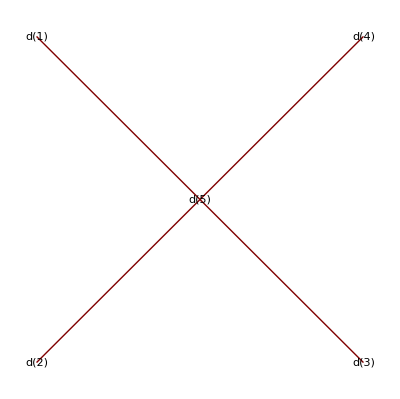
{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],J^*[x_(d[3]i)^(d[3]i)],J^*[x_(d[4]i)^(d[4]i)]}:{d[1]→d[5],d[2]→d[5],d[3]→d[5],d[4]→d[5]}:
-Graphics-

------35:2-----Coefficient:-1/128 ⅈ λ Z_λ

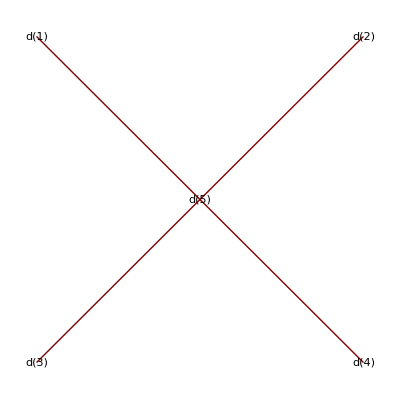
{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],J^*[x_(d[3]i)^(d[3]i)],J^*[x_(d[4]i)^(d[4]i)]}:{d[1]→d[5],d[3]→d[5],d[4]→d[5],d[2]→d[5]}:
-Graphics-

------41:2-----Coefficient:(λ^2 Z_λ^2 Δ[0]^2)/3072

{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],J^*[x_(d[3]i)^(d[3]i)],J^*[x_(d[4]i)^(d[4]i)]}:{d[1]→d[5],d[2]→d[5],d[3]→d[5],d[4]→d[5]}:
-Graphics-

------45:2-----Coefficient:(λ^2 Z_λ^2 Δ[0]^2)/3072

{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],J^*[x_(d[3]i)^(d[3]i)],J^*[x_(d[4]i)^(d[4]i)]}:{d[1]→d[5],d[3]→d[5],d[4]→d[5],d[2]→d[5]}:
-Graphics-

------58:2-----Coefficient:(λ^2 Z_λ^2 Δ[0]^2)/1536

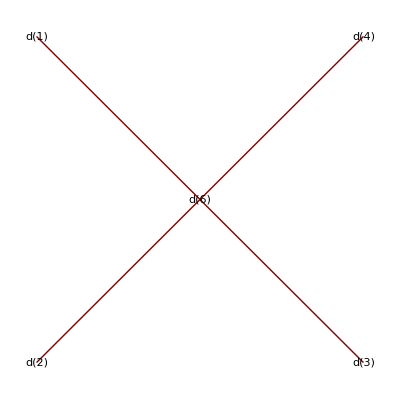
{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],J^*[x_(d[3]i)^(d[3]i)],J^*[x_(d[4]i)^(d[4]i)]}:{d[1]→d[6],d[2]→d[6],d[3]→d[6],d[4]→d[6]}:
-Graphics-

------61:2-----Coefficient:1/960 λ^2 Z_λ^2 Δ[0]

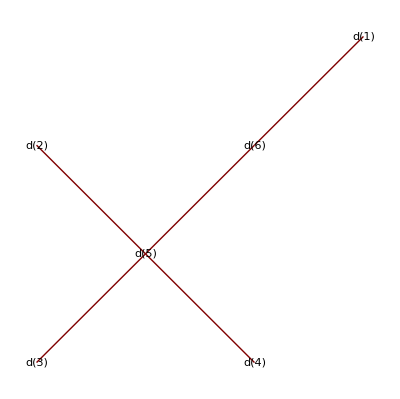
{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],J^*[x_(d[3]i)^(d[3]i)],J^*[x_(d[4]i)^(d[4]i)]}:{d[2]→d[5],d[3]→d[5],d[4]→d[5],d[1]→d[6],d[5]→d[6]}:
-Graphics-

------62:2-----Coefficient:(λ^2 Z_λ^2 Δ[0])/3840

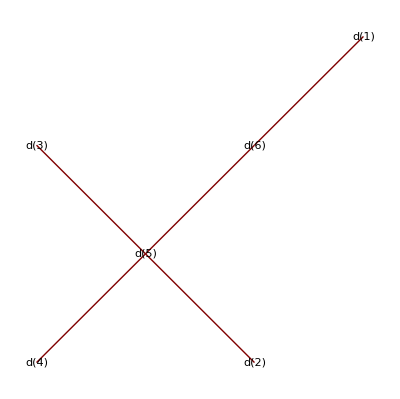
{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],J^*[x_(d[3]i)^(d[3]i)],J^*[x_(d[4]i)^(d[4]i)]}:{d[3]→d[5],d[4]→d[5],d[2]→d[5],d[1]→d[6],d[5]→d[6]}:
-Graphics-

------65:2-----Coefficient:(19 λ^2 Z_λ^2 Δ[0])/15360

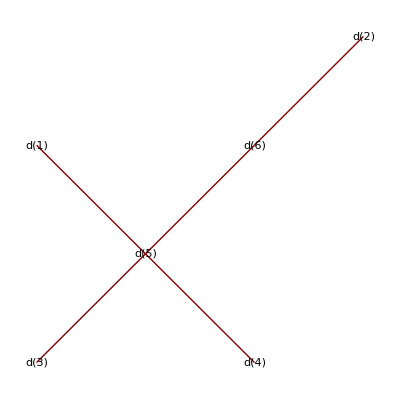
{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],J^*[x_(d[3]i)^(d[3]i)],J^*[x_(d[4]i)^(d[4]i)]}:{d[1]→d[5],d[3]→d[5],d[4]→d[5],d[2]→d[6],d[5]→d[6]}:
-Graphics-

------66:2-----Coefficient:(λ^2 Z_λ^2 Δ[0])/15360

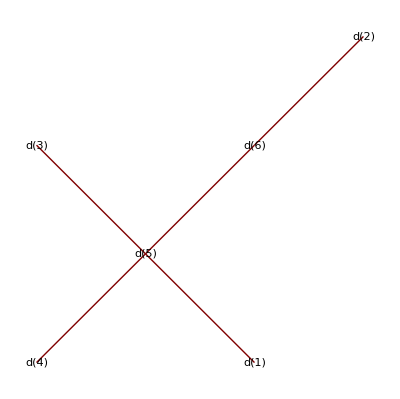
{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],J^*[x_(d[3]i)^(d[3]i)],J^*[x_(d[4]i)^(d[4]i)]}:{d[3]→d[5],d[4]→d[5],d[1]→d[5],d[2]→d[6],d[5]→d[6]}:
-Graphics-

------69:2-----Coefficient:(λ^2 Z_λ^2 Δ[0])/2560

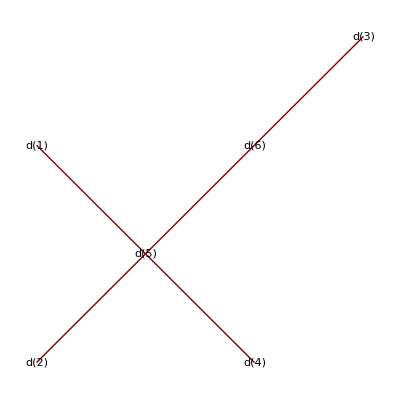
{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],J^*[x_(d[3]i)^(d[3]i)],J^*[x_(d[4]i)^(d[4]i)]}:{d[1]→d[5],d[2]→d[5],d[4]→d[5],d[3]→d[6],d[5]→d[6]}:
-Graphics-

------72:2-----Coefficient:(λ^2 Z_λ^2 Δ[0])/3840

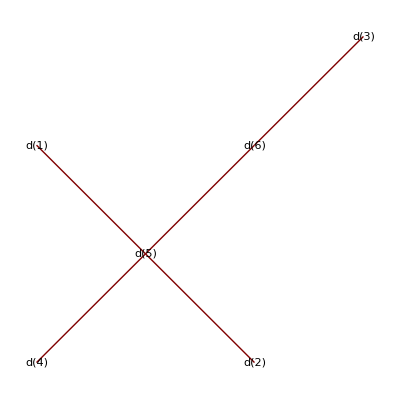
{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],J^*[x_(d[3]i)^(d[3]i)],J^*[x_(d[4]i)^(d[4]i)]}:{d[1]→d[5],d[4]→d[5],d[2]→d[5],d[3]→d[6],d[5]→d[6]}:
-Graphics-

------73:2-----Coefficient:(λ^2 Z_λ^2 Δ[0])/1536

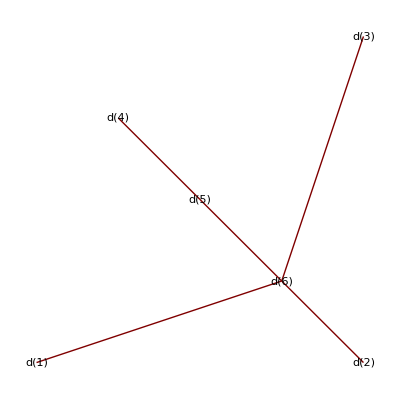
{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],J^*[x_(d[3]i)^(d[3]i)],J^*[x_(d[4]i)^(d[4]i)]}:{d[4]→d[5],d[1]→d[6],d[2]→d[6],d[3]→d[6],d[5]→d[6]}:
-Graphics-

------76:2-----Coefficient:(7 λ^2 Z_λ^2 Δ[0])/7680

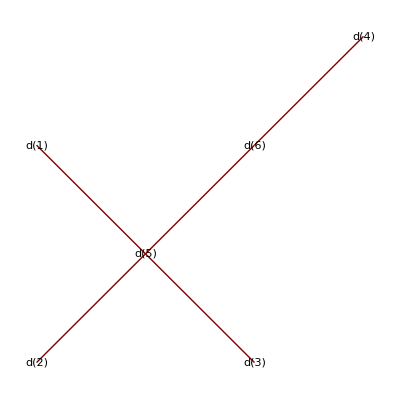
{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],J^*[x_(d[3]i)^(d[3]i)],J^*[x_(d[4]i)^(d[4]i)]}:{d[1]→d[5],d[2]→d[5],d[3]→d[5],d[4]→d[6],d[5]→d[6]}:
-Graphics-

------79:2-----Coefficient:1/960 λ^2 Z_λ^2 Δ[0]

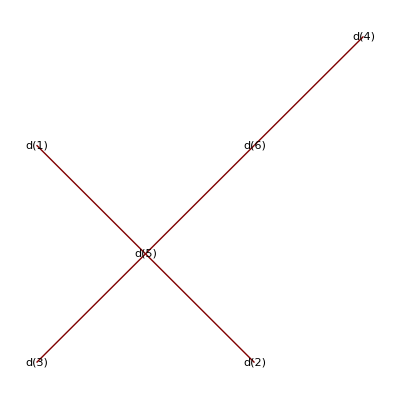
{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],J^*[x_(d[3]i)^(d[3]i)],J^*[x_(d[4]i)^(d[4]i)]}:{d[1]→d[5],d[3]→d[5],d[2]→d[5],d[4]→d[6],d[5]→d[6]}:
-Graphics-

------80:2-----Coefficient:1/512 λ^2 Z_λ^2 Δ[0]

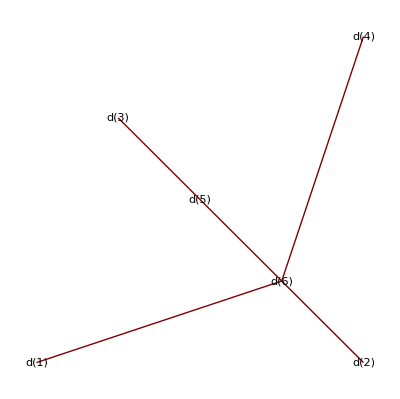
{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],J^*[x_(d[3]i)^(d[3]i)],J^*[x_(d[4]i)^(d[4]i)]}:{d[3]→d[5],d[1]→d[6],d[2]→d[6],d[4]→d[6],d[5]→d[6]}:
-Graphics-

------81:2-----Coefficient:(λ^2 Z_λ^2 Δ[0])/1536

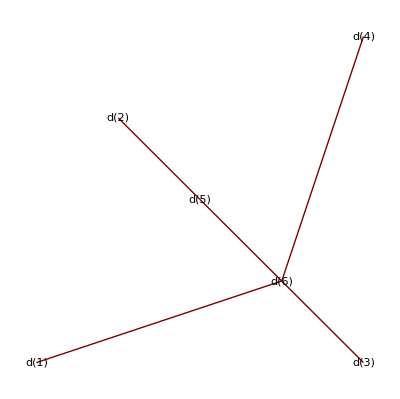
{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],J^*[x_(d[3]i)^(d[3]i)],J^*[x_(d[4]i)^(d[4]i)]}:{d[2]→d[5],d[1]→d[6],d[3]→d[6],d[4]→d[6],d[5]→d[6]}:
-Graphics-

------82:2-----Coefficient:(λ^2 Z_λ^2 Δ[0])/1536

{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],J^*[x_(d[3]i)^(d[3]i)],J^*[x_(d[4]i)^(d[4]i)]}:{d[2]→d[5],d[1]→d[6],d[3]→d[6],d[4]→d[6],d[5]→d[6]}:
-Graphics-

------83:2-----Coefficient:(5 λ^2 Z_λ^2 Δ[0])/4608

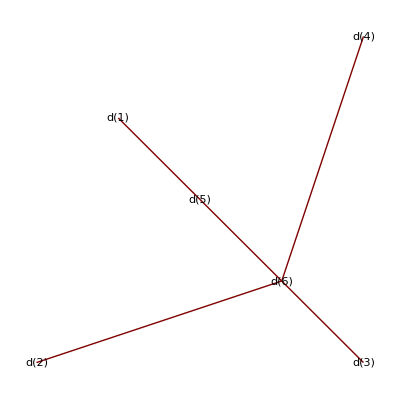
{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],J^*[x_(d[3]i)^(d[3]i)],J^*[x_(d[4]i)^(d[4]i)]}:{d[1]→d[5],d[2]→d[6],d[3]→d[6],d[4]→d[6],d[5]→d[6]}:
-Graphics-

------84:2-----Coefficient:(λ^2 Z_λ^2 Δ[0])/4608

{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],J^*[x_(d[3]i)^(d[3]i)],J^*[x_(d[4]i)^(d[4]i)]}:{d[1]→d[5],d[2]→d[6],d[3]→d[6],d[4]→d[6],d[5]→d[6]}:
-Graphics-

------93:2-----Coefficient:(λ^2 Z_λ^2)/1536

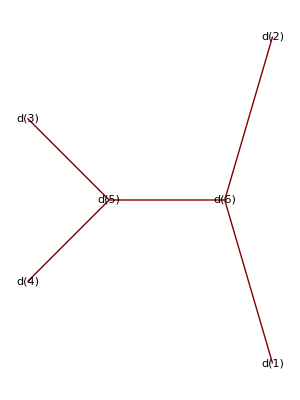
{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],J^*[x_(d[3]i)^(d[3]i)],J^*[x_(d[4]i)^(d[4]i)]}:{d[3]→d[5],d[4]→d[5],d[1]→d[6],d[2]→d[6],d[5]→d[6]}:
-Graphics-

------95:2-----Coefficient:(λ^2 Z_λ^2)/1536

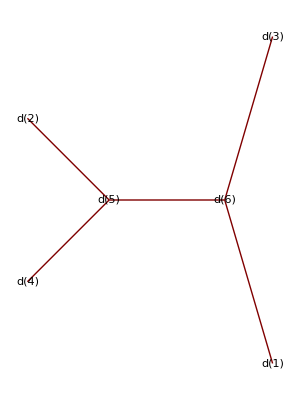
{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],J^*[x_(d[3]i)^(d[3]i)],J^*[x_(d[4]i)^(d[4]i)]}:{d[2]→d[5],d[4]→d[5],d[1]→d[6],d[3]→d[6],d[5]→d[6]}:
-Graphics-

------97:2-----Coefficient:(λ^2 Z_λ^2)/1536

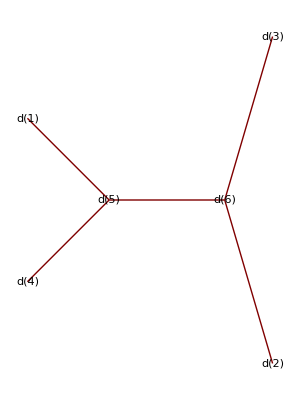
{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],J^*[x_(d[3]i)^(d[3]i)],J^*[x_(d[4]i)^(d[4]i)]}:{d[1]→d[5],d[4]→d[5],d[2]→d[6],d[3]→d[6],d[5]→d[6]}:
-Graphics-

------99:2-----Coefficient:(11 λ^2 Z_λ^2)/7680

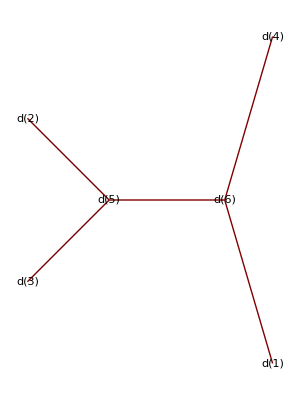
{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],J^*[x_(d[3]i)^(d[3]i)],J^*[x_(d[4]i)^(d[4]i)]}:{d[2]→d[5],d[3]→d[5],d[1]→d[6],d[4]→d[6],d[5]→d[6]}:
-Graphics-

------100:2-----Coefficient:(λ^2 Z_λ^2)/1920

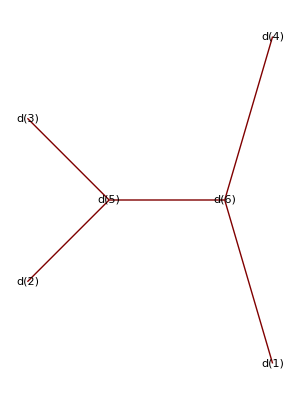
{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],J^*[x_(d[3]i)^(d[3]i)],J^*[x_(d[4]i)^(d[4]i)]}:{d[3]→d[5],d[2]→d[5],d[1]→d[6],d[4]→d[6],d[5]→d[6]}:
-Graphics-

------102:2-----Coefficient:(7 λ^2 Z_λ^2)/3840

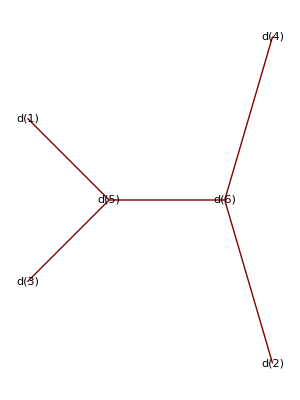
{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],J^*[x_(d[3]i)^(d[3]i)],J^*[x_(d[4]i)^(d[4]i)]}:{d[1]→d[5],d[3]→d[5],d[2]→d[6],d[4]→d[6],d[5]→d[6]}:
-Graphics-

------103:2-----Coefficient:(λ^2 Z_λ^2)/7680

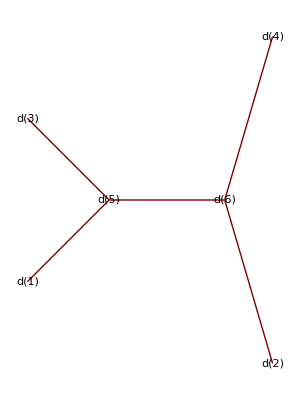
{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],J^*[x_(d[3]i)^(d[3]i)],J^*[x_(d[4]i)^(d[4]i)]}:{d[3]→d[5],d[1]→d[5],d[2]→d[6],d[4]→d[6],d[5]→d[6]}:
-Graphics-

------104:2-----Coefficient:(λ^2 Z_λ^2)/3072

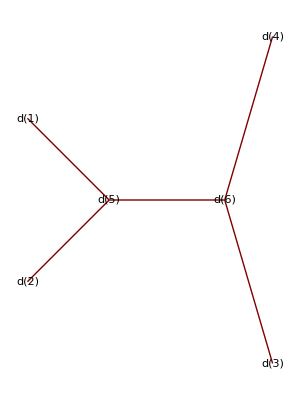
{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],J^*[x_(d[3]i)^(d[3]i)],J^*[x_(d[4]i)^(d[4]i)]}:{d[1]→d[5],d[2]→d[5],d[3]→d[6],d[4]→d[6],d[5]→d[6]}:
-Graphics-

------105:2-----Coefficient:(λ^2 Z_λ^2)/3072

{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],J^*[x_(d[3]i)^(d[3]i)],J^*[x_(d[4]i)^(d[4]i)]}:{d[1]→d[5],d[2]→d[5],d[3]→d[6],d[4]→d[6],d[5]→d[6]}:
-Graphics-

------128:2-----Coefficient:(λ^2 Z_λ^2 Δ[0]^2)/1536

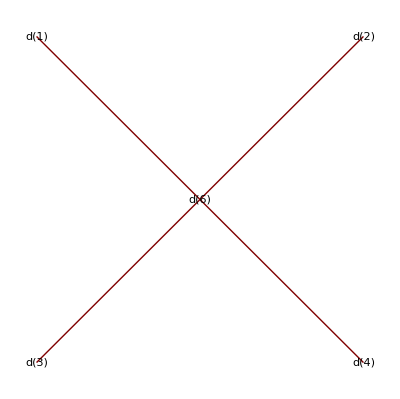
{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],J^*[x_(d[3]i)^(d[3]i)],J^*[x_(d[4]i)^(d[4]i)]}:{d[1]→d[6],d[3]→d[6],d[4]→d[6],d[2]→d[6]}:
-Graphics-

------131:2-----Coefficient:(λ^2 Z_λ^2 Δ[0])/1024

{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],J^*[x_(d[3]i)^(d[3]i)],J^*[x_(d[4]i)^(d[4]i)]}:{d[1]→d[5],d[3]→d[5],d[4]→d[5],d[5]→d[6],d[2]→d[6]}:
-Graphics-

------132:2-----Coefficient:(λ^2 Z_λ^2 Δ[0])/3072

{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],J^*[x_(d[3]i)^(d[3]i)],J^*[x_(d[4]i)^(d[4]i)]}:{d[3]→d[5],d[4]→d[5],d[1]→d[5],d[5]→d[6],d[2]→d[6]}:
-Graphics-

------133:2-----Coefficient:1/768 λ^2 Z_λ^2 Δ[0]

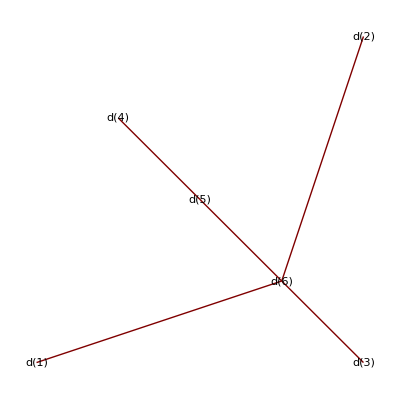
{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],J^*[x_(d[3]i)^(d[3]i)],J^*[x_(d[4]i)^(d[4]i)]}:{d[4]→d[5],d[1]→d[6],d[3]→d[6],d[5]→d[6],d[2]→d[6]}:
-Graphics-

------134:2-----Coefficient:1/768 λ^2 Z_λ^2 Δ[0]

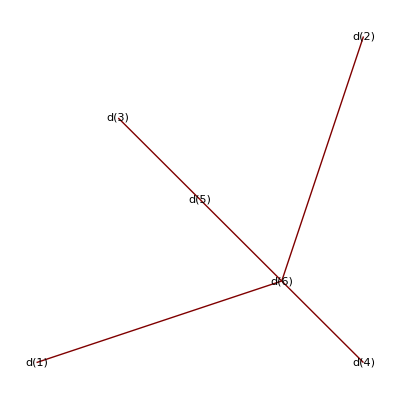
{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],J^*[x_(d[3]i)^(d[3]i)],J^*[x_(d[4]i)^(d[4]i)]}:{d[3]→d[5],d[1]→d[6],d[4]→d[6],d[5]→d[6],d[2]→d[6]}:
-Graphics-

------135:2-----Coefficient:(λ^2 Z_λ^2 Δ[0])/1152

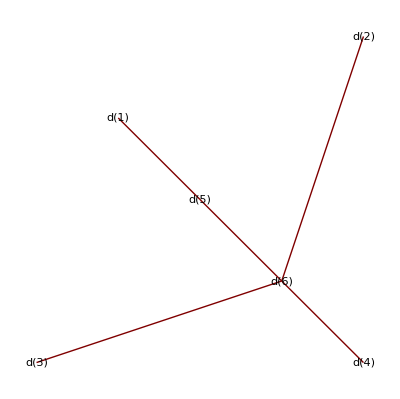
{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],J^*[x_(d[3]i)^(d[3]i)],J^*[x_(d[4]i)^(d[4]i)]}:{d[1]→d[5],d[3]→d[6],d[4]→d[6],d[5]→d[6],d[2]→d[6]}:
-Graphics-

------136:2-----Coefficient:(λ^2 Z_λ^2 Δ[0])/2304

{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],J^*[x_(d[3]i)^(d[3]i)],J^*[x_(d[4]i)^(d[4]i)]}:{d[1]→d[5],d[3]→d[6],d[4]→d[6],d[5]→d[6],d[2]→d[6]}:
-Graphics-

------137:2-----Coefficient:(λ^2 Z_λ^2)/1536

{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],J^*[x_(d[3]i)^(d[3]i)],J^*[x_(d[4]i)^(d[4]i)]}:{d[3]→d[5],d[4]→d[5],d[1]→d[6],d[5]→d[6],d[2]→d[6]}:
-Graphics-

------139:2-----Coefficient:1/960 λ^2 Z_λ^2

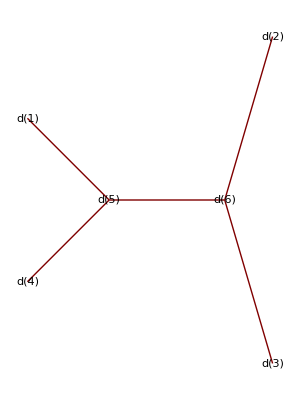
{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],J^*[x_(d[3]i)^(d[3]i)],J^*[x_(d[4]i)^(d[4]i)]}:{d[1]→d[5],d[4]→d[5],d[3]→d[6],d[5]→d[6],d[2]→d[6]}:
-Graphics-

------140:2-----Coefficient:(λ^2 Z_λ^2)/3840

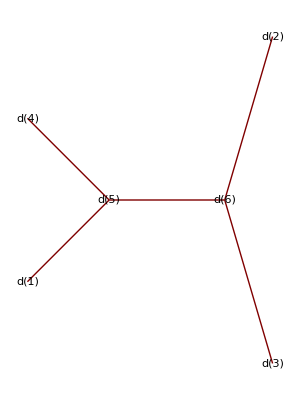
{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],J^*[x_(d[3]i)^(d[3]i)],J^*[x_(d[4]i)^(d[4]i)]}:{d[4]→d[5],d[1]→d[5],d[3]→d[6],d[5]→d[6],d[2]→d[6]}:
-Graphics-

------142:2-----Coefficient:(7 λ^2 Z_λ^2)/7680

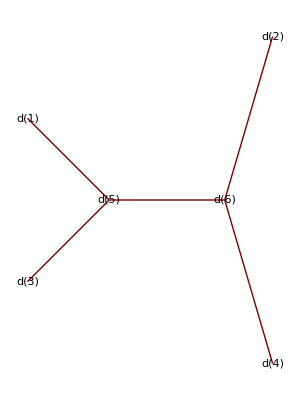
{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],J^*[x_(d[3]i)^(d[3]i)],J^*[x_(d[4]i)^(d[4]i)]}:{d[1]→d[5],d[3]→d[5],d[4]→d[6],d[5]→d[6],d[2]→d[6]}:
-Graphics-

------143:2-----Coefficient:(λ^2 Z_λ^2)/2560

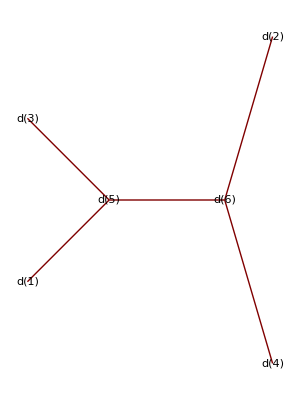
{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],J^*[x_(d[3]i)^(d[3]i)],J^*[x_(d[4]i)^(d[4]i)]}:{d[3]→d[5],d[1]→d[5],d[4]→d[6],d[5]→d[6],d[2]→d[6]}:
-Graphics-

The coefficient Δ[0] represents a loop and its configuration depends upon the other parts of the graph.  A single Δ[0] is a single loop attached at a node point.  A double Δ[0]^2 could represent a loop with 2 nodes which can be inserted in a 4-banch node.

```mathematica
tmp8//Length
PlotΔ[tmp8,2,3]
"The coefficient Δ[0] represents a loop and its configuration depends upon the other parts of the graph.  A single Δ[0] is a single loop attached at a node point.  A double Δ[0]^2 could represent a loop with 2 nodes which can be inserted in a 4-banch node. "
```